### Kalender und Astronomie

Wir laden zuerst die Packages ein:

```mathematica
<<"c:\\Mma14\\AddOns\\Applications\\Astronomy\\finsternisse.m"; 
<<"c:\\Mma14\\AddOns\\Applications\\Astronomy\\Calendrica4.m"; 
<<"c:\\Mma14\\AddOns\\Applications\\Astronomy\\PlanetariumOpen.m"; 
(*<<"f:\\Wissen\\Mma12\\AddOns\\Applications\\Astronomy\\finsternisse.m";
<<"f:\\Wissen\\Mma12\\AddOns\\Applications\\Astronomy\\Calendrica4.m";
<<"f:\\Wissen\\Mma12\\AddOns\\Applications\\Astronomy\\PlanetariumOpen.m";
<<"f:\\Wissen\\Mma12\\AddOns\\Applications\\Astronomy\\Stars250.m"; *)
nextsternbild[ii_]:= If[ii < 12, ii+1, 1]
beforesternbild[ii_]:= If[ii > 1, ii-1,12];
horoskop[datum_ (* als normale Liste *)]:= Module[{sternbilder={Aries, Taurus, Gemini, Cancer, Leo, Virgo, Libra, Scorpius, Sagittarius, Capricornus, Aquarius, Pisces},vergleich, minvergleich, erg={}},
vergleich= Map[Separation[Moon, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Moon,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Sun, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Sun,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Mercury, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Mercury,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Venus, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Venus,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Mars, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Mars,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Jupiter, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Jupiter,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Saturn, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Saturn,sternbilder[[ nextsternbild[minvergleich]]]}];
erg];
rückwärtshoroskop[anfdatum_, anztage_ , planeten__]:= Module[{aktdatum=anfdatum,akttage=anztage,akt,pos, vergleich, minvergleich , erg={},sternbilder={Aries, Taurus, Gemini, Cancer, Leo, Virgo, Libra, Scorpius, Sagittarius, Capricornus, Aquarius, Pisces}},
While[akttage > 0,
Do[akt= {planeten}[[ii]]; pos = Position[sternbilder, akt[[2]]][[1,1]]; 
vergleich = Map[Separation[akt[[1]],#, aktdatum]/Degree&, sternbilder];
minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
If[Not[ minvergleich == beforesternbild[pos]], akttage = akttage -1; aktdatum = DaysPlusC[Apply[Gregorian,aktdatum],1]/. Gregorian -> List; Break[]];
If[ii==Length[{planeten}] ,Print[aktdatum]; erg=Append[erg,aktdatum]],{ii,1,Length[{planeten}]}];
 akttage = akttage -1; aktdatum = DaysPlusC[Apply[Gregorian,aktdatum],1]/. Gregorian -> List];erg];
partielleConjQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= Separation[obj1, obj2, {y,m,d}]/Degree < 10;
totaleConjQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= Separation[obj1, obj2, {y,m,d}]/Degree < 1;
oppositionQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= Separation[obj1, obj2, {y,m,d}]/Degree > 170;
sextileQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 55< Separation[obj1, obj2, {y,m,d}]/Degree < 65;
quadratureQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 85< Separation[obj1, obj2, {y,m,d}]/Degree < 95;
trineQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 115< Separation[obj1, obj2, {y,m,d}]/Degree < 125;
Ephemeride[object_,datum_?GregorianQ,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,(datum/.Gregorian->List)]);
Ephemeride[object_,zeit_List,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,zeit]);
Trennung[object1_,object2_,zeit_,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Separation[object1,object2,zeit]);
Aufgang[object_,datum_,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,(datum/.Gregorian->List)][[6,1]]);
Untergang[object_,datum_,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,(datum/.Gregorian->List)][[6,2]]);
MoonLag[date_, location_]:= 
 Module[{sun, moon, newdate},
newdate=ConvertDateTo[date,Gregorian]/.Gregorian -> List;
sun=Sonnenuntergang[date,location];
moon = Untergang[Moon,newdate, location];
Abs[moon - sun]];
 SonnenfinsternisNurDatum[year_]:=Module[{basislsg},
basislsg=Map[Take[#,3]&, SonnenfinsternisAlternate[year]];
If[year < 1583, Do[basislsg[[i]] = basislsg[[i]] /. List -> Julian,{i,1,Length[basislsg]}], Do[basislsg[[i]] = basislsg[[i]] /. List -> Gregorian,{i,1,Length[basislsg]}]];
basislsg]; 
sofisichtbar[sf_, ort_]:=Module[{stundelocal,l1,l2,l3,l4, entf, erg},
stundelocal=First[TimeOfDay[N[LocalFromUniversal[ToMoment[TimeOfDay[sf[[4]],sf[[5]],sf[[6]]]],ort], 20]]];
If [(stundelocal < 4)|| (stundelocal > 21), erg = 0; Goto[naechst]];
l1=ToExpression[sf[[8]]]/. {N -> 1, S -> -1};
l2 =StringReplace[sf[[9]],"E"->"ee"];l2=ToExpression[l2]/.  {ee -> 1, W -> -1};
l3=ort[[2]] /. (x_ Degree ->  x);
l4=ort[[3]] /. (x_ Degree -> x);
entf=Quiet[GeoDistance[{l1,l2},{l3,l4}]] ;  (* Print[sf[[1]]," ",entf]; *)
Which[First[entf] < 280  && (sf[[7]] === "T"), erg = 2,
280 <= First[entf] < 3000,  erg=1,
First[entf] >= 3000  , erg=0];
Label[naechst];
erg];
 MondfinsternisNurDatum[year_]:=Module[{basislsg},
basislsg=Map[Take[#,3]&, MondfinsternisAlternate[year]];
If[year < 1583, Do[basislsg[[i]] = basislsg[[i]] /. List -> Julian,{i,1,Length[basislsg]}], Do[basislsg[[i]] = basislsg[[i]] /. List -> Gregorian,{i,1,Length[basislsg]}]];
basislsg]; 
Buto[]=Location["Buto, Egypt",Deg[31.1964],Deg[30.7447],Mt[130],3];
Heliopolis[]=Location["Heliopolis, Egypt",Deg[30.1167],Deg[31.3],Mt[150],3];
Memphis[]=Location["Memphis, Egypt",Deg[29.8847],Deg[31.2508],Mt[130],3];
Thebes[]=Location["Thebes, Luxor, Upper Egypt",Deg[25.7206],Deg[32.6103],Mt[130], 3];
Elephantine[]=Location["Elephantine, Upper Egypt",Deg[24.05],Deg[32.53],Mt[130], 3];
Heliacal[Sirius,jyear_,Heliopolis[]]:=
Module[{zurunden},zurunden=199.38446771396522+0.0029665503995562888 jyear+6.653464138557874*^-7 jyear^2-1.8001770959018626*^-10 jyear^3-5.956901002150279*^-14 jyear^4-0.09305356697138213 Cos[jyear]-0.08508049661424438 Sin[jyear];
If[FractionalPart[zurunden]>0.682,zurunden=Ceiling[zurunden],zurunden=Floor[zurunden]];
DaysPlusC[Julian[jyear,1,1],zurunden]];
(* Heliacal[Sirius,jyear_,ort_/; (ort =!= Heliopolis[])]:=DaysPlusC[Heliacal[Sirius,jyear,Heliopolis[]],Round[-19.8628+0.02187*ort[[3]]^2]];*) Heliacal[Sirius,jyear_,Buto[]]:=DaysPlusC[Heliacal[Sirius,jyear,Heliopolis[]],1];
Heliacal[Sirius,jyear_,Memphis[]]:=Heliacal[Sirius,jyear,Heliopolis[]];
Heliacal[Sirius,jyear_,Thebes[]]:=DaysPlusC[Heliacal[Sirius,jyear,Heliopolis[]],-5];
Heliacal[Sirius,jyear_,Elephantine[]]:=DaysPlusC[Heliacal[Sirius,jyear,Heliopolis[]],Round[-6.7]];
sb[j_]:=Module[{s,erg},
s=Floor[480670.95007238846+(365.25239184433957+6.915094340189742*^-7 j) j];
erg=Julian[-480472+s];
erg[[1]]=erg[[1]]-1;
erg];
HeliacalRise[Sirius,j_, Buto[]]:= Module[{bas},
If[j>0,bas=Table[sb[i],{i,j-1,j+2}],bas=Table[sb[i],{i,j,j+3}]];
If[(bas[[1,3]] != bas[[2,3]]) && (bas[[1,3]]==bas[[3,3]]) && (bas[[1,3]]== bas[[4,3]]),
bas[[2,3]]=bas[[1,3]];bas[[2,2]]=bas[[1,2]]];
bas[[2]]];
HeliacalRise[Sirius,jyear_,Heliopolis[]]:=DaysPlusC[HeliacalRise[Sirius,jyear,Buto[]],-1];
HeliacalRise[Sirius,jyear_,Memphis[]]:=HeliacalRise[Sirius,jyear,Heliopolis[]];
HeliacalRise[Sirius,jyear_,Thebes[]]:=DaysPlusC[HeliacalRise[Sirius,jyear,Heliopolis[]],-5];
HeliacalRise[Sirius,jyear_,Elephantine[]]:=DaysPlusC[HeliacalRise[Sirius,jyear,Heliopolis[]],Round[-6.7]];
Heliacal[Venus, jyear_, Buto[]]:= Module[{dd, venuscycles, gd},
dd=DateDistanceC[Julian[jyear+1,1,1],Gregorian[2025,3,27]];
venuscycles= Floor[dd/583.92]+1;
gd= DaysPlusC[Gregorian[2025,3,27],-1*Floor[venuscycles*583.92]];
ConvertDateTo[gd,Julian]]; 
Heliacal[Venus, jyear_, Heliopolis[]]:=DaysPlusC[ Heliacal[Venus, jyear, Buto[]],-1];
Heliacal[Venus, jyear_,Memphis[]]:=DaysPlusC[ Heliacal[Venus, jyear, Buto[]],-5];
Heliacal[Venus, jyear_, Thebes[]]:=DaysPlusC[ Heliacal[Venus, jyear, Buto[]],-6];
EclipticP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[5,2]];
AzimuthP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[8,1]];
AltitudeP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[8,2]];
ElongationP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[3,1]];
MagnitudeP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[9,1]];
RisingP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[6,1]];
SettingP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[6,2]];
MorningSkyP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[9,2]];
AscensionP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[4,1]];
RightAscensionP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[5,1]];
DeclinationP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[4,2]];
DistanceAU[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[3,2]];
Hamburg[]=Location["Hamburg, Germany",Deg[53.55],Deg[10.0],Mt[40],1];
```

Set::wrsym: Symbol Locked is Protected.

### 1. Kalenderbegriffe und allgemeine Berechnungen

Das Programm berücksichtigt viele Kalender, von denen die antiken und observationalen nur experimentell  zur Verfügung stehen. 
Auf keinen Fall sollen Ägyptologen und Assyriologen Daten für ihre geschichtlichen Spekulationen aus diesem Programm beziehen oder dieses als Quelle für ihre Daten benennen.

```mathematica
Calendars[]
```

{Egyptian,EgyptianSecular,Sumerian,Assyrian,AssyrianMP,Canaanite,Phoenician,BabylonianLong,Babylonian,Zoroastrian,ElephantineEgyptian,ElephantineHebrew,Samaritan,MacedonianSeleucid,Qussay,Armenian,Coligny,ObservationalHebrew,Hebrew,OldHinduSolar,OldHinduLunar,Alexandrian,Julian,Roman,Coptic,EgyptianNew,Ethiopic,Qumran,Ezdra,BLC,Persian,ArithmeticPersian,ObservationalIslamic,Islamic,Chinese,Dee,HinduLunar,HinduSolar,Tibetan,MayanLongCount,MayanHaab,MayanTzolkin,AztecXihuitl,AztecTonalpohualli,Balinese,Icelandic,Gregorian,French,ModifiedFrench,Yazdegerd,Illuminati,Bahai,JW,ISO,FutureBahai}

Anmerkungen: Die Kalender der Antike und des Frühmittelalters hatten erhebliche regionale Unterschiede und wurden gelegentlich durch die Willkür von Herrschern geändert. Die hier enthaltenen Implementationen sollen nur als Approximationen dienen und keineswegs phantasiereichen Historikern Stoff für Spekulationen liefern.

Zu jedem Kalender können wir erfahren, aus welchen Komponenten er besteht:

```mathematica
Gregorian[]
```

{CYear,CMonth,CDay}

```mathematica
Chinese[]
```

{CCycle,CYear,CMonth,CLeapMonth,CDay}

Calendrica vereinfacht das Lesen eines Datums, aber behält die interne Struktur:

```mathematica
Gregorian[1965, 5,15]
```

Saturday, 15 May 1965

```mathematica
%//FullForm
```

Gregorian[1965,5,15]

Man kann auch die (englischen) Monatsnamen benutzen, aber nur gefolgt von eckigen Klammern:

```mathematica
Gregorian[1965, May[],15]
```

Saturday, 15 May 1965

Eine einzelne Datumskomponente erhalten wir durch ihren Namen:

```mathematica
CYear[Gregorian[1965, May[],15]]
```

1965

Wir können zu einem Datum feststellen, ob es gültig und in andere Kalender konvertierbar ist:

```mathematica
ValidDateQ[Zoroastrian[1200,5,13]]
```

True

Wieviel verschiedene Jahreskalender (ohne Berücksichtigung der Jahreszahl und der Feiertage) gibt es?

7 mögliche Wochentage für Jahresanfang mal 2 (Schaltjahr ja/nein) = 14

Bei Berücksichtigung der (kathol.) beweglichen Feiertage ist nur das Osterdatum wichtig, da sich die anderen darauf beziehen.
Greg. Kalender mit Wochentagen UND Osterdaten wiederholen sich zyklisch alle 5700000 Jahre. Zum Glück brauchen wir zur Beantwortung unserer Frage keine solch lange Suchschleife zu programmieren, dank folgender Überlegung: Der Ostersonntag fällt immer zwischen den 22. März und 25. April, in dieser Zeitperiode gibt es 5 mögliche Wochen für den Ostersonntag. Für jeden der o.g. 14 Kalender gibt es im 5700000-Jahres-Zyklus jeweils 5 Treffer für einen Ostertermin, daher gibt es 14*5 = 70 mögliche Jahreskalender mit Feiertagen.

Eine hilfreiche Funktion zur Umwandlung eines Datums ist ToFixed, welche die Anzahl der Tage seit Gregorian[1,1,1] angibt:

```mathematica
ToFixed[Gregorian[1992,2,29]]
```

727257

```mathematica
Gregorian[727257]
```

Saturday, 29 February 1992

```mathematica
DayOfWeekC[Julian[1314,3,18]]
```

Monday

Wir können ein Datum auf einen anderen Kalender konvertieren:

```mathematica
ConvertDateTo[Gregorian[-1992,2,29],Julian]
```

17 March 1993 B.C.E.

```mathematica
ConvertDateTo[Gregorian[2009,02,15],ISO]
```

Sunday, Week 7, 2009

Anzahl der Tage seit Gregorian[1,1,1]:

```mathematica
ToFixed[Gregorian[1992,2,29]]
```

727257

Dies ausnutzend, können wir leicht einen Befehl DaysBetween definieren, welcher den Tagesabstand zwischen 2 Daten angibt:
DaysBetween[datum1_,datum2_]:=  ToFixed[datum2]-ToFixed[datum1]
Solch ein Befehl ist jedoch unter dem Namen DateDistanceC bereits eingebaut:

```mathematica
DateDistanceC[Gregorian[1968,9,22],Julian[-585,5,28]]
```

-932222

Praktisch alle o.g. Funktionen sind darauf gebaut, daß ConvertDateTo ein Datum in eine Tagesanzahl umwandelt, mit der weitere Berechnungen durchführen werden können.

Die Kalenderwoche eines Jahres wird nach DIN 1355 bzw. ISO 1601 berechnet.

In welche Kalenderwoche fällt der 29.12.2009 und welcher Tag dieser Woche ist es?

```mathematica
ConvertDateTo[Gregorian[2009,12,29], ISO]
```

Tuesday, Week 53, 2009

```mathematica
%//FullForm
```

ISO[2009,53,2]

Es ist die 53. Woche, der 2te Tag

```mathematica
ConvertDateTo[Gregorian[2009,12,29], ISO][[2]]
```

53

Wie viel Prozent alle Neujahrstage fallen in die 1., wie viel
in die 52. und wie viel in die 53. Kalenderwoche?

```mathematica
Module[{akt,fuenfzwo=0,fuenfdrei=0,eins=0, alle},
Do[akt=CWeek[ConvertDateTo[Gregorian[j,1,1],ISO]];
Which[akt == 1,eins += 1,
            akt == 52, fuenfzwo += 1,
            akt== 53, fuenfdrei += 1]
,{j,2001,2400}];
alle=eins+fuenfzwo+fuenfdrei;Print[{alle,eins,fuenfzwo,fuenfdrei}];
N[{eins/alle,fuenfzwo/alle,fuenfdrei/alle}]]
```

{400,228,101,71}

{0.57,0.2525,0.1775}

Selbstverständlich können wir zu einem Datum auch eine Anzahl von Tagen dazuzählen, das Zieldatum wird im gleichen Kalender angezeigt wie das Startdatum:

```mathematica
DaysPlusC[Gregorian[1900,1,1],366]
```

Wednesday, 2 January 1901

Der folgende Test beantwortet, ob bei zwei Daten das erste vor dem zweiten fällt

```mathematica
earlierQ[Gregorian[2000,1,7], Hebrew[4325,2,7]]
```

False

Zu einem Kalender können wir erfahren, wieviele Tage  ein Durchschnittsjahr hatte:

```mathematica
MeanYear[Babylonian]
```

364.3325

Wieviel Tage des laufenden Jahres sind vorüber?

```mathematica
DayNumber[Gregorian[1999,12,29]]
```

363

Wieviel Tage bleiben noch im laufenden Jahr?

```mathematica
DaysRemaining[Gregorian[1999,12,29]]
```

2

Wann lag der letzte Dienstag vor oder genau auf den 17.3.1999?

```mathematica
Gregorian[KDayOnOrBefore[ToFixed[Gregorian[1999,3,17]],TuesdayC[]]]
```

Tuesday, 16 March 1999

Und der Dienstag danach oder genau auf?

```mathematica
Gregorian[KDayOnOrAfter[ToFixed[Gregorian[1999,3,17]],TuesdayC[]]]
```

Tuesday, 23 March 1999

Daneben gibt es KDayBefore und KDayAfter
Wann davor oder danach war der nächstliegende Dienstag?

```mathematica
Gregorian[KDayNearest[ToFixed[Gregorian[1999,3,17]],TuesdayC[]]]
```

Tuesday, 16 March 1999

Wann fiel der vierte Mittwoch nach dem 17.3.1999-ist es selbst ein Mittwoch,wird er mitgezählt

```mathematica
Gregorian[NthKDay[4,WednesdayC[],Gregorian[1999,3,17]]]
```

Wednesday, 7 April 1999

### 2. Historische Chronometrie

### 2.1. Der Ägyptische Kalender

```mathematica
ConvertDateTo[Egyptian[1,1,1],Gregorian]
```

Wednesday, 18 February -746

Dieses eine "sichere" Umrechnungsdatum genügt, damit wir alle Daten des simplen 365-Tage-Kalenders in solche des Gregorianischen konvertieren können und umgekehrt. 
Da der simple Kalender keine Synchronisation mit den Jahreszeiten aufwies, beklagte 238 B.C.E. Ptolemäus III, daß die Winterfeiern im Sommer fielen und umgekehrt, und er versuchte, alle 4 Jahre einen Extratag einzuführen, hatte also erstmals die Idee des Schaltjahrs. Diese Idee wurde  aber aus religiösen Gründen fallengelassen und Ptolemäus’ Nachfolger mußten bei ihrer Thronbesteigung schwören, keine Schaltjahre einzuführen.
Nachdem im Jahr 45 BCE in Rom der Julianische Kalender mit seinen 365.25 Tagen eingeführt war, war es nun der Fall, daß  1460 der julianischen 365.25-Tage- Jahre genau 1461 ägyptischen 365-Tage-Jahre entsprechen würden. Die damaligen Astronomen haben angenommen, daß das julianische Jahr mit 365.25 Tage genau einem tropischen Jahr entsprechen würden (was aber nicht exakt der Fall ist) und nannten daher die besagten 1460 Jahre "Sothiszyklus" (wobei sie die Präzession völlig vernachlässigten)

Ein heliakischer Aufgang des Sirius (HR), der wie erwähnt nichts mit dem ägyptischen Kalender zu tun hat, ist von Standort und Sehstärke des Beobachters abhängig. Vor diesem HR ist der Sirius etwa 70 Tage lang unsichtbar unter dem Horizont (von Heliopolis aus gesehen, ca. 66.5 Tage), nach dem HR folgt ein dürrer, heisser Monat namens “Hundstage” (die im heutigen Heliopolis Gregorianisch zwischen dem 6.8. und dem 6.9 fallen), in dem Sonne und Sirius gleichzeitig aufgehen.
Man sollte meinen, daß wir bei der erwarteten Fülle überlieferter historischer Heliakischer Aufgänge nicht nur eines, sondern viele von ihnen als Testdaten nutzen könnten. Doch die erwartete Fülle erweist sich als Fehlanzeige, wir finden nur ein einziges Datum mit eindeutiger Jahresangabe, ein HR zur Zeit des Dekrets von Canopus, beobachtet am Observatorium in Buto, am 1. Payni 509 nach Nabonassar (= proleptisch julianisch 19. Juli 239 BCE) 
Wir testen:

```mathematica
Heliacal[Sirius,-239, Buto[]]
```

19 July 239 B.C.E.

```mathematica
ConvertDateTo[Julian[-239,7,19],Egyptian]
```

1 Payni 509 A.N.

In Theben sieht man den HR 6 Tage früher als in Buto, und für jeden dieser Tage liegt der Start des Sothis-Zyklus um ca. 5 Jahre näher. Wir untersuchen, wann der HR 1291 BCE in Theben erfolgte:

```mathematica
Heliacal[Sirius,-1291,Buto[]]
```

18 July 1291 B.C.E.

```mathematica
Heliacal[Sirius,-1291,Thebes[]]
```

12 July 1291 B.C.E.

```mathematica
ConvertDateTo[Julian[-1291,7,12],EgyptianSecular]
```

1 I Akhet -543 A.N.

Wir haben ebenfalls eine Approximation für den heliakischen Aufgang der Venus eingebaut und suchen im Folgenden Kombinationen astronomischer Ereignisse:

```mathematica
Module[{egyptDate,julDate,julm1,julp1,hs,hv},
Do[egyptDate=EgyptianSecular[i,1,1];
julDate=ConvertDateTo[egyptDate,Julian]; 
julm1=DaysPlusC[julDate,-1];
julp1 =DaysPlusC[julDate,1];
hs = HeliacalRise[Sirius,First[julDate],Buto[]];
hv = Heliacal[Venus,First[julDate],Buto[]];
If[julDate == hs  && (hv == julDate  || hv == julm1 || hv == julp1), Print["Sirius + Venus ",julDate]];
  If[NewmoonQ[julDate]  && (hs == julDate  || hs == julm1 || hs == julp1), Print["Sirius + Neumond ",julDate]];
  If[NewmoonQ[julDate]  && (hv == julDate  || hv == julm1 || hv == julp1), Print["Venus + Neumond ",julDate]];
  If[NewmoonQ[julDate]  && (hs == julDate  || hs == julm1 || hs == julp1) && (hv == julDate  || hv == julm1 || hv == julp1)
, Print["Volltreffer: Sirius + Venus + Neumond ",julDate]]
,{i,-2200,3000}]]
```

Sirius + Venus 18 July 2774 B.C.E.

Sirius + Neumond 18 July 2774 B.C.E.

Venus + Neumond 18 July 2774 B.C.E.

Volltreffer: Sirius + Venus + Neumond 18 July 2774 B.C.E.

Sirius + Venus 18 July 1316 B.C.E.

Sirius + Neumond 25 July 1576 C.E.

Venus + Neumond 19 July 1601 C.E.

Approximation Venustransits:

```mathematica
vt[1]= -690913.3208;
vt[i_/; Mod[i,4]==2]:= vt[i-1]+2919.7014;
vt[i_/; Mod[i,4]==3]:= vt[i-2]+47300.227778;
vt[i_/; Mod[i,4]==0]:= vt[i-1]+2919.4563;
vt[i_ /; Mod[i,4]==1 && i>1]:= vt[i-4]+88758.2333;
```

Die Abstände in Tagen zwischen den Transits beruhen auf Daten im astronomischen Format (Gregorian. Jahr, Julian. Monat und Tag)
Auch nach der Umwandlung in Julian kann das Programm nicht wissen, daß das fixed Startdatum ein Gregorianisches Jahr hatte, daher wird bei negativen Werten 1 abgezogen

```mathematica
Module[{akt},
Do[akt=Julian[Floor[vt[i]]];
If[akt[[1]] < 0, vtransit[i]=Julian[akt[[1]]-1,akt[[2]],akt[[3]]],vtransit[i]=Julian[akt[[1]],akt[[2]],akt[[3]]]],{i,1,20}]]
```

Leider genügt die Wahl fester Tagesabstände zwischen Transits nicht für eine ausreichend genaue Approximation, diese Abstände variieren, vor allem in solchen Abständen über Jahrtausende:

```mathematica
Table[vtransit[i],{i,1,20}]
```

{21 May 1893 B.C.E.,19 May 1885 B.C.E.,20 November 1764 B.C.E.,18 November 1756 B.C.E.,23 May 1650 B.C.E.,21 May 1642 B.C.E.,23 November 1521 B.C.E.,20 November 1513 B.C.E.,27 May 1407 B.C.E.,24 May 1399 B.C.E.,25 November 1278 B.C.E.,22 November 1270 B.C.E.,29 May 1164 B.C.E.,27 May 1156 B.C.E.,28 November 1035 B.C.E.,26 November 1027 B.C.E.,31 May 921 B.C.E.,29 May 913 B.C.E.,30 November 792 B.C.E.,28 November 784 B.C.E.}

Daher lesen wir fertig errechnete Daten durch Espenak ein, wo sogar die Uhrzeit der engsten Konjunktion mit angegeben ist:

```mathematica
str=OpenRead["c:\\Mma14\\AddOns\\Applications\\Astronomy\\venustransits.txt"];
sucheBisJahr=-1500;
Module[{basis,year,mona={"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"},month,day,hr,min,erg={}},
Do[basis=ReadLine[str];
year = ToExpression[StringTake[basis,6]];If[year<0,year=year-1];
If[ year > sucheBisJahr,Break[]];
month =Position[mona,StringTake[basis,{8,10}]][[1,1]]; 
day= ToExpression[StringTake[basis,{12,13}]];
hr=ToExpression[StringTake[basis,{33,34}]];
min=ToExpression[StringTake[basis,{36,37}]];
If[year<1583,erg=Append[erg,{Julian[year,month,day],{hr,min,0}}],
erg=Append[erg,{Gregorian[year,month,day],{hr,min,0}}]], {i,1,83}];
Close[str];
erg]
```

{{18 November 1999 B.C.E.,{11,20,0}},{21 May 1893 B.C.E.,{19,26,0}},{19 May 1885 B.C.E.,{12,30,0}},{20 November 1764 B.C.E.,{22,56,0}},{18 November 1756 B.C.E.,{12,18,0}},{23 May 1650 B.C.E.,{0,45,0}},{20 May 1642 B.C.E.,{18,2,0}},{20 November 1521 B.C.E.,{23,44,0}},{18 November 1513 B.C.E.,{12,51,0}}}

```mathematica
Table[Heliacal[Venus,i,Buto[]],{i,-1470, -1440}]
```

{22 June 1471 B.C.E.,27 January 1469 B.C.E.,2 September 1468 B.C.E.,2 September 1468 B.C.E.,9 April 1466 B.C.E.,13 November 1465 B.C.E.,13 November 1465 B.C.E.,20 June 1463 B.C.E.,20 June 1463 B.C.E.,25 January 1461 B.C.E.,31 August 1460 B.C.E.,31 August 1460 B.C.E.,7 April 1458 B.C.E.,11 November 1457 B.C.E.,11 November 1457 B.C.E.,18 June 1455 B.C.E.,18 June 1455 B.C.E.,22 January 1453 B.C.E.,28 August 1452 B.C.E.,28 August 1452 B.C.E.,4 April 1450 B.C.E.,8 November 1449 B.C.E.,8 November 1449 B.C.E.,15 June 1447 B.C.E.,15 June 1447 B.C.E.,20 January 1445 B.C.E.,26 August 1444 B.C.E.,26 August 1444 B.C.E.,2 April 1442 B.C.E.,6 November 1441 B.C.E.,6 November 1441 B.C.E.}

```mathematica
(* Im Folgenden eine Implementation, die auf Daten von van Oosterhut beruht *)
```

```mathematica
vb[1]=-1013006;
vb[i_/; Mod[i,4]==2]:= vb[i-1]+2921.08;
vb[i_/; Mod[i,4]==3]:= vb[i-2]+37620.8;
vb[i_/; Mod[i,4]==0]:= vb[i-1]+2921.08;
vb[i_ /; Mod[i,4]==1 && i>1]:= vb[i-4]+88756.063;
HeliacalRise[Venus, j_, Heliopolis[]]:= Module[{erg={},vg},
vg=ToFixed[Julian[j,1,1]];
If[vg < -1013006, Return[{}]];
Do[erg=vb[i]; If[erg >= vg, Break[]],{i,1,200}];
Julian[Floor[erg]]];
HeliacalRise[Venus, j_, Thebes[]]:= Module[{erg={},vg},
vg=ToFixed[Julian[j,1,1]];
If[vg < -1013006+5844, Return[{}]];
Do[erg=vb[i]+5844; If[erg >= vg, Break[]],{i,1,200}];
Julian[Floor[erg]]];
```

```mathematica
HeliacalRise[Venus, -2770, Heliopolis[]]
```

18 July 2766 B.C.E.

```mathematica
Heliacal[Venus, -1702, Thebes[]]
```

25 August 1703 B.C.E.

```mathematica
ConvertDateTo[Gregorian[-1702,8,6],Julian]
```

21 August 1703 B.C.E.

```mathematica
Trennung[Venus,Sun,{-1702,8,6,0,41,0}, Babylon[]]/Degree
```

9.25954

```mathematica
Table[Heliacal[Venus,i,Thebes[]],{i,-1703, -1701}]
```

{25 August 1703 B.C.E.,25 August 1703 B.C.E.,31 March 1701 B.C.E.}

```mathematica
Do[Print[ConvertDateTo[Heliacal[Venus,i,Buto[]],Gregorian]],{i,1760,1770}]
```

Wednesday, 7 November 1759

Saturday, 13 June 1761

Saturday, 13 June 1761

Tuesday, 18 January 1763

Friday, 24 August 1764

Friday, 24 August 1764

Sunday, 30 March 1766

Wednesday, 4 November 1767

Wednesday, 4 November 1767

Saturday, 10 June 1769

Saturday, 10 June 1769

```mathematica
vb[1]= 595686;
vb[i_/; Mod[i,4]==2]:= vb[i-1]+2919.75;
vb[i_/; Mod[i,4]==3]:= vb[i-2]+47298.55;
vb[i_/; Mod[i,4]==0]:= vb[i-1]+2919.40;
vb[i_ /; Mod[i,4]==1 && i>1]:= vb[i-4]+88756.05;
```

```mathematica
Table[{i,Gregorian[Floor[vb[i]]]},{i,1,20}]
```

{{1,Sunday, 7 December 1631},{2,Sunday, 4 December 1639},{3,Saturday, 6 June 1761},{4,Saturday, 3 June 1769},{5,Wednesday, 9 December 1874},{6,Wednesday, 6 December 1882},{7,Tuesday, 8 June 2004},{8,Wednesday, 6 June 2012},{9,Saturday, 11 December 2117},{10,Saturday, 8 December 2125},{11,Friday, 11 June 2247},{12,Saturday, 9 June 2255},{13,Tuesday, 13 December 2360},{14,Tuesday, 10 December 2368},{15,Monday, 12 June 2490},{16,Tuesday, 10 June 2498},{17,Friday, 16 December 2603},{18,Friday, 13 December 2611},{19,Thursday, 15 June 2733},{20,Friday, 13 June 2741}}

```mathematica
ConvertDateTo[Julian[135,7,21],EgyptianSecular]
```

1 I Akhet 883 A.N.

```mathematica
DaysBetweenC[Julian[378,7,21],Julian[621,7,22]]
```

88757

```mathematica
DaysBetweenC[Julian[621,7,22],Julian[864,7,22]]
```

88756

```mathematica
DaysBetweenC[Julian[864,7,22],Julian[1099,7,24]]
```

85835

```mathematica
DaysBetweenC[Julian[1099,7,24],Julian[1342,7,25]]
```

88757

```mathematica
Heliacal[Venus, -1543, Thebes[]]
```

8 July 1543 B.C.E.

```mathematica
Heliacal[Venus, -1464, Heliopolis[]]
```

12 November 1465 B.C.E.

```mathematica
Heliacal[Venus, -1300, Thebes[]]
```

8 July 1300 B.C.E.

Wegen der Epagomenen tauchen einige Namen zwei mal auf, z.B.

```mathematica
ConvertDateTo[Gregorian[-1746,10,15],Egyptian]
```

2 Thoth -1000 A.N.

Dieser 2. Thoth hat aber eigentlich keinen Namen, da er am Jahresende auftaucht! Der "echte" gehört zu einem anderen gregorianischen Datum:

```mathematica
ConvertDateTo[Egyptian[-1000,1, 2], Gregorian]
```

Thursday, 20 October -1747

Durch Anführung aller ägyptischen Kalenderkomponenten wird die Konversion eindeutig:

```mathematica
ConvertDateTo[date_, EgyptianAnalytic]:= Module[{eu=ConvertDateTo[date, Egyptian], jz, dk, dd, 
ko={" (Birth Osiris)"," (Birth Horus)", " (Birth Seth)", " (Birth Isis)", " (Birth Nephthys)"},comment},
Which[CMonth[eu] < 5, jz = " Achet (Flood)", 4 < CMonth[eu] < 9, jz = " Peret (Sowing)", 8 < CMonth[eu] < 13, jz=" Shemut (Harvest)", CMonth[eu] == 13, jz=" Epagomenen "];
dk = Ceiling[CDay[eu]/10];If[CMonth[eu]==13,comment=ko[[CDay[eu]]], comment=" "];
Print["EgyptianYear: ",CYear[eu]," Season: ",jz," Month: ",CMonth[eu]," Dekan: ",dk," Day: ",CDay[eu],comment] ]
```

```mathematica
ConvertDateTo[Gregorian[-1746,10,15],EgyptianAnalytic]
```

EgyptianYear: -1000 Season:  Epagomenen  Month: 13 Dekan: 1 Day: 2 (Birth Horus)

```mathematica
Map[ConvertDateTo[#,EgyptianAnalytic]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

EgyptianYear: 2709 Season:  Peret (Sowing) Month: 6 Dekan: 1 Day: 10

EgyptianYear: 2750 Season:  Peret (Sowing) Month: 5 Dekan: 3 Day: 22

EgyptianYear: 2754 Season:  Peret (Sowing) Month: 7 Dekan: 3 Day: 30

{Null,Null,Null}

Der armenische Kalender ist identisch mit dem ägyptischen Kalender, beginnt aber am Julian[552,7,11] und hat andere Monatsnamen.

```mathematica
ConvertDateTo[Armenian[1,1,1],Egyptian]//FullForm
```

Egyptian[1300,4,6]

```mathematica
ConvertDateTo[Egyptian[1300,4,6],Armenian]
```

1 Nawasardi 1

Wie im ägyptischen, sind auch im armenischen Kalender keine Schaltjahre bekannt

```mathematica
DaysPlusC[Armenian[1,1,1],12*365]
```

1 Nawasardi 13

Der zoroastrische Kalender im neupersischen Reich beginnt am Julian[632, 6,16], hat ebenfalls andere Monatsnamen, und kennat auch keine Schaltjahre:

```mathematica
Zoroastrian[1,1,1]
```

1 Farvadin 1

```mathematica
DaysPlusC[Zoroastrian[1,1,1],12*365]
```

1 Farvadin 13

### 2.2. Der Babylonische Kalender

```mathematica
meanyear[ObservationalHebrew]
```

365.2175

```mathematica
meanyear[Samaritan]
```

365.2175

```mathematica
meanyear[BLC]
```

365.22

Offizielle Geschichte: Sabbatical years wurden bis zum Ende des Babylonischen Exils alle 7 Jahre eingehalten, das letzte sei damit 525 BCE. Dann folgte ein Sprung von 12 Jahren, und das nächste Sabbatical Year wurde 513 BCE wieder eingeführt. Das hätte auch Auswirkungen auf die Jubilees, die bis 524 BCE alle 49 Jahre eingehalten wurden (Zuckermann), und nach den o.g. 12 Jahren wieder um 512 BCE eingeführt wurden. 
Problem bei dieser Version wäre die Regentschaft des Nabonidus 556 bis 539 BCE, worin sein Sohn Belshazzar stolze 14 Jahre, von 553 bis 539 BCE, Coregent gewesen sein muß.
Alternative Version: man räumt Belshazzar nur 2 Jahre Coregentschaft ein, von 539 BCE bis 537 BCE, und danach regiert er 8 Jahre alleine. Das hieße für Nabonidus, daß er 10 Jahre früher zu regieren begann, die Regierungszeit wäre 566 BCE bis 547 BCE, und babylonische Regierungszeiten davor verschieben sich auch auf 10 Jahre früher. In dieser Version wäre mithin auch die Tempelzerstörung nicht 588/587 BCE, sondern 598/597 BCE erfolgt. Auswirkungen hätte das auch auf die Sabbatjahre, da die Freilassung der Sklaven im Jahr der Tempelzerstörung gem. Jer. 34:8-10 auf Ex 21:2 zurückgeführt wird, weil dieses Jahr ein Sabbatjahr war. Vorteil dieser Version wäre, daß kein Sprung in den Sabbatjahren nötig ist: wenn man 598/597 BCE als Sabbatjahr definiert, wären die historisch belegten Sabbatjahre 164/163 BCE (1 Maccab 6:49-53; Josephus, Antiquities 12.9.7 ) und  38/37 BCE (Josephus Ant 14.6.2) automatisch mit erfasst.

```mathematica
SabbatYearQ[-597]
```

True

```mathematica
SabbatYearZuckermannQ[n_]:=Which[n<-523,Mod[n,7]==0,n>0,Mod[n,7]==6,True,Mod[n,7]==5];
JubileeQ[n_]:=Which[n<-523,Mod[n,49]==15,n>0,Mod[n,49]==7,True,Mod[n,49]==27];
```

Tempelzerstörung durch die Babylonier:
Laut Talmud wurde der erste Tempel an einem Sonntag, den 9 Av, zerstört, das Jahr war entweder ein Sabbatjahr oder das Folgejahr auf ein Sabbatjahr. Damit können wir im Babylonian und ObservationalHebrew, einige Jahre absuchen. 
Setzen wir ein Sabbatjahr voraus, kommt im ganzen 6ten Jhd BCE nur der 18 August 597 BCE in Frage:

```mathematica
Do[akt=ConvertDateTo[Babylonian[i,5,9],Julian];y=akt[[1]];
If[(DayOfWeekC[akt]== "Sunday") ,
If[SabbatYearQ[y],
Print[akt]]] ,{i,-289,-188}]
```

18 August 597 B.C.E.

Setzen wir das Folgejahr eines Sabbatjahrs an, gäbe es nur einen Treffer, der um Jahrzehnte zu spät sein dürfte:

```mathematica
Do[akt=ConvertDateTo[Babylonian[i,5,9],Julian];y=akt[[1]];
If[(DayOfWeekC[akt]== "Sunday") ,
If[SabbatYearQ[y-1],
Print[akt]]] ,{i,-300,-120}]
```

26 August 519 B.C.E.

```mathematica
Do[akt=ConvertDateTo[ObservationalHebrew[i,5,9],Julian];y=akt[[1]];
If[(DayOfWeekC[akt]== "Sunday") ,
If[SabbatYearQ[y] ,
Print[akt]]] ,{i,3140,3300}]
```

1. Tishri -500 BCE to 30. Elul -499 BCE was a Sabbatical Year

15 August 499 B.C.E.

```mathematica
Do[akt=ConvertDateTo[ObservationalHebrew[i,5,9],Julian];y=akt[[1]];
If[(DayOfWeekC[akt]== "Sunday") ,
If[SabbatYearQ[y-1] ,
Print[akt]]] ,{i,3140,3300}]
```

Der Babylonische Kalender trifft exakt, denn zum Zeitpunkt der Tempelzerstörung war nur der Babylonische Kalender gültig, der Hebräische wurde während des Exils diesem angepasst. 
Was wäre, wenn wir für die Trefferjahre direkt den 9 Av herauspicken?

```mathematica
ConvertDateTo[ObservationalHebrew[3164,5,9],Julian]
```

19 July 597 B.C.E.

```mathematica
DayOfWeekC[%]
```

Friday

Im ObservationalHebrew fällt das Datum nicht auf Sonntag. Es ist wahrscheinlich, daß tatsächlich das Datum nach dem Babylonischen Kalender überliefert ist.

```mathematica
ConvertDateTo[Julian[69,7,17],BLC]
```

9 Av 69

```mathematica
DayOfWeekC[%]
```

Sunday

```mathematica
ConvertDateTo[Julian[70,8,5],BLC]
```

9 Av 70

```mathematica
DayOfWeekC[%]
```

Sunday

Assyriologen: Im 37sten Jahr des Nebukadnezar gab es am 14/15 Simanu eine Mondfinsternis. Im 16ten Jahr des Neb, also 21 Jahre früher, wurde der Tempel zerstört, es war ein 9ter  Ab und der fiel  auf einen Sonntag.
Wir untersuchen im gesamten 6ste Jahrhundert BCE alle Mondfinsternisse, die im Juni oder Juli fielen, und wählen unter diesen jene die auf einen 14/15 Simanu fielen.  Vom jeweils gegebenen Jahr gehen wir 21 Jahre zurück und wählen jeden 9ten Ab, der auf einen Sonntag fiel:

```mathematica
Module[{alle,akt,jul,bab, jahr16},
Do[alle=MondfinsternisAlternate[j]; (* alle Mondfinsternisse des Jahres j. Alternate bedeutet automatischer Switch Julian - Gregorian *)
Do[akt=alle[[k]];  (* k-te Mondfinsternis des Jahres j *)
jul={};bab={};
If[akt[[2]]==6 || akt[[2]]==7,
jul=Julian[akt[[1]],akt[[2]],akt[[3]]]; 
bab=ConvertDateTo[jul, Babylonian];
If[bab[[2]]==3,(* Mondfinsternis fällt im Simanu *) 
jahr16=Babylonian[bab[[1]]-20,5,9]; (* der 9te Ab 21 Jahre früher *)
If[DayOfWeekC[jahr16]==="Sunday", 
Print["Tag der Tempelzerstörung: ",jahr16," = ",ConvertDateTo[jahr16,Julian]," -> Mondfinsternis = ",bab," = ",jul]]]],
{k,1,Length[alle]}],{j,-600,-500}]]
```

Tag der Tempelzerstörung: 9 Abu -285 = 18 August 597 B.C.E. -> Mondfinsternis = 14 Simanu -265 = 14 June 577 B.C.E.

```mathematica
{SabbatYearQ[-623],SabbatYearQ[-588],SabbatYearQ[-163],SabbatYearQ[-37], SabbatYearQ[33], SabbatYearQ[69]}
```

{False,False,True,True,False,True}

```mathematica
PriesthoodWeek[datum_]:=Module[{date=ToFixed[datum],basis=-552000 (*This fixed date is a back projection to a time where no priesthood existed.The first sure date where PriesthoodWeek can be applied is-15257*),abstand,wo,ta,namen={"Jehoiarib","Jedaiah","Harim","Seorim","Malchijah","Mijamin","Hakkoz","Abijah","Jeshua","Shecaniah","Eliashib","Jakim","Huppah","Jeshebeab","Bilgah","Immer","Hezir","Aphses","Pethahiah","Jehezekel","Jachin","Gamul","Delaiah","Maaziah"}},If[date>-552001,abstand=date-basis;wo=Mod[Quotient[abstand,7],24]+1;
ta=DayOfWeekC[date];{wo, namen[[wo]],ta},{"At this time was no priesthood in Israel"}]]
```

```mathematica
SabbatYearQ[-588]
```

True

```mathematica
ConvertDateTo[Babylonian[-285,5,9],Julian]
```

18 August 597 B.C.E.

```mathematica
DayOfWeekC[%]
```

Sunday

```mathematica
ConvertDateTo[Babylonian[-295,5,9],Julian]
```

9 August 607 B.C.E.

```mathematica
DayOfWeekC[%]
```

Saturday

```mathematica
PriesthoodWeek[Julian[-597,8,18]]
```

{4,Seorim,Sunday}

```mathematica
PriesthoodWeek[Julian[-587,8,27]]
```

{23,Delaiah,Sunday}

```mathematica
PriesthoodWeek[Julian[-607,8,9]]
```

{9,Jeshua,Saturday}

### 2.3. Griechische Kalender

Zur Analyse der griechischen Kalender brauchen wir die mächtige Funktion Separation, die den Winkelabstand zweier Himmelskörper zu einem bel. Zeitpunkt angibt. Ein Abstand von 0° wäre eine Eclipse bzw ein Transit, eine von 180° eine Opposition. Als Bsp errechnen wir die Separation Mars-Jupiter am 17.11.1993 um 03:20 Uhr:

```mathematica
Separation[Mars,Jupiter,{1993,11,17,3,20,0}]
```

0.596062

```mathematica
(* 34.1518 ° *)
```

```mathematica
Separation[Mars,Jupiter,{1993,11,17,3,20,0}]/Degree
```

34.1518

WolframAlphaQueryResults

34.21 °

Ein erhaltenes griechisches Horoskop spricht von einer Spikaabdeckung durch den Mond im 36. Jahre der ersten "Kallippischen Periode", konkreter am Datum  15. Elaphebolion (griechisch) bzw. 5 Tybi (ägyptisch). Da fast jede griechische Region ihre eigenen Kalenderberechnungen kannte, fiel der "15. Elaphebolion" praktisch allerorts auf einen verschiedenen Tag, so daß das Horoskop der Genauigkit wegen den allgemeineren ägyptischen Kalender zu Hilfe nahm.
Kallippische Perioden umfassen 76 ägyptische Jahre, wobei das erste Jahr der ersten Kallipischen Periode auf das ägyptische Jahr 418 fällt.
Somit können wir eine einfache Funktion Kallippisch[periode_, jahr_] bauen, die das entsprechende ägyptische Jahr errechnet:

```mathematica
Kallippisch[periode_, jahr_]:= 418 + (periode-1)*76 + jahr
```

Auf welches Datum fiel also die beschriebene Spikaabdeckung? Das ägyptische Jahr war

```mathematica
Kallippisch[1,36]
```

454

Das proleptische julianische Datum wäre demnach

```mathematica
ConvertDateTo[Egyptian[454,5,5], Julian]
```

9 March 294 B.C.E.

```mathematica
ConvertDateTo[Egyptian[454,5,5], Gregorian]
```

Saturday, 5 March -293

```mathematica
FullForm[%]
```

Gregorian[-293,3,5]

```mathematica
(* Bestätigt unser Programm die beschriebene Spika-Abdeckung? *)
```

```mathematica
Table[{h, Trennung[Moon, Spica, {-293, 3, 5, h, 0, 0}, Cairo[]]/Degree}, {h,1, 24}]
```

{{1,4.75954},{2,4.27339},{3,3.79148},{4,3.30254},{5,2.83571},{6,2.38286},{7,1.9423},{8,1.55732},{9,1.25608},{10,1.10804},{11,1.17953},{12,1.43254},{13,1.80289},{14,2.21757},{15,2.6608},{16,3.13356},{17,3.60322},{18,4.07921},{19,4.57315},{20,5.05646},{21,5.54189},{22,6.04269},{23,6.53085},{24,7.01987}}

WolframAlphaQueryResults

3.586 °

```mathematica
(* Bei einer Spikaabdeckung spielt der Beobachtungsort keine Rolle *)
```

```mathematica
Table[{h, Separation[Moon, Spica, {-293, 3, 5, h, 0, 0}]/Degree}, {h,1, 24}]
```

{{1,4.75954},{2,4.27339},{3,3.79148},{4,3.30254},{5,2.83571},{6,2.38286},{7,1.9423},{8,1.55732},{9,1.25608},{10,1.10804},{11,1.17953},{12,1.43254},{13,1.80289},{14,2.21757},{15,2.6608},{16,3.13356},{17,3.60322},{18,4.07921},{19,4.57315},{20,5.05646},{21,5.54189},{22,6.04269},{23,6.53085},{24,7.01987}}

```mathematica
(* Die Spikabdeckung wird bestätigt. Selbstverständlich wurde sie erst nach Sonnenuntergang mit dem Auge sichtbar, dem Bericht zufolge wäre das gegen 20 Uhr *)
```

Auf S. 29 gibt Ptolamaios einen weiteren Beobachtungsbericht von Timocharis wieder, wonach im 48. Jahr kallippisch, am 7. Thoth zum 8. Thoth , 3 1/2 Stunden nach Mitternacht, eine weitere Spikaabdeckung durch den Mond stattfand.

```mathematica
Kallippisch[1,48]
```

466

```mathematica
ConvertDateTo[Egyptian[466,1,8], Julian]
```

9 November 283 B.C.E.

```mathematica
(* um 3:30 Uhr *)
```

```mathematica
ConvertDateTo[Egyptian[466,1,8],Gregorian]//FullForm
```

Gregorian[-282,11,5]

```mathematica
Table[{h, Separation[Moon, Spica, {-282, 11, 5, h, 0, 0}]/Degree}, {h,0, 24}]
```

{{0,4.31265},{1,4.8918},{2,5.47215},{3,6.06716},{4,6.64897},{5,7.23121},{6,7.82763},{7,8.41042},{8,8.99338},{9,9.59034},{10,10.1735},{11,10.7567},{12,11.3538},{13,11.937},{14,12.5203},{15,13.1173},{16,13.7005},{17,14.2835},{18,14.8804},{19,15.4633},{20,16.0461},{21,16.6428},{22,17.2253},{23,17.8078},{24,18.4041}}

(* Auch die Abdeckung an diesem Datum wird bestätigt, doch die Funktion Separation ist zu ungenau, um auch noch die richtige Stunde zu treffen. *)

Finnegan erzeugte Tafeln mit der Grösse Olympiad[z,p], das p-te Jahr der z-ten Olympiade. Wir können das Startdatum einer solchen Zeitperiode selbst errechnen:

```mathematica
Olympiad[z_,p_]:=Module[{j=-776+(z-1)*4+p-1,start,fi, erg={}},
If[ j< 394, start=ToFixed[Gregorian[j+1,6,21]];fi=FullMoonAfter[start];
erg=Julian[Floor[fi]],Print["394 C.E. were Antic Olympic games over"]];erg]
```

```mathematica
OlympiadFromJulianYear[-734]
```

{11,3}

```mathematica
JulianYearFromOlympiad[{1,2}]
```

-775

```mathematica
?OlympiadExact
```

OlympiadExact[cycle, year] returns from a given Olympiad cycle and it's year the exact day in Julian calendar it started. It doesn't accept unvalid cycles

```mathematica
OlympiadExact[1,1]
```

23 July 776 B.C.E.

```mathematica
OlympiadExact[1,2]
```

12 July 775 B.C.E.

D.h. Olympiad[1,1] dauerte vom 23 Juli 776 BCE bis 11 Juli 775 BCE

```mathematica
OlympiadExact[117, 3]
```

2 July 310 B.C.E.

```mathematica
OlympiadExact[293,1]
```

10 July 393 C.E.

```mathematica
OlympiadExact[293, 3]
```

394 C.E. were Antic Olympic games over

{}

Es gibt massive Probleme bei den Datierungen. Das Jahr des Angriffs von Xerxes wird von Herodotus wie folgt beschrieben:
In Historien, 7.37 kommt Xerxes zu Frühlingsbeginn (αμα τω εαρι) aus Sardis, als eine Sonnenfinsternis stattfindet. In 8.26 erwähnt er, daß sich die Griechen für ihr Olympiadejahr vorbereiten, d.h. es ist das erste Jahr der olympischen 4-Jahres-Perioden. Und in 9.10 erwähnt er eine zweite Sonnenfinsternis, die im Herbst jenes Jahres nach der Schlacht stattfand. Problem:  man kann das ganze fünfte Jahrhundert nehmen plus minus ein paar Jahrhunderte, ohne daß in Olympischen Jahren berechenbare sichtbare Sonnenfinsternisse solche Kriterien mitmachen - Herodotus muß halluziniert haben!

```mathematica
AtticJahresbeginn[j_]:=Module[{start,fi},start=ToFixed[Gregorian[j+1,6,21]];fi=NewMoonAfter[start];
Julian[Floor[fi]]]
```

```mathematica
AtticJahresbeginn[-310]
```

16 July 310 B.C.E.

```mathematica
ConvertDateTo[%, Gregorian]
```

Wednesday, 11 July -309

Finnegan selbst gab als Startdatum den 1 July 310 B.C.E. an, manche Historiker gehen von einem Tippfehler aus.

312/311 BCE konnte Seleucus I Nicator aus seinem Exil im Ptolmäischen Ägypten kommen und Babylon wiedererobern. Er aktualisierte die Schaltjahrregeln des Babylonischen Kalenders und führte den MacedonianSeleucid Kalender ein, der dem Babylonischen folgt, aber am 1. Tishri (1. Dios) 312 BCE begann

```mathematica
ConvertDateTo[Gregorian[-117,11,17],OldArabic]
```

1 Kislev 118 B.C.E

OldArabic[-117,9,1]

```mathematica
ConvertDateTo[Gregorian[-117,3,22],OldArabic]
```

1 Nisan 118 B.C.E

OldArabic[-117,1,1]

```mathematica
ConvertDateTo[ConvertDateTo[Hebrew[-117,3,22],Gregorian],OldArabic]
```

20 Marheshvan 3878 B.C.E

OldArabic[-3877,8,20]

```mathematica
ConvertDateTo[Gregorian[-246,6,8],MacedonianSeleucid]
```

1 Panemos 65

```mathematica
ConvertDateTo[Gregorian[-117,11,17],MacedonianSeleucid]
```

1 Apellaios -116

```mathematica
ConvertDateTo[Gregorian[-117,11,17],MacedonianSeleucid]
```

1 Apellaios 195

```mathematica
ConvertDateTo[Gregorian[-117,3,22],MacedonianSeleucid]
```

27 Xanthikos 194

### Exkurs: Frühlingsequinox und Präzession

Das übliche Verfahren zur Bestimmung des Frühlingsequinoxes und damit des Jahresanfangs war, einen Stab lotrecht in die Erde zu stecken, dann muß die Schattenlinie bei Sonnenaufgang mit der bei Sonnenuntergang an der Tagundnachtgleiche eine gerade Linie bilden. Statt der Sonne nahm man einen hellen Stern, den man über den Stab anpeilte. Der Stern, der an der Herbst-Tagundnachgleiche in der Sonne steht, ist um Mitternacht der Frühlings-Tagundnachgleiche genau im Süden (im 2/1 Jh v.u.Z. hieß dieser Stern Spika). Um 290 v.u.Z. wandte Timocharis dieses Verfahren an, und um 130 v.u.Z. Hipparch, der die Aufzeichnungen des Timocharis benutzte. Ptolemäus, Almagest VII, 2 u 3, bemerkt, Hippparch hätte eine Abweichung von 6°, Timocharis von 8°. Aus diesem Unterschied erkannte Hipparch die Präzession (=Bewegung des Punktes der Tagundnachtgleiche über die Ekliptik) oder gleichbedeutend, daß das siderische Jahr länger als das tropische ist. 
Wegen der Präzession fällt der Frühlingsequinox heute erst auf den April.
Pierre Laplace (1749-1827) und Friedrich Bessel (1784-1846) zeigten überdies, daß wegen der Präzession das tropische Jahr keine konstante Größe sein kann, und Simon Newcomb (1835-1900) konnte seine Länge formelmäßig angeben:

```mathematica
tropJahr[jahr_]:=365.24219879-61.4*10^-9*(jahr-1900)
```

Hier die Länge des Jahres 33 u.Z.

```mathematica
N[tropJahr[33],20]
```

365.242

N kürzt merkwürdig ab, aber mit Copy and Paste bekommen wir die verlangte Länge der Zahl zu sehen

```mathematica
gms[24*0.2423134238]
```

{5.,48.,55.8798}

Jahr 33 u.Z.hatte 365 d,5 h,48 m,55.8798 sec

```mathematica
N[tropJahr[2004],20]
```

365.242

```mathematica
N[tropJahr[48901],20]
```

365.239

```mathematica
gms[24*0.24219252719996]
```

{5.,48.,45.4344}

Heuer hat es 365 d,5 h,48 m,45.45 sec

Die Präzession enthält einen Zyklus von 25874.7 Jahren, dann ist der Frühlingsequinox wieder am gleichen Punkt der Ekliptik. Also muß das tropische Jahr 12937.4 Jahre lang ab- und 12937.4 Jahre lang wieder zunehmen, und in dieser Zeitspanne beträgt der Unterschied zwischen längstem und kürzestem tropischen Jahr etwa eine Minute. Heuer haben wir ungefähr ein Durchschnittsjahr. Wir können die Durchschnittslänge eines tropischen Jahres mit 365.2422454 mittleren Sonnentagen und die eines siderischen mit 365.2563612 mittleren Sonnentagen angeben, letzteres ist also um ca. 20 Minuten länger. Die Länge einer Präzessionperiode ergibt sich, wenn der Frühlingsequinox wieder im gleichen Sternbild erscheint, d.h. wenn sich die Differenz zwischen siderischem und tropischem Jahr auf ein tropisches Jahr akkumuliert hat:

```mathematica
N[Solve[(365.2563612-365.2422454)*j==365.2422454,j],30]
```

{{j→25874.7}}

```mathematica
DecimalForm[25874.71099049702*365.2422454, 20]
```

9450537.54124519

```mathematica
gms[25874.71099049702*365.2422454*24]
```

{2.26813×10^8,59.,23.5844}

Die Präzessionperiode dauert also 25874.71 tropische Jahre.
Wieviele Jahre dauert es, damit sich der Frühlingsequinox um 1° weiterbewegt?

```mathematica
25874.71 Jahre/360
```

71.8742 Jahre

Hipparch  hatte irrtümlich 100 Jahre angesetzt, damit sich der Frühlingsequinox um 1° weiterbewegt, daher meinte Newton, die griechische Geschichte müsse im Verhältnis 4:7 verkürzt werden.
Als „Startjahr“, auf welches man Jahresangaben beziehen konnte, benutzte man die Einführung der Olympischen Spiele, die im Julianischen Kalender ausgedrückt, zwischen 776 v.u.Z. und 393 u.Z. alle 4 Jahre stattfanden. Doch man kam auch oft von dieser Konvention ab und benutzte stattdessen als Fixpunkt den Regierungsbeginn von Kaisern und Konsuln. Der Beginn eines Jahres war, wie erwähnt, bei den meisten Völkern mit dem Frühlingsequinox verbunden.
Newton nahm an, der Frühlingsequinox sei zur Zeit der Geburt Christi bei 2° Aries und zur Zeit des Ptolemäus (144 u.Z.) bei 0° Aries.
Hipparch meinte, zu seiner Zeit sei der Frühlingsequinox bei 4° Aries, und Meton, zu seiner Zeit sei er bei 8° Aries. Newton rundete 72 Jahre pro Grad Verschiebung. Auf welche Daten legte er Hipparch und Meton? 
Von Christus bis Hipparch sind es 2°, Abzug des Nulljahres nicht vergessen!

```mathematica
hipparch = -(2*72+1)
```

-145

```mathematica
meton = -(6*72+1)
```

-433

### 2.4. Der Julianische Kalender

Griechische Astronomen nach Hipparch erkannten, da ein trop.Jahr (fast konstant) 365.2422.. mittlere Sonnentage habe, müssen in einem Sonnenkalender innerhalb von 10000 Jahren 1211 Schaltjahre vorkommen.Um eine gleichmäßige Verteilung zu erreichen,benutzt man Kettenbrüche:1211/5000=1/(5000/1211)=1(4+156/1211);vernachlässigt man die 156/1211,so hat man die erste Näherung K1=1/4,d.h.alle 4 Jahre kommt ein Schaltjahr bzw.1 Jahr=365 1/4 mittlere Sonnentage.156/1211=1/(1211/156)=1/(7+119/156);vernachlässigt man die 119/156,so hat man die zweite Näherung K2=1/(4+1/7)=1/((28+1)/7)=7/29,d.h.1 Jahr=365 7/29 mittlere Sonnentage.119/156=1/(156/119)=1/(1+37/119);vernachlässigt man die 37/119,so hat man K3=1/(4+1/(7+1))=1/(4+1/8)=1/((32+1)/8)=8/33,d.h.1 Jahr=365 8/33 mittlere Sonnentage.Astronom Sosigenes aus Alexandria empfahl Julius Cäsar,es bei der ersten Näherung bewenden zu lassen.Die römischen Jahre sollten mit dem g beginnen,dem Februarius als Monat des Gedenkens Verstorbener sollte eine damals traditionell eingehaltene Länge von 24 Tagen belassen und allen anderen 31 Tage gegeben werden. Jedes vierte Jahr sollte dem Februarius aber ein Schalttag zugefügt werden. Der 24. Februar wurde als "Tag VI vor den Kalenden des März" (ante diem VI Kal.Martii), der Schalttag als "zweiter Tag VI vor den Kalenden des März" (ante diem bis VI Kal.Mar.) bezeichnet.

```mathematica
ConvertDateTo[Julian[15,2,24],Roman]
```

ante diem VI Kalends March, 15 C.E.

```mathematica
ConvertDateTo[Julian[16,2,25],Roman]
```

ante diem bis VI Kalends March, 16 C.E.

```mathematica
Map[ConvertDateTo[#,Roman]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{ante diem VI Kalends October, MCMLX C.E.,ante diem IV Kalends September, MMI C.E.,pridie Nones November, MMV C.E.}

Julius Cäsar nahm dies an und führte im Januar des Jahres 708 „seit der Gründung Roms“ (46 B.C.E bzw. -45 Gregorianisch) den Julianischen Kalender ein, wobei er den wärmsten langen Monat, den Quintilis, nach ihm selbst benannte. Dieses erste Jahr der Einführung des Julianischen Kalenders bekam auch noch 2 Schaltmonate und darum 445 Tage, und ist daher als annus confusionis bekannt.
Noch während der Regierung Julius Cäsars änderte man dieses System, indem man dem Februar mehr Tage gab und dafür jedem zweiten Monat einen abzog, damit sich lange und kurze Monate abwechselten:
Martius (31 Tage, Sonne bis zum 21 im Sternbild Fische), Aprilis (30, im Widder), Maius (31, im Stier), Iunius (30, in den Zwillingen), Quintilis = Iulius (31, im Krebs), Sextilis (30, im Löwen), September (31, in Jungfrau), Oktober (30, in der Waage), November (31, im Skorpion), December (30, im Schützen), Ianuarius (31, im Steinbock), Februarius (29, im Wassermann)
Wie Julius dem Quitilis, gab sein Nachfolger Gaius Octavianus Augustus (regierte 31 B.C.E bis 14 C.E.) aus Eitelkeit dem Sextilis seinen Namen und ernannte auch diesen zum langen 31-Tage-Monat, wobei er den Tag vom Februarius wegnahm. Die nachfolgenden Monate hatten sich wieder abzuwechseln, also September 30, Oktober 31, November 30, December 31. Außerdem monierte er, daß der Kalender seines Vorgängers den Herbstequinox 3 Tage später ansetzen sollte, damit diese auf seinen Geburtstag, den 23.Sept, falle (was belegt, daß der Frühlingsequinox nach Cäsar tatsächlich auf den 21.März fiel). Dementsprechend monierte Augustus, daß man nach Cäsars Tod wegen einer fehlerhaften Interpretation alle drei Jahre geschaltet hatte, ließ von den fünf Schalttagen zwischen röm 745 und röm 761 (9 B.C.E. bis 8 C.E.) drei ausfallen und verschob damit den Frühlingsequinox auf den 24.März (Edmund Buchner, Die Sonnenuhr des Augustus, Mainz 1982). Die folgende Prüfung auf Schaltjahre ist demnach fehlerhaft:

```mathematica
Table[{i,JulianLeapYearQ[i]},{i,-9,8}]
```

{{-9,True},{-8,False},{-7,False},{-6,False},{-5,True},{-4,False},{-3,False},{-2,False},{-1,True},{0,False},{1,False},{2,False},{3,False},{4,True},{5,False},{6,False},{7,False},{8,True}}

Nach der Reform war röm 761 ein Schaltjahr, es entspricht 8 u. Z., und es ist also Zufall, daß genau die durch vier teilbaren Jahre Schaltjahre sind. Der heute als „Julianischer“ bezeichnete Kalender sollte daher besser „Augusteischer“ heißen und es ist ein Fehler, die Julianischen Kalenderregeln, wie sie uns für die Zeit nach der Regierung Augustus‘ (bis 14 u.Z.) vorliegen, auf vorher liegende Zeiten zurückzuprojizieren (wie es bei Kalenderberechnungen üblich ist).

Das Julianische Jahr war um 0.0078 Tage (11 m, 14 s) länger als das (fast konstante) tropische. Das hieß, daß Tagundnachgleichen und Sonnenwenden bei sich allmählich akkumulierenden Fehlern auf frühere Tage fielen. Ungefähr beim Konzil von Nizäa (325 C.E.) muß der Frühlingsequinox auf den 21.März gefallen sein.
Wie weit hatte sich die Frühlingsequinoxverschiebung von Cäsar (Einführung -46 B.C.E.) bis 1582 C.E. akkumuliert?

```mathematica
N[∑_(i=-46)^-1 (365.25-tropJahr[i])+∑_(i=1)^1582 (365.25-tropJahr[i]),10]
```

12.5873

```mathematica
gms[24*0.587263220840782]
```

{14.,5.,39.5423}

Er hatte sich auf 12 d,14 h,5 m und 39.54 sec akkumuliert. Davon sind die 3 Tage abzuziehen, die Augustus korrigiert hatte: der Frühlinspunkt mußte nun 9 d, 14 h, 5 m und 39.54 s früher eintreten.
Der Julianische Kalender verleitet durch seinen Namen zur Fehlannahme, daß er von Anfang an durch Julius Cäsar sein Startdatum hatte. Dies ist aber falsch, noch Jahrhunderte später bekam er willkürlich neue Startdaten nach Regierungsantritten von Herrschern, die traditionell den 1 Thoth für ihren Regierungsantritt wählten, bis mit Diocletian eine Ära begann, die bis zu Dionysius Exiguus dauerte

```mathematica
(* Nabonassar Ära *)ConvertDateTo[Egyptian[1,1,1],Julian]
```

26 February 747 B.C.E.

```mathematica
(* Philippische Ära *)ConvertDateTo[Egyptian[425,1,1],Julian]
```

12 November 324 B.C.E.

```mathematica
(* Augustus Ära *) ConvertDateTo[Egyptian[719,1,1],Julian]
```

31 August 30 B.C.E.

```mathematica
SabbatYearQ[69]
```

True

```mathematica
{Samaritan[11779], ObservationalHebrew[11779], Julian[11779]}
```

{15 Nisan 1671,yom shishi, 14 Nisan 3793 A.M.,3 April 33 C.E.}

Entgegen der Behauptung des Josephus, Antiquities III. 10, Sect. 5, befand sich die die Sonne weder am 6.4.30 noch am 3.4.33 im Sternbild Aries, sondern im Sternbild Pisces.

```mathematica
Ephemeris[Sun,{30,4,6}]
```

Sun
------------------------------------------
Date Time:   06-Apr-30 00:00:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        7:38 am (SunriseP:  7:41 am)
Setting:       7:05 pm (SunsetP:   7:12 pm)
------- For Date Time, Geo-place: --------
Azimuth:       215^22' (SouthWest compass)
Altitude:      -53^10' (Below the horizon)
------- For Date Time: -------------------
Elongation:      0^00' (DawnDuskSky. 100%)
Distance:      1.01 AU (Magnitude:  -26.6)
------- For Date Time: -------------------
Ascension:     0h55.3m (Pisces        14^)
Declination:     5^59' (Ecliptic +  0^00')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Sun,{33,4,3}]
```

Sun
------------------------------------------
Date Time:   03-Apr-33 00:00:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        7:36 am (SunriseP:  7:38 am)
Setting:       7:09 pm (SunsetP:   7:15 pm)
------- For Date Time, Geo-place: --------
Azimuth:       214^57' (SouthWest compass)
Altitude:      -52^08' (Below the horizon)
------- For Date Time: -------------------
Elongation:      0^00' (DawnDuskSky. 100%)
Distance:      1.01 AU (Magnitude:  -26.6)
------- For Date Time: -------------------
Ascension:     0h45.5m (Pisces        11^)
Declination:     4^57' (Ecliptic +  0^00')
------------------------------------------

-EphemerisData-

Ein original "Hexensabbath" findet an einem 14. Nisan statt und beginnt Freitags ab 18 Uhr. Der Tag der Kreuzigung Christi, Julian[33,4,3], endete mit einem solchen. Wann ist der nächste?

```mathematica
Module[{fi},
Do[fi=ClassicalPassoverEve[i];
If[NameFromDayOfWeekC[DayOfWeekCFromFixed[fi]] == "Friday", Print[i]; Break[]],{i,2020,3000}]]
```

2026

```mathematica
horoskop[{2025,1,21,20,0,0}]
```

{{Moon,Libra},{Sun,Aquarius},{Mercury,Capricornus},{Venus,Pisces},{Mars,Cancer},{Jupiter,Gemini},{Saturn,Pisces}}

Die Eingabezeit in der Funktion horoskop ist immer gemäß Gregorianischem Kalender. Daher wäre es zur Zeit der Kreuzigung:

```mathematica
horoskop[{33,4,1, 15,0,0}]
```

{{Moon,Libra},{Sun,Aries},{Mercury,Pisces},{Venus,Pisces},{Mars,Gemini},{Jupiter,Gemini},{Saturn,Cancer}}

Kepler hat berechnet, daß am 29.5.7 BCE, am 3.10.7 BCE und am 4.12.7 BCE Konjunktionen von Jupiter und Saturn im Sternbild Pisces stattfanden.
Zuerst wird das Datum auf Gregorianisch konvergiert, und dann horoskop angewandt:

```mathematica
Map[ConvertDateTo[#,Gregorian]&,{Julian[-7,5,29],Julian[-7,10,3],Julian[-7,12,4]}]
```

{Friday, 27 May -6,Saturday, 1 October -6,Friday, 2 December -6}

```mathematica
horoskop[{-6,5,27}]
```

{{Moon,Gemini},{Sun,Gemini},{Mercury,Cancer},{Venus,Cancer},{Mars,Virgo},{Jupiter,Pisces},{Saturn,Pisces}}

```mathematica
horoskop[{-6,10,1,12,0,0}]
```

{{Moon,Aquarius},{Sun,Libra},{Mercury,Libra},{Venus,Scorpius},{Mars,Sagittarius},{Jupiter,Pisces},{Saturn,Pisces}}

```mathematica
horoskop[{-6,12,2,12,0,0}]
```

{{Moon,Taurus},{Sun,Sagittarius},{Mercury,Sagittarius},{Venus,Libra},{Mars,Capricornus},{Jupiter,Pisces},{Saturn,Pisces}}

```mathematica
(* Aspekte: oppositionQ Venus-Mond, quadratureQ Jupiter-Merkur, trineQ Saturn-Merkur *)
```

```mathematica
{oppositionQ[Venus,Moon, Gregorian[33,4,1]], quadratureQ[Jupiter, Mercury, Gregorian[33,4,1]], trineQ[Saturn, Mercury,Gregorian[33,4,1]]}
```

{True,True,True}

WolframAlphaQueryResults

169.7 °

```mathematica
PlanetData["Venus",
```

WolframAlphaQueryResults

88.52 °

WolframAlphaQueryResults

120.1 °

Wann tritt in Zukunft die Konstellation auf mit Passah auf einem Freitag und Sonne im Widder, Venus in den Fischen und Saturn im Krebs?

```mathematica
Module[{fi, gd,lgd, hgd, erfolgQ = False},
Do[fi=ClassicalPassoverEve[i];
If[NameFromDayOfWeekC[DayOfWeekCFromFixed[fi]] == "Friday", 
gd=ConvertDateTo[fi, Gregorian]; lgd= gd /. Gregorian -> List; hgd = horoskop[lgd];
If[MemberQ[hgd,{Sun, Aries}] && MemberQ[hgd, {Venus, Pisces} && MemberQ[hgd, {Saturn, Cancer}]] , erfolgQ = True; Print["Konstellation gefunden : ",gd]]; If[erfolgQ, Break[]]],{i,2000,3000}]]
```

Konstellation gefunden : Friday, 6 April 2300

Wann tritt in Zukunft die Konstellation auf mit Passah auf einem Freitag, mit Mondfinsternis, und Sonne im Widder, Venus in den Fischen und Saturn im Krebs?

```mathematica
Module[{fi,mofi, gd,lgd, hgd, erfolgQ = False},
Do[fi=ClassicalPassoverEve[i];
If[NameFromDayOfWeekC[DayOfWeekCFromFixed[fi]] == "Friday", 
mofi=Map[ToFixed, MondfinsternisNurDatum[i]];
If[MemberQ[mofi, fi],
gd=ConvertDateTo[fi, Gregorian]; lgd= gd /. Gregorian -> List; hgd = horoskop[lgd];
If[MemberQ[hgd,{Sun, Aries}] && MemberQ[hgd, {Venus, Pisces} && MemberQ[hgd, {Saturn, Cancer}]] , erfolgQ = True; Print["Konstellation gefunden : ",gd]]]]; 
If[erfolgQ, Break[]],{i,2000,3000}]]
```

Wann treten in Zukunft die Aspekte auf, d.h. Passah auf einen Freitag, Quadratur Jupiter-Merkur und Dreieck Saturn-Merkur?

```mathematica
Module[{akt = Gregorian[1999,12,31]},Do[akt=DaysPlusC[akt, 7]; 
 If[quadratureQ[Jupiter, Mercury, akt] && trineQ[Saturn, Mercury, akt] && akt == ConvertDateTo[ ClassicalPassoverEve[CYear[akt]],Gregorian],
Print["Aspekte gefunden: ",akt];Break[]], {200000}]]
```

Aspekte gefunden: Friday, 30 March 2773

Wann fällt eines der observationalen oder errechneten Passahfeste auf eine Mondfinsternis? Wir wählen einen grosszügigen Zeitraum um den Zeitpunkt der Kreuzigung zwischen 20 C.E. und 40 C.E.:

```mathematica
Module[{mofi, fi1, fi2, fi3, fi4, fi5},
Do[mofi=Map[ToFixed, MondfinsternisNurDatum[i]]; 
fi1=Passover[i]-1;
If[MemberQ[mofi, fi1], Print["Passover: ",Julian[fi1]]];
fi2 =  ClassicalPassoverEve[i];
If[MemberQ[mofi, fi2], Print["ClassicalPassover: ",Julian[fi2]]];
fi3 = ToFixed[Samaritan[1638+i,1,14]];
If[MemberQ[mofi, fi3], Print["Samaritan 14 Nisan: ",Julian[fi3]]];
fi4 = ToFixed[Samaritan[1638+i,1,15]];
If[MemberQ[mofi, fi4], Print["Samaritan 15 Nisan: ",Julian[fi4]]];
fi5 = ToFixed[BLC[i,1,14]];
If[MemberQ[mofi, fi5], Print["BLC 14 Nisan: ",Julian[fi5]]];
,{i,20,40}]]
```

Samaritan 15 Nisan: 25 April 31 C.E.

Passover: 14 April 32 C.E.

Passover: 3 April 33 C.E.

ClassicalPassover: 3 April 33 C.E.

Samaritan 15 Nisan: 3 April 33 C.E.

BLC 14 Nisan: 23 March 34 C.E.

```mathematica
PriesthoodWeek[Julian[70,8,5]]
```

{1,Jehoiarib,Sunday}

```mathematica
(* Bei Diocletian waren schon Schalttage eingeführt, mit ihm begann der koptische Kalender. Ära Diocletian: *)
```

```mathematica
ConvertDateTo[Coptic[1,1,1],Julian]
```

29 August 284 C.E.

```mathematica
ConvertDateTo[Julian[284,8,29],Coptic]
```

1 Tut 1 A.M.

### 2.5. Der äthiopische und der koptische Kalender

Der Amharisch-Äthiopische Kalender begann am Julian[8,8,29]. Er kennt wie der julianische ein Jahr mit 365 bzw. 366 Tagen, jedoch hier unterteilt in 12 Monate a 30 Tage und einen dreizehnten mit 5 bzw. 6 Tagen.

```mathematica
ConvertDateTo[Julian[329,8,29], Ethiopic]
```

Arb, 1 Maskaram 322 E.E.

```mathematica
ConvertDateTo[BLC[33,1,14], Ethiopic]
```

Ethiopic[ToFixed[BLC[33, 1, 14]]]

```mathematica
Map[ConvertDateTo[#,Ethiopic]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{Ihud, 29 Maskaram 1953 E.E.,Maksanyo, 1 Maskaram 1994 E.E.,Hamus, 8 Kehdar 1998 E.E.}

Der koptische Kalender begann am Julian[284,8,29]. Er ist so unterteilt wie der äthiopische, die Monatsnamen sind die koptischen Formen der ägyptischen Namen.

```mathematica
ConvertDateTo[Julian[329,8,29], Coptic]
```

1 Tut 46 A.M.

```mathematica
Map[ConvertDateTo[#,Ethiopic]&,{Julian[33,4,3],Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{Arb, 8 Miyazya 25 E.E.,Ihud, 29 Maskaram 1953 E.E.,Maksanyo, 1 Maskaram 1994 E.E.,Hamus, 8 Kehdar 1998 E.E.}

```mathematica
FullForm[%]
```

List[Ethiopic[25,8,8],Ethiopic[1953,1,29],Ethiopic[1994,1,1],Ethiopic[1998,3,8]]

Die Jahrhunderte zwischen Diocletian und Exiguus hatten Jahreszahlen wie der koptische Kalender, Ära Diocletianii

```mathematica
ConvertDateTo[Julian[284,8,29],Coptic]
```

1 Tut 1 A.M.

Demnach wurden in der Ära Diocletian die Daten wie folgt notiert:

```mathematica
augusti[jdate_]:= Module[{year,mo={" ian "," feb "," mar "," apr "," mai "," jun ", " jul ", " aug ", " viibri ", " viiibri "," viiiibri "," xbri "}},year=jdate[[1]]+29;
Print["Anno Augustii ",RomanNumeral[year],mo[[jdate[[2]]]],RomanNumeral[jdate[[3]]] ]]
```

```mathematica
augusti[Julian[33,4,3]]
```

Anno Augustii LXII apr III

```mathematica
diocletian[jdate_]:=Module[{year,mo={" ian "," feb "," mar "," apr "," mai "," jun ", " jul ", " aug ", " viibri ", " viiibri "," viiiibri "," xbri "}},year=ConvertDateTo[jdate,Coptic][[1]];
Print["Anno Diocletianii ",RomanNumeral[year],mo[[jdate[[2]]]],RomanNumeral[jdate[[3]]] ]]
```

```mathematica
diocletian[Julian[325,5,6]]
```

Anno Diocletianii XLI mai VI

### 2.6. Der solare Kalender von Qumran

Dieser 364-Tage-Kalender garantiert, daß bestimmte Daten immer auf den gleichen Wochentag fallen. Gemäss Dr. Shemaryahu Talmon und John Pratt fällt Qumran[1,1,1] am Mittwoch, Gregorian[-41,3,25] = Julian[-42,3,27]. Jeder dritte Monat hatte 31 Tage und alle anderen 30. Es gab noch eine zweite Version des 365-Tage-Kalenders, erwähnt in 4.Ezdra und 3.Baruch, der stets an einem Sonntag begann.

```mathematica
QumranEpoch[]
```

-15257

```mathematica
ConvertDateTo[Qumran[1,1,1],Julian]
```

27 March 42 B.C.E.

```mathematica
DayOfWeekC[%]
```

Wednesday

```mathematica
ConvertDateTo[Ezdra[1,1,1],Julian]
```

24 March 42 B.C.E.

```mathematica
DayOfWeekC[%]
```

Sunday

Normalerweise fiel in den 365-Tage-Kalendern Passah an gleichen Tagen wie bei der Jahresanfang, also Mittwoch bzw. Sonntag

```mathematica
{DayOfWeekC[ConvertDateTo[Qumran[-495,1,15],Julian]], DayOfWeekC[ConvertDateTo[Ezdra[-495,1,15],Julian]]}
```

{Wednesday,Sunday}

Es gab aber bereits damals die Vollmondregeln, nach denen das Passahfest um einen Monat verschoben wurde, dann fiel es auf Freitag oder Dienstag. Dies war der Fall bei den Visionen in 2.Baruch und in 4.Ezdra

```mathematica
{DayOfWeekC[ConvertDateTo[Qumran[-495,2,15],Julian]], DayOfWeekC[ConvertDateTo[Ezdra[-495,2,15],Julian]]}
```

{Friday,Tuesday}

Falls die Apostel Jesu den Qumran Kalender befolgten, muß auch in jenem Jahr diese Verschiebungsregel erfolgt sein, allerdings war dies immer noch über einen Monat vor dem Frühlingsequinox, 2 Tage nach Vollmond

```mathematica
ConvertDateTo[Qumran[75,2,14],Julian]
```

5 February 33 C.E.

```mathematica
DayOfWeekC[%]
```

Thursday

```mathematica
ConvertDateTo[Qumran[75,2,1],Julian]
```

23 January 33 C.E.

```mathematica
DayOfWeekC[%]
```

Friday

```mathematica
PriesthoodWeek[Qumran[1,1,1]]
```

{22,Gamul,Wednesday}

```mathematica
PriesthoodWeek[Julian[BCE[67],8,5]]
```

{8,Abijah,Friday}

```mathematica
PriesthoodWeek[-552000]
```

{1 = Jehoiarib,Saturday}

```mathematica
ConvertDateTo[Julian[BCE[3],12,28],Qumran]
```

Qumran[40,11,23]

```mathematica
Do[If[PriesthoodWeek[i][[1]]=="8 = Abijah",Print[Gregorian[i]]],{i,-2191,-2191+365}]
```

Saturday, 15 April -5

Sunday, 16 April -5

Monday, 17 April -5

Tuesday, 18 April -5

Wednesday, 19 April -5

Thursday, 20 April -5

Friday, 21 April -5

Saturday, 30 September -5

Sunday, 1 October -5

Monday, 2 October -5

Tuesday, 3 October -5

Wednesday, 4 October -5

Thursday, 5 October -5

Friday, 6 October -5

```mathematica
ConvertDateTo[Gregorian[-596,2,5],BLC]
```

BLC[-596,11,27]

6 Monate oder 26 Wochen oder 182 Tage später beginnt der 1. Nisan. Der 14. Nisan wäre dann die 28.Woche, der 7 Tag.

```mathematica
Table[ConvertDateTo[Qumran[i,1,14],Julian],{i,60,85}]
```

{25 January 18 C.E.,24 January 19 C.E.,23 January 20 C.E.,21 January 21 C.E.,20 January 22 C.E.,19 January 23 C.E.,18 January 24 C.E.,16 January 25 C.E.,15 January 26 C.E.,14 January 27 C.E.,13 January 28 C.E.,11 January 29 C.E.,10 January 30 C.E.,9 January 31 C.E.,8 January 32 C.E.,6 January 33 C.E.,5 January 34 C.E.,4 January 35 C.E.,3 January 36 C.E.,1 January 37 C.E.,31 December 37 C.E.,30 December 38 C.E.,29 December 39 C.E.,27 December 40 C.E.,26 December 41 C.E.,25 December 42 C.E.}

Ein heutiger jüd. Kalender hat am Titelblatt die Jahreszahl, z.B. cxrt (8+90+200+400 = 698, steht für 5698).

### 3. Spätantike und mittelalterliche Kalender

Die Jahreszählung "nach Christi Geburt" sowie ein einheitliches Verfahren zur Berechnung von Ostern wurden im 6. Jahrhundert von dem Mönch Dionysius Exiguus vorgeschlagen und setzten sich auf Urkunden erst seit dem 9. Jahrhundert durch. Das Jahr begann am 1. März, d.h. Jahr 500 u.Z. entspäche dem damaligen Jan u Feb 499 AD und März 500 bis Dez 500 AD. Erst durch die Dezemberfeiern wurde im täglichen Leben der 1. Jan als Neujahr gesehen, doch in Kanzleien und Schreibstuben setzte sich dieser „Circumsionsstil“ nur langsam durch, was wir bei der Datierung alter Urkunden mit berücksichtigen müssen.
Auch die römische Monatsnamen waren nicht europaweit gültig, und oft benutzten Kelten und Germanen eigene Namen, mit vielen regionalen Unterschieden. Die am häufigsten benutzten Monatsnamen wurden unter Karl d Gr sogar auf amtlichen Dokumenten zugelassen, blieben es z.T. bis in die 1700er Jahre und wurden unter den Volkstümlern und Nazis sogar wiederbelebt. Hierbei heissen:
Jan	Hartung, Wintarmanoth (=Wintermoon, Snowmoon)
Feb	Hornung (Horning)
Mrz	Lenzing (Lenting)
Apr	Ostarmanoth (=Ostermond)
Mai	[Hohe] Maien, Wunnimanoth (=Merrymoon)
Jun	Brachet, Brachmanoth (Fallow)
Jul	Heuert, Hewimanoth (=Haymoon)
Aug	Ernting (Harvest)
Sep	Scheiding (Shedding), auch Witumanoth
Okt	Gilbhart (Hunting)
Nov	Nebelung (Fogmoon)
Dez	Julmanoth (=Yulmoon), auch Christmond
Unter den Nazis gab es auch die neuheidnische Zeitrechnung RE = AD + 250, z.B. ist der 7 Lenzing 2152 RE = 7. Mrz 1902

### 3.1 Macedonisch-seleukidische und präislamisch-arabische Kalender

```mathematica
ConvertDateTo[Gregorian[j_,m_,d_], OldArabic]:=  Module[{akt,am, mo={"Nisan","Iyyar","Sivan","Tammuz","Av","Elul","Tishri","Marheshvan","Kislev","Tevet","Shevat","Adar"}
},akt= ConvertDateTo[DaysPlusC[Gregorian[j,m,d], 1], Armenian]; am= akt[[2]]- 3; If[am < 0, am = am + 12]; Print[akt[[3]]," ",mo[[am]]," ",If[j<0,Abs[j-1],j],If[j<0," B.C.E"," C.E."]];
OldArabic[j,am,akt[[3]]]]
```

```mathematica
ConvertDateTo[Julian[621,8,3],Babylonian]//FullForm
```

Babylonian[932,5,9]

```mathematica
ConvertDateTo[Julian[621,8,3],ObservationalHebrew]//FullForm
```

ObservationalHebrew[4381,5,9]

```mathematica
ConvertDateTo[ConvertDateTo[Julian[621,8,3],Gregorian],OldArabic]//FullForm
```

12 Shevat 621 C.E.

OldArabic[621,11,12]

Im Jahr 325 CE verbot das Römische Kaiserreich den Juden, den Neumond auszurufen, um 358 CE wurde der Sanhedrin aufgelöst, um 425 CE starb der letzte Nasi, der vor dem Verbot Rosh ha Shanah festgelegt hatte, Rabban Gamliel VII. 
Doch schon seit 425 CE war Qussay ibn Kilab, Führer des Quraysh Stammes, Sharif von Meccah, der neben standesamtlichen und steuerlichen Pflichten auch die des Kalenderhüters bekam.  Sein Kalender ist im Wesentlichen ein im Herbst beginnender Babylonischer Kalender mit arabischen Monatsnamen, welcher der Vorgänger des islamischen Kalenders wurde. Er hatte noch Schaltmonate, die später im Islamischen Kalender abgeschafft wurden.
Es ist überliefert, daß Belisarius im Krieg Juni 541 CE meinte, die Sommersonnenwende stünde bevor und die Araber würden 2 Monate für ihre Hjaz Religion (Wallfahrten) brauchen. Jedoch würde ein proleptischer Islamischer Kalender den Juni 541 CE auf den Monat Jumada legen, sechs Monate zu früh für die Haji Wallfahrt. Der Qussay Kalender aber würde passen:

```mathematica
Map[ConvertDateTo[Julian[541,6,21],#]&,{Qussay, Islamic, Gregorian}]
```

{yaum al-jum`a, 10 Dhu al-Hijja 120,yaum al-jum`a, 10 Jumada II -83 A.H.,Friday, 23 June 541}

Im Laufe eines Pilgerwegs soll Prophet Mohammed in Medinah angekommen sein. 
Gem. Bukhari 4, 55, 609, fand er die Juden dort am "Tag von Ashura" fastend. Weder das Jahr der Pilgerung, noch der Wochentag der Ankunft,  noch das Datum des Tages von Ashura sind gesichert im proleptischen Islamischen  Kalender festgelegt. Den "Tag von Ashura" sieht die Mehrheit der Gelehrten als den 10. Muharram, aber eine Minderheit einschließlich Al-Biruni als den 8. Rabi I; das jüdische Äquivalent zum "Tag von Ashura" legen alle als Yom Kippur = 10.Tishri fest (Sahih Muslim book, 6, 2523; Al-Biruni, Athar Ul-Bakya, S. 277; ebenfalls al-Maqrizi, al-Masudi); als den Wochentag der Ankunft geben fast alle Gelehrten einen Montag an.

Damals feierten die jüdische Gemeinden Yom Kippur regional unterschiedlich an verschiedenen Tagen, und noch im Jahre 922 CE gab es kalendarische Gaonim Diskussionen, die zeigen, daß der Hebrew Calendar noch nicht in seiner heutigen Form voll entwickelt war.
Und da der Islamische Kalender erst 632 CE definiert wurde, muß man noch den Qussay Kalender benutzt haben.
In den Jahren 621 und 622 CE wären der Qussay und der proleptische Islamische Kalender synchronisiert:

```mathematica
ConvertDateTo[Julian[30,4,6],Qussay]
```

yaum al-hamis, 12 Ramadan -391

```mathematica
Map[ConvertDateTo[Julian[33,4,3],#]&,{Qussay,Islamic, Samaritan, ObservationalHebrew}]
```

{yaum al-jum`a, 13 Ramadan -388,yaum al-jum`a, 13 Sha`ban -607 A.H.,15 Nisan 1671,yom shishi, 14 Nisan 3793 A.M.}

```mathematica
Map[ConvertDateTo[Julian[621,8,3],#]&,{Qussay,Islamic}]
```

{yaum al-ithnayna, 8 Muharram 201,yaum al-ithnayna, 8 Muharram 0 A.H.}

```mathematica
Map[ConvertDateTo[Julian[621,10,1],#]&,{Qussay,Islamic}]
```

{yaum al-hamis, 8 Rabi I 201,yaum al-hamis, 8 Rabi I 0 A.H.}

```mathematica
Map[ConvertDateTo[Julian[622,7,22],#]&,{Qussay, Islamic}]
```

{yaum al-hamis, 7 Muharram 202,yaum al-hamis, 7 Muharram 1 A.H.}

```mathematica
Map[ConvertDateTo[Julian[622,9,20],#]&,{Qussay, Islamic}]
```

{yaum al-ithnayna, 8 Rabi I 202,yaum al-ithnayna, 8 Rabi I 1 A.H.}

```mathematica
Map[ConvertDateTo[Julian[622,12,19],#]&,{Qussay, Islamic}]
```

{yaum al-ahad, 9 Jumada II 202,yaum al-ahad, 9 Jumada II 1 A.H.}

```mathematica
Map[ConvertDateTo[Julian[623,3,17],#]&,{Qussay, Islamic}]
```

{yaum al-hamis, 8 Ramadan 202,yaum al-hamis, 9 Ramadan 1 A.H.}

```mathematica
Map[ConvertDateTo[Julian[623,12,9],#]&,{Qussay, Islamic}]
```

{yaum al-jum`a, 10 Jumada I 203,yaum al-jum`a, 10 Jumada II 2 A.H.}

```mathematica
ConvertDateTo[Islamic[1,1,1],Julian]
```

16 July 622 C.E.

```mathematica
ConvertDateTo[Islamic[1,1,1],Qussay]
```

yaum al-jum`a, 1 Muharram 202

Im Jahr 632 CE wurden im Islamischen Kalender die Schaltmonate verboten. Es gab einen Sprung von 4  Monaten:

```mathematica
ConvertDateTo[Qussay[212,1,10],Islamic]//FullForm
```

Islamic[11,5,10]

### 3.2. Der Islamische Kalender

Der islamische Kalender ist rein lunar, das Jahr beträgt 354 Tage, also 11 1/4 Tage weniger als das solare Jahr. Alle 2 oder 3 Jahre wird ein Schalttag hinzugefügt, um den Fehler auszugleichen. Das Jahr hat 12 Monate von 29 bzw 30 Tagen, der letzte Monat hat normal 29 und in Schaltjahren 30 Tage.
Monatsnamen: 1) Muharram   2) Safar   3) Rabi I   4) Rabi II   5) Jumada I  6) Jumada II     7)  Rajab    8)  Sha'ban   9)  Ramadan  10)  Shawwal   
 11)  Dhu al-Qada    12)  Dhu al-Hijjah
Islamische Monate beginnen bei Neumond, wenn zwei "Zeugen" ihre Sichtung dem Quadi mitteilen, der wiederum den Mufti informiert.
Das erste Datum im Islam ist der Tag der Hejira. Dieses Datum ist im Julianischen Kalender gegeben, da der Gregorianische nicht vor 1582 in Gebrauch kam. Ein Datum beginnt am Sonnenuntergang bevor es auf dem Kalender erscheint.

```mathematica
ConvertDateTo[Islamic[1,1,1],Julian]
```

16 July 622 C.E.

```mathematica
ConvertDateTo[Julian[33,4,3],Islamic]
```

yaum al-jum`a, 13 Sha`ban -607 A.H.

```mathematica
Map[ConvertDateTo[#,Islamic]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{yaum al-ahad, 17 Rabi II 1380 A.H.,yaum ath-thalatha', 22 Jumada II 1422 A.H.,yaum al-hamis, 15 Shawwal 1426 A.H.}

### 3.3. Der Hebräische Kalender

Dispute über die Konvertierung hebräischer Daten bis zur Zeit der Gaonim 922 CE belegen, daß beim ObservationalHebrew Kalender unregelmäßig Schalttage und Schaltmonate eingefügt worden waren.
Der heutige berechenbare Hebräische Kalender wurde von Maimonides (geb. 1135 CE in Cordoba) endgültg festgelegt. In diesem  wird der durchschnittliche synodischen Monat (Zeit zw 2 Neumonden) mit 29 Tagen, 12 Stunden und 793 Chalakim angegeben, wobei 1 Chelek 3 1/3 Sekunden umfasst. Dies ist weniger als 1 Sekunde Abweichung vom heute bekannten Wert 29 d 12 h 44 min 3 sek! Die 793 wurde in Buchstaben gxwt (ThaShTzaG) = 400+300+90+3 geschrieben. Jedes Chelek wurde noch in 76 Regaim unterteilt, d.h. 1 Rega = 0.0438596 sek. 
Die Wochentage wurden mit den ersten Buchstaben des Alphabets bezeichnet, a = Sonntag bis z = Sabbat.
Der religiöse Kalender beginnt im Frühling mit dem Nisan, der bürgerliche mit Neujahrsfest Rosch Ha-Schana im Tischri.
Allerdings ergibt die Summe von 12 synodischen Monaten 12*(29  d 12 h 793 Chal) = 354 d 8 h 876 Chal. Infolgedessen werden manche Jahre zu "überzähligen Jahren" erklärt, wo der Marcheshvan 30 Tage hat. Ein überzähliges Jahr hat, bei Tischri anfangend, 30, 30, 30, 29, 30, 29, etc. Tage.
Später definierte man noch das "mangelhafte Jahr", bei welchem der Kislev nur 29 Tage hat und das folglich 30, 29, 29, 29, 30, 29, etc Tage hat.
Zweite Stufe: Da nun das lunare Jahr nur 354,367 Tage aufweist, das solare aber 365,2422, ist das lunare Jahr 10,8752 Tage kürzer, sodaß bereits nach 3 Lunarjahren der Frühling in die Winterzeit zurückfallen würde. Um Ausgleich bemüht, betrachteten die Astronomen den Meton-Zyklus: dieser umfaßt 19 Jahre a 365.2422 Tage = 6939.6 Tage oder 235 Monate  a 29.53 Tage = 6939.55 Tage, also sowohl von solarer wie von lunarer Sicht einen fast gleichen Zeitraum. Man spaltete 235 = 12*12+7*13 und forderte, daß ein Mondzyklus von 19 Jahren 7 Jahre mit je 13 Monaten und 12 J mit je 12 Monaten enthalten müsse. Ist das hebr. Jahr das Jahr 3,6,8,11,14,17 oder 19 im Mondzyklus,  
dann wird der zusätzliche Schaltmonat Veadar eingeschaltet, der immer 30 Tage hat.
Der Lunisolarkalender kennt Jahre mit 12 Monaten à 29 und 30 Tagen sowie Jahre mit 13 Monaten. 12-Monats-Jahre haben 353, 354 oder 355 Tage, 13-Monats-Jahre 383, 384 oder 385 Tage.

Welches Jahr in welchem Mondzyklus seit Erschaffung der Welt ist hebr. 5698, und ist dies ein Schaltjahr?

```mathematica
(* Da die normale Funktion Mod ein 0.tes Jahr ermitteln kann, definieren wir sie am besten um *)
jahrmod[j_,r_]:=If[Mod[j,r]==0,r,Mod[j,r]];
jahrquot[j_,r_]:=If[Mod[j,r]==0,Quotient[j,r],Quotient[j,r]+1];
```

```mathematica
Print["Es ist das ",jahrmod[5698,19],". Jahr im ",jahrquot[5698,19],". Mondzyklus seit Welterschaffung, und daß es ein Schaltjahr sei, ist ",MemberQ[{3,6,8,11,14,17},jahrmod[5698,19]] ]
```

Es ist das 17. Jahr im 300. Mondzyklus seit Welterschaffung, und daß es ein Schaltjahr sei, ist True

Nach einem 28-Jahre-Sonnenzyklus fallen Frühling-, Sommer-, Herbst- und Winteranfang wieder auf den gleichen Zeitpunkt.
Welches Jahr in welchem Sonnenzyklus seit Welterschaffung ist 5698?

```mathematica
Print["Es ist das ",jahrmod[5698,28],". Jahr im ",jahrquot[5698,28],". Sonnenzyklus seit Welterschaffung"]
```

Es ist das 14. Jahr im 204. Sonnenzyklus seit Welterschaffung

Und zuletzt ermitteln wir, welches Jahr es im Zyklus welchen Sabbatjahrs es ist:

```mathematica
Print["Es ist das ",jahrmod[5698,7],". Jahr im ",jahrquot[5698,7],". Sabbatjahr seit Welterschaffung"]
```

Es ist das 7. Jahr im 814. Sabbatjahr seit Welterschaffung

Auch diese Angaben stehen am Titelblatt des Luach.
Am Schluß des Jahres 5698 steht das Buchstabentrio, zwb (Beth-Shin-Zajin = 2-S-7). Beth bedeutet: In diesem Jahr fiel der 1.Tishri auf den 2. Wochentag einen Montag; Zajin bedeutet: In diesem Jahr beginnt Passah am 7. Wochentag, einem Sabbat; und Shin bedeutet: das Jahr ist SheLeMaH (überzählig), ansonsten gibt es noch KeDiDRaH (regelmäßig) und ChaSeRaH (mangelhaft).

```mathematica
luachAbschluss[hebJahr_]:=Module[{links,mitte,rechts, struktur={30}},
rechts = First[First[Position[DayOfWeekCNames[],DayOfWeekC[Hebrew[hebJahr,7,1]]]]];
links = First[First[Position[DayOfWeekCNames[],DayOfWeekC[Hebrew[hebJahr,1,15]]]]]; 
mitte=If[Not[DayOfWeekC[Hebrew[hebJahr,8,30]] === DayOfWeekC[Hebrew[hebJahr,9,1]]],SheLeMaH,
If[DayOfWeekC[Hebrew[hebJahr,9,30]]===DayOfWeekC[Hebrew[hebJahr,10,1]],ChaSeRaH,
KeDiDRaH]];
{links,mitte,rechts}]
```

```mathematica
luachAbschluss[5698]
```

{7,SheLeMaH,2}

```mathematica
luachAbschluss[5758]
```

{7,KeDiDRaH,5}

Zu Meinungsverschiedenheiten führen die Vertagungen (Dechijoth).
Die wichtigste heißt vda (Adu, oder besser 1-4-6), nach der Rosh Hashanah nie am 1., 4. oder 6 Wochentag beginnen soll. Fiele der 1. Tishri nämlich auf Mittwoch oder Freitag, so läge der Versöhnungstag 10. Tishri auf Freitag oder Sonntag, also unmittelbar neben einem Sabbat. Fiele der 1. Tishri aber auf Sonntag, dann fiele Hoshanah Rabbah am 21 Tischri auf einen Sabbat, wo die Zeremonie des Weidenabklopfens verboten wäre.
Regel hj (JaCh = 1-8):Fällt der Neumond des Tishri auf eine Zeit >= 18 Uhr, dann wird der Beginn des Neujahrs auf den nächsten Tag verschoben. (Kombination mit der Adu-Regel möglich). Es gibt zwei weitere, kompliziertere Fälle, die eine Verschiebung des 1. Tishri erzwingen.

Ein Datum beginnt idR am Sonnenuntergang bevor es auf dem Kalender erscheint (praktisch um 18:00 Uhr), hat 24 Stunden, und jede davon 1080 Chalakim von 3 1/3 Sekunden.

Auf welches Gregorianische Datum fällt im Gregorianischen Jahr j das JewishNewYear?

```mathematica
JewishNewYear[j_]:=ConvertDateTo[Hebrew[j+3761,7,1],Gregorian]
```

```mathematica
JewishNewYear[2009]
```

Saturday, 19 September 2009

Nun suchte Maimonides nach dem "ersten" JewishNewYear, molad tohu (Erschaffung der Welt), der gleichzeitig auf Sonntag und Neumond fallen mußte. Da er natürlich wußte, daß der 1. Tishri niemals auf Sonntag, Mittwoch oder Freitag fallen kann, behalf er sich damit, daß er nach einem 1. Tishri suchte, der auf Montag fiele, in der Interpretation, daß mit dem "Abend" des ersten Schöpfungstages bereits der zweite Tag begann. Somit mußte der Tag vor diesem "zweiten Schöpfungstag", der 29. Elul, sowohl auf Sonntag als auch auf Neumond fallen. Welche Jahre des julianischen Kalenders zwischen BC 4500 und BC 3500 kämen dafür in Frage?

```mathematica
Module[{d, grad}, Do[d=Hebrew[j+3761,6,29]; 
If[DayOfWeekC[d]=="Sunday",d=ToFixed[d];
grad=LunarPhase[d];If[(grad > 359.0)  ~Or~ ( grad < 1.0), Print[j]] ],{j,-4500,-3500}]]
```

-4458

-4147

-4113

-4042

-4008

-3937

-3791

-3761

-3666

-3639

-3626

-3592

-3555

-3544

-3521

-3514

Unter diesen hielt Maimonides das Jahr 3761 BCE (-3760 Gregorianisch) für das geeignetste.

```mathematica
NeumondAlternate[-3761]
```

{{16 January 3761 B.C.E.,{11,35,16.0999}},{15 February 3761 B.C.E.,{2,29,6.42021}},{15 March 3761 B.C.E.,{14,15,18.6565}},{13 April 3761 B.C.E.,{23,17,14.5581}},{13 May 3761 B.C.E.,{6,33,53.4212}},{11 June 3761 B.C.E.,{13,21,4.72965}},{10 July 3761 B.C.E.,{20,52,32.1117}},{9 August 3761 B.C.E.,{6,4,50.8951}},{7 September 3761 B.C.E.,{17,30,6.93814}},{7 October 3761 B.C.E.,{7,18,23.2676}},{5 November 3761 B.C.E.,{23,23,20.8264}},{5 December 3761 B.C.E.,{17,17,42.1338}}}

```mathematica
Select[NeumondAlternate[-3761], DayOfWeekC[First[#]]=="Monday"&]
```

{{13 May 3761 B.C.E.,{6,33,53.4212}},{7 October 3761 B.C.E.,{7,18,23.2676}}}

Genaugenommen fällt der Neumondzeitpunkt am Montag, 7. Oktober 3761 BCE, aber Maimonides kam durch Rechenungenauigkeiten auf Sonntag, 6. Oktober, 23 Uhr 11 Min und 20 Sek

Eine gregorianische Jahreszahl konvertieren wir in eine hebräische, indem wir von Oktober bis Dezember die Zahl 3761, in den vorherigen Monaten die Zahl 3760 addieren.

Wir konvertieren den 2.12.2001 ins Hebräische:

```mathematica
ConvertDateTo[Gregorian[2001,12,2],Hebrew]
```

yom rishon, 17 Kislev 5762 A.M.

```mathematica
Map[ConvertDateTo[#,Hebrew]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{yom rishon, 18 Tishri 5721 A.M.,yom shelishi, 23 Elul 5761 A.M.,yom hamishi, 15 Marheshvan 5766 A.M.}

```mathematica
FullForm[%]
```

List[Hebrew[5721,7,18],Hebrew[5761,6,23],Hebrew[5766,8,15]]

Manchmal stoßen wir auf Fälle, wo mit Hilfe heutiger Berechnungsmethoden auch Daten aus der Zeit vor Maimonides berechnet werden. Diese Rückprojektion ist unhistorisch und kann zu falschen Ergebnissen führen!

Mehrere jüdische Gemeinden beobachteten Sabbatjahre auch nach der Tempelzerstörung 70 CE. Das Shefer HaMa'asim der Cairo Geniza vom 11 Jhd diskutiert konkrete Regeln für Landwirte. Ebenso wurden Sabbatjahre in Tiberias und Safed eingehalten. Rashi betonte vonr 1105 CE den Schuldenerlaß in solchen Jahren. Abraham bar Hiyya berechnete ca. 1120 CE Sabbatjahre

Das konkrete Jahr 1572/73 sollte ein Sabbatjahr in Safed werden ( lt. Schulchan Aruch von Yosef Caro, 1565 CE)

```mathematica
SabbatYearQ[1573]
```

False

Entweder lag er um ein Jahr zu früh oder heutige Übersetzer (Zuckermann?) haben sich verrechnet

```mathematica
SabbatYearQ[1574]
```

True

In Amsterdam wurde 1638/39 CE ebenfalls ein Sabbatjahr beobachtet, war aber völlig falsch berechnet:

```mathematica
SabbatYearQ[1639]
```

False

```mathematica
SabbatYearQ[1637]
```

True

Der zionistische Rabbi Yitzchak Elchanan Spektor ließ 1888/89 ein Sabbatjahr zelebrieren, korrekt errechnet:

```mathematica
SabbatYearQ[1889]
```

True

1951/52, 2008/9, 2014/15 und 2021/22 wurden durch Haredi und zionistischen Farmern Sabbatjahre praktiziert, nur 2008/9 hatten sie sich verkalkuliert:

```mathematica
SabbatYearQ[1952]
```

True

```mathematica
SabbatYearQ[2009]
```

False

```mathematica
SabbatYearQ[2008]
```

True

```mathematica
SabbatYearQ[2015]
```

True

Wichtige Hebräische Feste:

```mathematica
fest=TaAnitEsther[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom hamishi, 11 Adar II 5784 A.M.,Thursday, 21 March 2024}

```mathematica
fest=Purim[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom rishon, 14 Adar II 5784 A.M.,Sunday, 24 March 2024}

BirkathHaHama findet alle 28 Jahre an einem Mittwoch statt, das nächste Mal 2037:

```mathematica
Do[fest=BirkathHaHama[i][[1]];Print[Hebrew[fest],Gregorian[fest]],{i,2037,2200,28}]
```

yom revi`i, 23 Nisan 5797 A.M.Wednesday, 8 April 2037

yom revi`i, 2 Nisan 5825 A.M.Wednesday, 8 April 2065

yom revi`i, 12 Nisan 5853 A.M.Wednesday, 8 April 2093

yom revi`i, 21 Nisan 5881 A.M.Wednesday, 9 April 2121

yom revi`i, 2 Nisan 5909 A.M.Wednesday, 9 April 2149

yom revi`i, 11 Nisan 5937 A.M.Wednesday, 9 April 2177

```mathematica
fest=Passover[2024];{Hebrew[fest],Gregorian[fest]}
```

{Hebrew[Passover[2024]],Gregorian[Passover[2024]]}

```mathematica
fest=Passover[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom shelishi, 15 Nisan 5784 A.M.,Tuesday, 23 April 2024}

```mathematica
fest=YomHaZikkaron[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom rishon, 4 Iyyar 5784 A.M.,Sunday, 12 May 2024}

```mathematica
fest=TishahBeAv[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom shelishi, 9 Av 5784 A.M.,Tuesday, 13 August 2024}

```mathematica
fest=Gedaliah[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom shabbat, 3 Tishri 5785 A.M.,Saturday, 5 October 2024}

```mathematica
fest=YomKippur[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom shabbat, 10 Tishri 5785 A.M.,Saturday, 12 October 2024}

```mathematica
Sukkoth[j_]:= ToFixed[Hebrew[j+3761,7,15]];
```

```mathematica
fest = Sukkoth[2024];{Hebrew[fest],Gregorian[fest]}
```

{yom hamishi, 15 Tishri 5785 A.M.,Thursday, 17 October 2024}

```mathematica
fest=ShEla[2024][[1]];{Hebrew[fest],Gregorian[fest]}
```

{yom hamishi, 4 Kislev 5785 A.M.,Thursday, 5 December 2024}

Ein nur von den Khabad begangenes Fest ist der Tod ihres Sektengründers Rabbi Shalomon am 19. Kislev (dem neunten Monat)

```mathematica
fest=ToFixed[Hebrew[5785,9,19]];{Hebrew[fest],Gregorian[fest]}
```

{yom shishi, 19 Kislev 5785 A.M.,Friday, 20 December 2024}

Bis in die Zeit nach dem Aufkommen des Islam gab es Gruppen, welche observationale Kalender bevorzugten, und bis in das 9. Jhd nahm die Mehrheit der Juden den Islamischen Kalender an.
Im 9. Jhd nahm diese Tendenz ab und die Mehrheit bevorzugte berechenbare Kalender, denen Maimonides ihre heutige Form gab..

### 3.4. Keltische und germanische Kalender

```mathematica
Beda[year_]:=Module[{goldenNumber,epact, fmd, paschalfm, erg},
goldenNumber=1+Mod[year,19];
epact=Mod[11*(goldenNumber-1),30];
If[epact < 16, fmd = 36-epact, fmd = 66 - epact];
If[fmd <32, paschalfm = Julian[year,3,fmd],paschalfm=Julian[year,4,fmd-31]];
erg=Julian[KDayOnOrAfter[ToFixed[paschalfm],SundayC[]]];
{goldenNumber,epact,paschalfm,erg}]
```

```mathematica
Beda[989]
```

{2,11,25 March 989 C.E.,31 March 989 C.E.}

```mathematica
LorschEaster[year_]:=Module[{a,b,paschalMoon,paschalfm,erg},
a=Mod[year,84];
b=Mod[11a+Floor[(a+8)/84],30];
paschalMoon=21+b;
If[paschalMoon <32, paschalfm = Julian[year,3,paschalMoon],paschalfm=Julian[year,4,paschalMoon-31]];
(*Adjust to April if needed*)(*Step 3:Find the following Sunday*)
erg=Julian[KDayOnOrAfter[ToFixed[paschalfm],SundayC[]]];
{a,b,paschalfm,erg}]
```

```mathematica
CelticEaster[803]
```

{47,9,6 April 803 C.E.,9 April 803 C.E.}

```mathematica
Beda[803]
```

{6,25,10 April 803 C.E.,16 April 803 C.E.}

```mathematica
CelticEaster[year_Integer]:=Module[{a,b,paschalMoon,paschalfm,erg},(*Step 1:Calculate the "saltus lunae" (84-year leap day adjustment)*)a=Mod[year,84];
b=Floor[(year+8)/84];(*Accounts for 84-year cycle reset*)(*Step 2:Find Paschal Full Moon (March 21+lunar offset)*)paschalMoon=21+Mod[11*a+b,30];
If[paschalMoon <32, paschalfm = Julian[year,3,paschalMoon],paschalfm=Julian[year,4,paschalMoon-31]];
(*Adjust to April if needed*)(*Step 3:Find the following Sunday*)
erg=Julian[KDayOnOrAfter[ToFixed[paschalfm],SundayC[]]];
{a,b,paschalfm,erg}]
```

```mathematica
LorschEaster[803]
```

{47,7,28 March 803 C.E.,2 April 803 C.E.}

```mathematica
(*Test for Lorsch dates*)
CelticEaster[802] (*Returns {4,3} for April 3,802*)
```

{46,9,26 March 802 C.E.,27 March 802 C.E.}

```mathematica
CelticEaster[803] (*Returns {4,6} for April 6,803*)
```

{47,9,6 April 803 C.E.,9 April 803 C.E.}

```mathematica
CelticEaster2[year_Integer]:=Module[{cycleYear,saltus,paschalMoon,paschalfm,erg},(*Step 1:84-year cycle position*)cycleYear=Mod[year,84];
saltus=Floor[(year+8)/84];(*Leap day adjustment*)(*Step 2:Paschal Full Moon (March 21+lunar offset)*)paschalMoon=21+Mod[11*cycleYear+saltus,30];
If[paschalMoon <32, paschalfm = Julian[year,3,paschalMoon],paschalfm=Julian[year,4,paschalMoon-31]];
(*Adjust to April if needed*)(*Step 3:Find the following Sunday*)
erg=Julian[KDayOnOrAfter[ToFixed[paschalfm],SundayC[]]];
{cycleYear,saltus,paschalfm,erg}]
```

```mathematica
(*Test for all Lorsch years (802–810 CE)*)
Do[Print[year," CE: ",CelticEaster2[year]],{year,802,810}]
```

802 CE: {46,9,26 March 802 C.E.,27 March 802 C.E.}

803 CE: {47,9,6 April 803 C.E.,9 April 803 C.E.}

804 CE: {48,9,17 April 804 C.E.,21 April 804 C.E.}

805 CE: {49,9,29 March 805 C.E.,30 March 805 C.E.}

806 CE: {50,9,9 April 806 C.E.,12 April 806 C.E.}

807 CE: {51,9,21 March 807 C.E.,21 March 807 C.E.}

808 CE: {52,9,1 April 808 C.E.,2 April 808 C.E.}

809 CE: {53,9,12 April 809 C.E.,15 April 809 C.E.}

810 CE: {54,9,24 March 810 C.E.,24 March 810 C.E.}

```mathematica
Julian[Passover[803]]
```

11 April 803 C.E.

```mathematica
Julian[Easter[802]]
```

27 March 802 C.E.

```mathematica
Julian[KDayOnOrAfter[ToFixed[EquiSol[803][[1,1]]],SundayC[]]]
```

19 March 803 C.E.

```mathematica
Module[{l1,l2,l3},
Do[l1=Julian[Easter[j]];
If[Not[l1[[2]]==4 && l1[[3]]==3],Goto[naechst]];
l2=Julian[Easter[j+1]];
If[Not[l2[[2]]==4 && l2[[3]]==6],Goto[naechst]];
l3=Julian[Easter[j+2]];
If[Not[l3[[2]]==5 && l3[[3]]==15],Goto[naechst]];
Print[l1," ",l2," ",l3];
Label[naechst],{j,300,1800}]]
```

```mathematica
Module[{l1,l2,l3},
Do[l1=Julian[OrthodoxEaster[j]];
If[Not[l1[[2]]==4 && l1[[3]]==3],Goto[naechst]];
l2=Julian[OrthodoxEaster[j+1]];
If[Not[l2[[2]]==4 && l2[[3]]==6],Goto[naechst]];
l3=Julian[OrthodoxEaster[j+2]];
If[Not[l3[[2]]==5 && l3[[3]]==15],Goto[naechst]];
Print[l1," ",l2," ",l3];
Label[naechst],{j,300,1800}]]
```

```mathematica
lorsch[j_]:=Module[{akt, monate={"mar","ap","mai"}},
akt=DaysPlusC[Julian[OrthodoxEaster[j]],-10]; 
Print[RomanNumeral[akt[[1]]]," ",RomanNumeral[akt[[3]]],"#",monate[[akt[[2]]-2]], " = ",akt]]
```

```mathematica
Table[lorsch[i],{i,802,909}]
```

DCCCII XVII#mar = 17 March 802 C.E.

DCCCIII VI#ap = 6 April 803 C.E.

DCCCIV XXI#mar = 21 March 804 C.E.

DCCCV X#ap = 10 April 805 C.E.

DCCCVI II#ap = 2 April 806 C.E.

DCCCVII XVIII#mar = 18 March 807 C.E.

DCCCVIII VI#ap = 6 April 808 C.E.

DCCCIX XXIX#mar = 29 March 809 C.E.

DCCCX XXI#mar = 21 March 810 C.E.

DCCCXI III#ap = 3 April 811 C.E.

DCCCXII XXV#mar = 25 March 812 C.E.

DCCCXIII XVII#mar = 17 March 813 C.E.

DCCCXIV VI#ap = 6 April 814 C.E.

DCCCXV XXII#mar = 22 March 815 C.E.

DCCCXVI X#ap = 10 April 816 C.E.

DCCCXVII II#ap = 2 April 817 C.E.

DCCCXVIII XVIII#mar = 18 March 818 C.E.

DCCCXIX VII#ap = 7 April 819 C.E.

DCCCXX XXIX#mar = 29 March 820 C.E.

DCCCXXI XIV#mar = 14 March 821 C.E.

DCCCXXII III#ap = 3 April 822 C.E.

DCCCXXIII XXVI#mar = 26 March 823 C.E.

DCCCXXIV XIV#ap = 14 April 824 C.E.

DCCCXXV XXX#mar = 30 March 825 C.E.

DCCCXXVI XXII#mar = 22 March 826 C.E.

DCCCXXVII XI#ap = 11 April 827 C.E.

DCCCXXVIII XXVI#mar = 26 March 828 C.E.

DCCCXXIX XVIII#mar = 18 March 829 C.E.

DCCCXXX VII#ap = 7 April 830 C.E.

DCCCXXXI XXIII#mar = 23 March 831 C.E.

DCCCXXXII XIV#mar = 14 March 832 C.E.

DCCCXXXIII III#ap = 3 April 833 C.E.

DCCCXXXIV XXVI#mar = 26 March 834 C.E.

DCCCXXXV VIII#ap = 8 April 835 C.E.

DCCCXXXVI XXX#mar = 30 March 836 C.E.

DCCCXXXVII XXII#mar = 22 March 837 C.E.

DCCCXXXVIII IV#ap = 4 April 838 C.E.

DCCCXXXIX XXVII#mar = 27 March 839 C.E.

DCCCXL XVIII#mar = 18 March 840 C.E.

DCCCXLI VII#ap = 7 April 841 C.E.

DCCCXLII XXIII#mar = 23 March 842 C.E.

DCCCXLIII XII#ap = 12 April 843 C.E.

DCCCXLIV III#ap = 3 April 844 C.E.

DCCCXLV XIX#mar = 19 March 845 C.E.

DCCCXLVI VIII#ap = 8 April 846 C.E.

DCCCXLVII XXXI#mar = 31 March 847 C.E.

DCCCXLVIII XV#mar = 15 March 848 C.E.

DCCCXLIX IV#ap = 4 April 849 C.E.

DCCCL XXVII#mar = 27 March 850 C.E.

DCCCLI XII#mar = 12 March 851 C.E.

DCCCLII XXXI#mar = 31 March 852 C.E.

DCCCLIII XXIII#mar = 23 March 853 C.E.

DCCCLIV XII#ap = 12 April 854 C.E.

DCCCLV XXVIII#mar = 28 March 855 C.E.

DCCCLVI XIX#mar = 19 March 856 C.E.

DCCCLVII VIII#ap = 8 April 857 C.E.

DCCCLVIII XXIV#mar = 24 March 858 C.E.

DCCCLIX XVI#mar = 16 March 859 C.E.

DCCCLX IV#ap = 4 April 860 C.E.

DCCCLXI XXVII#mar = 27 March 861 C.E.

DCCCLXII IX#ap = 9 April 862 C.E.

DCCCLXIII I#ap = 1 April 863 C.E.

DCCCLXIV XXIII#mar = 23 March 864 C.E.

DCCCLXV XII#ap = 12 April 865 C.E.

DCCCLXVI XXVIII#mar = 28 March 866 C.E.

DCCCLXVII XX#mar = 20 March 867 C.E.

DCCCLXVIII VIII#ap = 8 April 868 C.E.

DCCCLXIX XXIV#mar = 24 March 869 C.E.

DCCCLXX XVI#mar = 16 March 870 C.E.

DCCCLXXI V#ap = 5 April 871 C.E.

DCCCLXXII XX#mar = 20 March 872 C.E.

DCCCLXXIII IX#ap = 9 April 873 C.E.

DCCCLXXIV I#ap = 1 April 874 C.E.

DCCCLXXV XVII#mar = 17 March 875 C.E.

DCCCLXXVI V#ap = 5 April 876 C.E.

DCCCLXXVII XXVIII#mar = 28 March 877 C.E.

DCCCLXXVIII XIII#mar = 13 March 878 C.E.

DCCCLXXIX II#ap = 2 April 879 C.E.

DCCCLXXX XXIV#mar = 24 March 880 C.E.

DCCCLXXXI XIII#ap = 13 April 881 C.E.

DCCCLXXXII XXIX#mar = 29 March 882 C.E.

DCCCLXXXIII XXI#mar = 21 March 883 C.E.

DCCCLXXXIV IX#ap = 9 April 884 C.E.

DCCCLXXXV I#ap = 1 April 885 C.E.

DCCCLXXXVI XVII#mar = 17 March 886 C.E.

DCCCLXXXVII VI#ap = 6 April 887 C.E.

DCCCLXXXVIII XXVIII#mar = 28 March 888 C.E.

DCCCLXXXIX XIII#mar = 13 March 889 C.E.

DCCCXC II#ap = 2 April 890 C.E.

DCCCXCI XXV#mar = 25 March 891 C.E.

DCCCXCII XIII#ap = 13 April 892 C.E.

DCCCXCIII XXIX#mar = 29 March 893 C.E.

DCCCXCIV XXI#mar = 21 March 894 C.E.

DCCCXCV X#ap = 10 April 895 C.E.

DCCCXCVI XXV#mar = 25 March 896 C.E.

DCCCXCVII XVII#mar = 17 March 897 C.E.

DCCCXCVIII VI#ap = 6 April 898 C.E.

DCCCXCIX XXII#mar = 22 March 899 C.E.

CM X#ap = 10 April 900 C.E.

CMI II#ap = 2 April 901 C.E.

CMII XVIII#mar = 18 March 902 C.E.

CMIII VII#ap = 7 April 903 C.E.

CMIV XXIX#mar = 29 March 904 C.E.

CMV XXI#mar = 21 March 905 C.E.

CMVI III#ap = 3 April 906 C.E.

CMVII XXVI#mar = 26 March 907 C.E.

CMVIII XVII#mar = 17 March 908 C.E.

CMIX VI#ap = 6 April 909 C.E.

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Julian[OrthodoxEaster[803]]
```

16 April 803 C.E.

```mathematica
Gregorian[Easter[803]]
```

Sunday, 20 April 803

Der älteste je gefundene keltische Kalender ist der Coligny Kalender von 1100 BCE

```mathematica
ConvertDateTo[Gregorian[2020,9,9], Coligny]
```

2 Anagantios 3134

```mathematica
FullForm[%]
```

Coligny[3134,4,2]

```mathematica
ConvertDateTo[Coligny[3134,4,2], Gregorian]
```

Wednesday, 9 September 2020

### 3.5. Die Maya-Kalender

Bei den Maya war der Hauptkalender der MayanLongCount, der mehrere Zyklen, aber keine absolute Jahresangabe kennt. Ergänzt wird er durch Zyklen des Tzolkin (260 Tage) und Haab (365 Tage). Übersetzer der Maya Glyphen sind sich einig, daß auf der Quirigua Stele das Datum
9.14.13.4.17, 12 Caban, 5 Kayab steht. 
Daraus kann man den Vortag errechnen, nämlich 9.14.13.4.16, 11 Cib, 4 Kayab, und sukzessive jeweils einen Tag weiter zurück rechnen, bis 0.0.0.0.0, 4 Ahau, 8 Cumku erreicht ist. Das "correlation problem" ist nun, ein Startdatum des Maya-Kalenders zu finden, das konsistent ist mit den Dutzenden von Stelen und Inschriften der Maya. Nun gibt es Historiker, die in fast allen Inschriften astronomische Ereignisse sehen (wollen), wobei bereits bewiesen ist, daß einige ihrer Übersetzungen mit keinem Startdatum kompatibel sind und daher fehlerhaft sein müssen. 
Daher teilen sich die Ziele der Kalender-Experten: 
eine Gruppe verlangt von einem Startdatum, daß es mit jenen astronomischen Ereignissen, über die sich die Mehrheit der Historiker einig sind, kompatibel ist. Dieses wäre die "Goodman-Martinez-Thomson (GMT)-correlation" , Gregorian[-3113,8,11] =  Julian[-3114,9,6]. Leider trifft diese correlation bei sieben überlieferten Sonnenfinsternissen auf Maya-Territorium alle daneben, und sagt ihrerseits Sonnenfinsternisse voraus, die astronomisch nicht möglich sind.
Eine andere Gruppe verlangt von ihrem Startdatum, daß es unter allen Inschriften, die irgendwie als astronomisches Ereignis interpretiert werden könnten, mit einem möglichst großen Anteil kompatibel ist. Dieses wäre die "Böhm-Böhm (B&B) correlation", Gregorian[-3009,8,4] = Julian[-3010,8,29]. Diese correlation hält einen so beeindruckenden Anteil an astronomischen Interpretationen ein, daß sie ihrerseits die Korrektheit der Interpretationen bestätigt, sodaß sich correlation und Interpretationen gegenseitig bestärken.

```mathematica
DateDistanceC[Julian[-3114,9,6],Julian[-3010,8,29]]
```

37978

```mathematica
ConvertDateTo[ConvertDateTo[Julian[727,1,27],Gregorian],BoehmLongCount]
```

9.9.9.16.0

```mathematica
ConvertDateTo[ConvertDateTo[BoehmLongCount[9,9,9,16,0],Gregorian],Julian]
```

27 January 727 C.E.

Eine weitere archäologische Aufzeichnung datiert den Tod des Herrschers Pacal auf den MayanLongCount[9,12,11,5,18], wobei die direkten Umrechnungen nach der Entdeckung der Neuen Welt fehlerbehaftet waren und die Daten  Gregorian[683,8,23],  Gregorian[683,8,26],Gregorian[683,8,29]  sowie Gregorian[683,8,31] zulassen.
Diese Hinweise waren jedoch für die Bestimmung des Nullpunktes MayanLongCount[0,0,0,0,0] und der exakten Bestimmung des Todes vo Pacal bereits ausreichend:
Alle drei Alternativen für letzteren erzwingen, daß MayanLongCount[0,0,0,0,0] im Jahr BCE[3114] (oder gregorianisch -3113)  fällt.
Da nun die Kombination 4 Ahau 8 Cunhu alle 52 Jahre auftaucht, kann man den exakten Tag angeben, wann sie im gregorian. Jahr -3113 fiel, nämlich zu Gregorian[-3113, 8, 11].
Mit MayanLongCount[0,0,0,0,0]=Gregorian[-3113, 8, 11] , der Korrelation von  Goodman-Martinez-Thomson (GMT), lässt wiederum das exakte Datum für den Tod von Pacal feststellen.

```mathematica
ConvertDateTo[MTLongCount[x__],Gregorian]:=DaysPlusC[ConvertDateTo[MayanLongCount[x],Gregorian],61368];
ConvertDateTo[Gregorian[x__],MTLongCount]:= ConvertDateTo[DaysPlusC[Gregorian[x],-61368],MayanLongCount];
ConvertDateTo[MTTzolkin[x__],Gregorian]:= DaysPlusC[ConvertDateTo[MayanTzolkin[x],Gregorian],61368];
ConvertDateTo[Gregorian[x__],MTTzolkin]:= ConvertDateTo[DaysPlusC[Gregorian[x],-61368],MayanTzolkin];
ConvertDateTo[MTHaab[x__],Gregorian]:= DaysPlusC[ConvertDateTo[MayanHaab[x],Gregorian],61368];
ConvertDateTo[Gregorian[x__],MTHaab]:= ConvertDateTo[DaysPlusC[Gregorian[x],-61368],MayanHaab];
ConvertDateTo[BoehmLongCount[x__],Gregorian]:=DaysPlusC[ConvertDateTo[MayanLongCount[x],Gregorian],37978];
ConvertDateTo[Gregorian[x__],BoehmLongCount]:= ConvertDateTo[DaysPlusC[Gregorian[x],-37978],MayanLongCount];
ConvertDateTo[BoehmTzolkin[x__],Gregorian]:= DaysPlusC[ConvertDateTo[MayanTzolkin[x],Gregorian],37978];
ConvertDateTo[Gregorian[x__],BoehmTzolkin]:= ConvertDateTo[DaysPlusC[Gregorian[x],-37978],MayanTzolkin];
ConvertDateTo[BoehmHaab[x__],Gregorian]:= DaysPlusC[ConvertDateTo[MayanHaab[x],Gregorian],37978];
ConvertDateTo[Gregorian[x__],BoehmHaab]:= ConvertDateTo[DaysPlusC[Gregorian[x],-37978],MayanHaab];
```

```mathematica
ConvertDateTo[cal_[d__],Aztec]:= Module[{j={},erst,zweit,names={"Flint (Tecpatl)","House (Calli)","Rabbit (Tochtli)","Reed (Acatl)"}},
If[cal===Gregorian || cal === Julian, j=First[cal[d]]];
erst=Mod[j,13]+3;If[erst> 13, erst=erst-13];
zweit =Mod[j,4]+1;
{erst,names[[zweit]]}]
```

```mathematica
ConvertDateTo[Gregorian[1974,11,5],AztecTonalpohualli]
```

1 Ocelotl (Jaguar)

```mathematica
ConvertDateTo[Gregorian[1974,11,5],AztecXihuitl]
```

1 Panquetzaliztli

```mathematica
ConvertDateTo[Gregorian[1974,11,5],Aztec]
```

{1,Rabbit (Tochtli)}

```mathematica
ConvertDateTo[Julian[1165,11,5],AztecXihuitl]
```

17 Toxcatl

```mathematica
ConvertDateTo[Julian[1165,11,5],AztecTonalpohualli]
```

4 Xochitl (Flower)

```mathematica
FullForm[%]
```

AztecTonalpohualli[4,20]

```mathematica
Map[ConvertDateTo[ConvertDateTo[Julian[1165,11,5],Gregorian],#]&,{MayanLongCount,MayanTzolkin, MayanHaab}]
```

{10.17.0.10.0,4 Ahau (Lord),18 Pop (Mat)}

```mathematica
ConvertDateTo[Julian[1165,11,5],Aztec]
```

{11,House (Calli)}

```mathematica
ConvertDateTo[Julian[1155,6,1],Aztec]
```

{1,Reed (Acatl)}

```mathematica
ConvertDateTo[Julian[1348,7,26],Aztec]
```

{12,Flint (Tecpatl)}

```mathematica
ConvertDateTo[MayanLongCount[0,0,0,0,0],Gregorian]
```

Monday, 11 August -3113

```mathematica
Map[ConvertDateTo[Gregorian[-3113,8,11],#]&,{MayanLongCount,MayanTzolkin, MayanHaab}]
```

{0.0.0.0.0,4 Ahau (Lord),8 Cumku (Dark God)}

```mathematica
ConvertDateTo[MayanLongCount[13,0,0,0,0],Gregorian]
```

Friday, 21 December 2012

```mathematica
Map[ConvertDateTo[Gregorian[2012,12,21],#]&,{MayanLongCount,MayanTzolkin, MayanHaab}]
```

{13.0.0.0.0,4 Ahau (Lord),3 Kankin (Yellow Time)}

```mathematica
ConvertDateTo[MayanLongCount[26,0,0,0,0],Gregorian]
```

Tuesday, 3 May 7138

```mathematica
Map[ConvertDateTo[Gregorian[7138,5,3],#]&,{MayanLongCount,MayanTzolkin, MayanHaab}]
```

{26.0.0.0.0,4 Ahau (Lord),18 Chen (Well)}

```mathematica
MayanHaab[10,18]
```

18 Yax (Green)

```mathematica
ConvertDateTo[MayanLongCount[9,8,9,13,0],Gregorian]
```

Thursday, 24 March 603

```mathematica
Map[ConvertDateTo[Gregorian[2006,4,17],#]&,{MTLongCount,MTTzolkin, MTHaab}]
```

{12.11.2.13.12,13 Eb (Tooth),10 Kayab (Turtle)}

```mathematica
FullForm[%]
```

List[MayanLongCount[12,11,2,13,12],MayanTzolkin[13,12],MayanHaab[17,10]]

```mathematica
DaysBetweenC[MayanLongCount[0,0,0,0,0],MayanLongCount[13,0,0,0,0]]
```

1872000

```mathematica
DaysBetweenC[MayanLongCount[0,0,0,0,0],MayanLongCount[14,0,0,0,0]]
```

2016000

```mathematica
DaysPlusC[MayanLongCount[0,0,0,0,0],2015999]
```

13.19.19.17.19

```mathematica
DaysPlusC[MayanLongCount[13,19,19,17,19],1]
```

14.0.0.0.0

```mathematica
ConvertDateTo[BoehmLongCount[0,0,0,0,0],Gregorian]
```

Thursday, 4 August -3009

```mathematica
ConvertDateTo[%,Julian]
```

29 August 3010 B.C.E.

```mathematica
ConvertDateTo[MTLongCount[0,0,0,0,0],Gregorian]
```

Sunday, 19 August -2945

```mathematica
ConvertDateTo[%,Julian]
```

12 September 2946 B.C.E.

```mathematica
ConvertDateTo[BoehmLongCount[13,0,0,0,0],Gregorian]
```

Monday, 14 December 2116

```mathematica
ConvertDateTo[MTLongCount[13,0,0,0,0],Gregorian]
```

Thursday, 28 December 2180

```mathematica
ConvertDateTo[Gregorian[1999,8,11],BoehmLongCount]
```

12.14.0.17.1

Lt Santa Elena Poco Uinic Stela 3 war am 9.17.19.13.16 totale Sofi

```mathematica
ConvertDateTo[ConvertDateTo[BoehmLongCount[9,17,19,13,16],Gregorian],Julian]
```

5 July 894 C.E.

Böhm daneben:

```mathematica
SonnenfinsternisAlternate[894]
```

{{894,6,7,11,9,46.8475,T,64.6N,19.5E,04m47s},{894,12,1,4,42,11.0373,A,49.4S,113.1E,06m56s}}

```mathematica
ConvertDateTo[ConvertDateTo[MayanLongCount[9,17,19,13,16],Gregorian],Julian]
```

13 July 790 C.E.

GMT knapp daneben:

```mathematica
SonnenfinsternisAlternate[790]
```

{{790,1,20,2,58,47.0476,A,5.8S,133.9E,08m07s},{790,7,16,18,47,43.3062,T,18.0N,104.1W,03m03s}}

```mathematica
ConvertDateTo[ConvertDateTo[MockLongCount[9,17,19,13,16],Gregorian],Julian]
```

15 June 4595 B.C.E.

Lt Quirigua Stela E war zum 9.17.0.0.0 Eclipsenwarnung für den Folgetag oder verschoben noch einen Tag später

```mathematica
ggg[{17,29,0}]
```

17.4833

```mathematica
ggg[{92,2,47}]
```

92.0464

```mathematica
Palenque[]=Location["Palenque, Mexico",Deg[17.4833],Deg[-92.0464],2500,-8]
```

Palenque, Mexico: lat. 17.483 N, long. 92.046 W, elev. 2500, zone -8.00

```mathematica
ConvertDateTo[ConvertDateTo[BoehmLongCount[9,17,0,0,0],Gregorian],Julian]
```

10 January 875 C.E.

Böhm trifft auf eine Sofi, die bei den Maya nicht sichtbar war:

```mathematica
SonnenfinsternisAlternate[875]
```

{{875,1,11,11,20,46.7753,P,63.6N,25.9W,},{875,6,7,9,43,7.09094,P,66.8N,155.1W,},{875,7,6,17,46,21.5906,P,64.2S,117.0W,},{875,12,1,20,18,59.934,P,67.3S,50.1E,}}

```mathematica
ConvertDateTo[Gregorian[-1754,2,28],Julian]
```

15 March 1755 B.C.E.

```mathematica
SonnenfinsternisAlternate[-1753]
```

{{-1753,3,14,22,50,17.9019,T,26.0N,2.0E,01m57s},{-1753,9,7,0,30,28.831,A,17.0S,21.6W,00m05s}}

```mathematica
sofisichtbar[SonnenfinsternisAlternate[-1753][[1]],Babylon[]]
```

4156.6 km

0

```mathematica
ConvertDateTo[Gregorian[-1713,1,8],Julian]
```

23 January 1714 B.C.E.

```mathematica
SonnenfinsternisAlternate[-1652]
```

{{-1652,4,6,2,0,55.4735,A,21.9S,147.3E,06m06s},{-1652,9,30,11,11,1.93623,T,28.6N,9.0E,02m20s}}

```mathematica
sofisichtbar[SonnenfinsternisAlternate[-1652][[2]],Babylon[]]
```

3408.45 km

0

```mathematica
ConvertDateTo[Gregorian[-1659,2,23],Julian]
```

9 March 1660 B.C.E.

```mathematica
SonnenfinsternisAlternate[-1660]
```

{{-1660,3,5,19,54,18.2904,A,22.6S,121.8W,00m34s},{-1660,8,30,10,57,15.1067,A,24.8N,8.1E,03m06s}}

```mathematica
SonnenfinsternisAlternate[-1659]
```

{{-1659,2,23,8,0,38.5129,T,14.1N,40.0E,03m48s},{-1659,8,19,13,41,56.2582,A,12.8S,48.1W,08m21s}}

```mathematica
sofisichtbar[SonnenfinsternisAlternate[875][[1]],Palenque[]]
```

7104.1 km

0

Auch bei GMT keine sichtbare Sofi

```mathematica
SonnenfinsternisAlternate[771]
```

{{771,1,20,19,6,16.0585,A,47.5N,119.4W,09m32s},{771,7,16,20,8,39.2599,T,25.2S,129.8W,06m04s}}

```mathematica
sofisichtbar[SonnenfinsternisAlternate[771][[1]],Palenque[]]
```

4160.98 km

0

```mathematica
ConvertDateTo[ConvertDateTo[MockLongCount[9,17,0,0,0],Gregorian],Julian]
```

21 December 4615 B.C.E.

```mathematica
Trennung[Venus,Mars,{896,10,26, 7,0,0},Hamburg[]]
```

0.0289212

```mathematica
Separation[Venus,Mars,{898,2,18, 7,0,0}]
```

1.02414

```mathematica
ConvertDateTo[BoehmLongCount[9,17,19,13,16],Gregorian]
```

Friday, 9 July 894

```mathematica
Map[ConvertDateTo[Gregorian[894,7,9],#]&,{BoehmLongCount,BoehmTzolkin, BoehmHaab}]
```

{9.17.19.13.16,5 Cib (Owl),14 Chen (Well)}

```mathematica
ConvertDateTo[ConvertDateTo[BoehmLongCount[9,17,19,13,16],Gregorian],Julian]
```

5 July 894 C.E.

```mathematica
SonnenfinsternisAlternate[958]
```

{{958,1,22,17,43,21.0625,P,69.5S,70.3E,},{958,6,19,22,8,36.9245,Pe,66.1S,148.3W,},{958,7,19,8,3,21.5018,P,68.7N,139.8W,},{958,12,13,8,56,22.358,P,65.5N,56.4E,}}

```mathematica
sofisichtbar[SonnenfinsternisAlternate[958][[3]],Palenque[]]
```

6576.64 km

0

```mathematica
ConvertDateTo[ConvertDateTo[MTLongCount[9,17,19,13,16],Gregorian],Julian]
```

19 July 958 C.E.

```mathematica
nahe[t_,list_]:=Module[{erg=False},
Do[If[Abs[DateDistanceC[t,list[[i]]]]< 3,erg=True;Break[]],{i,1,Length[list]}];erg];
```

```mathematica
Module[{t1,t2,t3,t4,t5,t6},
Do[t1=ConvertDateTo[DaysPlusC[ConvertDateTo[MayanLongCount[9,16,4,10,8],Gregorian],i],Julian];
If[nahe[t1,SonnenfinsternisNurDatum[t1[[1]]]]===False,Goto[naechst]];
t2= ConvertDateTo[DaysPlusC[ConvertDateTo[MayanLongCount[9,17,0,0,0],Gregorian],i],Julian];
If[nahe[t2,SonnenfinsternisNurDatum[t2[[1]]]]===False,Goto[naechst]];
(* t3= ConvertDateTo[DaysPlusC[ConvertDateTo[MayanLongCount[9,17,19,13,16],Gregorian],i],Julian];
If[nahe[t3,SonnenfinsternisNurDatum[t3[[1]]]]===False,Goto[naechst]]; *)
t4= ConvertDateTo[DaysPlusC[ConvertDateTo[MayanLongCount[9,18,2,2,0],Gregorian],i],Julian];
If[Separation[Venus, Mars, {t4[[1]],t4[[2]],t4[[3]],7,0,0}] > 0.1, Goto[naechst]];
t5= ConvertDateTo[DaysPlusC[ConvertDateTo[MayanLongCount[9,18,1,7,9],Gregorian],i],Julian];
If[Separation[Venus, Mars, {t5[[1]],t5[[2]],t5[[3]],7,0,0}] > 0.1, Goto[naechst]];
t6= ConvertDateTo[DaysPlusC[ConvertDateTo[MayanLongCount[9,12,11,11,0],Gregorian],i],Julian];
If[Separation[Venus, Mars, {t6[[1]],t6[[2]],t6[[3]],7,0,0}] > 0.1, Goto[naechst]];
Print["Treffer: ",i];
Label[naechst],{i,37000,400000}]]
```

Treffer: 37977

Treffer: 37978

Treffer: 37979

Treffer: 37980

Treffer: 61367

Treffer: 61368

Treffer: 61369

Lt CodexDresden war am 9.16.4.10.8 eine Sofi

```mathematica
ConvertDateTo[ConvertDateTo[BoehmLongCount[9,16,4,10,8],Gregorian],Julian]
```

29 October 859 C.E.

Bei Böhm Treffer:

```mathematica
SonnenfinsternisAlternate[859]
```

{{859,5,6,11,35,57.8255,T,4.2N,4.7E,04m17s},{859,10,29,16,37,0.195961,A,1.0N,71.5W,02m03s}}

```mathematica
sofisichtbar[SonnenfinsternisAlternate[859][[2]],Palenque[]]
```

2895.19 km

1

```mathematica
SonnenfinsternisNurDatum[859]
```

{6 May 859 C.E.,29 October 859 C.E.}

```mathematica
ConvertDateTo[ConvertDateTo[MTLongCount[9,16,4,10,8],Gregorian],Julian]
```

12 November 923 C.E.

```mathematica
SonnenfinsternisAlternate[923]
```

{{923,5,18,15,20,43.5333,A,16.6S,44.9W,04m28s},{923,11,11,5,38,10.298,T,5.8N,96.5E,04m01s}}

```mathematica
sofisichtbar[SonnenfinsternisAlternate[923][[2]],Palenque[]]
```

17266.4 km

0

```mathematica
ConvertDateTo[ConvertDateTo[MayanLongCount[9,16,4,10,8],Gregorian],Julian]
```

6 November 755 C.E.

GMT daneben:

```mathematica
SonnenfinsternisAlternate[755]
```

{{755,6,14,14,14,47.7545,A,83.1N,112.7W,01m38s},{755,12,8,4,7,31.4719,P,64.8S,38.2W,}}

```mathematica
Map[ConvertDateTo[Gregorian[859,10,29],#]&,{BoehmLongCount,BoehmTzolkin, BoehmHaab}]
```

{9.16.4.10.8,12 Lamat (Rabbit),1 Muan (Owl)}

Kuo Cheng Wu, The Chinese Heritage, New York 1982, erwähnte zwei moderne Astronomen, welche die Great Flood nach überlieferten astronomischen Daten auf das 23 Jhundert BCE, ca. um 2200 BCE, datierten.
Gemäss den Tolteken kam eine Flut 1716 Jahre nach Welterschaffung, und danach bauten die Menschen einen zacuali (sehr hohen Turm); sie meinten, sie hätten Mexico 520 Jahre nach der Flut erreicht (Fernando de Alva Ixtlilxochitl, Primere Relacion de la Historia des Tultecas, S. 321 f, und Relacion Sucinta..., vol ix, S. 450) Ein grosser Führer namens Xelhua wollte eine Pyramide bis in die Wolken bauen, doch die Götter stoppten den Bau mit Feuer; dies sei heute die Pyramide von Cholula (Alexander von Humboldt, Researches Concerning..., London 1814, S. 87, 95 - 97) Lt. Sandra Blakeslee in NY Times, 14 Nov 2006, beziehen sich 14 von 175 untersuchten Flutmythen auf eine totale Sonnenfinsternis, und eine Konjunktion von 5 Planeten. Lt Masse könnte dies am 10 Mai 2807 BC gewesen sein (Scott Carney, Did a Comet cause the Great Flood, 15 Nov 2007) Falls es sich um eine natürliche totale Sonnenfinsternisse handelte, irrte sich Masse

3.5.1 Der Tzolkin-Kalender
Der Zyklus hat 260 Tage  (für die Maya Tage zwischen Zeugung und Geburt) a 13 Monate a 20 benannte Tage. Nach dem Muster von Kodex Dresden und Kodex Paris werden die Tage von 0 bis 19 nummeriert, d.h. 0) Imix ... 19) Ahau. Allerdings waren die Maya hierin selbst nicht konsequent - und wir nummerieren hier gem. dem selteneren Muster im Kodex Madrid, d.h. von 1) bis 20) , eine MayanTzolkin-Datumsangabe besteht also aus dem Monat (1 bis 13) und dem Tag (1 bis 20). Jedoch erhöht sich an jedem folgenden Tag nicht nur die Tages-, sondern auch die Monatszahl. So fällt der 4 Jan 2002 auf den 4-Cib (16. Tag des 4 Monats), aber der 5 Jan 2002 auf den 5-Caban (17.Tag des 5.Monats) 
Nach dem 13-Ben folgt 1-Ix, 2 Men,... etc. Letzter der 260 Tage ist der 13-Ahau, dem wieder der 1-Ix folgt. Der Tzolkinkalender ist in den Highlands von Guatemala bis heute in Gebrauch.

```mathematica
ConvertDateTo[Julian[858,2,24],MayanTzolkin]
```

3 Ix (Jaguar)

```mathematica
ConvertDateTo[Julian[858,2,24],AztecTonalpohualli]
```

3 Ocelotl (Jaguar)

```mathematica
ConvertDateTo[Gregorian[2001,4,3],MayanTzolkin]
```

1 Ahau (Lord)

```mathematica
ConvertDateTo[Gregorian[2001,4,3],AztecTonalpohualli]
```

1 Xochitl (Flower)

```mathematica
ConvertDateTo[Gregorian[2002,1,4],MayanTzolkin]
```

4 Cib (Owl)

```mathematica
% //FullForm
```

MayanTzolkin[4,16]

```mathematica
ConvertDateTo[Gregorian[2002,1,5],MayanTzolkin]
```

5 Caban (Quake)

Da die kurze Datumsangabe nicht den Tzolkin-Zyklus mit angibt, entspricht sie etwa einer gregorianischen Datumsangabe, wo wir nur Tag und Monat, aber nicht das Jahr nennen, daher ist auch eine Rückrechnung von MayanTzolkin[4,16] auf Gregorian nicht möglich.
Auch wenn wir genau wissen, auf welches Gregorianische Jahr ein bestimmtes MayanTzolkin-Datum fiel, können wir es nur dann exakt bestimmen, wenn es nicht mehrmals in diesem Jahr auftauchte.

```mathematica
TzolkinDaten[MayanTzolkin[abschnitt_,tag_], jahr_]:=Module[{erg={}},
Do[If[ConvertDateTo[Gregorian[jahr,m,d],MayanTzolkin]== MayanTzolkin[abschnitt,tag],
erg=Append[erg,Gregorian[jahr,m,d]]],{m,1,12}, {d,1,31}];erg]
```

```mathematica
TzolkinDaten[MayanTzolkin[4,16],2002]
```

{Friday, 4 January 2002,Saturday, 21 September 2002}

3.5.2 Der Haab-Kalender
Der Haab-Kalender hat 18 Monate a 20 Tage plus den Monat Uayeb mit 5 "unglückbringenden Tagen" = 365 Tage.
Auch hier zählen Kodex Dresden und Kodex Paris die Monate von 0 bis 17, dagegen der Kodex Madrid von 1 bis 18, wir verwenden letztere Zählung.
Die 20 Tage wurden von 0 bis 19 gezählt: Also 0.Pop, 1.Pop, ..., 19.Pop, 0.Uo, ..., 4.Uayeb, 0.Pop.
Der 4 Jan 2002 fällt auf den 14 Kankin, der 5 Jan 2002 auf den 15 Kankin

```mathematica
ConvertDateTo[Gregorian[1587,11,8],MayanHaab]
```

16 Xul (End)

```mathematica
% //FullForm
```

MayanHaab[6,16]

```mathematica
ConvertDateTo[Gregorian[2001,9,12],MayanHaab]
```

0 Chen (Well)

```mathematica
HaabDaten[MayanHaab[monat_,tag_], jahr_]:=Module[{erg={}},
Do[If[ConvertDateTo[Gregorian[jahr,m,d],MayanHaab]== MayanHaab[monat,tag],
erg=Append[erg,Gregorian[jahr,m,d]]],{m,1,12}, {d,1,31}];erg]
```

```mathematica
HaabDaten[MayanHaab[14,15],2002]
```

{Saturday, 5 January 2002}

Tzolkin- und Haab-Kalender kombiniert bestimmten den Tag aus 4 Koeffizienten, z.B. 3.Akbal 4.Cumhu.
Nach welcher Zeit wiederholen sich ale 4 Koeffizienten? Nach 260 * 365 / GCD[365,260] = 18980 Tagen,
das sind 52 Haab-Jahre (365-Tage-Jahre) oder 73 Tzolkins (260-Tage-Zyklen) - ein "aztekisches Halbjahrhundert" (tatsächlich rechneten die Azteken auch mit einem Jahrhundert aus 104 Haab-Jahren).

```mathematica
HaabTzolkin[tzolkinmonat_, tzolkintag_, haabmonat_,haabtag_, jahr_]:=Module[{erg={}},
Do[If[ConvertDateTo[Gregorian[jahr,m,d],MayanHaab]== MayanHaab[haabmonat,haabtag]
&& ConvertDateTo[Gregorian[jahr,m,d],MayanTzolkin]== MayanTzolkin[tzolkinmonat, tzolkintag],
erg=Append[erg,Gregorian[jahr,m,d]]],{m,1,12}, {d,1,31}];erg]
```

Aus den o.g. archäolog. Hinweisen haben wir geschlossen, daß MayanLongCount[0,0,0,0,0] in gregorian. Jahr -3113 begann. Weiterhin ist archäologisch gesichert, daß die Einführung des MayanLongCount auf den 4 Ahau 8 Cumhu fiel. Wir wollen nun feststellen, welches gregorian. Datum in der willkürlich gewählten 52-Jahres-Periode -3139 bis -3088 den 4 Ahau 8 Cumhu trifft.

```mathematica
Do[If[HaabTzolkin[4,20,18,8,j] ≠ {}, Print[HaabTzolkin[4,20,18,8,j]]],{j,-3139,-2300}]
```

{Monday, 11 August -3113}

{Thursday, 30 July -3061}

{Sunday, 17 July -3009}

{Wednesday, 5 July -2957}

{Saturday, 22 June -2905}

{Tuesday, 10 June -2853}

{Friday, 28 May -2801}

{Monday, 15 May -2749}

{Thursday, 3 May -2697}

{Sunday, 20 April -2645}

{Wednesday, 8 April -2593}

{Saturday, 26 March -2541}

{Tuesday, 14 March -2489}

{Friday, 29 February -2437,Friday, 1 March -2437}

{Monday, 16 February -2385}

{Thursday, 3 February -2333}

```mathematica
Do[If[HaabTzolkin[4,20,18,8,j] ≠ {}, Print[HaabTzolkin[4,20,18,8,j]];Break[]],{j,-3139,-3088}]
```

{Monday, 11 August -3113}

Demnach ist die Gleichung MayanLongCount[0,0,0,0,0] = Gregorian[-3113,8,11] gesichert.
Hiermit können wir wiederum feststellen, wann der Herrscher Pacal gestorben ist:

```mathematica
ConvertDateTo[MayanLongCount[9,12,11,5,18],  Gregorian ]
```

Wednesday, 29 August 683

```mathematica
JDFromFixed[ToFixed[MayanLongCount[0,0,0,0,0]]]
```

584283.

```mathematica
ConvertDateTo[BoehmLongCount[9,12,11,5,18],  Gregorian ]
```

Saturday, 22 August 787

Goodman proposed Julian Day 584, 280; Martinez 584, 281; Thompson proposed 584, 285. The GMT value is 584, 283.

```mathematica
ConvertDateTo[MayanLongCount[0,0,0,0,0],Gregorian]
```

Monday, 11 August -3113

```mathematica
ConvertDateTo[Gregorian[-3113,8,11],Egyptian]
```

1 Mesori -2368

```mathematica
ConvertDateTo[Gregorian[-3113,8,11],Egyptian]//FullForm
```

Egyptian[-2368,12,1]

```mathematica
ConvertDateTo[Gregorian[-3113,8,11],EgyptianSecular]
```

1 IV Shemu -2368

```mathematica
ConvertDateTo[Gregorian[-3113,8,11],EgyptianAnalytic]
```

EgyptianAnalytic[-1137142]

```mathematica
DaysPlusC[Gregorian[-3113,8,11],101]
```

Thursday, 20 November -3113

```mathematica
ConvertDateTo[Gregorian[-3113,11,20],Egyptian]
```

7 Athyr -2367

```mathematica
ConvertDateTo[Gregorian[-3113,8,11],MayanTzolkin]//FullForm
```

MayanTzolkin[4,20]

```mathematica
ConvertDateTo[Egyptian[-2367,1,1],MayanLongCount]//FullForm
```

MayanLongCount[0,0,0,1,15]

```mathematica
ConvertDateTo[%, Gregorian]
```

Monday, 15 September -3113

```mathematica
VollmondGregorian[-3113]
```

{{Sunday, 19 January -3113,{22.,29.,41.331}},{Tuesday, 18 February -3113,{6.,38.,48.0407}},{Wednesday, 19 March -3113,{15.,25.,59.5211}},{Friday, 18 April -3113,{1.,41.,34.9938}},{Saturday, 17 May -3113,{13.,58.,16.706}},{Monday, 16 June -3113,{4.,29.,4.15709}},{Tuesday, 15 July -3113,{21.,5.,47.2056}},{Thursday, 14 August -3113,{15.,12.,20.0906}},{Saturday, 13 September -3113,{9.,37.,33.2839}},{Monday, 13 October -3113,{2.,49.,4.49645}},{Tuesday, 11 November -3113,{17.,33.,44.2404}},{Thursday, 11 December -3113,{5.,29.,40.0063}}}

3.5.3  MayanLongCount
Die Zeitperioden der Maya sind nach ihren Zahleneinheiten im 20er-System erfasst.
1 Tag = 1 Kin
20 Kin = 1 Uinal = 20 Tage
18 Uinal = 1 Tun = 360 Tage
20 Tun = 1 Katun = 7200 Tage
20 Katun = 1 Baktun = 144000 Tage.
Rein aus der Maya-Mathematik wären
20 Baktun = 1 Pictun
20 Pictun = 1 Calabtum
20 Calabtum = 1 Kinchiltun
20 Kinchiltun = 1 Alautun.

Jedoch war die größte Kalenderperiode der Maya das "Sonnenzeitalter" = 13 Baktun = 1872000 Tage (≈ 5125 Jahre).
In jedem Sonnenzeitalter gäbe es ein Menschengeschlecht, das an seinem Anfang erschaffen und an seinem Ende zerstört wird.
Das Zeitalter MayanLongCount[0,0,0,0,0] bis MayanLongCount[13,0,0,0,0] steht für das gegenwärtige fünfte Sonnenzeitalter, 
erster Koeffizient in diesen Angaben ist der Baktun. Alle Koeffizienten beginnen mit dem Wert 0, Baktun hat max. den Wert 12, Uinal max. 17, alle anderen max. 19
Ergänzt werden diese Angaben durch die Eb und Yaxkin (Mondzyklen, und welcher der 9 Herren der Nacht zu diesem Datum regierte)

```mathematica
ConvertDateTo[Gregorian[2002,1,4],MayanLongCount]
```

12.19.8.15.16

Der 4 Jan 2002 war demnach der 12 Baktun, 19 Katun, 8 Tun, 15 Uinal und 16 Kin.

Auf der Leidener Platte (Leiden Plaque), einem MayaDokument aus der Römerzeit, ist der 8 Baktun, 14 Katun, 3 Tun, 1 Uinal, 12 Kin, 1 Eb, 0 Yaxkin verzeichnet.
Die Glyphe in Zeile 8 identifiziert diesen Tag als 1. Eb im MayanTzolkin Kalender.

```mathematica
ConvertDateTo[MayanLongCount[8,14,3,1,12],Julian]
```

14 September 320 C.E.

```mathematica
ConvertDateTo[Julian[320, 9,14],MayanTzolkin]
```

1 Eb (Tooth)

Es gibt zwei mögliche Interpretationen, wann die Welt erschaffen wurde: (1) Mit Beginn des fünften Sonnenzeitalters, also MayanLongCount[0,0,0,0,0] oder (2) annährend am Anfang des vierten Sonnenzeitalters, genau zu MayanLongCount[-14,6,16,7,1]
(die Maya setzen als Beginn letzterer Kalenderrechnung eine Flutkatastrophe)
Welches sind die beiden möglichen Daten des Weltbeginns?

```mathematica
Map[ConvertDateTo[#,Gregorian]&,{MayanLongCount[-14,6,16,7,1],MayanLongCount[0,0,0,0,0]}]
```

{Thursday, 5 June -8498,Monday, 11 August -3113}

Das zweite Datum haben wir auch oben errechnet, es fällt mit 4 Ahau 8 Cumhu zusammen, was noch einmal die Thompson-Korrelation bekräftigt.
Am ersten Datum ist dies jedoch nicht der Fall.

```mathematica
Do[If[HaabTzolkin[4,20,18,8,j] ≠ {}, Print[HaabTzolkin[4,20,18,8,j]];Break[]],{j,-8500,-8450}]
```

{Sunday, 31 February -8465,Sunday, 3 March -8465}

Wann endet das gegenwärtige fünfte Sonnenzeitalter?

```mathematica
ConvertDateTo[MayanLongCount[13,0,0,0,0],Gregorian]
```

Friday, 21 December 2012

Nach der Lounsbury-Korrelation würde dies 2 Tage später fallen, zu Gregorian[2012,12,23]

```mathematica
ConvertDateTo[BoehmLongCount[13,0,0,0,0],Gregorian]
```

Monday, 14 December 2116

AztecTonalpohualli Daten ähneln den MayanTzolkin. Hier das Datum, als Cortez Tenochtitlán betrat:

```mathematica
ConvertDateTo[Julian[1519,11,8],Gregorian]
```

Tuesday, 18 November 1519

```mathematica
ConvertDateTo[Julian[1519,11,8],AztecTonalpohualli]
```

7 Cipactli (Alligator)

```mathematica
ConvertDateTo[Julian[1519,11,8],MayanTzolkin]
```

7 Imix (Alligator)

```mathematica
ConvertDateTo[Julian[1519,11,8],AztecXihuitl]
```

8 Huei Miccailhuitl

```mathematica
ConvertDateTo[Julian[1519,11,8],MayanHaab]
```

9 Xul (End)

```mathematica
ConvertDateTo[Gregorian[2008,5,1],AztecXiuhmolpilli]
```

9 Tecpatl (Flint)

```mathematica
ConvertDateTo[Gregorian[2008,5,1],MayanTzolkin]
```

12 Chicchan (Serpent)

```mathematica
ConvertDateTo[Gregorian[2002,1,4],AztecXihuitl]
```

8 Izcalli

```mathematica
% //FullForm
```

AztecXihuitl[5,8]

```mathematica
ConvertDateTo[Gregorian[2002,1,5],AztecXihuitl]
```

9 Izcalli

```mathematica
AztecXihuitlOnOrBefore[AztecXihuitl[3,1], 732269]
```

732267

```mathematica
ConvertDateTo[Gregorian[1587,11,8],AztecTonalpohualli]
```

4 Tochtli (Rabbit)

```mathematica
% //FullForm
```

AztecTonalpohualli[4,8]

```mathematica
ConvertDateTo[Gregorian[2001,9,12],AztecTonalpohualli]
```

7 Ehecatl (Wind)

```mathematica
AztecTonalpohualliOnOrBefore[AztecTonalpohualli[0,9],732269]
```

732267

```mathematica
AztecXiuhmolpilli[732267]
```

7 Tochtli (Rabbit)

```mathematica
AztecXihuitlTonalpohualliOnOrBefore[AztecXihuitl[3,1],AztecTonalpohualli[0,9],732269]
```

732267

### 3.6. Der chinesische Kalender

Der chinesische Kalender ist wie der angebl. aus Shambhala stammende Kalacakra-Kalender lunar-solar mit 12 numerierten Monaten, die von Neumond zu Neumond laufen, das Jahr beginnt beim chinesischen am 1 Neumond nachdem die Sonne (ca. am 21. Jan) im Wassermann eintritt, d.h. einen Monat bevor das Jahr gem. dem Kalacakra-Kalender beginnt (da die Tibetaner die Präzession nicht berücksichtigten und die tibet. Longitude der Sonne ca. 35° weniger beträgt als sie gem. tropischem Zodiak sollte, starten sie sogar 2 Monate vor dem theoretischen Kalacakra-Kalender)
Demnach feiern die Chinesen im Jahr 1994 ihr Neujahr am 10 Februar:

```mathematica
Neumond[1994]
```

{{Tuesday, 11 January 1994,{23.,10.,19.2607}},{Thursday, 10 February 1994,{14.,29.,55.8469}},{Saturday, 12 March 1994,{7.,4.,35.6527}},{Monday, 11 April 1994,{0.,17.,6.97275}},{Tuesday, 10 May 1994,{17.,6.,38.7663}},{Thursday, 9 June 1994,{8.,26.,29.0342}},{Friday, 8 July 1994,{21.,37.,20.4013}},{Sunday, 7 August 1994,{8.,45.,14.5769}},{Monday, 5 September 1994,{18.,32.,47.3149}},{Wednesday, 5 October 1994,{3.,55.,6.44877}},{Thursday, 3 November 1994,{13.,35.,30.5325}},{Friday, 2 December 1994,{23.,54.,3.1554}}}

From Qing imperial Observatory we have a dual-dated almanac with text:
"Kangxi 55, 5 month 1 (Chinese) / June 15, 1716 (Julian)". Algorithmus findet nur den Monat

```mathematica
ConvertDateTo[Julian[1716,6,15],Chinese]
```

cycle 73, year Bing-Shen, month 5, day 7

```mathematica
FullForm[%]
```

Chinese[73,33,5,False,7]

Dokument aus dem Chinese Exclusion Act:
"Guangxu 12, 3rd month 5 (Chinese) / April 8, 1886 (Gregorian)".
Algorithmus findet Monat und Tag, aber die Epoche ist anders

```mathematica
ConvertDateTo[Gregorian[1886,4,8],Chinese]
```

cycle 76, year Bing-Xu, month 3, day 5

```mathematica
FullForm[%]
```

Chinese[76,23,3,False,5]

```mathematica
ConvertDateTo[Gregorian[1994,2,10],Chinese]
```

cycle 78, year Jia-Xu, month 1, day 1

```mathematica
FullForm[%]
```

Chinese[78,11,1,False,1]

```mathematica
Map[ConvertDateTo[#,Chinese]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{cycle 77, year Geng-Zi, month 8, day 19,cycle 78, year Xin-Si, month 7, day 24,cycle 78, year Yi-You, month 10, day 16}

```mathematica
FullForm[%]
```

List[Chinese[77,37,8,False,19],Chinese[78,18,7,False,24],Chinese[78,22,10,False,16]]

Der erste Koeffizient ist die Zahl der vollen Zyklen,der zweite die Zahl der vollen Jahre, der dritte der Monate, und der fünfte der abgelaufenen Tage.
Es handelt sich um das Jahr 4692 der Chinesen, nämlich Zyklus 78 (denn 78*60 = 4680 ) plus 11 Jahre plus entsprechende Tage, beginnend am 10 Feb 1994.
Demnächst feiern die Chinesen wieder Neujahr, d.h. den 1. Tag des 1. Monats des 20 Jahres des 78. Zyklus. Wann?

```mathematica
ConvertDateTo[Chinese[78,26,1,False,1],Gregorian]
```

Monday, 26 January 2009

```mathematica
ConvertDateTo[Julian[-3102,2,18],OldHinduSolar]//FullForm
```

OldHinduSolar[0,1,1]

```mathematica
ConvertDateTo[OldHinduSolar[0,1,1],Chinese]
```

cycle -7, year Ji-Mao, month 1, day 2

```mathematica
FullForm[%]
```

Chinese[-7,16,1,False,2]

```mathematica
ConvertDateTo[Chinese[1,1,1,False,1],Julian]
```

8 March 2637 B.C.E.

```mathematica
ConvertDateTo[OldHinduSolar[0,1,1],Tibetan]
```

gza' pa sangs, -2974 sk:Purvashadha tb:chu stod False 1 False

```mathematica
FullForm[%]
```

Tibetan[-2974,5,False,1,False]

```mathematica
ConvertDateTo[ChineseNewYear[2009],Gregorian]
```

Monday, 26 January 2009

```mathematica
ConvertDateTo[Gregorian[-2636,February[],15], Chinese]//FullForm
```

Chinese[1,1,1,False,1]

```mathematica
ChineseYearMarriageAugury[cycle_, year_]:=
Module[{newyear,c,y,nextnewyear,firstminorterm,nextfirstminorterm,erg},
newyear= Chinese[cycle,year,1,False,1];If[year==60,c=cycle+1; y=1,c= cycle; y=year+1];
nextnewyear=Chinese[c,y,1,False,1 ];firstminorterm=CurrentMinorSolarTerm[newyear];
nextfirstminorterm=CurrentMinorSolarTerm[nextnewyear];
Which[(firstminorterm==1 && nextfirstminorterm ==12),erg=0,(firstminorterm==1 && nextfirstminorterm ≠ 12),
erg=1,(firstminorterm ≠ 1 && nextfirstminorterm ==12),erg = 2,True,erg=3];erg]
```

Die Solarperioden sind markiert durch die 24 Joints & Breaths (15ø Segmente der 360ø -Ecliptic), welche mit den Sonnenwenden und dem westl. Tierkreis wie folgt koinzidieren:
Winter Solstice: Sun enters Capricorn   
Little Cold: Sun 15ø  Capricorn   
Severe Cold: Sun enters Aquarius 
Spring Begins: Sun 15ø Aquarius          
Rain Water: Sun enters Pisces       
Buzzing Insects: Sun 15ø Pisces
Spring Equinox: Sun enters Aries          
Clear & Bright: Sun 15ø Aries     
Gardener's Rains: Sun enters Taurus                        
Summer Begins: Sun 15ø Taurus         
Grain Fills:  Sun enters Gemini       
Ears of Grain: Sun 15ø Gemini
Summer Solstice: Sun enters Cancer     
Slight Heat: Sun 15ø Cancer           
Great Heat: Sun enters  Leo                          
Autumn Begins: Sun 15ø Leo             
Limit of Heat : Sun enters  Virgo         
White Dew: Sun 15ø Virgo 
Autumn Equinox: Sun enters  Libra      
Cold Dew:  Sun 15ø Libra              
Hoar Frost: Sun enters Scorpio                   
Winter Begins: Sun 15ø Scorpio      
Little Snow: Sun enters Sagittarius      
Heavy Snow: Sun 15ø Sagittarius

```mathematica
Gregorian[ChineseWinterSolsticeOnOrBefore[ToFixed[Gregorian[2008,12,24]]]]
```

Sunday, 21 December 2008

12 Animals :  The twelve animals are related to constellations on the chinese zodiac, They give their names & representations to the months,
the years & the days as follows : 
  Tse, the Rat : Initiating Endeavor 
Chau, the Ox : Maintaining Endeavors  
Yin, the Tiger : Aggressive Expansion  
Mau, the Rabbit : Diplomatic Expansion 
Shin, the Dragon : Alchemical Mystery
Se, the Snake : Contemplative Mystery  
Wu, the Horse : Masculine Domestic
Wi, the Sheep : Feminine Domestic
Shin, the Monkey : Skillful Fulfillment
Yu, the Rooster : Ambitious Fulfillment
Siuh, the  Dog : Group Loyalty
Hai, the Pig : Group Prosperity
60 Day Cycle :  The combination of the 5 elements with the 12 Zodiacal animals  yields a 60 day cycle (also a 60 year cycle). By combining an
element with an animal, the "texture" of the day can be imagined. This is the basis of Chinese astrology.

### 3.7. Kalender aus Indien, Nepal, Tibet

Bevor Indien den überlegenen Gregorianischen Kalender übernommen hat, waren regional über 30 Kalender im Gebrauch. Einige begannen die Monate mit Neumond, andere mit Vollmond, und alle hatten gemeinsam, daß sie die Präzession nicht kannten und mit den Jahreszeiten aus dem Tritt kamen (Siehe "Medieval mistake - The story of India's faulty calendars").

In der Wikipedia werden den indischen Astronomen Fähigkeiten zugeschrieben, die schon ein Laie als haarsträubenden Unfug erkennen kann, z.B. "The 1st millenium CE Hindu scholars calculated the sidereal length of a year as follows, from their astronomical studies [...]:
Surya Siddhanta, 365 days, 6 hours, 12 minutes, 36.56 seconds" (en.wikipedia.org/wiki/Hindu_calendar). Korrekt ist: sie haben im Bereich der Sekundenbruchteile einfach bestimmte Begriffe gemäß ihrer Numerologie so definiert, aber selbstverständlich hatten sie keine Quarz- oder Atomuhren, um Zeiteinheiten von 1/100 Sekunde zu erfassen, geschweige denn zu kalkulieren. 
Der Start des ältesten Hindu-Kalenders wird Aryabhata (geb. ca. 476 CE) zugeschrieben, der diesen Start als den ersten Tag des Jahres 0 des Kali Yuga bezeichnet hat. Nun startete das Kali Yuga gemäß den Puranas, als die damals bekannten Planeten, von Ujjain aus gesehen, in Konjunktion zueinander und zu dem Stern Revati (heute als Zeta.Piscium bekannt) standen. Dieser Start wird in der Wikipedia als 18 Februar 3102 BCE julianisch angegeben und die die (anspruchsvolle) Berechnung selbstverständlich Aryabhata zugeschrieben. Doch halt! Julianische Daten im Format vor Chr./nach Chr./AD und heutzutage BCE/CE erfand erst Dionysius Exiguus etwa ein Jahrhundert nach Aryabhata. Die Notation Aryabhatas ist 1 Mesha 0 K.Y., er hat also den Start des OldHinduSolar Kalenders einfach als den Start des Kali Yuga definiert, nicht berechnet!

Der OldHinduSolar wurde durch das Hindu Calendar Reform Committee, neben dem Tamil und Malayalam und weiteren regionalen Kalendern, als "offiziell" anerkannt, und zwar 1952, als Indien bereits längst all diese Kalender zugunsten des Gregorianischen verworfen hatte.
Ein auf den julianischen Kalender konvertiertes Startdatum, das vor dem 20 Jhd stammt, ist nicht zu finden, und es ist vermutlich sogar später als 1952 errechnet worden, denn es trägt das NASA-Format (Greg. Jahr zu julian. Monat/Tag) und ist daher als julianisches Datum falsch!

Wir berechnen jetzt selbst einmal den Start des Kali Yuga gemäß den Puranas:

```mathematica
Ujjain[]=Location["Ujjain, India",Deg[23.17],Deg[75.79],Mt[494],5];
<<"c:\\Mma14\\AddOns\\Applications\\Astronomy\\Stars250.m";
```

```mathematica
Module[{akt,afm,hs,s1,s2,s3,s4, s5, s6, s7, s8, s9, s10, s11, s12, s13, s14, s15},
akt=Julian[-3199,1,1];
Do[akt=DaysPlusC[akt,1];afm=akt /. Julian -> List; 
s1= Trennung[Mercury,Saturn,afm,Ujjain[]];If[s1 > 1, Goto[naechst]];
s2=Trennung[Venus,Saturn,afm,Ujjain[]]; If[s2 > 1, Goto[naechst]];
s3=Trennung[Mars,Saturn,afm,Ujjain[]]; If[s3 > 1, Goto[naechst]];
s4=Trennung[Jupiter,Saturn,afm,Ujjain[]]; If[s4 > 1, Goto[naechst]];
s5=Trennung[Mercury,Jupiter,afm,Ujjain[]];If[s5 > 0.85, Goto[naechst]];
s6=Trennung[Venus,Jupiter,afm,Ujjain[]];If[s6 > 0.85, Goto[naechst]];
s7=Trennung[Mars,Jupiter,afm,Ujjain[]];If[s7 > 0.85, Goto[naechst]];
s8=Trennung[Mercury,Mars,afm,Ujjain[]];If[s8 > 0.4, Goto[naechst]];
s9=Trennung[Venus,Mars,afm,Ujjain[]];If[s9 > 0.4, Goto[naechst]];
s10=Trennung[Mercury,Venus,afm,Ujjain[]];If[s10 > 0.4, Goto[naechst]];
s11= Trennung[Mercury,Zeta. Pisces,afm,Ujjain[]];If[s11 > 0.1, Goto[naechst]];
s12=Trennung[Venus,Zeta. Pisces,afm,Ujjain[]];If[s12 > 0.1, Goto[naechst]];
s13=Trennung[Mars,Zeta. Pisces,afm,Ujjain[]];If[s13 > 0.1, Goto[naechst]];s14=Trennung[Jupiter,Zeta. Pisces,afm,Ujjain[]];If[s14 > 1, Goto[naechst]];s15=Trennung[Saturn,Zeta. Pisces,afm,Ujjain[]];If[s15 > 1, Goto[naechst]];
Print[akt];
Label[naechst], {40000}]]
```

17 February 3103 B.C.E.

18 February 3103 B.C.E.

19 February 3103 B.C.E.

```mathematica
ConvertDateTo[Julian[-3103,2,18],OldHinduSolar]
```

Brihaspatvara, 1 Mesha -1 K.Y.

Der "offizielle", falsche Start:

```mathematica
OldHinduSolar[0,1,1]
```

Sukravara, 1 Mesha 0 K.Y.

```mathematica
ConvertDateTo[OldHinduSolar[0,1,1],Julian]
```

18 February 3102 B.C.E.

```mathematica
ConvertDateTo[Julian[800,2,21],OldHinduSolar]
```

Sukravara, 31 Kumbha 3900 K.Y.

```mathematica
Map[ConvertDateTo[#,OldHinduSolar]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{Ravivara, 25 Kanya 5061 K.Y.,Mangalavara, 27 Simha 5102 K.Y.,Brihaspatvara, 3 Vrischika 5106 K.Y.}

```mathematica
meanyear[OldHinduSolar]
```

365.26

```mathematica
ConvertDateTo[Julian[-2297,3,1],OldHinduSolar]
```

Chandravara, 6 Mesha 805 K.Y.

```mathematica
ConvertDateTo[Julian[-2297,3,1],OldHinduLunar]
```

Chandravara, 3 Vaisakha 805 K.Y.

```mathematica
(* Das Wesakfest, höchstes Fest der buddhistischen Theosophen, fällt auf den Vollmond des zweiten Monats Wesak nahe Mai. Wann ist das 5111 = greg. 2014? *)
```

```mathematica
VollmondGregorian[2014]
```

{{Thursday, 16 January 2014,{4.,51.,59.4112}},{Friday, 14 February 2014,{23.,52.,49.9012}},{Sunday, 16 March 2014,{17.,8.,15.1327}},{Tuesday, 15 April 2014,{7.,42.,13.7976}},{Wednesday, 14 May 2014,{19.,15.,44.0898}},{Friday, 13 June 2014,{4.,11.,12.8622}},{Saturday, 12 July 2014,{11.,24.,45.3061}},{Sunday, 10 August 2014,{18.,9.,20.771}},{Tuesday, 9 September 2014,{1.,38.,2.88487}},{Wednesday, 8 October 2014,{10.,50.,20.5377}},{Thursday, 6 November 2014,{22.,22.,36.5182}},{Saturday, 6 December 2014,{12.,26.,34.331}}}

```mathematica
ConvertDateTo[Gregorian[2014,5,14],OldHinduLunar]
```

Buddhavara, 16 Vaisakha 5115 K.Y.

```mathematica
FullForm[%]
```

OldHinduLunar[5115,2,False,1]

(* Dieses in “einem Rutsch” über LunarPhase zu berechnen, wird zu ungenau : *)

```mathematica
Module[{d,akt, ang,erg={}},Do[akt = OldHinduLunar[5115,2,False,tag]; d=ToFixed[ConvertDateTo[akt, Gregorian]];ang=LunarPhase[d];
If[Abs[180-ang]< 3,erg=Append[erg,akt]],{tag,1,30}];erg]
```

{Brihaspatvara, 17 Vaisakha 5115 K.Y.}

```mathematica
Module[{d,akt, ang,erg={}},Do[akt = OldHinduLunar[5115,2,False,tag]; d=ToFixed[ConvertDateTo[akt, Gregorian]];ang=HinduLunarPhase[d];
If[Abs[180-ang]< 3,erg=Append[erg,akt]],{tag,1,30}];erg]
```

{Brihaspatvara, 17 Vaisakha 5115 K.Y.}

```mathematica
Module[{akt,hin, d,ang,erg={}},
Do[akt =Gregorian[j,5,1];
d=ToFixed[akt];
ang=LunarPhase[d];
If[Abs[180-ang]< 3,
hin = ConvertDateTo[akt, OldHinduLunar]/. OldHinduLunar -> List ;
 If[hin[[2]]== 2,erg=Append[erg,j]]
],{j,-100,2040}];erg]
```

{139,215,234,253,291,329,348,424,443,462,511,576,644,663,731,796,834,853,872,948,1016,1035,1054,1103,1168,1331,1350,1426,1445,1464,1540,1673,1741,1893,1923,1942}

```mathematica
VollmondAlternate[1942]
```

{{Friday, 2 January 1942,{15.,41.,36.529}},{Sunday, 1 February 1942,{9.,12.,20.3346}},{Tuesday, 3 March 1942,{0.,19.,51.903}},{Wednesday, 1 April 1942,{12.,32.,18.2608}},{Thursday, 30 April 1942,{21.,59.,27.5737}},{Saturday, 30 May 1942,{5.,28.,53.9583}},{Sunday, 28 June 1942,{12.,9.,23.0899}},{Monday, 27 July 1942,{19.,13.,39.2075}},{Wednesday, 26 August 1942,{3.,45.,58.1292}},{Thursday, 24 September 1942,{14.,33.,57.3466}},{Saturday, 24 October 1942,{4.,5.,7.81815}},{Sunday, 22 November 1942,{20.,24.,11.0833}},{Tuesday, 22 December 1942,{15.,3.,6.40744}}}

```mathematica
JovianYear[ToFixed[OldHinduSolar[3900,11,31]]]
```

47

```mathematica
?HinduDayCount
```

HinduDayCount[date] gives the elapsed days (Ahargana) to
$date$ since Hindu epoch (KY).

```mathematica
HinduDayCount[732355]
```

1865314

```mathematica
?AryaSolarYear
```

AryaSolarYear[] gives the length of the Old Hindu solar
year.

```mathematica
AryaSolarYear[]//N
```

365.259

Nur der Vollständigkeit wegen weitere offizielle Kalender und regionale Berechnungen:

```mathematica
<<c:\\Wissen\\Mma14\\AddOns\\Applications\\Astronomy\\IndianCalendar.m"
```

General::obspkg: "Graphics`Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
(**The IST for sunrise,sunset and aparahna at Ujjain required by Table3.**)
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,13,1989]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,13,1989]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,13,1989]]]]]]
```

TimeOfDay[5,41,48.0244]

TimeOfDay[18,19,55.047]

TimeOfDay[13,16,40.2379]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,14,1990]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,14,1990]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,14,1990]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,14,1991]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,14,1991]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,14,1991]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,13,1992]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,13,1992]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,13,1992]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,13,1993]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,13,1993]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,13,1993]]]]]]
```

TimeOfDay[5,41,48.0244]

TimeOfDay[18,19,55.047]

TimeOfDay[13,16,40.2379]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,14,1994]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,14,1994]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,14,1994]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
malayaliMonth[5]
```

1

```mathematica
malayaliYear[1,1912]
```

1165

```mathematica
(**Mesha samkranti falls on Gregorian day 14/4/1990 at 3h57m.(between midnight and sunrise)**)orissaHinduSolar[ToFixed[Gregorian[4,13,1990]]]
tamilHinduSolar[ToFixed[Gregorian[4,14,1990]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1990]]]
bengalHinduSolar[ToFixed[Gregorian[4,15,1990]]]
```

orissaHinduSolar[1,1,1912]

tamilHinduSolar[1,1,1912]

malayaliHinduSolar[9,1,1165]

bengalHinduSolar[1,1,1912]

```mathematica
(**Mesha samkranti falls on Gregorian day 14/4/1991 at 10h04m (between sunrise and aparahna).**)orissaHinduSolar[ToFixed[Gregorian[4,14,1991]]]
tamilHinduSolar[ToFixed[Gregorian[4,14,1991]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1991]]]
bengalHinduSolar[ToFixed[Gregorian[4,15,1991]]]
```

orissaHinduSolar[1,1,1913]

tamilHinduSolar[1,1,1913]

malayaliHinduSolar[9,1,1166]

bengalHinduSolar[1,1,1913]

```mathematica
(**Mesha samkranti falls on Gregorian day 13/4/1992 at 16h07m (between aparahna and sunset).**)orissaHinduSolar[ToFixed[Gregorian[4,13,1992]]]
tamilHinduSolar[ToFixed[Gregorian[4,13,1992]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1992]]]
bengalHinduSolar[ToFixed[Gregorian[4,14,1992]]]
```

orissaHinduSolar[1,1,1914]

tamilHinduSolar[1,1,1914]

malayaliHinduSolar[9,1,1167]

bengalHinduSolar[1,1,1914]

```mathematica
(**Mesha samkranti falls on Gregorian day 14/4/1993 at 22h25m (between sunset and midnight).**)orissaHinduSolar[ToFixed[Gregorian[4,13,1993]]]
tamilHinduSolar[ToFixed[Gregorian[4,14,1993]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1993]]]
bengalHinduSolar[ToFixed[Gregorian[4,14,1993]]]
```

orissaHinduSolar[1,1,1915]

tamilHinduSolar[1,1,1915]

malayaliHinduSolar[9,1,1168]

bengalHinduSolar[1,1,1915]

```mathematica
(**According to Condensed Ephemeris of Planets' Positions according to'nirayana' or sidereal system from AD 1971 to 1981,some of the IST for new moons in AD 1981 fall on 4/5/1981 at 9h49m,on 2/6/1981 at 17h2m and on 2/7/1981 at 0h33m.**)
Gregorian[Floor[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[6,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[5,4,1981]

```mathematica
TimeOfDay[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[6,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[9,49,20.5944]

```mathematica
Gregorian[Floor[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,1,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[6,2,1981]

```mathematica
TimeOfDay[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,1,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[17,1,55.2785]

```mathematica
Gregorian[Floor[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[7,2,1981]

```mathematica
TimeOfDay[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[0,33,16.7785]

```mathematica
(**For Saka 1904 (AD 1982-1983),the kshaya month is lunar month 11 because there is no new moon falling in solar month 10. The 2nd adhika month is lunar month 12 that corresponds to solar month 11.**)checkSkippedRasiForEasternRule[HinduDayCount[ToFixed[Gregorian[9,17,1982]]]]
```

{10,11}

```mathematica
(**For Saka 1904 (AD 1982-1983),the kshaya month is lunar month 11 because there is no new moon falling in solar month 10. The 1st adhika month is lunar month 7 that corresponds to solar month 6.**)checkSkippedRasiForNorthWesternRule[HinduDayCount[ToFixed[Gregorian[9,17,1982]]]]
```

{10,6}

```mathematica
(**For Saka 1904 (AD 1982-1983),the kshaya month is lunar month 11. The 1st adhika month is lunar month 7. The 2nd adhika month is lunar month 12.**)
(**This is under the Southern school rule.**)
amantaSouthHinduLunar[ToFixed[Gregorian[9,18,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[10,17,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[11,16,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[12,16,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[1,15,1983]]]
amantaSouthHinduLunar[ToFixed[Gregorian[2,13,1983]]]
amantaSouthHinduLunar[ToFixed[Gregorian[3,15,1983]]]
amantaSouthHinduLunar[ToFixed[Gregorian[4,14,1983]]]
```

amantaSouthHinduLunar[7,True,1,False,2039]

amantaSouthHinduLunar[7,False,1,False,2039]

amantaSouthHinduLunar[8,False,1,False,2039]

amantaSouthHinduLunar[9,False,1,False,2039]

amantaSouthHinduLunar[10,False,1,False,2039]

amantaSouthHinduLunar[12,True,1,False,2039]

amantaSouthHinduLunar[12,False,1,False,2039]

amantaSouthHinduLunar[1,False,1,False,2040]

```mathematica
(**This is under the Eastern school rule.**)
amantaEastHinduLunar[ToFixed[Gregorian[9,18,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[10,17,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[11,16,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[12,16,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[1,15,1983]]]
amantaEastHinduLunar[ToFixed[Gregorian[2,13,1983]]]
amantaEastHinduLunar[ToFixed[Gregorian[3,15,1983]]]
amantaEastHinduLunar[ToFixed[Gregorian[4,14,1983]]]
```

amantaEastHinduLunar[7,True,1,False,2039]

amantaEastHinduLunar[7,False,1,False,2039]

amantaEastHinduLunar[8,False,1,False,2039]

amantaEastHinduLunar[9,False,1,False,2039]

amantaEastHinduLunar[10,False,1,False,2039]

amantaEastHinduLunar[11,False,1,False,2039]

amantaEastHinduLunar[12,False,1,False,2039]

amantaEastHinduLunar[1,False,1,False,2040]

```mathematica
(**This is under the North Western school rule.**)
amantaNorthWestHinduLunar[ToFixed[Gregorian[9,18,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[10,17,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[11,16,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[12,16,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[1,15,1983]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[2,13,1983]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[3,15,1983]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[4,14,1983]]]
```

amantaNorthWestHinduLunar[7,False,1,False,2039]

amantaNorthWestHinduLunar[8,False,1,False,2039]

amantaNorthWestHinduLunar[9,False,1,False,2039]

amantaNorthWestHinduLunar[10,False,1,False,2039]

amantaNorthWestHinduLunar[11,False,1,False,2039]

amantaNorthWestHinduLunar[12,True,1,False,2039]

amantaNorthWestHinduLunar[12,False,1,False,2039]

amantaNorthWestHinduLunar[1,False,1,False,2040]

```mathematica
(**According to Condensed Ephemeris of Planets' Positions according to'nirayana' or sidereal system from 1971 to 1981 AD,some of the IST for full moons in 1981 AD fall on 14/9/1981 at 8h39m,on 13/10/1981 at 18h19m and on 12/11/1981 at 3h56m.**)
Gregorian[Floor[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[10,13,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[9,14,1981]

```mathematica
TimeOfDay[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[10,13,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[8,38,47.451]

```mathematica
Gregorian[Floor[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,11,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[10,13,1981]

```mathematica
TimeOfDay[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,11,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[18,19,42.6265]

```mathematica
Gregorian[Floor[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,12,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[11,12,1981]

```mathematica
TimeOfDay[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,12,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[3,56,59.4279]

Moderne Hindu Kalender:

HinduSiderealYear gibt die approximative Anzahl der Tage an, bis die Sonne zum Sternbild Widder zurückkehrt.

```mathematica
HinduSiderealYear[]
```

394479457/1080000

Die Durchschnittzeit an Tagen, die der Mond braucht, um longitudial vor dem selben Stern zu stehen, ist

```mathematica
HinduSiderealMonth[]
```

394479457/14438334

Die Durchschnittzeit zwischen zwei Neumonden

```mathematica
HinduSynodicMonth[]
```

394479457/13358334

Wenn die Sonne während eines Monats in kein Sternbild eintritt, liegt ein Schaltmonat vor, er hat den gleichen Namen wie der Vormonat.
Wenn sehr selten in einem Sonnenmonat kein Neumond auftritt, dann wird der Lunarmonat übersprungen (passiert im Winter)
Ein Jahr mit übersprungenem Monat hat einen oder - extrem selten - zwei Schaltmonate

```mathematica
?Hindu*
```

The Tibetan Calendar knows 60-year-cycles (RabByung) and names for each year, that are composed of a pair of an element and an animal. To convert a Gregorian year in the RabByung form use the following function:

```mathematica
GregorianYearToRabByung[gYear_]:=Module[{elements={"Fire", "Earth", "Iron", "Water","Wood"},animals={"Rabbit","Dragon","Snake",
"Horse","Sheep","Monkey","Bird","Dog","Pig","Mouse","Ox","Tiger"},cl={},rabbyung,yearnr,e=0, a=11, akt},
Do[e+=1;If[e>5,e=1]; a+=1;If[a>12,a=1];akt={elements[[e]],animals[[a]]};cl=Append[cl, akt];a+=1;If[a>12,a=1];akt={elements[[e]],animals[[a]]};cl=Append[cl, akt],{i,1,30}];
 cl=Append[Rest[cl],cl[[1]]];
rabbyung=Quotient[gYear-1026,60]+1; yearnr=Mod[gYear-1026,60];
Print["RabByung ",rabbyung,",  Yearnumber ",yearnr,", Yearname ",cl[[yearnr]] ]
(* For calculating further you should add instead of the Print the following:  {rabbyung,yearnr,cl[[yearnr]]} *)
 ]
```

```mathematica
GregorianYearToRabByung[2008]
```

RabByung 17,  Yearnumber 22, Yearname {Earth,Mouse}

```mathematica
RabByungToGregorianYear[{rabbyung_, pair_}]:= Module[{elements={"Fire", "Earth", "Iron", "Water","Wood"},animals={"Rabbit","Dragon","Snake",
"Horse","Sheep","Monkey","Bird","Dog","Pig","Mouse","Ox","Tiger"},cl={},e=0, a=11, akt,yearnr},
Do[e+=1;If[e>5,e=1]; a+=1;If[a>12,a=1];akt={elements[[e]],animals[[a]]};cl=Append[cl, akt];a+=1;If[a>12,a=1];akt={elements[[e]],animals[[a]]};cl=Append[cl, akt],{i,1,30}];
 cl=Append[Rest[cl],cl[[1]]];
 yearnr=Position[cl, pair][[1,1]]; 
1026+60*(rabbyung-1)+yearnr]
```

```mathematica
RabByungToGregorianYear[{17,{"Earth","Ox"}}]
```

2009

In which Gregorian year began the 17th RabByung?

```mathematica
RabByungToGregorianYear[{17,{"Fire","Rabbit"}}]
```

1987

Exactly on which Gregorian date started the beginning of the 17th RabByung?

```mathematica
Gregorian[First[TibetanNewYear[1987]]]
```

Saturday, 28 February 1987

Ein Dokument aus der jesuitischen Missionarzeit beschreibt den julian. 15 Okt 1716 als "Iron monkey year" (tibet 1843?), 5th day of the 9th lunar month (Krittika?)", das wäre wohl Tibetan[1843,9,False,5,False]. Der Algorithmus liegt 5 Tage daneben:

```mathematica
ConvertDateTo[Julian[1716,10,15],Tibetan]
```

gza' zla ba, 1843 sk:Krittika    tb:smin drug False 11 False

```mathematica
FullForm[%]
```

Tibetan[1843,9,False,11,False]

```mathematica
ConvertDateTo[Julian[1716,10,9],Tibetan]
```

gza' mig dmar, 1843 sk:Krittika    tb:smin drug False 5 False

```mathematica
FullForm[%]
```

Tibetan[1843,9,False,5,False]

Ein Vertrag zwischen Sikkim und British India ist datiert: "3 March 1861 (Gregorian)/ 22nd day of the first month, Iron Bird Year (Tibetan)".
Der Algorithmus rechnet korrekt:

```mathematica
ConvertDateTo[Gregorian[1861,3,3],Tibetan]
```

gza' nyi ma, 1988 sk:Phalguna    tb:dbo False 22 False

```mathematica
FullForm[%]
```

Tibetan[1988,1,False,22,False]

```mathematica
ConvertDateTo[Julian[-128,1,8],Tibetan]
```

gza' nyi ma, 0 sk:Phalguna    tb:dbo False 20 False

```mathematica
ConvertDateTo[Tibetan[1,1,False,1,False],Julian]
```

8 January 127 B.C.E.

```mathematica
ConvertDateTo[Gregorian[2005,4,8],Tibetan]
```

gza' pa sangs, 2132 sk:Citra       tb:nag pa False 30 False

```mathematica
Tibetan[ToFixed[Gregorian[2005,4,8]]]//FullForm
```

Tibetan[2132,2,False,30,False]

```mathematica
GregorianYearToRabByung[2005]
```

RabByung 17,  Yearnumber 19, Yearname {Wood,Bird}

```mathematica
Tibetan[ToFixed[Gregorian[1987,2,28]]]
```

gza' spen pa, 2114 sk:Phalguna    tb:dbo False 1 False

```mathematica
ToFixed[Tibetan[2128,1,False,1,False]]
```

730539

```mathematica
Tibetan[730539]
```

gza' pa sangs, 2128 sk:Phalguna    tb:dbo False 1 False

```mathematica
FullForm[%]
```

Tibetan[2128,1,False,1,False]

```mathematica
Gregorian[Losar[2130]]
```

Monday, 3 March 2003

```mathematica
Tibetan[ToFixed[Gregorian[2003,3,3]]]
```

gza' zla ba, 2130 dbo False 1 False

```mathematica
Tibetan[ToFixed[Gregorian[2008,4,19]]]
```

gza' spen pa, 2135 sk:Vishakha    tb:sa ga True 14 False

```mathematica
FullForm[%]
```

Tibetan[2135,3,True,14,False]

Beim Kalacakra - Kalender gibt es Monate, in denen die Sonne nicht das Tierkreiszeichen ändert, und diesen folgt ein Schaltmonat.

```mathematica
TibetanLeapMonthQ[3,2135]
```

True

```mathematica
TibetanNewYear[719]
```

{}

```mathematica
TibetanNewYear[2008]
```

{733079,{}}

```mathematica
TibetanNewYear[12699]
```

{4638204,{}}

In einem tibetischen Jahr tauchen 7 bis 8 Schalttage auf

```mathematica
Module[{start=ToFixed[Gregorian[2008,4,19]],akt}, 
Do[akt=Tibetan[i];If[CLeapDay[akt]== True, Print[akt]],{i,start,start+10*365}]]
```

gza' mig dmar, 2135 sk:Vishakha    tb:sa ga False 15 True

gza' pa sangs, 2135 sk:Vishakha    tb:sa ga False 18 True

gza' zla ba, 2135 sk:Purvashadha tb:chu stod False 11 True

gza' spen pa, 2135 sk:Bhadrapada  tb:khrums False 6 True

gza' pa sangs, 2135 sk:Krittika    tb:smin drug False 2 True

gza' spen pa, 2135 sk:Mrigashira  tb:mgo False 8 True

gza' mig dmar, 2135 sk:Magha       tb:mchu False 1 True

gza' mig dmar, 2136 sk:Phalguna    tb:dbo False 21 True

gza' lhag pa, 2136 sk:Citra       tb:nag pa False 27 True

gza' mig dmar, 2136 sk:Jyoshita    tb:snron False 23 True

gza' nyi ma, 2136 sk:Shravana    tb:gro bzhin False 18 True

gza' pa sangs, 2136 sk:Ashvini     tb:tha skar False 13 True

gza' nyi ma, 2136 sk:Mrigashira  tb:mgo False 5 True

gza' mig dmar, 2136 sk:Pushya      tb:rgyal False 27 True

gza' phur bu, 2137 sk:Phalguna    tb:dbo False 4 True

gza' phur bu, 2137 sk:Citra       tb:nag pa False 24 True

gza' mig dmar, 2137 sk:Jyoshita    tb:snron False 19 True

gza' nyi ma, 2137 sk:Shravana    tb:gro bzhin False 14 True

gza' lhag pa, 2137 sk:Bhadrapada  tb:khrums False 22 True

gza' pa sangs, 2137 sk:Ashvini     tb:tha skar False 9 True

gza' phur bu, 2137 sk:Pushya      tb:rgyal True 10 True

gza' pa sangs, 2137 sk:Magha       tb:mchu False 1 True

gza' nyi ma, 2138 sk:Phalguna    tb:dbo False 8 True

gza' mig dmar, 2138 sk:Citra       tb:nag pa False 30 True

gza' mig dmar, 2138 sk:Jyoshita    tb:snron False 27 True

gza' lhag pa, 2138 sk:Shravana    tb:gro bzhin False 18 True

gza' mig dmar, 2138 sk:Ashvini     tb:tha skar False 14 True

gza' spen pa, 2138 sk:Mrigashira  tb:mgo False 8 True

gza' nyi ma, 2138 sk:Pushya      tb:rgyal False 14 True

gza' zla ba, 2139 sk:Phalguna    tb:dbo False 5 True

gza' phur bu, 2139 sk:Phalguna    tb:dbo False 8 True

gza' lhag pa, 2139 sk:Citra       tb:nag pa False 27 True

gza' spen pa, 2139 sk:Jyoshita    tb:snron False 5 True

gza' pa sangs, 2139 sk:Shravana    tb:gro bzhin False 1 True

gza' mig dmar, 2139 sk:Bhadrapada  tb:khrums False 25 True

gza' zla ba, 2139 sk:Krittika    tb:smin drug False 21 True

gza' zla ba, 2139 sk:Pushya      tb:rgyal False 11 True

gza' lhag pa, 2139 sk:Magha       tb:mchu False 18 True

gza' pa sangs, 2140 sk:Citra       tb:nag pa False 10 True

gza' spen pa, 2140 sk:Jyoshita    tb:snron False 1 True

gza' pa sangs, 2140 sk:Purvashadha tb:chu stod False 27 True

gza' mig dmar, 2140 sk:Bhadrapada  tb:khrums False 21 True

gza' mig dmar, 2140 sk:Ashvini     tb:tha skar False 18 True

gza' lhag pa, 2140 sk:Krittika    tb:smin drug False 24 True

gza' lhag pa, 2140 sk:Pushya      tb:rgyal False 14 True

gza' nyi ma, 2141 sk:Phalguna    tb:dbo False 8 True

gza' nyi ma, 2141 sk:Citra       tb:nag pa False 13 True

gza' pa sangs, 2141 sk:Jyoshita    tb:snron False 8 True

gza' phur bu, 2141 sk:Shravana    tb:gro bzhin False 4 True

gza' nyi ma, 2141 sk:Bhadrapada  tb:khrums False 27 True

gza' pa sangs, 2141 sk:Krittika    tb:smin drug False 22 True

gza' pa sangs, 2141 sk:Mrigashira  tb:mgo False 27 True

gza' mig dmar, 2141 sk:Magha       tb:mchu False 21 True

gza' mig dmar, 2142 sk:Citra       tb:nag pa False 11 True

gza' phur bu, 2142 sk:Vishakha    tb:sa ga False 18 True

gza' pa sangs, 2142 sk:Jyoshita    tb:snron False 4 True

gza' phur bu, 2142 sk:Purvashadha tb:chu stod False 30 True

gza' nyi ma, 2142 sk:Bhadrapada  tb:khrums False 8 True

gza' spen pa, 2142 sk:Krittika    tb:smin drug False 4 True

gza' nyi ma, 2142 sk:Mrigashira  tb:mgo False 25 True

gza' mig dmar, 2142 sk:Magha       tb:mchu False 17 True

gza' phur bu, 2143 sk:Phalguna    tb:dbo False 24 True

gza' phur bu, 2143 sk:Vishakha    tb:sa ga False 14 True

gza' lhag pa, 2143 sk:Jyoshita    tb:snron False 10 True

gza' zla ba, 2143 sk:Shravana    tb:gro bzhin False 5 True

gza' spen pa, 2143 sk:Bhadrapada  tb:khrums False 30 True

gza' phur bu, 2143 sk:Mrigashira  tb:mgo False 30 True

gza' pa sangs, 2143 sk:Magha       tb:mchu False 21 True

gza' nyi ma, 2144 sk:Phalguna    tb:dbo False 28 True

gza' lhag pa, 2144 sk:Vishakha    tb:sa ga False 21 True

gza' mig dmar, 2144 sk:Purvashadha tb:chu stod False 17 True

gza' lhag pa, 2144 sk:Bhadrapada  tb:khrums False 8 True

gza' spen pa, 2144 sk:Bhadrapada  tb:khrums False 11 True

gza' pa sangs, 2144 sk:Krittika    tb:smin drug False 7 True

gza' pa sangs, 2144 sk:Mrigashira  tb:mgo False 27 True

gza' nyi ma, 2144 sk:Magha       tb:mchu False 4 True

gza' lhag pa, 2145 sk:Phalguna    tb:dbo False 27 True

Der erste Monatstag wäre grundsätzlich jeweils die Periode zwischen Neumond und dem Moment, wenn der Winkel zwischen Sonne und Mond genau 12 Grad beträgt.
Der zweite wäre von diesem Moment und jenem, wenn der Winkel 24 Grad beträgt, etc.
Jedoch hat die Regel Priorität, daß Tage bei Sonnenaufgang morgens beginnen. Wenn der Neumond z.B. am Abend des Mittwoch beginnt, dann beginnt der erste Monatstag bei Sonnenaufgang am Donnerstag. Manches Mal dauert das Erreichen der Winkel 2 Tage, manches Mal aber geht das so schnell, daß ein Monatstag ausgelassen wird.
Der Kalacakra-Kalender kennt auch 27 "Mondhäuser" (lunar mansions), die während eines Sonnentages durchlaufen werden, beim Widder startend. Ebenfalls 27 "Yogas", welche die Ekliptik in 27 Teile unterteilen. Diese Teile eines Tages scheinen heutzutage nicht mehr benutzt zu werden.

Each year starts with a heading identifying the name of the year from within the 60 year cycle,and giving the western year number.For example:New Year:Pramadi,1999.
Kalacakra-Monate: 1. Citra (ein Monat nach chines. und 2 Monate nach tibet. Neujahr; am Vollmond im Citra soll Buddha Kalacakra erlernt haben), 2. s.u.

```mathematica
Tibetan[ToFixed[Gregorian[1999,3,31]]]
```

gza' lhag pa, 2126 sk:Citra       tb:nag pa False 15 False

```mathematica
GregorianYearToRabByung[1999]
```

RabByung 17,  Yearnumber 13, Yearname {Earth,Rabbit}

```mathematica
TibetanLunarStation[date_?GregorianQ]:=Module[{mansions={"Ashvini","Bharani","Krittika","Rohini","Mrigashiras",
"Ardra","Punarvasu","Pushya","Ashlesha","Magha","Purvaphalguni","Uttaraphalguni","Hasta","Citra",
"Svati","Vishakha","Anuradha","Jyeshtha","Mula","Purvashadha","Uttarashadha","Shravana","Dhanishtha",
"Shatabhishaj","Purvabhadrapada","Uttarabhadrapada","Revati"}},
Part[mansions,Ceiling[LunarLongitude[ToFixed[date]]/13.3333]]]
```

```mathematica
TibetanLunarStation[Gregorian[1999,3,31]]
```

Citra

```mathematica
TibetanYoga[date_?GregorianQ]:=Module[{yogas={"Vishkambha","Priti","Ayushman","Saubhagya",
"Shobhana","Atiganda","Sukarma","Dhriti","Shula","Ganda","Vriddhi","Dhruva","Vyaghata","Harshana",
"Vajra","Siddhi","Vyatipata","Variyan","Parigha","Shiva","Siddha","Sadhya","Shubha","Shukla","Brahma",
"Indra","Vaidhrit"},f},f=ToFixed[date];
Part[yogas,Ceiling[Mod[(SolarLongitudeC[f]+LunarLongitude[f])/13.3333,27]]]]
```

```mathematica
TibetanYoga[Gregorian[1999,3,31]]
```

Vajra

Each new month starts with a heading identifying the month,such as:Month:1,Citra,Pisces.This gives the month number according to the Kalacakra system,followed by the name of the month,and the sign of the zodiac
that the sun enters during that month.Each lunar day has an entry such as:15. Wed 31 Mar 1999. Citra,Vajra,Vishti.Revelation of the Kalacakra Tantra.The number 15 is the lunar day number.This is followed by the weekday,and then the full western date.Next come the names for
the lunar mansion,yoga and karana in effect at the beginning of the solar day.If there is a special significance to the day,this is
placed on a line indented under the entry for the day in question.The Months.The following table gives in the first two columns the names of the 12 months,first in Sanskrit,and then in Tibetan.The next column gives the season (of six) associated with the month,and the final column gives the month number as used in the Tibetan system.

```mathematica
Lhasa[]=Location["Lhasa, Tibet",Deg[29.65],Deg[91.16],Mt[3656],8];
```

```mathematica
akt=Tibetan[2129,2,False,1,False];gr=ConvertDateTo[akt,Gregorian];
Print[akt," ",TibetanLunarStation[gr]," ",TibetanYoga[gr]," ",gr];
Do[akt=DaysPlusC[akt,1]; gr=ConvertDateTo[akt,Gregorian];
Print[akt," ",TibetanLunarStation[gr]," ",TibetanYoga[gr]," ",gr],{30}];
```

gza' phur bu, 2129 sk:Citra       tb:nag pa False 1 False  Revati Indra Thursday, 14 March 2002

gza' pa sangs, 2129 sk:Citra       tb:nag pa False 2 False  Ashvini Vaidhrit Friday, 15 March 2002

gza' spen pa, 2129 sk:Citra       tb:nag pa False 3 False  Bharani Vishkambha Saturday, 16 March 2002

gza' nyi ma, 2129 sk:Citra       tb:nag pa False 4 False  Krittika Priti Sunday, 17 March 2002

gza' zla ba, 2129 sk:Citra       tb:nag pa False 4 True  Rohini Ayushman Monday, 18 March 2002

gza' mig dmar, 2129 sk:Citra       tb:nag pa False 5 False  Rohini Saubhagya Tuesday, 19 March 2002

gza' lhag pa, 2129 sk:Citra       tb:nag pa False 6 False  Mrigashiras Shobhana Wednesday, 20 March 2002

gza' phur bu, 2129 sk:Citra       tb:nag pa False 7 False  Ardra Atiganda Thursday, 21 March 2002

gza' pa sangs, 2129 sk:Citra       tb:nag pa False 8 False  Punarvasu Sukarma Friday, 22 March 2002

gza' spen pa, 2129 sk:Citra       tb:nag pa False 9 False  Pushya Dhriti Saturday, 23 March 2002

gza' nyi ma, 2129 sk:Citra       tb:nag pa False 10 False  Ashlesha Ganda Sunday, 24 March 2002

gza' zla ba, 2129 sk:Citra       tb:nag pa False 12 False  Magha Vriddhi Monday, 25 March 2002

gza' mig dmar, 2129 sk:Citra       tb:nag pa False 13 False  Purvaphalguni Dhruva Tuesday, 26 March 2002

gza' lhag pa, 2129 sk:Citra       tb:nag pa False 14 False  Hasta Vyaghata Wednesday, 27 March 2002

gza' phur bu, 2129 sk:Citra       tb:nag pa False 15 False  Citra Harshana Thursday, 28 March 2002

gza' pa sangs, 2129 sk:Citra       tb:nag pa False 16 False  Svati Vajra Friday, 29 March 2002

gza' spen pa, 2129 sk:Citra       tb:nag pa False 17 False  Vishakha Vyatipata Saturday, 30 March 2002

gza' nyi ma, 2129 sk:Citra       tb:nag pa False 18 False  Anuradha Variyan Sunday, 31 March 2002

gza' zla ba, 2129 sk:Citra       tb:nag pa False 19 False  Jyeshtha Parigha Monday, 1 April 2002

gza' mig dmar, 2129 sk:Citra       tb:nag pa False 20 False  Mula Shiva Tuesday, 2 April 2002

gza' lhag pa, 2129 sk:Citra       tb:nag pa False 21 False  Purvashadha Siddha Wednesday, 3 April 2002

gza' phur bu, 2129 sk:Citra       tb:nag pa False 22 False  Uttarashadha Sadhya Thursday, 4 April 2002

gza' pa sangs, 2129 sk:Citra       tb:nag pa False 23 False  Shravana Shubha Friday, 5 April 2002

gza' spen pa, 2129 sk:Citra       tb:nag pa False 24 False  Dhanishtha Shukla Saturday, 6 April 2002

gza' nyi ma, 2129 sk:Citra       tb:nag pa False 25 False  Shatabhishaj Brahma Sunday, 7 April 2002

gza' zla ba, 2129 sk:Citra       tb:nag pa False 26 False  Purvabhadrapada Indra Monday, 8 April 2002

gza' mig dmar, 2129 sk:Citra       tb:nag pa False 27 False  Uttarabhadrapada Vaidhrit Tuesday, 9 April 2002

gza' lhag pa, 2129 sk:Citra       tb:nag pa False 28 False  Revati Vishkambha Wednesday, 10 April 2002

gza' phur bu, 2129 sk:Citra       tb:nag pa False 29 False  Ashvini Priti Thursday, 11 April 2002

gza' pa sangs, 2129 sk:Citra       tb:nag pa False 30 False  Ashvini Ayushman Friday, 12 April 2002

gza' spen pa, 2129 sk:Vishakha    tb:sa ga False 1 False  Bharani Saubhagya Saturday, 13 April 2002

Tibet: The Tibetan calendar ,startet 1027. Like the Chinese, tells time by the moon and the 12 year cycles of Jupiter. Unlike the Chinese, the Tibetans adjust their calendar for the cycles of the moon by omitting unlucky days, usually repeating the preceding day number. have never
followed the precise instructions as given in the original Kalacakra literature. There are therefore strong reasons for saying that the
Tibetan calendar is in need of reform.
New Year in the Kalacakra calendar takes place in spring, and as the system is based on a tropical zodiac, it will always occur in
spring. However, if the calendar were instead based on a sidereal zodiac, New Year would slowly drift later through the seasons.

```mathematica
Separation[Capricornus, Sun, {2014, 2, 1}]/Degree
```

1.92233

The methods used by most Indian systems rely on complex calculation systems that were described in textbooks ( siddhanta ),
and expected to be accurate over long periods of time. Clearly, the Kalacakra system is opposed to this method, because over
long periods of time small errors will accumulate and become significant. The methods described by the Kalacakra system would
almost certainly have seemed quite radical in 10th century India, and looked at in this way, the Kalacakra system has quite a
reforming spirit to it.

Perhaps these issues were not well understood in Tibet. As the Tibetans have not adjusted their calendars according to the
methods described in the Kalacakra literature, their main calendar now uses a position of the sun which differs from that in a
tropical zodiac by about 35 degrees - more than a whole sign of the zodiac. Their solar position is also not consistent with a
sidereal zodiac, and is simply wrong - it is not a matter of sidereal or tropical. The intention was to base it on the Kalacakra
system, but the methods needed were either not undrstood or were for some reason rejected.

The irony of course is that the Tibetans, who have otherwise preserved the Kalacakra system so well, when deriving their calendars
have fallen victim to just those errors that the Kalacakra so strongly criticises.

### 3.8. Der Gregorianische Kalender

Papst Gregor konnte durch Auslassung von 10 Tagen, indem er vom 4.Okt direkt auf den 15.Okt 1582 sprang, den Frühlingsequinox wieder auf den 21.März einpendeln.
Gleichzeitig führte Gregor den Gregorianischen Kalender ein, wonach Jahre, die durch 100 und nicht durch 400 teilbar sind keine Schaltjahre sind, d.h. es kommen auf 400 Jahre 97 Schaltjahre, 1 gregorian. Jahr = 365 97/400 mittlere Sonnentage, das gregor. Jahr ist um ca. 0.0003 Tage zu lang. Wann wird sich, beginnend mit 1582, der Fehler auf einen Tag akkumuliert haben?

```mathematica
Solve[Sum[365+97/400-tropJahr[i],{i,1582,n}]==1,n]
```

{{n→-10328.5},{n→4316.07}}

Das wäre im Januar 4316 der Fall, hätte der gregorian. Kalender am 1.1.1582 begonnen. Da er jedoch seit der zweiten Oktoberhälfte 1582 gültig ist, wäre dies Anfang November 4316 der Fall.

```mathematica
meanyear[Gregorian]
```

365.2425

Einführung des Circumcisionsstils und des Gregorianischen Kalenders:
In Pisa Annuntiationsstil calculus Pisanus (AD 905 entspricht bei uns 25.3.904 bis 24.3.905) statt 1-Mrz-Stil.
In Florenz Annuntiationsstil calculus Florentinus (AD 905 entspricht bei uns 25.3.905 bis 24.3.906) statt 1-Mrz-Stil.
Sowohl bei 1-Mrz- als auch bei Annutiationsstilen sollte man achten, daß Urkundendaten 14 7bris, 20 viiibris nicht etwa Juli und August, sondern September und Oktober bezeichnen.
Päpste vom 10 bis 13 Jh Annuntiationsstil cF, zwischenzeitlich unter Urban II bis Lucius II auch Annuntiationsstil cP.
In Fkr unter Capetingern Ende 10 Jh bis 12 Jh Annuntiationsstil cF, von Kg Philipp I. (r. 1059/60-1108) bis 1656 Ostersamstag-Stil (Jahresbeginn Ostersamstag; Daten können innerhalb eines Jahres zweimal auftreten, die dann mit Zusatz „vor Ostern“ und „nach Ostern“ bezeichnet werden).
In NL (Flandern, Brabant) analog wie Fkr, aber Karfreitag- statt Ostersamstagstil.
D Kaiser bis Anf 13 Jh Weihnachtsstil (Jahresbeginn 25 Dez), D Könige Philipp von Schwaben bis Konrad IV Annuntiationsstil cF, in Köln bis 1310 Ostersamstagstil.
In Engl 1066 - 1155 z.T. Circumsionsstil, danach Weihnachsstil, im 13 Jh Übergang zum Annuntiationsstil cF.
D seit Rudolf I. konkurrieren Weihnachts- und Circumcisionsstil.
In Genf 1120-1305 Ostersamstagstil, dann Übergang zum Weihnachsstil.
In Rußland bis ins 13/14 Jh 1-Mrz-Stil, danach 1-Sept-Stil. 31.8.1522 = 31.8.7030 „Nach Erschaffung der Welt“, Tag danach 1.9.7031.
In Neapel 1266 - 1284 Circumsionsstil
Kanzlei von Rudolf I 1273 - 1291 Circumsionsstil
In Köln 1310 Übergang vom Ostersamstag- zum Weihnachtsstil.
Im Münster ab 1313 Circumsionsstil
Ludwig von Bayern 1314 - 1323 Circumsionsstil 
In Frankfurt aM  1338 - 1484 Circumsionsstil
In Aragonien 1350 Übergang vom Annuntiationsstil cF zum Weihnachtsstil.
In Kastilien 1383 Übergang vom Annuntiationsstil cF zum Weihnachtsstil.
In ganz Spa ab 1556 Circumsionsstil.
Fkr 1563 Übergang vom Ostersamstag- auf den Circumcisionsstil.
Spanische NL u Bistum Genf 1575 Übergang vom Weihnachts- zum Circumsionsstil, im schweiz. Bistum Lausanne Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Luxemburg 1575 Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Lothringen 1579 Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Fkr führt vom 10 auf 19.12.1583 den GK (gregor. Kalender) ein.
D Katholiken (Böhmen) ab 1584 GK.
Päpstl. Breven ab 1621 Circumsionsstil.
Päpstl. Bullen ab 1695 Circumsionsstil.
In Rußland ab 1.1.1700 Übergang vom 1-Sept- zum Circumsionsstil und christl. Zeitrechnung.
In Florenz und Pisa ab 1749 Übergang von den beiden Annuntiationsstilen zum Circumsionsstil.
Schweden ging 1699 "sanft" in den GK (man wollte 11 Schaltjahre auslassen), vergaß das 1704 und 1708, dann 1711 Rückkehr in den Julianischen Kalender, im Jahre 1712 sogar 30. Februar, dann 1753 wieder GK, nämlich vom 17.2. direkt auf 1.3. 
GB ab 1752 Übergang vom Annuntiationsstil cF zum Circumsionsstil, und GK, auf den 2.9. folgte der 14.9.1752.
Trier und D Protestanten ab 1775 GK, ab 30jährigem Krieg Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Venedig 1797 Übergang vom 1-Mrz-Stil zum Circumsionsstil.
Rußland u Bulgarien ab 1917 GK.

Einführung des GK

Italien∗, Spanien, Portugal, kath. Polen	4. / 15. Okt. 1582	 
Frankreich, Lothringen	9. / 20. Dez. 1582
Holland, Brabant, Flandern	21. Dez. 1582 / 1. Jan. 1583
Bm. Lüttich	10. / 21. Feb. 1583
Bm. Augsburg	13. / 24. Feb. 1583
Bm. Trier	4. / 15. Okt. 1583
Groningen (Stadt)	28. Feb. / 11. Mär. 1583, Wiedereinführung des Julianischen Kalenders: 19./10. Nov. 1594, endgültige Einführung des Greg. Kalenders 1700/01
Bayern, Bmr. Freising, Eichstätt, Regensburg, Salzburg, Brixen	5. / 16. Okt. 1583
österr. Oberelsaß, Breisgau	13. / 24. Okt. 1583
Bm. Basel	20. / 31. Okt. 1583
Hzm. Jülich-Berg	2. / 13. Nov. 1583
Ebm. Köln, Stadt Köln	3. / 14. Nov. 1583
Bm. Würzburg	4. / 15. Nov. 1583
Ebm. Mainz	11. / 22. Nov. 1583
Bm. Straßburg, Mgft. Baden	16. / 27. Nov. 1583
Bm. Münster, Hzm. Cleve	17. / 28. Nov. 1583
Steiermark	14. / 25. Dez. 1583
Österreich, Böhmen	6. / 17. Jan. 1584
Luzern, Uri, Schwyz, Zug, Freiburg, Solothurn	11. / 22. Jan. 1584
Schlesien, Lausitz	12. / 23. Jan. 1584
Ungarn§	22. Jan. / 2. Feb. 1584
Hzm. Westfalen	1. / 12. Jul. 1584
Bm. Paderborn	16. / 27. Jun. 1585
Unterwalden	im Juni 1587
Ungarn‡	10. / 21. Okt. 1587
Siebenbürgen	14. / 25. Dez. 1590
Hzm. Preußen	22. Aug. / 2. Sep. 1610
Pfalz-Neuburg	13. / 24. Dez. 1615
Hzm. Kurland	1617, Nachdem Kurland in den Polnischen Teilungen an Russland gekommen war, wurde der Julianische Kalender wieder eingeführt.
Bm. Osnabrück	1624
Bm. Hildesheim	15. / 26. Mär. 1631
Kanton Wallis	28. Feb. / 11. Mär. 1655
Fsm. Minden	1. / 12. Feb. 1668
Stadt Straßburg	5. / 16. Feb. 1682
evangel. Deutschland, Dänemark, Norwegen	18. Feb. / 1. Mär. 1700
Gelderland, Zutphen	30. Jun. / 12. Jul. 1700
Island	16. Nov. / 28. Nov. 1700
Utrecht, Overijssel	30. Nov. / 12. Dez. 1700
Friesland, Groningen, Zürich, Bern, Basel, Genf, Thurgau, Schaffhausen 	31. Dez. 1700 / 12. Jan. 1701
Glarus, Appenzell, St. Gallen (Stadt)	1724
Pisa, Florenz	20. Dez. 1750 / 1. Jan. 1751
Großbritannien	2. / 14. Sep. 1752
Schweden (mit Finnland)	17. Feb. / 1. Mär. 1753
Graubünden	von 1760 bis 1812
Albanien	1913
Bulgarien	31. Mär. / 14. Apr. 1916
Russland	31. Jan. / 14. Feb. 1918
Jugoslawien	14. / 28. Jan. 1919
Griechenland	15. Feb. / 1. Mär. 1923
Griech.-Orthodoxe Kirche	9. / 23. Mär. 1924
Rumänien	30. Sep. / 14. Okt. 1924
Osmanisches Reich (Steuerjahr)	15. Feb. / 1. Mär. 1917
Türkei	1. Jan. 1926

Auch nachdem der Papst den Gregorianischen Kalender mit der Bulle "Inter gravissimas" eingeführt hatte, behielten päpstliche Bullen bis 1695 der Annutiationsstil, was Verwirrung stiften kann. Als Beispiel dafür diene die o.g. Bulle selbst, die auf sexto Kalendas Martii MDLXXXI (24 Feb 1581) datiert ist, und vorsieht, daß nach ante diem IV Nones Octobrii MDLXXXII (4 Oct 1582) gleich Ides Octobrii MDLXXXII (15 oct 1582) folgt.
Es ist nicht so, daß nach der Bulle noch 1 Jahr und knapp 8 Monate Zeit war, sie umzusetzen, sondern nur knapp 8 Monate, da nach dem 24. März 1581 direkt das Neujahr 25. März 1582 (Mariä Verkündigung) folgte!  Daß die Bulle diese beiden Kalender verknüpft und unsere Algorithmen sie bis dahin zurückverfolgen können, beweist natürlich, daß zumindest in Rom keiner der beiden geändert wurde mit Ausnahme des Jahresanfangs.

```mathematica
Roman[1581,3,1,6,False]
```

ante diem VI Kalends March, MDLXXXI C.E.

```mathematica
Roman[1582,10,2,4,False]
```

ante diem IV Nones October, MDLXXXII C.E.

```mathematica
ConvertDateTo[%, Julian]
```

4 October 1582 C.E.

```mathematica
Roman[1582,10,3,1,False]
```

Ides October, MDLXXXII C.E.

```mathematica
ConvertDateTo[%,Julian]
```

15 October 1582 C.E.

Daher haben wir hierfür gesicherte fixe Daten:

```mathematica
{ToFixed[Julian[1582,10,4]],ToFixed[Gregorian[1582,10,15]]}
```

{577735,577736}

Oder, auch bei Astronomen üblich, JulianDays:

```mathematica
Map[DecimalForm[JDFromFixed[#]]&, %]
```

{2299160.,2299161.}

John Somers Kalender sah korrekt eine Sofi am 16.4.1436 voraus, was bestätigt, daß von da an der Julianische Kalender zumindest in England unverändert geblieben ist.

```mathematica
SonnenfinsternisAlternate[1436]
```

{{1436,4,16,16,20,35.1196,P,70.8N,157.0E,},{1436,10,10,8,29,9.34036,P,71.3S,76.0W,}}

Feiertage

Auf welches Datum fiel 1945 der Ostersonntag?

```mathematica
Gregorian[Easter[1945]]
```

Sunday, 1 April 1945

```mathematica
Gregorian[OrthodoxEaster[1945]]
```

Sunday, 6 May 1945

```mathematica
Gregorian[Epiphany[1999]] (*Hl Drei Könige*)
```

Sunday, 3 January 1999

```mathematica
Gregorian[Easter[1314]]
```

Sunday, 15 April 1314

```mathematica
alle=Table[Gregorian[OrthodoxEaster[2000+i]][[2]], {i,1,100000}];
```

```mathematica
Take[alle, 30]
```

{4,5,4,4,5,4,4,4,4,4,4,4,5,4,4,5,4,4,4,4,5,4,4,5,4,4,5,4,4,4}

```mathematica
alle[[41061]]
```

3

```mathematica
Do[If[Gregorian[OrthodoxEaster[i]]== Gregorian[Easter[i]],Print[i]],{i,2000, 2025}]
```

2001

2004

2007

2010

2011

2014

2017

2025

```mathematica
Gregorian[OrthodoxEaster[2014]]
```

Sunday, 20 April 2014

```mathematica
{Gregorian[OrthodoxEaster[2015]], Gregorian[Easter[2015]]}
```

{Sunday, 12 April 2015,Sunday, 5 April 2015}

```mathematica
Gregorian[Easter[2022]-2]
```

Friday, 15 April 2022

```mathematica
Gregorian[Passover[2022]-1]
```

Friday, 15 April 2022

```mathematica
Gregorian[OrthodoxEaster[2022]-2]
```

Friday, 22 April 2022

Wann ist russ-orthodoxes gleich katholisches Ostern?

```mathematica
Module[{akt,li},Do[akt=Gregorian[OrthodoxEaster[2020+i]]; If[akt=== Gregorian[Easter[2020+i]],Print[akt];Break[]],{i,1,38000}]]
```

Sunday, 20 April 2025

Die folgende Funktion findet zu einem gregorianischen Jahr den Beginn des Monats Ramadan.

```mathematica
RamadanStart[y_]:=Module[{iy=ConvertDateTo[Gregorian[y,1,1],Islamic][[1]]-1, rs},
 rs=ConvertDateTo[Islamic[iy,9,1],Gregorian]; If[rs[[1]] < y,  rs=ConvertDateTo[Islamic[iy+1,9,1],Gregorian]];
rs]
```

```mathematica
RamadanStart[2024]
```

Monday, 11 March 2024

```mathematica
RamadanStart[32744]
```

Saturday, 13 May 32744

```mathematica
ConvertDateTo[%, Islamic]
```

yaum as-sabt, 1 Ramadan 33108 A.H.

Alle 32 bzw 33 Jahre läuft der Beginn von Ramadan durch alle Jahreszeiten, und dann gibt es ein gregorianisches Jahr mit einem doppelten Ramadan-Beginn, einmal im Januar und einmal im Dezember. Das nächste Mal wäre das 2030. 
Alle 391 Jahre beginnt eine Sequenz, in der Ramadan jeweils auf das gleiche gregorianische Datum fällt

```mathematica
Do[ra[i]=RamadanStart[i],{i,2001, 60000}];
Do[If[(ra[2001][[2]]== ra[i][[2]]) && (ra[2001][[3]]== ra[i][[3]]) && (ra[2002][[2]]== ra[i+1][[2]]) && (ra[2002][[3]]== ra[i+1][[3]]) && (ra[2003][[2]]== ra[i+2][[2]]) && (ra[2003][[3]]== ra[i+2][[3]]) && (ra[2004][[2]]== ra[i+3][[2]]) && (ra[2004][[3]]== ra[i+3][[3]]), Print[i]; Break[]],{i,2002, 59000}]
```

2392

Man könnte noch viele Kuriositäten berechnen, z.B. wann der 1. Ramadan auf den 1. September (beides der neunte Monat) fällt, oder auf Ostern oder auf Weihnachten.

Welches Jahr fällt orthodox Ostern in Gregorian und Julian auf gleichem Datum?

```mathematica
Module[{akt,akt2,li},Do[akt=Gregorian[OrthodoxEaster[2020+i]];
akt2=Julian[OrthodoxEaster[2021+i]];
If[(akt[[2]]===akt2[[2]])&& (akt[[3]]===akt2[[3]]), Print[akt];Break[]],{i,1,38000}]]
```

Sunday, 13 April 2064

```mathematica
Julian[OrthodoxEaster[2065]]
```

13 April 2065 C.E.

In welchen Jahren wird auch im Nachfolgejahr das gleiche Osterdatum fallen?

```mathematica
Module[{y1,y2},Do[y1= Gregorian[Easter[i]]/. Gregorian -> List;  y2= Gregorian[Easter[i+1]]/. Gregorian -> List; 
If[(y1[[2]]==3) && (y2[[2]] == 4) && (y2[[3]] == 9), Print[i]], {i,2000,10000}]]
```

7504

7599

7751

Die Verschiebung des Hebräischen Kalenders ggü dem Sonnenjahr bewirkt, daß Feste wie Passah in immer späteren Monaten fallen. Die Equinoxe und Sonnenwenden dagegen fallen in immer früheren Monaten. Noch fällt Passah kurz nach dem Frühlingsequinox. Wann wäre das nächste Datum, wo Passah auf die Sommersonnenwende fallen wird?

```mathematica
Module[{d,sl,erg},
Do[d=Passover[j];sl=SolarLongitudeC[d];
If[ 89.3 < sl < 90.7, 
erg=Gregorian[d];Break[]],
{j,2000,50000}];erg]
```

Tuesday, 10 June 12892

Wann wäre das nächste Datum, wo Passah auf die Wintersonnenwende fallen wird?

```mathematica
Module[{d,sl,erg},
Do[d=Passover[j];sl=SolarLongitudeC[d];
If[ 179.3 < sl < 180.7, 
erg=Gregorian[d];Break[]],
{j,12892,100000}];erg]
```

Tuesday, 15 August 27826

```mathematica
VollmondAlternate[27826]
```

{{Monday, 2 January 27826,{14.,53.,26.4102}},{Tuesday, 31 January 27826,{23.,26.,53.4412}},{Thursday, 2 March 27826,{9.,10.,21.5583}},{Friday, 31 March 27826,{20.,38.,30.0401}},{Sunday, 30 April 27826,{10.,2.,11.6669}},{Tuesday, 30 May 27826,{1.,11.,44.0684}},{Wednesday, 28 June 27826,{17.,43.,46.853}},{Friday, 28 July 27826,{11.,1.,42.787}},{Sunday, 27 August 27826,{4.,11.,30.6487}},{Monday, 25 September 27826,{20.,7.,21.4147}},{Wednesday, 25 October 27826,{9.,57.,18.1882}},{Thursday, 23 November 27826,{21.,29.,47.4711}},{Saturday, 23 December 27826,{7.,15.,21.2575}}}

```mathematica
Gregorian[OrthodoxEaster[10000]]
```

Sunday, 18 June 10000

Wann fällt Weihnachten auf orthodox Ostern?

```mathematica
Module[{akt},Do[akt=Gregorian[i,12,25];
If[DayOfWeekC[akt]=="Sunday",Print[akt]],{i,32701,39000}]]
```

```mathematica
Timing[Module[{akt, li},Do[akt=Gregorian[2000+i,12,24];
If[DayOfWeekC[akt]=="Sunday",
If[akt==Gregorian[OrthodoxEaster[2000+i]],Print[akt];Break[]]],{i,1,35000}]]]
```

Sunday, 24 December 32744

{8.20313,Null}

```mathematica
Timing[Module[{akt, li},Do[akt=Gregorian[2000+i,12,25];
If[DayOfWeekC[akt]=="Sunday",
If[akt==Gregorian[OrthodoxEaster[2000+i]],Print[akt];Break[]]],{i,30000,35000}]]]
```

Sunday, 25 December 32839

{0.25,Null}

WolframAlphaQueryResults

Day: Sun 24 Dec 32744

```mathematica
Gregorian[OrthodoxEaster[32767]]
```

Sunday, 10 December 32767

```mathematica
DayOfWeekC[Gregorian[28137,12,24]]
```

Tuesday

```mathematica
Module[{akt},
Do[akt=Gregorian[i,12,24];If[DayOfWeekC[akt]=="Sunday",Print[akt]],{i,32700,32800}]]
```

Sunday, 24 December 32705

Sunday, 24 December 32711

Sunday, 24 December 32716

Sunday, 24 December 32722

Sunday, 24 December 32733

Sunday, 24 December 32739

Sunday, 24 December 32744

Sunday, 24 December 32750

Sunday, 24 December 32761

Sunday, 24 December 32767

Sunday, 24 December 32772

Sunday, 24 December 32778

Sunday, 24 December 32789

Sunday, 24 December 32795

Sunday, 24 December 32800

```mathematica
Gregorian[OrthodoxEaster[32603]]
```

Sunday, 18 December 32603

In Gregorianischen Jahr 41104 fallen gleich zwei Julianische Daten auf den 28. Februar:

```mathematica
akt=Gregorian[41103,12,31];While[akt =!=  Gregorian[41105,1,1], akt =DaysPlusC[akt,1]; akt2=ConvertDateTo[akt, Julian]; If[akt2[[2]]==2 && akt2[[3]] ==28, Print[akt, " = ", akt2]]]
```

Friday, 1 January 41104 = 28 February 41103 C.E.

Saturday, 31 December 41104 = 28 February 41104 C.E.

```mathematica
{Gregorian[OrthodoxEaster[43062]], Julian[OrthodoxEaster[43063]]}
```

{Sunday, 1 March 43063,30 March 43063 C.E.}

Welches gregorianische Datum wird die gleiche Monates- und Tageszahl wie das Julianische haben?

```mathematica
Module[{jyear,start,aktj,aktg},
(* First, let's find out the right Julian year jyear, in the middle of the year, say 1 July jyear should be in Gregorian 1 July jyear+1; we guess it will be within the first billion years A.D. *)
Do[If[DateDistanceC[Julian[i,7,1],Gregorian[i+1,7,1]]==0,jyear=i;Break[]],{i,2000,1000000000}];
(* Then we start at the begin of this year and add day for day until the first day of the synchronization *)
start=Julian[jyear,1,1];
Do[aktj=DaysPlusC[start,d];aktg=ConvertDateTo[aktj,Gregorian];
If[(aktg[[2]]==aktj[[2]]) && (aktg[[3]]==aktj[[3]]),Print[aktg," = ",aktj];Break[]],{d,1,365}]
]
```

Tuesday, 1 March 48901 = 1 March 48900 C.E.

Das letzte Mal fielen Passover (15.Nissan) und orthodoxes Ostern am 21. März 783 C.E. zusammen. Wann ist es das nächste Mal?

```mathematica
Module[{akt,akt2},
Do[If[Mod[i,10000]==0, Print["Suche Jahr ",i]];
akt=Passover[i]; akt2 = ConvertDateTo[akt, Julian]; jj = akt2[[1]]; akt2 = OrthodoxEaster[jj];
If[(akt2 == akt),Print[Julian[akt]," ist Passover 15 Nisan"]; Break[]],
{i,200000,550000}]]
```

Suche Jahr 200000

Suche Jahr 210000

Suche Jahr 220000

22 April 221208 C.E. ist Passover 15 Nisan

```mathematica
{OrthodoxEaster[221208], Passover[221210]}
```

{80795967,80795967}

Wann fallen griechisch-orthodoxes, russisch-orthodoxes und katholisches Ostern zusammen?

```mathematica
Module[{akt,akt2,akt3, li},Do[akt=Easter[i];aktgr=Gregorian[akt]; aktjul=Julian[akt]; 
If[akt==OrthodoxEaster[aktjul[[1]] ], 
If[(aktgr[[2]]===aktjul[[2]])&& (aktgr[[3]]===aktjul[[3]]), 
Print[aktgr];Print[aktjul];Break[]]],{i,500000,600000 }]]
```

Sunday, 31 March 535912

31 March 535901 C.E.

```mathematica
(* Wann fallen 14. Nisan, katholischer und orthodoxer Karfreitag zusammen? *)
```

```mathematica
Do[If[(Easter[i]-2 === Passover[i]-1)&&(OrthodoxEaster[i]-2 === Easter[i]-2), Print[Gregorian[Easter[i]-2]]],{i,2000, 45000}]
```

Anm: Es ist bewiesen, daß durch die Regeln von Maimonides  und die Osterregeln von Gauss Passover und kathol. Ostern niemals zusammenfallen

```mathematica
Gregorian[Pentecost[1999]]
```

Sunday, 23 May 1999

```mathematica
Gregorian[Advent[1999]]
```

Sunday, 28 November 1999

```mathematica
Gregorian[Christmas[1999]]
```

Saturday, 25 December 1999

```mathematica
Gregorian[CopticChristmas[1999][[1]]]
```

Thursday, 7 January 1999

Berechnung der "beweglichen Feiertage" der BRD (also die nicht jährlich auf gleiche Wochentage fallen):

```mathematica
Gregorian[Neujahr[j_]]:=Gregorian[j,1,1]
```

```mathematica
Gregorian[Maifeiertag[j_]]:=Gregorian[j,5,1]
```

```mathematica
Gregorian[Himmelfahrt[j_]]:=DaysPlusC[Gregorian[Easter[j]],39]
```

```mathematica
Gregorian[DtEinheit[j_]]:=Gregorian[j,10,3]
```

```mathematica
Gregorian[Heiligabend[j_]]:=Gregorian[j,12,24]
```

```mathematica
Gregorian[ErsterWeihnachtstag[j_]]:=Gregorian[j,12,25]
```

```mathematica
Gregorian[ZweiterWeihnachtstag[j_]]:=Gregorian[j,12,26]
```

```mathematica
Gregorian[Silvester[j_]]:=Gregorian[j,12,31]
```

Wir wollen bewegliche Feiertage, die auf Samstag oder Sonntag fallen, als Pseudofeiertage bezeichnen. Wie viele Pseudofeiertage fallen auf das Jahr j?

```mathematica
anzahlPseudofeiertage[j_]:=Module[{anz=0, pseudo},
pseudo=MemberQ[{"Saturday","Sunday"},DayOfWeekC[#]]&;
If[pseudo[Gregorian[Neujahr[j]]], anz += 1];
If[pseudo[Gregorian[Maifeiertag[j]]], anz += 1];
If[pseudo[Gregorian[Himmelfahrt[j]]], anz += 1];
If[pseudo[Gregorian[DtEinheit[j]]], anz += 1];
If[pseudo[Gregorian[Heiligabend[j]]], anz += 1];
If[pseudo[Gregorian[ErsterWeihnachtstag[j]]], anz += 1];
If[pseudo[Gregorian[ZweiterWeihnachtstag[j]]], anz += 1];
If[pseudo[Gregorian[Silvester[j]]], anz += 1];
anz]
```

```mathematica
anzahlPseudofeiertage[2005]
```

5

Tatsächlich kann es nicht mehr als 5 Pseudofeiertage geben (zu beweisen, indem man die anzahlPseudofeiertage über 400 Jahre laufen lässt, dann wiederholt sich immer die Zuordnung von Datum und Wochentag). Jahre mit 5 Pseudofeiertagen sind günstig für Arbeitgeber und ungünstig für die Angestellten, sie fallen etwa einmal pro Jahrzehnt an:

```mathematica
Select[Range[2000,2100],anzahlPseudofeiertage[#] == 5&]
```

{2005,2011,2022,2033,2039,2050,2061,2067,2078,2089,2095}

Dagegen gibt es "Faulenzer-Jahre", wo es keine Pseudofeiertage gibt, d.h. kein gesetzlicher Feiertag auf Samstag oder Sonntag fällt. Es kommen stets mindestens zwei solche Faulenzer-Jahre hintereinander, in den Jahren 2057, 2058 und 2059 sogar deren drei:

```mathematica
Select[Range[2000,2100],anzahlPseudofeiertage[#] == 0&]
```

{2001,2002,2003,2007,2008,2013,2014,2018,2019,2024,2025,2029,2030,2031,2035,2036,2041,2042,2046,2047,2052,2053,2057,2058,2059,2063,2064,2069,2070,2074,2075,2080,2081,2085,2086,2087,2091,2092,2097,2098}

In strengen Sinne sind es Pseudofeiertage, wenn sie auf Sonntag fallen, dann kann es max. 3 im Jahr geben

```mathematica
anzahlStrengPseudofeiertage[j_]:=Module[{anz=0, spseudo},
spseudo=DayOfWeekC[#]=="Sunday"&;
If[spseudo[Gregorian[Neujahr[j]]], anz += 1];
If[spseudo[Gregorian[Maifeiertag[j]]], anz += 1];
If[spseudo[Gregorian[Himmelfahrt[j]]], anz += 1];
If[spseudo[Gregorian[DtEinheit[j]]], anz += 1];
If[spseudo[Gregorian[Heiligabend[j]]], anz += 1];
If[spseudo[Gregorian[ErsterWeihnachtstag[j]]], anz += 1];
If[spseudo[Gregorian[ZweiterWeihnachtstag[j]]], anz += 1];
If[spseudo[Gregorian[Silvester[j]]], anz += 1];
anz]
```

```mathematica
Select[Range[2000,2100],anzahlStrengPseudofeiertage[#] == 3&]
```

{2006,2017,2023,2034,2045,2051,2062,2073,2079,2090}

### 3.9. Der Isländische Kalender

Isländischer Kalender: 
Laut einheimischen Websites (Your friends in Reykjavic, What’s on in Reykjavic) beginnt der Kalender mit einem Neumond und seine Monate dauern je 30 Tage. Die ersten 6 Monate sind der Sommer, dann folgen ggf. einige Auffülltage, und die letzten 6 Monate sind der Winter. Experten haben nachgerechnet, daß das Jahr immer an einem Donnerstag beginnt, der nach Gregorianischem Kalendar zwischen dem 19ten und 25sten April fällt.
Der Widerspruch hierbei ist, daß nicht immer ein Neumond zwischen dem 19ten und 25ten April fällt. Bereits der Beginn des Isländischen Kalenders, der auf den 19.April 1 (nicht Julianisch, sondern Gregorianisch) angesetzt wird, ist kein Vollmond!

Wir behelfen uns damit, daß die Monate an fixierten Tagen starten, der Sommer, 1. Harpa,  immer am Donnerstag.
Erster Tag des isländischen Kalenders:

```mathematica
ConvertDateTo[Icelandic[1,1,1], Gregorian]
```

Thursday, 19 April 1

Das isländische Durchschnittsjahr hat wie das Gregorianische 365.2425 Tage

```mathematica
meanyear[Icelandic]
```

365.2425

Das isländische Neujahr im Jahr 2024 erfolgte am 25. April

```mathematica
ConvertDateTo[Gregorian[2024,4,25], Icelandic]
```

1 Harpa 2024

Der zweite Monat Skerpia fällt immer auf den am fünften Samstag nach dem isländischen Neujahr:

```mathematica
Icelandic[2024,2,1]
```

1 Skerpia 2024

```mathematica
ConvertDateTo[%, Gregorian]
```

Saturday, 25 May 2024

```mathematica
Gregorian[NthKDay[5,SaturdayC[],Gregorian[2024,4,25]]]
```

Saturday, 25 May 2024

Der dritte Monat beginnt am 9ten Montag nach dem isländischen Neujahr

```mathematica
ConvertDateTo[Gregorian[NthKDay[9,MondayC[],Gregorian[2024,4,25]]], Icelandic]
```

1 Sólmánuður 2024

Zwischen diesem und dem Heyannir kommen einige Auffülltage namens Sumarauki. Es gibt Javascript-Programmierer, die den Samauraki als eigenen (vierten) Monat behandeln,  und daher Heyannir als fünften Monat.

```mathematica
DaysPlusC[Icelandic[2024,3,1],30]
```

1 Samarauki 2024

```mathematica
ConvertDateTo[%, Gregorian]
```

Wednesday, 24 July 2024

Die Dauer der Samarauki-Tage ist durch den Beginn des Monats Heyannir festgelegt, nämlich am 14ten Sonntag nach dem isländischen Neujahr

```mathematica
ConvertDateTo[Icelandic[2024,5,1], Gregorian]
```

Sunday, 28 July 2024

Hier eine Auflistung der isländischen Monatsanfänge im Jahr 2024 mit entsprechenden Gregorianischen Daten:

```mathematica
Table[{Icelandic[2024,i,1]," = ",ConvertDateTo[Icelandic[2024,i,1], Gregorian]},{i,1,13}]//TableForm
```

1 Harpa 2024 |  =  | Thursday, 25 April 2024
1 Skerpia 2024 |  =  | Saturday, 25 May 2024
1 Sólmánuður 2024 |  =  | Monday, 24 June 2024
1 Samarauki 2024 |  =  | Wednesday, 24 July 2024
1 Heyannir 2024 |  =  | Sunday, 28 July 2024
1 Tvímánuður 2024 |  =  | Tuesday, 27 August 2024
1 Haustmánuður 2024 |  =  | Thursday, 26 September 2024
1 Gormánuður 2024 |  =  | Saturday, 26 October 2024
1 Ýlir 2024 |  =  | Monday, 25 November 2024
1 Mörsugur 2024 |  =  | Wednesday, 25 December 2024
1 Þorri 2024 |  =  | Friday, 24 January 2025
1 Góa 2024 |  =  | Sunday, 23 February 2025
1 Einmánuður 2024 |  =  | Tuesday, 25 March 2025

```mathematica
IcelandicLeapYearQ[i_]:= ToFixed[Icelandic[i+1,1,1]]-ToFixed[Icelandic[i,1,1]] ≠  364;
```

Wann ist das nächste isländische Schaltjahr?

```mathematica
Do[If[IcelandicLeapYearQ[i], Print[i]; Break[]],{i,2024,2050}]
```

2029

### 3.10. Der BLC Kalender

Verschiedene den christlichen Protestanten entsprungene Sekten versuchen, den auf Beobachtungen beruhenden lunaren Kalender zu simulieren (Biblical Lunar Calendar), indem sie berechnen, wann beim dem Frühlingsequinox am nächsten liegende Neumond die Mondsichel erstmals sichtbar sein müsste, und nennen diesen Tag 1. Nisan. Als Jahreszahl nehmen sie nicht die hebräische, sondern die gregorianische.
Der folgende Algorithmus simuliert die beschriebene Beobachtung und gibt das gregorianische Datum wieder, das in einem gegebenen (gregorianischen) Jahr dem 1. Nisan gem. der Beobachtung entsprechen müsste. Doch dabei ist die Funktion LunarPhase ungenau.

```mathematica
ObservationalHebrewNewYear[29]
```

10319

```mathematica
ConvertDateTo[Gregorian[-117,11,18], Armenian]
```

1 Hrotich -669

```mathematica
FullForm[%]
```

Armenian[-669,12,1]

```mathematica
ConvertDateTo[Gregorian[-311,10,2],ObservationalHebrew]//FullForm
```

ObservationalHebrew[3450,8,1]

Zum Vergleich:

```mathematica
JWPassover={Gregorian[2000,4,19],Gregorian[2001,4,8],Gregorian[2002,3,27],Gregorian[2003,4,16],Gregorian[2004,4,4],Gregorian[2005,3,24],Gregorian[2006,4,12],Gregorian[2007,4,2],Gregorian[2008,3,20],Gregorian[2009,4,9],Gregorian[2010,3,30],Gregorian[2011,4,17],Gregorian[2012,4,5],Gregorian[2013,3,26],Gregorian[2014,4,14],Gregorian[2015,4,3],Gregorian[2016,3,23],Gregorian[2017,4,11],Gregorian[2018,3,31],Gregorian[2019,4,19],Gregorian[2020,4,7],Gregorian[2021,3,27],Gregorian[2022,4,15],Gregorian[2023,4,4],Gregorian[2024,3,24]}
```

{Wednesday, 19 April 2000,Sunday, 8 April 2001,Wednesday, 27 March 2002,Wednesday, 16 April 2003,Sunday, 4 April 2004,Thursday, 24 March 2005,Wednesday, 12 April 2006,Monday, 2 April 2007,Thursday, 20 March 2008,Thursday, 9 April 2009,Tuesday, 30 March 2010,Sunday, 17 April 2011,Thursday, 5 April 2012,Tuesday, 26 March 2013,Monday, 14 April 2014,Friday, 3 April 2015,Wednesday, 23 March 2016,Tuesday, 11 April 2017,Saturday, 31 March 2018,Friday, 19 April 2019,Tuesday, 7 April 2020,Saturday, 27 March 2021,Friday, 15 April 2022,Tuesday, 4 April 2023,Sunday, 24 March 2024}

Diese Daten stimmten bis 2007 mit dem BLC Kalender überein, der aber seinerseits laufend aktualisiert wird und daher keine Version existiert, die einheitlich alle o.g. Daten festlegt. Insbesondere wenn der Vollmond exakt zum Frühlingsäquinoktium 21.3 auftaucht, ist schwer vorauszusagen, ob das Datum vorverlegt wird (z.B. 2008 am 20.3.) oder auf den hebräischen 14. Nisan einen Monat später (z.B. 2019 am 19.4.)

```mathematica
Table[ConvertDateTo[JW[i,1,14],Gregorian],{i,2000,2024}]
```

{Wednesday, 19 April 2000,Sunday, 8 April 2001,Thursday, 28 March 2002,Wednesday, 16 April 2003,Sunday, 4 April 2004,Thursday, 24 March 2005,Wednesday, 12 April 2006,Monday, 2 April 2007,Saturday, 22 March 2008,Friday, 10 April 2009,Tuesday, 30 March 2010,Sunday, 17 April 2011,Thursday, 5 April 2012,Tuesday, 26 March 2013,Monday, 14 April 2014,Friday, 3 April 2015,Wednesday, 23 March 2016,Tuesday, 11 April 2017,Sunday, 1 April 2018,Thursday, 21 March 2019,Tuesday, 7 April 2020,Sunday, 28 March 2021,Friday, 15 April 2022,Wednesday, 5 April 2023,Sunday, 24 March 2024}

```mathematica
Table[{i,FractionalPart[FullMoonAfter[ToFixed[Gregorian[i,3,21]]]]},{i,2000,2024}]
```

{{2000,0.737103},{2001,0.140275},{2002,0.76727},{2003,0.816437},{2004,0.460294},{2005,0.873963},{2006,0.694482},{2007,0.718723},{2008,0.777569},{2009,0.621975},{2010,0.100866},{2011,0.113703},{2012,0.8046},{2013,0.393943},{2014,0.320996},{2015,0.503774},{2016,0.500421},{2017,0.255414},{2018,0.52549},{2019,0.0710799},{2020,0.106923},{2021,0.782802},{2022,0.787612},{2023,0.190009},{2024,0.291165}}

```mathematica
Table[Gregorian[Floor[FullMoonAfter[ToFixed[Gregorian[i,3,21]]-0.8]]],{i,2000,2024}]
```

{Tuesday, 18 April 2000,Sunday, 8 April 2001,Thursday, 28 March 2002,Wednesday, 16 April 2003,Monday, 5 April 2004,Friday, 25 March 2005,Thursday, 13 April 2006,Monday, 2 April 2007,Friday, 21 March 2008,Thursday, 9 April 2009,Tuesday, 30 March 2010,Monday, 18 April 2011,Friday, 6 April 2012,Wednesday, 27 March 2013,Tuesday, 15 April 2014,Saturday, 4 April 2015,Wednesday, 23 March 2016,Tuesday, 11 April 2017,Saturday, 31 March 2018,Thursday, 21 March 2019,Wednesday, 8 April 2020,Sunday, 28 March 2021,Saturday, 16 April 2022,Thursday, 6 April 2023,Monday, 25 March 2024}

```mathematica
Table[ ConvertDateTo[ObservationalHebrew[i,Nisan[],14],Gregorian],{i,5760,5784}]
```

{Tuesday, 21 March 2000,Monday, 9 April 2001,Friday, 29 March 2002,Thursday, 17 April 2003,Monday, 5 April 2004,Friday, 25 March 2005,Thursday, 13 April 2006,Tuesday, 3 April 2007,Saturday, 22 March 2008,Friday, 10 April 2009,Wednesday, 31 March 2010,Sunday, 20 March 2011,Friday, 6 April 2012,Tuesday, 26 March 2013,Monday, 14 April 2014,Saturday, 4 April 2015,Thursday, 24 March 2016,Wednesday, 12 April 2017,Sunday, 1 April 2018,Thursday, 21 March 2019,Wednesday, 8 April 2020,Sunday, 28 March 2021,Saturday, 16 April 2022,Wednesday, 5 April 2023,Monday, 25 March 2024}

```mathematica
ConvertDateTo[Gregorian[-117,2,22],BLC]//FullForm
```

BLC[-118,11,27]

```mathematica
ConvertDateTo[BLC[-118,11,27],Gregorian]
```

Thursday, 22 February -117

Zum Vergleich:

```mathematica
Table[ConvertDateTo[ClassicalPassoverEve[i],Gregorian],{i,2000,2020}]
```

{Tuesday, 21 March 2000,Monday, 9 April 2001,Friday, 29 March 2002,Thursday, 17 April 2003,Monday, 5 April 2004,Friday, 25 March 2005,Thursday, 13 April 2006,Tuesday, 3 April 2007,Saturday, 22 March 2008,Friday, 10 April 2009,Wednesday, 31 March 2010,Sunday, 20 March 2011,Friday, 6 April 2012,Tuesday, 26 March 2013,Monday, 14 April 2014,Saturday, 4 April 2015,Thursday, 24 March 2016,Wednesday, 12 April 2017,Sunday, 1 April 2018,Thursday, 21 March 2019,Wednesday, 8 April 2020}

```mathematica
Module[{fi},
Do[fi=ConvertDateTo[BLC[i,1,14],Julian];Print[{DayOfWeekC[fi],fi}],{i,29,39}]]
```

{Sunday,17 April 29 C.E.}

{Thursday,6 April 30 C.E.}

{Monday,26 March 31 C.E.}

{Sunday,13 April 32 C.E.}

{Thursday,2 April 33 C.E.}

{Tuesday,23 March 34 C.E.}

{Monday,11 April 35 C.E.}

{Saturday,31 March 36 C.E.}

{Thursday,18 April 37 C.E.}

{Monday,7 April 38 C.E.}

{Saturday,28 March 39 C.E.}

```mathematica
Module[{fi},
Do[fi1=ConvertDateTo[BLCNewYear[i]+13,Gregorian];fi2=ConvertDateTo[ClassicalPassoverEve[i],Gregorian];
Print[{fi1,fi2}],{i,2000,2020}]]
```

{Wednesday, 19 April 2000,Tuesday, 21 March 2000}

{Sunday, 8 April 2001,Monday, 9 April 2001}

{Thursday, 28 March 2002,Friday, 29 March 2002}

{Wednesday, 16 April 2003,Thursday, 17 April 2003}

{Sunday, 4 April 2004,Monday, 5 April 2004}

{Thursday, 24 March 2005,Friday, 25 March 2005}

{Wednesday, 12 April 2006,Thursday, 13 April 2006}

{Monday, 2 April 2007,Tuesday, 3 April 2007}

{Saturday, 22 March 2008,Saturday, 22 March 2008}

{Friday, 10 April 2009,Friday, 10 April 2009}

{Tuesday, 30 March 2010,Wednesday, 31 March 2010}

{Sunday, 17 April 2011,Sunday, 20 March 2011}

{Thursday, 5 April 2012,Friday, 6 April 2012}

{Tuesday, 26 March 2013,Tuesday, 26 March 2013}

{Monday, 14 April 2014,Monday, 14 April 2014}

{Friday, 3 April 2015,Saturday, 4 April 2015}

{Wednesday, 23 March 2016,Thursday, 24 March 2016}

{Tuesday, 11 April 2017,Wednesday, 12 April 2017}

{Sunday, 1 April 2018,Sunday, 1 April 2018}

{Thursday, 21 March 2019,Thursday, 21 March 2019}

{Tuesday, 7 April 2020,Wednesday, 8 April 2020}

### 4. Von Kuriositäten bis zu wissenschaftlichen Kalenderberechnungen

### 4.1. Genaue Tageszählungen

Gleichzeitig mit der Einführung des Gregorianischen Kalenders hatte Joseph Scaliger (1540-1609) die Idee, einen Kalender zu bringen, der nur die Anzahl Tage angibt, die seit Julian[1,1,-4713] um 12 Uhr WEZ (13 Uhr MEZ) vergangen sind. Dieses nannte er nach seinem Vater Julius Scaliger Julianisches Datum (JD). Danach entwickelte man das modifizierte Julianische Datum (MJD), d.h. die Zahl der seit Gregorian[11,17,1858] 0 Uhr WEZ vergangenen Tage, wobei für davorliegende Daten negative Werte ausgegeben werden. Es gilt mjd[date,0]= julianisch[date]-2400000.5.

Die übliche Implementation von mjd wäre:
mjd[{date_,hour_}]:=
 Module[{a,b,dateakt=ConvertDateTo[date,Gregorian],mo, ye},
mo =dateakt[[1]]; ye=dateakt[[3]];
 a=10000*ye+100*mo+dateakt[[2]]; 
 If[mo<=2,mo+=12;ye-=1]; 
 b=Floor[ye/400]-Floor[ye/100]+Floor[ye/4];
 a=365*ye-679004; a+=Floor[30.6001*(mo+1)]+dateakt[[2]]+b+hour/24;
a]

und dann werden mit seiner Hilfe Funktionen wie DateDifference berechnet. Da im Package die letztere unabhängig von mjd implementiert wurde, sind wir dort den umgekehrten Weg geschritten und haben mjd einfach  als
mjd[date_,hour_]:=DateDifference[Gregorian[1858, 11,17],date]+hour/24 
implementiert.

```mathematica
mymjd[date_,hour_]:=N[DateDifference[{1858, 11, 17},date]+hour/24 , 20]
```

```mathematica
mymjd[{1980, 7, 23}, 19]
```

44443.791666666666667

```mathematica
unmjd[44443.7916666666666666666666669424`20]
```

{Wednesday, 23 July 1980,19.}

```mathematica
FullForm[%]
```

List[Gregorian[1980,7,23],19.]

```mathematica
{DaysPlusC[Gregorian[1858,11,17],44443],0.7916666666*24}
```

{Wednesday, 23 July 1980,19.}

```mathematica
N[mjd[Julian[7,23,-80],17],20]
```

-707593.29166666666667

Die Rückumwandlung erfolgt in den Gregorianischen Kalender:

```mathematica
unmjd[-707593.2916666666666666666666669424`20]
```

{Gregorian[7,23,-79],17.}

Seit 1000 CE wurden durch Al-Biruni dem Kalender neben Stunden auch minuta prima, secunda, tertia und quarta definiert, und 1267 wurden durch Roger Bacon diese Definitionen in Europa übernommen.
Noch bis nach 1500 waren Sanduhren die günstigsten und genauesten Zeitmeßgeräte, Magellan hatte 16 davon bei seiner Weltumsegelung dabei.
1577 produzierte der Uhrmacher Jost Bürgi die erste Uhr mit separatem Minutenzeiger für Tycho Brahe, und 1579 produzierte er eine Uhr für Wilhelm von Hessen, die auch noch Sekundenzeiger hatte - aber alle 3 Zeiger in separaten Laufwerken. Tycho Brahe hatte 1587 gleich vier Uhren mit Sekundenanzeige, die aber paarweise voneinander abwichen.
1656 konstruierte Christian Huygens die Pendeluhr, welcher eine höhere Genauigkeit bei der Sekundenanzeige nachgesagt wird, Abweichung war zunächst 1 min pro Tag. Später stimmte Giovanni Battista Riciolli sein 1-Sekunden-Pendel so ab, daß es an einem Tag genau 86400 Schwingungen hatte - aber das ist Legende, um einige Sekunden Abweichung pro Tag kam man nicht herum.
Während Pendeluhren bis 1670 die Spindelhemmung hatten, die einen zu großen Pendelausschlag zuließ, wurde in dem Jahr die Ankerhemmung erfunden, man kam nun mit ca. 1 m Pendellänge aus.
1675 produzierte der englische Uhrmacher Thomas Tompion die hairspring, welche den gleichzeitigen Lauf von Stunden- und Minutenzeiger erlaubte. 
1730 erreichten John Harrisons Marine-Chronometer eine Präzision, daß sie in einem tropischen Jahr ggü . dessen Länge  4 Sekunden Abweichung aufwiesen. 
1832 schlug Gauss vor, die Sekunden als Einheit für die Zeit zu definieren, und zwar als Bruchteil eines tropischen Jahres.
Gleichzeitig wurde den Physikern die Nichtkonstanz der bis dahin gängigen Zeiteinheiten bewußt . Wege wurden ersonnen, wie man die Zeiteinheit besser definieren könne . Sie von mechanischen Uhrwerken abhängig zu machen, die ebenfalls früher oder später ausleierten und ungenau wurden, kam nicht in Frage . Der bedeutendste Physiker seiner Zeit, James C . Maxwell, war sich sicher, daß die Vibrationen im Inneren der Atome der "Herzschlag" des Universums seien und diese Vibrationen Grundlage für die Definition der Sekunde werden müßten .
1850 baute Tanaka Hisashige (1799-1881) die “10000-Jahre-Uhr”, er gründete später den Toshiba Konzern.
1862 wiederholte die BAAS den Vorschlag von Gauss, und 1874 wurden die CGS Einheiten durchgesetzt.
1880 erreichte das Riefler-Pendel eine Genauigkeit im Bereich von 0,01 Sekunden.
1881 gründete Hattori Kintaro das Schmuck- und Uhrengeschäft Seikosha (heute Seiko).
1921 erreichte die Shortt-Uhr den Millisekunden-Bereich.
Maxwell hat seine Vision nicht mehr Realität werden sehen . Erst hundert Jahre später konnte man die Vibrationen von Quarzen, von Cäsium, Rubidium oder Strontium zur Erzeugung von Uhren nutzen . 
Ende der 1940er Jahre machte man sich Gedanken, Sekunden anhand der 100 kHz Quarzuhren zu definieren, und 1956 wurde sie tatsächlich als Fraktion des tropischen Jahres redefiniert, wobei in der Praxis die Jahreslänge durch eine Formel berechnet und durch die Quarzuhren gemessen wurde.
1967 wurde die Sekunde als Anzahl von 9192631770 Schwingungen bei der Hyperfein Transition des Cs - 133 Atoms definiert . Diese Anzahl wurde so definiert, daß sie mit jenem tropischen Jahr 1967 exakt übereinstimmte (gemäß der Cs - Atomuhr jener Zeit) . Doch wiederum hatten die Physiker übersehen, daß ein tropisches Jahr keine konstante Größe ist, es wird von Jahr zu Jahr länger.
Als dies erkannt wurde, wurde die "Weltzeit" (welche heutige Fernsehsender und Flughäfen zugrunde legen) so definiert, daß unregelmäßig Schaltsekunden dazuaddiert werden, um die Zeit an das tropische Jahr anzupassen .
Wissenschaftler dagegen, die eher auf konstante Messungen setzen, definierten die "Dynamische Zeit", indem sie auf Schaltsekunden verzichten und die immer größere Länge eines Jahres gemäß der Cs133 - Atomuhr auch so wiedergeben . Übrigens greift in modernen Astronomieprogrammen implementierte Dynamische Zeit auf den Julianischen Kalender zurück, wenn die Daten vor der Einführung des Gregorianischen Kalenders 1582 fallen .
  Die Herausforderung in unserer vorliegenden Arbeit liegt darin, historische Ereignisse, deren Daten in Geschichtsbüchern oder alten Astronomieprogrammen gemäß Weltzeit angegeben werden, in Dynamische Zeit auszudrücken .

Zunächst müssen wir für Berechnung von Tagesdistanzen auch deren enthalteen Stunden, Minuten,Sekunden und Sekundenbruchteile seit einem Startzeitpunkt in Tagesbruchteile verwandeln können:

```mathematica
(*Umwandlung {grad,min,sec} in Bruchteile eines Grades" *)
ggg[{-8,9,10}]
```

-8.15278

```mathematica
(*Umwandlung von Bruchteilen eines Grades in {grad,min,sec}" *)
gms[-8.15278]
```

{-8.,9.,10.008}

Seit Mitternacht sind gerade 0.15278 Tage vergangen. Welche Uhrzeit (auf 1000stel Sekunde genau) haben wir?

```mathematica
gms[0.15278*24]
```

{3.,40.,0.192}

Die inverse Operation:

```mathematica
ggg[]
```

Oder so:

```mathematica
TimeOfDay[0.15278]
```

03:40:00 A.M.

```mathematica
% //FullForm
```

TimeOfDay[3,40,0.192]

```mathematica
ToMoment[TimeOfDay[3,40,0.192]]
```

0.15278

```mathematica
CMinute[TimeOfDay[0.15278]]
```

40

```mathematica
TimeOfDay[0.15278]
```

03:40:00 A.M.

Hierbei haben wir selbstverständlich noch nicht berücksichtigt, daß in anderen Zeitzonen die Uhrzeit anders lautet. 
Wir unterscheiden zwischen:
* einer local time, welche in jedem Longitudengrad eine um 4 min verschobene Zeit zuweist. Diese wird im Real-life nict benutzt, denn es würde zu heilloser Konfusion führen, wenn bereits von einem Dorf zum nächsten eine  andere Uhrzeit herrscht.
* der in Radio und TV üblichen Standardzeit (standard time), die mehrere solche Grade so zu einer Zeitzone zusammenfasst, dass Zeitzonen voneinenader um genau eine Stunde springen
* der in Greenwich üblichen Weltzeit (universal time, UTC), wichtig um bei an verschiedenen Orten durchgegebenen Ereignissen in standard time diese in chronologischer Reihenfolge sortieren zu können. Es wurde bewiesen, daß diese Zeit, die auf der Solar time aufbaut, ungleichmässig ist, indem jeder Solarday pro Jahrhundert um 1.7 Millisekunden länger dauert. Das hat sich 2016 ggü. der Dynamical time zu 67 Sekunden angesammelt.
* die seit 1967 durch Atomuhren berechnete Dynamical Time (TD), welche damals als stets gleichmässig und im ganzen Universum gleich gedacht wurde. Heute sind auch hier Zweifel angebracht, weil Cäsium-Atomuhren und solche anderer Elemente nicht widerspruchsfrei laufen, aber hierbei geht es um solche Bruchteile von Nanosekunden, daß dieses fast nur Atomphysiker interessiert

```mathematica
N[StandardFromLocal[ToMoment[TimeOfDay[3,40,0.192]],Jerusalem[]], 20]
```

0.138336

```mathematica
TimeOfDay[%]
```

03:19:12 A.M.

```mathematica
N[LocalFromStandard[0.13822444444444443, Jerusalem[]], 20]
```

0.152669

```mathematica
NumberForm[0.15266888888888888,16]
```

0.1526688888888889

```mathematica
TimeOfDay[0.15278]
```

03:40:00 A.M.

```mathematica
UniversalFromLocal[0.15278,Jerusalem[]]
```

0.0550022

```mathematica
TimeOfDay[%]
```

01:19:12 A.M.

```mathematica
LocalFromUniversal[0.0548911111111111,Jerusalem[]]
```

0.152669

```mathematica
TimeOfDay[%]
```

03:39:50 A.M.

```mathematica
UniversalFromStandard[0.13822444444444443,Jerusalem[]]
```

0.0548911

```mathematica
TimeOfDay[%]
```

01:19:02 A.M.

```mathematica
StandardFromUniversal[0.0548911111111111,Jerusalem[]]
```

0.138224

```mathematica
TimeOfDay[%]
```

03:19:02 A.M.

```mathematica
DynamicalFromUniversal[0.0548911111111111]
```

0.177945

```mathematica
TimeOfDay[%]
```

04:16:14 A.M.

```mathematica
MDirection[Urbana[],Mecca[]]
```

Calendrica`Private`Modele[{Calendrica`Private`phi,Calendrica`Private`phiPrime,Calendrica`Private`psi,Calendrica`Private`psiPrime,Calendrica`Private`denom},48.5022]

```mathematica
DirectionC[Urbana[],Mecca[]]
```

48.5022

```mathematica
DirectionC[Urbana[],Jerusalem[]]
```

45.2066

Da unsere mit ToFixed errechneten Daten keine Tagesbruchteile enthalten, bevorzugen viele Astronomen die JD-Tageszählung. Da sich aber das Moment Format von Mma auf fixed Daten bezieht, haben wir behelfsweise eine Funktion, die auch die Uhrzeit mit einschliesst:

```mathematica
N[fixedDate[Gregorian[1980,7,23],19],30]
```

723019.791666666666666666666667

Wenn wir auf die Tagesbruchteile verzichten wollen, reicht das ToFixed aus

```mathematica
ToFixed[Gregorian[1980,7,23]]
```

723019

Wenn die eingegebene Uhrzeit in Universal Time ist, können wir mit JulianCenturies die exakte Zahl der seit Mittag Gregorian[2000,1,1] verstrichenen gleichmässigen Jahrhunderte zu 36525 Tagen in Dynamischer Zeit ermitteln

```mathematica
JulianCenturies[993298.79166666666666666666666666666666666667]
```

7.205429777996961402011534325924186403026211

Die mechanischen Uhren messen die mittlere Sonnenzeit, die nicht immer mit der echten übereinstimmt. Man sieht z.B. am Mittag die Sonne ihren Zenit erreicht haben, aber die Uhren können bis 16 min von 12 Uhr abweichen. Der Unterschied wird als EquationOfTime bezeichnet

```mathematica
EquationOfTime[993298.79166666666666666666666666666666666667]
```

-0.00560058

```mathematica
ToMoment[TimeOfDay[973298.5]]
```

0.5

```mathematica
NumberForm[ApparentFromLocal[973298.5, Jerusalem[]],16]
```

973298.510499392

```mathematica
DecimalForm[ApparentFromLocal[973298.5, Jerusalem[]],15]
```

973298.510499392

```mathematica
DecimalForm[LocalFromApparent[973298.510499376, Jerusalem[]],15]
```

973298.499998488

```mathematica
DecimalForm[ApparentFromUniversal[736262.57, Jerusalem[]],15]
```

736262.678901986

```mathematica
DecimalForm[UniversalFromApparent[736262.679013098, Jerusalem[]],15]
```

736262.570110259

Unsere Algorithmen geben die Ergebnisse in Weltzeit (UTC) wieder, die wegen der sich unregelmässig verlangsamenden Erdrotation keine gleicmässige Grösse ist. Der Abstand zur dynamischen Zeit(TD) heisst ∆T: UTC = TD - ∆T
Folgende Funktion gibt zu einer UTC Zeit das DeltaT wieder:

```mathematica
DeltaT[utc_]:= Module[{datum,uhrzeit,weltzeit,dynzeit},
datum=ToFixed[utc[[1]]]; uhrzeit=ggg[utc[[2]]]/24;
 weltzeit=datum+uhrzeit;
dynzeit=DynamicalFromUniversal[weltzeit];
DecimalForm[(dynzeit-weltzeit)*24*3600,20]*Seconds]
```

Wir testen unsere Funktionen anhand des zweiten Neumonds 1977:

```mathematica
ereigniszeit=NeumondAlternate[1977][[2]]
```

{Friday, 18 February 1977,{3.,36.,53.5836}}

```mathematica
DeltaT[ereigniszeit]
```

Seconds 47.84747734665871

```mathematica
WeltzeitInDynamisch[ereigniszeit]
```

{Friday, 18 February 1977,{3,37,41.4311}}

```mathematica
DynamischInWeltzeit[%]
```

{Friday, 18 February 1977,{3,36,53.5836}}

“Eight Millenia of Eclipses” gibt Ereignisse in dynamischer Zeit wieder, z.B. eine totale Sonnenfinsternis zu -3999 -Jun-14 =  Julian[-4000,6,14], die am sechsten Neumond des Jahres stattgefunden haben muß.  Aber unser Neumondalgorithmus bringt das Ergebnis in Weltzeit. Die Diskrepanz ist DeltaT, das hier über 30 Stunden ausmacht

```mathematica
ereigniszeit=NeumondAlternate[-4000][[6]]
```

{12 June 4000 B.C.E.,{17.,34.,9.14931}}

```mathematica
DynamischInWeltzeit[ereigniszeit]
```

{12 June 4000 B.C.E.,{20,46,40.7182}}

```mathematica
DeltaT[ereigniszeit]
```

Seconds 109649.9392300844

```mathematica
ereigniszeit = NeumondAlternate[9966][[8]]
```

{Monday, 8 August 9966,{16.,49.,11.0568}}

```mathematica
WeltzeitInDynamisch[ereigniszeit]
```

{Thursday, 11 August 9966,{4,51,58.3716}}

```mathematica
ereigniszeit = NeumondAlternate[15232][[3]]
```

{Monday, 29 March 15232,{13.,7.,4.12197}}

```mathematica
WeltzeitInDynamisch[ereigniszeit]
```

{Monday, 5 April 15232,{7,44,33.0203}}

```mathematica
DecimalForm[Midday[736262, Jerusalem[]],15]
```

736262.474436683

```mathematica
DecimalForm[SiderealFromMoment[736262.474325572], 15]
```

205.038653089665

#### Exkurs : Kalender Kammlers

Am 30.4.1945 soll Dr. Hans Kammler in eine Höhle im Untersberg geflohen sein, wo eine Zeitdilatation wirkt und die Zeit 1:300 ggü. der Außenwelt abläuft (aus den Daten in Bd 1 zeichnet sich ab, daß sie mit 1:299 abläuft!). Unter diesen Umständen spielen indoor sogar ablaufende Stunden eine gewaltige Rolle für den Ablauf der jahreszeiten, daher sind diese Teil des Kalenders

```mathematica
4680/12//N
```

390.

```mathematica
kammlerOutdoorDays[date_,hour_]:=N[DateDifference[{1945, 4, 30},date]+hour/24 , 20];
kammlerIndoorDays[date_, hour_]:= kammlerOutdoorDays[date, hour]/299;
unKammlerOutdoorDays[kod_]:=unmjd[kod+31575];
unKammlerIndoorDays[kid_]:=unKammlerOutdoorDays[kid*299];
ConvertDateTo[kammler[yy_,mm_,dd_,hh_],Gregorian]:= Module[{ez},
ez=N[DateDifference[{1945, 4, 30},{yy,mm,dd}]+hh/24 , 20];
unKammlerIndoorDays[ez]];
ConvertDateTo[Gregorian[yy_,mm_,dd_,hh_],kammler]:=Module[{ez},
ez=kammlerIndoorDays[{yy,mm,dd},hh];
unKammlerOutdoorDays[ez]];
```

(* Wieviele Tage, von der Außenwelt aus gesehen, war Kammler am 27.8.2007 um 15 Uhr in der Höhle? *)

```mathematica
kammlerOutdoorDays[{2007, 8, 27}, 15]
```

22764.625

(* Und wieviele Tage waren indoor für ihn selbst vergangen? *)

```mathematica
kammlerIndoorDays[{2007, 8, 27}, 15]
```

76.135869565217391304

(* Angenommen, seit Kammlers Eintritt sind 22764.625 Tage für uns vergangen. Welches Datum und welche Stunde haben wir? *)

```mathematica
unKammlerOutdoorDays[22764.625]
```

{Monday, 27 August 2007,15.}

(* Angenommen, seit Kammlers Eintritt sind 76.1358695652 Tage für IHN vergangen. Welches Datum haben und welche Stunde haben wir? *)

```mathematica
unKammlerIndoorDays[76.1358695652]
```

{Monday, 27 August 2007,15.}

(* Auf Kammlers Uhr mit Datumsanzeige indoor stehe der 22.7.1945, 22 Uhr. Welches Datum und welche Stunde haben wir? *)

```mathematica
ConvertDateTo[kammler[1945,7,22, 22],Gregorian]
```

{Thursday, 9 January 2014,2.}

(* Wir schreiben den 20.1.2014, 14 Uhr. Welches Datum und welche Stunde zeigt Kammlers Uhr indoor? *)

```mathematica
ConvertDateTo[Gregorian[2014,1,20,14],kammler]
```

{Sunday, 22 July 1945,22.9231}

Nun wollen wir die Funktion julianisch implementieren. Der folgende,übliche Algorithmus ist kompliziert, berücksichtigt die Stunde nicht, und im Datum muß das Jahr zwischen-4713 und 16000 betragen.
 
        schaltjahrLimit[ja_,inMon_]:=
        Module[{li=inMon,tageImMonat={31,28,31,30,31,30,31,31,30,31,30,31,29}},If[ja<0,If[Mod[ja+1,4]==0,li=13],If[Mod[ja,4]≠0,li=2,li=13;If[ja≥1582,li=2;
            If[Mod[ja,100]≠0,li=13,If[Mod[ja,400]==0,li=13]]]]];
      Return[tageImMonat[[li]]]];
  julianischKompliziert[datum_]:=Module[{ja=datum[[1]],inMon=datum[[2]],ta=datum[[3]],hjahr,m1,su,tageImMonat={31,28,31,30,31,30,31,31,30,31,30,31,29},monatsZahl={13,14,3,4,5,6,7,8,9,10,11,12}},If[ja<-4713~Or~ja>16000~Or~ja==0,Return["existiert nicht"]];
      li=tageImMonat[[inMon]];
      If[inMon==2,li=schaltjahrLimit[ja,inMon]];
      If[ta<1~Or~ta>li,Return["existiert nicht"]];
      If[ja==1582,td=ja+inMon/100+ta/10000;
        If[td>1582.1004&&td<1582.1015,Return["existiert nicht"]]];
      hjahr=ja;If[ja<0,hjahr+=1];
      m1=monatsZahl[[inMon]];
      If[m1>12,hjahr-=1];
      If[ja+inMon/100+ta/10000<1582.1005,su=0,su=Floor[hjahr/100];su=2-su+Floor[su/4]];
      If[hjahr<0,su=-Floor[.75-365.25*hjahr]+Floor[30.6001*(m1+1)]+ta+1720995,su=su+Floor[365.25*hjahr]+Floor[30.6001*(m1+1)]+ta+1720995];
      su];

  Beispiel:julianischKompliziert[Gregorian[1980,7,23]] ergibt 2444444 
  
  Wir haben die o.g. Nachteile vermieden und julianisch auf die schon in der Package definierte Funktionen fixedDate aufgebaut:
  julianisch[date_,hour_]:=N[fixedDate[date,hour]+1721424+1/2,20]

```mathematica
julianisch[Gregorian[1980,7,23],19]//DecimalForm
```

2444444.2916666666667

```mathematica
julianisch[Julian[1582,10,4],0]//DecimalForm
```

2299159.5000000000000

```mathematica
julianisch[Gregorian[1582,10,15],0]//DecimalForm
```

2299160.5000000000000

```mathematica
ConvertDateTo[Gregorian[1600,1,1],Ethiopic]
```

Kidamme, 25 Takhsas 1592 E.E.

```mathematica
ConvertDateTo[Ethiopic[1,1,1],Julian]
```

29 August 8 C.E.

Wir wollen zu einer julianischen Tagesanzahl das Gregorianische oder Julianische Datum ermitteln:
buergerlich[jd_]:=
      Module[{jr,jt,jm,ok,a,b,a1},
        If[jd≤1721117,jr=Floor[(jd-1720995)/365.25];
          Until[jt=Floor[jd-1720995+Floor[-jr*365.25+0.75]];
            jm=Floor[jt/30.6001]-1;
            If[jm<3,jr-=1],jm≥3];
          jt-=Floor[30.6001*(jm+1)];
          If[jm>12,jm-=12;jr+=1];
          If[jr≤0,jr-=1],jz=2;a=Floor[(jd-1720995)/365.25];
          b=0;
          If[jd<2299161,ok=True,Until[b=Floor[a/100];b=2-b+Floor[b/4];
              a1=Floor[(jd-1720995-b)/365.25];
              ok=(a==a1);
              If[a1≠a,a=a1],ok]];
          Until[jr=a;jt=Floor[jd-1720995-b-Floor[a*365.25]];
            jm=Floor[jt/30.6001]-1;
            jt-=Floor[30.6001*(jm+1)];
            If[jm<3,a-=1;b=0;
              If[jd≥2299161,b=Floor[a/100];b=2-b+Floor[b/4]]],
            jm≥3];
          If[jm>12,jm-=12;jr+=1];
          If[jr≤0,jr-=1]];
        {jr,jm,jt}];
  Bsp:buergerlich[2451] ergibt {-4707,9,17} Einfacher ist die eingebaute Fkt:

```mathematica
Julian[FixedFromJD[2451]]
```

17 September 4707 B.C.E.

(*Bei JD bis 2299159.5 ist Julian,ab JD 2299160.5 Gregorian zu wählen*)

```mathematica
Hebrew[FixedFromJD[1125450.17]]
```

yom shishi, 30 Nisan 2129 A.M.

```mathematica
DayOfWeekC[Gregorian[2802,10,26]]
```

Saturday

### 4.2. Freitag, der 13...

Im Gregorianischen Kalender wiederholen sich die auf ein bestimmtes Datum fallenden Wochentage alle 400 Jahre, d.h.
DayOfWeekC[Gregorian[monat,tag,jahr]] == DayOfWeekC[Gregorian[monat,tag,jahr+400]].
(Beim Julianischen beträgt diese Wiederholung alle 7*4 = 28 Jahre)
Wir wollen nun abzählen, wie häufig innerhalb einer 400-Jahres-Periode der 13te eines Monats auf einen Wochentag fällt:

```mathematica
Module[{akt,ges,mon=0,die=0,mit=0,don=0,fre=0,sam=0,son=0},Do[akt=DayOfWeekC[Gregorian[jahr,monat,13]];
Switch[akt,"Monday",mon++,"Tuesday",die++,"Wednesday",mit++,"Thursday",don++,"Friday",fre++,"Saturday",sam++,"Sunday",son++],{jahr,2001,2400},{monat,1,12}];
Print[{mon,die,mit,don,fre,sam,son}];
ges=mon+die+mit+don+fre+sam+son;
N[{mon/ges,die/ges,mit/ges,don/ges,fre/ges,sam/ges,son/ges}]]
```

{685,685,687,684,688,684,687}

{0.142708,0.142708,0.143125,0.1425,0.143333,0.1425,0.143125}

Auf keinen anderen Wochentag fällt der 13. so häufig wie auf einen Freitag.
Im Julianischen Kalender fiel der 13. am häufgsten auf Montag und Mittwoch, im Hebräischen fällt er auf Samstag, im Islamischen auf Mittwoch und Freitag

Gilt im Gregorianischen auch umgekehrt, daß Freitage auf keinem anderen der 31 Monatstage häufiger fallen als auf den 13ten?
Zuerst müssen wir alle Freitage in einer 400-Jahres-Periode abzählen. Eine solche Periode hat

```mathematica
DateDistanceC[Gregorian[2001,1,1],Gregorian[2401,1,1]]
```

146097

Tage und da alle 7 Wochentage hintereinander und daher mit der gleichen Häufigkeit auftreten, ist es kein Wunder, daß diese Zahl durch 7 teilbar ist.
Unter diesen 146097 Tagen müssen also

```mathematica
146097/7
```

20871

Freitage sein. Um unsere Frage zu beantworten, lassen wir eine Variable akt in unserer 400-Jahres-Periode zuerst den Gregorian[2001,1,5] einnehmen, der erste Freitag in unserer 400-Jahres- Periode, und dann weitere 20870 mal akt jeweils um 7 Tage später verschieben und die entsprechenden Monatstage notieren:

```mathematica
Module[{akt, freitage=Table[0,{31}],index},
akt=Gregorian[2001,1,5]; index=5; freitage[[5]] += 1;
Do[akt=DaysPlusC[akt,7];index=CDay[akt]; freitage[[index]] += 1,{20870}];
Print["Von den 20871 Freitagen einer 400-Jahres-Periode fallen auf die 31 Monatstage:"];
Table[{i,freitage[[i]]},{i,1,31}]]
```

Von den 20871 Freitagen einer 400-Jahres-Periode fallen auf die 31 Monatstage:

{{1,687},{2,685},{3,685},{4,687},{5,684},{6,688},{7,684},{8,687},{9,685},{10,685},{11,687},{12,684},{13,688},{14,684},{15,687},{16,685},{17,685},{18,687},{19,684},{20,688},{21,684},{22,687},{23,685},{24,685},{25,687},{26,684},{27,688},{28,684},{29,643},{30,629},{31,399}}

In der Tat gilt Im Gregorianischen auch umgekehrt, daß Freitage auf keinen anderen Monatstag häufiger fallen als auf einen 13ten.
Das Hebräische Analogon ist weniger exakt: Hier verteilen sich die häufigsten Samstage auf den 6ten, 13ten, 20ten und 27ten

In einem Jahr kann max. 3 mal ein Freitag der 13te fallen

```mathematica
Module[{akt, anz, max=0},
Do[anz=0;
Do[akt=Gregorian[jahr,monat,13];
 If[DayOfWeekC[akt] == "Friday", anz+=1],{monat,1,12}];
If[anz>max,max=anz;Print[{jahr,anz}]],{jahr,2001,2400}]
]
```

{2001,2}

{2009,3}

In einem Jahr fällt min. ein mal ein solcher Freitag

```mathematica
Module[{akt, anz, min=Infinity},
Do[anz=0;
Do[akt=Gregorian[jahr,monat,13];
 If[DayOfWeekC[akt] == "Friday", anz+=1],{monat,1,12}];
If[anz<min,min=anz;Print[{jahr,anz}]],{jahr,2001,2400}]
]
```

{2001,2}

{2003,1}

Wieviele Monate hintereinander können maximal erscheinen, ohne daß der 13. auf einen Freitag fällt?

```mathematica
Module[{akt,mon=0, rek=0,erg={}},
Do[Do[akt=DayOfWeekC[Gregorian[jahr,monat,13]];
If[akt == "Friday", mon=0, mon+=1];
If[mon > rek, rek=mon]; If[mon==0, erg=Append[erg, rek]; rek=0],{monat,1,12}],{jahr,2001,2400}];
Union[erg]]
```

{0,2,3,5,7,8,10,13}

Welches ist die max. Zahl hintereinanderfolgender Monate, auf die der 13. auf Freitag fällt?

```mathematica
Module[{akt,mon=0, rek=0,erg={}},
Do[Do[akt=DayOfWeekC[Gregorian[jahr,monat,13]];
If[akt ≠ "Friday", mon=0, mon+=1];
If[mon > rek, rek=mon]; If[mon==0, erg=Append[erg, rek]; rek=0],{monat,1,12}],{jahr,2001,2400}];
Union[erg]]
```

{0,1,2}

```mathematica
nextmonth[Gregorian[jahr_,monat_,tag_]]:=If[monat<12,Gregorian[jahr,monat+1,tag],Gregorian[jahr+1,1,tag]]
```

```mathematica
Module[{akt, anz=0},Do[akt=Gregorian[jahr,monat,13]; If[(DayOfWeekC[akt] == "Friday") && (DayOfWeekC[nextmonth[akt]]=="Friday"),Print[akt]; anz+=1],{monat,1,12},{jahr,1901,2300}];anz]
```

Friday, 13 February 1903

Friday, 13 February 1914

Friday, 13 February 1925

Friday, 13 February 1931

Friday, 13 February 1942

Friday, 13 February 1953

Friday, 13 February 1959

Friday, 13 February 1970

Friday, 13 February 1981

Friday, 13 February 1987

Friday, 13 February 1998

Friday, 13 February 2009

Friday, 13 February 2015

Friday, 13 February 2026

Friday, 13 February 2037

Friday, 13 February 2043

Friday, 13 February 2054

Friday, 13 February 2065

Friday, 13 February 2071

Friday, 13 February 2082

Friday, 13 February 2093

Friday, 13 February 2099

Friday, 13 February 2105

Friday, 13 February 2111

Friday, 13 February 2122

Friday, 13 February 2133

Friday, 13 February 2139

Friday, 13 February 2150

Friday, 13 February 2161

Friday, 13 February 2167

Friday, 13 February 2178

Friday, 13 February 2189

Friday, 13 February 2195

Friday, 13 February 2201

Friday, 13 February 2207

Friday, 13 February 2218

Friday, 13 February 2229

Friday, 13 February 2235

Friday, 13 February 2246

Friday, 13 February 2257

Friday, 13 February 2263

Friday, 13 February 2274

Friday, 13 February 2285

Friday, 13 February 2291

44

Dazu im Gegensatz liegt das am 29.2. geborene Sonntagskind, das alle 4 Jahre Geburtstag feiert, die jeweils 28 Jahre auf Sonntag fallen... (das nächste Mal 2004)

```mathematica
Module[{akt,ges,mon=0,die=0,mit=0,don=0,fre=0,sam=0,son=0},Do[If[GregorianLeapYearQ[jahr],
akt=DayOfWeekC[Gregorian[jahr,2,29]];
Switch[akt,"Monday",mon++,"Tuesday",die++,"Wednesday",mit++,"Thursday",don++,"Friday",fre++,"Saturday",sam++,"Sunday",son++]],{jahr,2001,2400}];
Print[{mon,die,mit,don,fre,sam,son}];
ges=mon+die+mit+don+fre+sam+son;
N[{mon/ges,die/ges,mit/ges,don/ges,fre/ges,sam/ges,son/ges}]]
```

{15,13,15,13,14,14,13}

{0.154639,0.134021,0.154639,0.134021,0.14433,0.14433,0.134021}

```mathematica
Module[{akt,ges,mon=0,die=0,mit=0,don=0,fre=0,sam=0,son=0},Do[If[GregorianLeapYearQ[jahr],
akt=DayOfWeekC[Gregorian[jahr,2,29]];If[akt=="Sunday", Print[jahr]]],{jahr,2000,2060}]]
```

2004

2032

2060

```mathematica
Module[{vollmondey,akt,mon=0,die=0,mit=0,don=0,fre=0,sam=0,son=0, ges},
Do[vollmondey=Map[First,Vollmond[y]];
Do[akt=DayOfWeekC[vollmondey[[i]]];Switch[akt,"Monday",mon++,"Tuesday",die++,"Wednesday",mit++,"Thursday",don++,"Friday",fre++,"Saturday",sam++,"Sunday",son++] ,{i,1,Length[vollmondey]}], {y,2001,2400}];
Print[{mon,die,mit,don,fre,sam,son}];
ges=mon+die+mit+don+fre+sam+son;
N[{mon/ges,die/ges,mit/ges,don/ges,fre/ges,sam/ges,son/ges}]]
```

{707,705,706,711,702,707,710}

{0.142886,0.142482,0.142684,0.143694,0.141876,0.142886,0.143492}

Vollmonde fallen meistens auf einen Donnerstag und nur selten auf einen Freitag

```mathematica
Module[{neumondey,akt,mon=0,die=0,mit=0,don=0,fre=0,sam=0,son=0, ges},
Do[neumondey=Map[First,Neumond[y]];
Do[akt=DayOfWeekC[neumondey[[i]]];Switch[akt,"Monday",mon++,"Tuesday",die++,"Wednesday",mit++,"Thursday",don++,"Friday",fre++,"Saturday",sam++,"Sunday",son++] ,{i,1,Length[neumondey]}], {y,2001,2400}];
Print[{mon,die,mit,don,fre,sam,son}];
ges=mon+die+mit+don+fre+sam+son;
N[{mon/ges,die/ges,mit/ges,don/ges,fre/ges,sam/ges,son/ges}]]
```

{704,709,709,706,705,704,710}

{0.142308,0.143319,0.143319,0.142713,0.142511,0.142308,0.143521}

Neumonde fallen meistens auf enen Sonntag und eher selten auf Montag oder Samstag

```mathematica
Module[{akt,ges,mon=0,die=0,mit=0,don=0,fre=0,sam=0,son=0},Do[akt=DayOfWeekC[Gregorian[jahr,5,1]];
Switch[akt,"Monday",mon++,"Tuesday",die++,"Wednesday",mit++,"Thursday",don++,"Friday",fre++,"Saturday",sam++,"Sunday",son++],{jahr,2001,2400}];
Print[{mon,die,mit,don,fre,sam,son}];
ges=mon+die+mit+don+fre+sam+son;
N[{mon/ges,die/ges,mit/ges,don/ges,fre/ges,sam/ges,son/ges}]]
```

{56,58,57,57,58,56,58}

{0.14,0.145,0.1425,0.1425,0.145,0.14,0.145}

Der 1. Mai fällt meist auf Dienstag, Freitag und Sonntag. Im Julianischen fiel er meist auf Montag und Mittwoch.
Der 24. Dezember fällt meist auf Montag, Donnerstag und Samstag. Im Julianischen fiel er auf Dienstag und Sonntag

```mathematica
allesofi=Flatten[Table[Map[DayOfWeekC,SonnenfinsternisNurDatum[j]],{j,2001,2400}]];
Map[Count[allesofi,#]&, {"Monday", "Tuesday", "Wednesday","Thursday", "Friday", "Saturday", "Sunday"}]
```

{135,135,139,134,140,133,139}

```mathematica
totalesofi=Flatten[Table[Map[DayOfWeekC[Take[#,3]/.List-> Gregorian]&,TotaleSonnenfinsternisAlternate[j]],{j,2001,2400}]]; Map[Count[totalesofi,#]&, {"Monday", "Tuesday", "Wednesday","Thursday", "Friday", "Saturday", "Sunday"}]
```

{38,36,41,33,36,36,37}

Allgemein fallen Sonnenfinsternisse meist auf einen Freitag und selten auf Samstag, totale Sonnenfinsternisse meist auf einen Mittwoch und selten auf Donnerstag

### 4.3. Widerlegung der Phantomzeit von H. Illig

Heribert Illig und einige seiner Anhänger haben aufgezeigt, daß mittelalterliche Berichte oft von Legenden und Fälschungen verzerrt sind; dies hat sie zu der Aussage verleitet, daß einige Jahrhunderte überhaupt nicht stattgefunden hätten. Die kürzesten Schätzungen solch einer Phantomzeit gibt timeslip mit 190 oder 198 Jahren, die längsten Illig selbst mit 273, 274, 297 oder gar 304 Jahren.
Der Mönch Dionysius Exiguus (6. Jh) war ein vor der Illigschen Phantomzeit lebender Komputist, und in seinem Werk "argumenta paschalia" lieferte er schon vor Illigs Phantomzeit eine gültige Formel, um zum 25. März eines julianischen Jahres den Wochentag zu ermitteln.

```mathematica
exiguus[j_]:=Module[{l,list={Sunday,Monday,Tuesday,Wednesday,Thursday,Friday,Saturday}},
l=Mod[5+j+Quotient[j,4],7];If[l==0,l=7];list[[l]] ]
```

```mathematica
{exiguus[2000],DayOfWeekC[Julian[2000,3,25]]}
```

{Friday,Friday}

Jedoch käme Illig beim 297-Jahre-Sprung nicht auf den von Exiguus angegebenen Wochentag:

```mathematica
DayOfWeekC[Julian[1703, 3, 25]]
```

Thursday

Eine Phantomzeit muss daher gewisse Eigenschaften aufweisen, soll sie nur eine Verschiebung des Julianischen Kalenders bewirken, ohne seine wichtigsten Charakteristika (Übliche 7-Tage-Wochen, Schaltjahrregeln) zu verändern:
 Da alle 4 Jahre Schaltjahre auftreten, ist ein Zyklus von 7*4 = 28 Jahren notwendig, damit die Schaltjahre nicht verschoben wären, die Länge einer möglichen Phantomzeit müsste demnach ein Vielfaches von 28 betragen Alle o.g. Vorschläge für die Länge der Phantomzeit sind also falsch.

Von welchem Jahr im Julianischen Kalender könnte man einen Sprung von über 273 Jahren machen, so daß die Passahfeste gleiches Datum und Wochentag aufweisen?

```mathematica
Module[{d,t,h},Do[d=Julian[Passover[b]];
t=DayOfWeekC[d];
Do[h=Julian[Passover[i]];
If[CMonth[h]==CMonth[d]&& CDay[h]==CDay[d]&&DayOfWeekC[h]==t&&i-b>270,Print[{b,i,i-b}]],{i,b+1,911}],{b,614,664}]]
```

{614,888,274}

{615,889,274}

{619,893,274}

{622,896,274}

{623,897,274}

{626,900,274}

{627,901,274}

{630,904,274}

{631,905,274}

{634,908,274}

{635,909,274}

Der Sprung beträgt immer genau 274 Jahre, also niemals ein Mehrfaches von 28. Demnach kann keine Phantomzeit existieren.

Folglich lügen weder die Ostertafel des Dionysius Exiguus noch der Kalenderstein zu Ravenna, die beide den Ostermond 532 A.D. auf den 5.April setzen.
Astronomische Rückrechnung:

```mathematica
VollmondAlternate[532]
```

{{8 January 532 C.E.,{12.,51.,45.0362}},{6 February 532 C.E.,{23.,2.,35.9885}},{7 March 532 C.E.,{8.,43.,24.2276}},{5 April 532 C.E.,{18.,37.,31.3065}},{5 May 532 C.E.,{5.,34.,8.15508}},{3 June 532 C.E.,{18.,6.,7.24152}},{3 July 532 C.E.,{8.,17.,15.724}},{1 August 532 C.E.,{23.,46.,23.9126}},{31 August 532 C.E.,{16.,1.,14.0261}},{30 September 532 C.E.,{8.,26.,33.5062}},{30 October 532 C.E.,{0.,22.,45.46}},{28 November 532 C.E.,{15.,6.,31.6113}},{28 December 532 C.E.,{4.,2.,28.6361}}}

Auch die vorher beschriebenen Berichte von Ptolemaios widerlegen Illig. Selbst wenn diese Berichte über die Beobachtungen von Spika-Abdeckungen vor ca. 2300 Jahren nicht authentisch sein sollten, sondern lediglich von Ptolemaios selbst zurückgerechnet, so sei bedacht, daß Ptolemaios selbst vor Illigs Phantomzeit gelebt hat und daher seine Angaben über diese Abdeckungen jeweils um ca. 273 Jahre verschoben sein müßten gegenüber dem Datum, das unsere Astronomiealgorithmen errechnen, jedoch das Gegenteil der Fall ist und sich die Daten unserer Algorithmen sich mit denen des Ptolemaios decken

### 4.4. Konvertierungen von Kalender- und Jahreszahlen verschiedener Systeme

Nun sei eine Liste der Kalender aufgezählt, in die wir unseren konvertieren können:
Gregorian (auch als AD = Anno-Domini bezeichnet)
julianisch (zählt die Tage seit 1.1.4713 v.u.Z. um 12 Uhr WEZ)
mjd (zählt die Tage seit dem 17.11.1858 0 Uhr WEZ)
fixedDate (modernste Form, zählt seit dem 1.1. eines Kalenders)
ISO (ISO commercial, zählt in einem AD-Jahr die laufende Woche und den Tag in der Woche)
Julian (alter Zivilkalender)
Coptic (beginnt mit Julian[8,29,284])
Ethiopic (beginnt mit Julian[8,29,7])
Islamic (oder Moslemischer Kalender, Lunarkalender, zählt die Jahre seit der Hedschra Julian[7,16,622])
Persian (pers. Sonnenkalender, beginnt mit Julian[3,19,622])
Bahai (Julian[1,1,1] = Bahai[-5,7,19,15,19])
Hebrew (Lunisolarkalender, beginnt bei Julian[4,3,-3760])
MayanLongCount (Julian[1,1,1] = MayanLongCount[7,17,18,13,1], letzter Koeffizient ist Tag).
MayanHaab (Julian[1,1,1] = MayanHaab[9,8], der erste Koeffizient ist der aktuelle Tag von 0 bis 19, der zweite der aktuelle Kin. 1 Thul ist eine Periode von 18 Uinal (=360tägige Jahre) à 20 Kin (=20 tägige Monate) à 144 „Minuten“.
MayanTzolkin (Julian[1,1,1] = MayanTzolkin[13,11], erster Koeffizient ist Kin von 1 bis 13, der zweite die Tzolkin-Stunde). 1 Jahr=20Wavespells, 1 Wavespell=13 Kin, 1 Kin = 24 Tzolkin-Stunden à 6 Tzolkin-Min.
Der erste Tag des Maya-Kalenders ist Gregorian[6,5,-8498] um 13 Uhr Ortszeit; ihn hielt Otto Muck für den Zeitpunkt der Zerstörung von Atlantis.
OldHinduSolar (kennt Tage und Monate, OldHinduSolar[1,1,1]=Julian[2,19,-3101])
OldHinduLunar (auch hier Jahresangabe AD+3101, Julian[1,1,1]= OldHinduLunar[10,False,18,3101])
French (Originalform aus der Frz. Revolution, French[1,1,1] = Gregorian[9,22,1792])
ModifiedFrench (modifiziert aus der Frz. Revolution)
Chinese (Julian[1,1,1] = Chinese[44,57,11,False,19])
HinduSolar (HinduSolar[1,1,1] = Julian[3,16,79])
HinduLunar (HinduLunar[11,False,18,False,57] = Julian[1,1,1])

Bei einigen Kalendern ändern sich lediglich die Jahresangaben, weil man den Beginn der Zeitrechnung auf eigene angenommene Weltschöpfungsdaten oder gravierende Ereignisse verlegen möchte:
Byzantinische Ära (ab 691 u.Z.): Weltbeginn 1.9.-5509.
Islam. Welt-Ära = AD + 5499.
Alexandrinische Welt-Ära (von Pandoros + Anianos 412 u.Z.): Weltbeginn umgerechnet 25.3.-5493.
J.P. (Julian Period) = AD + 4713
AL (Anno Lucis, Begriff der Blauen Loge) = Anno Mung = AD + 4000.
AM (Anno Mundi, seit 670 u.Z., auch im AASR) = AD + 3760, normaler Kalender Hebrew. Lt. Meyers Lexikon, 1904, Bd. 1, haben Juden über 100 verschiedene Angaben zum Weltanfang, von 6984 v.u.Z. bis 3483 v.u.Z.
Kali Yuga (Beginn des Krieges lt. Mahabharata) = AD + 3137. Jünger ist OldHinduSolar/OldHinduLunar.
AE (Anno Enochi, im 13° AASR bekommt man Goldmedaille mit Aufschrift „Anno Enochi 2995“, Jahreszählung unbekannt, jedoch soll gemäß J. Blanchard, 33°, Scotch Rite Masonry Illustrated, Wheaton 1905, S. 367, der 3. Adar 2995 AE einem 21. Februar jenes Jahres entsprechen. Möglich ist nur ein 21. Februar gemäß dem Julianischen Kalender, da kein 3. Adar zur Zeit des Salomonischen Tempelbaus plus minus 200 Jahre einem Gregorianischen 21. Februar entspricht). Höchstwahrscheinlich ist Anno Enochi = Anno Mundi  + 252, d.h. das erwähnte Datum wäre 21.2.1018 BCE

```mathematica
Do[jul=ConvertDateTo[Babylonian[x,12,3],Julian];
If[(CMonth[jul]==2) && (CDay[jul]==21), Print[x," ",jul]] ,{x,-870 ,-570}]
```

-821 21 February 1132 B.C.E.

-802 21 February 1113 B.C.E.

-783 21 February 1094 B.C.E.

-764 21 February 1075 B.C.E.

-745 21 February 1056 B.C.E.

-707 21 February 1018 B.C.E.

-688 21 February 999 B.C.E.

-650 21 February 961 B.C.E.

-631 21 February 942 B.C.E.

-612 21 February 923 B.C.E.

-593 21 February 904 B.C.E.

-574 21 February 885 B.C.E.

AB (Anno Benefacio, Jahr seit Segnung Abrahams durch Melchisedek) = AD + 1913.
Anno Despositionis (bei den Royal & Secret Masters, Jahr seit Fertigstellung des ersten Tempels) = AD + 1000.
UC (Jahr seit Gründung Roms)= AD + 746.
AI (Anno Inventionis, im Royal Arch-Kapitel, Jahr seit Bau des zweiten Tempels) = AD + 530.
Seleukidenära = AD + 311.
Alexandrinisch = AD + 305.
Vikrama-Ära (indisch, Thronbesteigung Vikramas) = AD + 56 ( HinduLunar?).
Era (spanisch)= AD + 38.
Äthiop. AD = AD + 8.
Saken-Ära (indisch, Thronbesteigung der Saken/Kuschan) = AD - 78 ( HinduSolar?).
Arabische-Provinz-Ära = AD -106.
Baidura Karpo (in Tibet) = AD - 622.
Yäsdegird = AD - 632.
Brihaspati (in Indien und Tibet) = AD - 1026.
AO (Anno Ordinis, bei den Knight Templars, Jahre seit ihrer Ordensgründung) =  AD - 1118.

```mathematica
JDFromFixed[125478]
```

1.8469×10^6

```mathematica
FixedFromJD[1721425]
```

0

```mathematica
ConvertDateTo[Julian[33,4,3],Dee]
```

Dee[33,4,2]

```mathematica
ConvertDateTo[Gregorian[1753,3,30],Dee]
```

Dee[1753,3,31]

```mathematica
ConvertDateTo[Dee[1753,3,31],Gregorian]
```

Friday, 30 March 1753

```mathematica
ConvertDateTo[Gregorian[1960,10,9],Dee]
```

Dee[1960,10,10]

```mathematica
ConvertDateTo[Gregorian[1999,8,11],Dee]
```

Dee[1999,8,12]

Es sind zwei Illuminati Kalender bekannt, der “Yazdegerd Kalender” mit persischen Monatsnamen, und ein Weishaupt Kalender von R. A. Wilson.
Zunächst der einfache persische:

```mathematica
ConvertDateTo[Yazdegerd[1153,1,29],Gregorian]
```

Friday, 18 April 1783

```mathematica
ConvertDateTo[Yazdegerd[1153,1,29],Gregorian]
```

Friday, 18 April 1783

```mathematica
ConvertDateTo[Yazdegerd[1153,10,12],Gregorian]
```

Monday, 12 January 1784

```mathematica
ConvertDateTo[Yazdegerd[1153,12,12],Gregorian]
```

Friday, 12 March 1784

```mathematica
ConvertDateTo[Gregorian[1783,4,18],Yazdegerd]
```

29 Fharvardin 1153 Y.E.

```mathematica
FullForm[%]
```

Yazdegerd[1153,1,29]

```mathematica
ConvertDateTo[Gregorian[1784,2,12],Yazdegerd]
```

12 Dimeh 1153 Y.E.

```mathematica
FullForm[%]
```

Yazdegerd[1153,10,12]

```mathematica
ToFixed[Yazdegerd[1153,1,29]]
```

650970

```mathematica
ToFixed[Yazdegerd[1153,12,12]]
```

651299

```mathematica
Yazdegerd[651299]
```

Yazdegerd[1153,12,12]

Die Illuminati verwenden Jahesangabe + 4000 (Anno Mung, nach Erleuchtung Hung Mungs), ein Jahr hat 5 Jahreszeiten:
Verwirrung: Jan. 1 - Mar. 14 
Zwietracht: Mar. 15 - May 2
Unordnung: May 27 -  Aug. 7 
Beamtenherrschaft: Aug 8 - Oct 19
Grummet: Oct 20 - Dec 31

Jede Jahreszeit hat 5 Monate, das Illu-Jahr also 25 Monate. Die ersten 3 Monate einer Jahrezeit heissen Dreirad und haben je 15 Tage, die letzten beiden heissen Zweirad und haben je 14 Tage (ggf zusaetzlich den Schalttag). Die Feiertage sind die Enden der Jahreszeiten, gregorianisch 14.03, 26.05, 07.08, 19.10 und 31.12, die als "Tag des Auges" mit furchtbaren Ritualen gefeiert werden.

```mathematica
ToFixed[Illuminati[6002,13,13]]
```

731039

```mathematica
Gregorian[%]
```

Monday, 8 July 2002

Ein Illuminati Jahr hat durchschnittlich 364.328 Tage

```mathematica
N[DateDistanceC[Illuminati[1,1,1],Illuminati[400,1,1]]/400]
```

364.328

```mathematica
ConvertDateTo[Gregorian[2002,7,8],Illuminati]
```

Illuminati[6002,13,13]

```mathematica
Map[ConvertDateTo[#,Illuminati]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{Illuminati[5960,20,4],Illuminati[6001,18,5],Illuminati[6005,22,14]}

Die Funktion illuInfo meldet zu einem Illuminatendatum, welche Jahreszeit vorherrscht, wie sie heisst, und ob es im Drei-oder Zweirad liegt.

```mathematica
illuInfo[Illuminati[6002,13,13]]
```

{3,Unordnung,Dreirad}

```mathematica
Map[illuInfo,{Illuminati[5960,20,4],Illuminati[6001,18,5],Illuminati[6005,22,14]}]
```

{{1,Verwirrung,Zweirad},{1,Verwirrung,Zweirad},{3,Unordnung,Zweirad}}

```mathematica
(* Zu Mitternacht des 27.7.1798 verschwanden 9 Ordensmitglieder in der sog. Illuminatenhöhle *)
```

```mathematica
ConvertDateTo[Gregorian[1798,7,27],Illuminati]
```

Illuminati[5798,15,3]

```mathematica
illuInfo[Illuminati[5798,15,3]]
```

{1,Verwirrung,Dreirad}

```mathematica
DayOfWeekC[Gregorian[1798,7,27]]
```

Friday

```mathematica
LunarPhase[ToFixed[Gregorian[1798,7,27]]]
```

171.146

```mathematica
(* Vollmond, da weniger als 10° zu 180°. Bei Vollmond herrscht selbstverständlich Opposition Sonne-Mond.
 Da wir im Befehl oppositionQ keine Uhrzeit eingeben können, nehmen wir einfacxh den Folgetag um 0 Uhr  : *)
```

```mathematica
oppositionQ[Sun, Moon, Gregorian[1798,7,28]]
```

True

```mathematica
horoskop[{1798,7,27,23,59,59}]
```

{{Moon,Aquarius},{Sun,Leo},{Mercury,Leo},{Venus,Gemini},{Mars,Pisces},{Jupiter,Taurus},{Saturn,Cancer}}

### 5. Einige astronomische Berechnungen

### 5.1. Grundsätzliches

Im folgenden wollen wir einfache elementare Funktionen für Astronomen einsetzen, wie sie bereits unter Newton üblich waren. Leider wird die Einfachheit mit Ungenauigkeit erkauft, so erreichen errechnete Planetenpositionen nur für das 20ste und 21ste Jh eine Genauigkeit von < 2 Gradminuten.

Ein Himmelkörper umkreist die Sonne idR auf einer Ellipsenbahn, mit leichten Abweichungen durch Störungen (Perturbationen) durch andere Planeten.
Perihelion und Aphelion sind die Punkte der Planetenbahn mit der geringsten bzw. größten Distanz zur Sonne. Analog sind Perigäum und Apogäum die Punkte der Mondbahn mit der gerinsten bzw. größten Distanz zur Erde.
Der Himmelskugel ist eine unendlich groß gedachte Kugel um die Sonne, der Himmelsäquator die Projektion des Erdäquators auf die Himmelskugel, und die Ekliptik die Projektion der Erdbahn auf die Himmelskugel, mit einer Neigung von 23°27' (=Schiefe der Ekliptik).
Die Ekliptik schneidet den Himmelsäuator an 2 Punkten, welche Frühlings- und Herbstpunkt heißen. Man unterteilt die Ekliptik in die 12 Tierkreiszeichen a 30°, beginnend mit dem Widder am Frühlingsequinox, den im Gegenuhrzeigersinn Stier,  Zwillinge, Krebs, Löwe, Jungfrau, Waage, Skorpion, Schütze, Steinbock, Wassermann und Fische folgen.
Die Deklination ist der Winkelabstand eines Punktes zum Himmelsäquator (von +90° Nord bis -90° Süd), die "Right Ascension" ist die Unterteilung des Himmelsäquators in 24 Stunden a 15°, 0 Uhr beginnt beim Frühlingsequinox, gezählt wird im Gegenuhrzeigersinn.
Longitude und Latitude sind Längen- und Breitengrad des irdischen Globus, am Himmelsglobus projiziert.
Die heliozentrische Position betrachtet alle Daten aus dem Mittelpunkt der Sonne, die geozentrische aus dem Mittelpunkt der Erde und die topozentrische aus einem Punkt auf dem Erdglobus. Für Himmelskörper außer dem Mond beträgt die Differenz zwischen geozentrischer und topozentrischer Position vernachlässigbare 1 bis 2 Gradminuten.
Planetenbahnelemente bestehen aus 6 Parametern, wobei 3 die Form und Größe der elliptischen Bahn sowie die Planetenposition darin bezeichnen, und 3 die Lage der Bahn im Raum:
a = Distanz (idR in Astronom. Einheiten)
e = Exzentrität
tg = Zeit beim Perihel
i = Inklination relativ zur Ekliptik, 0 bis 180°. Bei einer
 Inklination über 90° bewegt sich der Planet rückwärts.
ng= Winkel zwischen Frühlingsequinox und Ascending Node.
w = Winkel zwischen Ascending Node und Perihelion.

Hieraus lassen sich weitere Werte ableiten:
Perihelion-Distanz q = a*(1-e)
Apohelion-Distanz qg = a*(1+e)
Orbitalperiode Pg = 365.256898326*a^1.5/Sqrt[1+m] dygn, mit  Planetenmasse m.
Tagesbewegung n = 360 Degree/pg Degree/Day.
Tageszählung t, meist als JD. tg ist in der gleichen Einheit  anzugeben.
Zeit seit Perihelion = t - tg.
Anomalie mg = n*(t-tg), beim Perihel 0° u beim Apohel 180°.
Longitude lg = mg+w+ng
Exzentritätsanomalie eg, wobei eg == mg+e*Sin[eg]
Echte Anomalie v = Winkel zwischen Perihel und Planet, von Sonne  aus  betrachtet.
Heliozentr. Distanz r des Planeten von der Sonne.
Die beiden letzen Variablen erfüllen die Gleichungen 
 {r*Cos[v]==a*(Cos[eg]-e), r*Sin[v]==a*Sqrt[1-e*e]*Sin[eg]}

Der Ort wird durch den Längengrad und den Breitengrad auf dem Erdglobus festgelegt. Beispielsweise liegt Salzburg 16°22’ östlicher Länge (GeoLongitude) und  48°12’ nördlicher Breite (GeoLatitude). In den üblichen “westlichen” Astronomieprogrammen gibt man für östliche Längen  und südliche Breiten jeweils negative Werte in Grad ein. Anders macht das der Astronom Terry Robb, der aus Australien stammt und daher dem Osten positive Werte gibt, daher würden die o.g. Koordinaten für Salzburg so einzugeben sein: SetLocation[GeoLongitude -> 16.378°*Degree, GeoLatitude -> 48.2*Degree]
Im folgenden geben wir aber die Koordinaten für Melbourne Australia ein (145° östl. Länge, 37.8° südl. Breite) :

Der Erdäquator ist ggü. der Drehrichtung der Erde um die sog. Obliquity geneigt, derzeit 23.4443291 Grad. Diese wächst im Laufe der Zeit:

```mathematica
Obliquity[993298.79166666666666666666666666666666666667]
```

23.3458

```mathematica
Nutation[993298.79166666666666666666666666666666666667]
```

0.00391897

```mathematica
Aberration[993298.79166666666666666666666666666666666667]
```

-0.00547814

```mathematica
SolarLongitudeC[993298.79166666666666666666666666666666666667]
```

121.304

Dieser Output ist in Grad. Bei 0 ° liegt der Frühlingsequinox vor, bei 90 ° die Sommersonnenwende, bei 180 ° der Herbstequinox, und bei 270 ° die Wintersonnenwende

```mathematica
ToFixed[Gregorian[1618,3,20]]
```

590676

```mathematica
SolarLongitudeC[590676.7237]
```

0.000115003

### 5.2. Neu- und Vollmonde und Mondphasen

Es sind viele Versuche gemacht worden, einen einfachen Weg zu finden, Neu- und Vollmonde zu berechnen. Für sehr grobe Schätzungen könnte es ausreichen, die Zeit zwischen zwei Mondphasen, die zwischen 29.25 und 29.83 mittleren Sonnentagen variiert, als konstant 29.5 mittlere Sonnentage anzunehmen, zu einem bekannten Neumonddatum diese Anzahl Tage dazuaddieren und so das nächste bekommen. Damit kommt man nicht weit, schon nach einigen wenigen Nachfolge-Neumonden können sich Fehler um Stunden zu einem falschen Neumonddatum akkumulieren.
Nicht viel besser ist die Nutzung der Metonischen Periode, wo nach 19 Jahren ein gleiches Datum eine gleiche Mondphase aufweisen soll, wobei aber schon Stunden-Fehler diese Regel durchbrechen.

Der n-te Neumond nach Gregorian[1,1,11]. n kann auch negativ sein und den n-ten davor finden.

```mathematica
NthNewMoon[22]
```

660.586

```mathematica
NewMoonAfter[653.5]
```

660.586

```mathematica
NewMoonAfter[653.5]
```

660.586

```mathematica
NewMoonAfter[ToFixed[Gregorian[1999,7,20]]]
```

729977.

```mathematica
NewMoonBefore[653.5]
```

631.161

```mathematica
LunarPhase[660.586]
```

359.999

```mathematica
{Gregorian[660],ClockFromMoment[0.586]}
```

{Tuesday, 22 October 2,{14,3,50}}

```mathematica
NewmoonQ[Gregorian[2,10,22]]
```

True

Die Zeit wird in UTC angegeben. Wir unterscheiden eine Funktion, die vor Einführung des Gregorianischen Kalenders alle Tage im Julianischen Kalender zeigt, und eine die proleptisch Gregorianische Daten zeigt::

```mathematica
NeumondAlternate[2]
```

{{2 January 2 C.E.,{13,44,47.4706}},{1 February 2 C.E.,{8,6,45.0888}},{3 March 2 C.E.,{1,53,3.92728}},{1 April 2 C.E.,{18,4,2.01283}},{1 May 2 C.E.,{8,7,59.0609}},{30 May 2 C.E.,{19,57,6.71804}},{29 June 2 C.E.,{5,47,0.789473}},{28 July 2 C.E.,{14,16,44.5182}},{26 August 2 C.E.,{22,23,14.3816}},{25 September 2 C.E.,{7,8,11.7885}},{24 October 2 C.E.,{17,19,56.6219}},{23 November 2 C.E.,{5,19,24.3671}},{22 December 2 C.E.,{19,0,1.39763}}}

```mathematica
NeumondGregorian[2]
```

{{Wednesday, 30 January 2,{8,6,45.0888}},{Friday, 1 March 2,{1,53,3.92728}},{Saturday, 30 March 2,{18,4,2.01283}},{Monday, 29 April 2,{8,7,59.0609}},{Tuesday, 28 May 2,{19,57,6.71804}},{Thursday, 27 June 2,{5,47,0.789473}},{Friday, 26 July 2,{14,16,44.5182}},{Saturday, 24 August 2,{22,23,14.3816}},{Monday, 23 September 2,{7,8,11.7885}},{Tuesday, 22 October 2,{17,19,56.6219}},{Thursday, 21 November 2,{5,19,24.3671}},{Friday, 20 December 2,{19,0,1.39763}}}

```mathematica
VollmondAlternate[33]
```

{{4 January 33 C.E.,{10.,5.,51.1547}},{3 February 33 C.E.,{4.,13.,16.9593}},{4 March 33 C.E.,{22.,12.,10.6174}},{3 April 33 C.E.,{14.,42.,47.7063}},{3 May 33 C.E.,{4.,45.,54.7409}},{1 June 33 C.E.,{16.,10.,40.4086}},{1 July 33 C.E.,{1.,33.,53.5925}},{30 July 33 C.E.,{9.,58.,6.41746}},{28 August 33 C.E.,{18.,26.,8.15958}},{27 September 33 C.E.,{3.,42.,31.9301}},{26 October 33 C.E.,{14.,8.,54.4448}},{25 November 33 C.E.,{1.,54.,44.2453}},{24 December 33 C.E.,{15.,10.,33.7981}}}

```mathematica
VollmondGregorian[33]
```

{{Sunday, 2 January 33,{13,14,46.0342}},{Tuesday, 1 February 33,{7,22,11.7374}},{Thursday, 3 March 33,{1,21,5.38658}},{Friday, 1 April 33,{17,51,42.4745}},{Sunday, 1 May 33,{7,54,49.509}},{Monday, 30 May 33,{19,19,35.1767}},{Wednesday, 29 June 33,{4,42,48.3606}},{Thursday, 28 July 33,{13,7,1.18556}},{Friday, 26 August 33,{21,35,2.92767}},{Sunday, 25 September 33,{6,51,26.6982}},{Monday, 24 October 33,{17,17,49.2129}},{Wednesday, 23 November 33,{5,3,39.0134}},{Thursday, 22 December 33,{18,19,28.5662}}}

Hier ist die Uhrzeit 24 Minuten später als bei WolframAlpha

WolframAlphaQueryParseResults

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

Fri 1 Apr 33 16:17:51GMT+2.

```mathematica
(* Neumond gibt Daten als Julian wieder, Neumond2 als prolepric Gregorian: *)
```

```mathematica
NeumondAlternate[1999]
```

{{Sunday, 17 January 1999,{15,23,31.2894}},{Tuesday, 16 February 1999,{6,16,4.15654}},{Wednesday, 17 March 1999,{18,25,14.5828}},{Friday, 16 April 1999,{3,59,5.01176}},{Saturday, 15 May 1999,{11,42,18.8497}},{Sunday, 13 June 1999,{18,40,9.91994}},{Tuesday, 13 July 1999,{2,1,14.0719}},{Wednesday, 11 August 1999,{10,45,45.923}},{Thursday, 9 September 1999,{21,39,37.0279}},{Saturday, 9 October 1999,{11,11,45.6391}},{Monday, 8 November 1999,{3,30,17.3142}},{Tuesday, 7 December 1999,{22,8,58.1534}}}

```mathematica
Do[date=Julian[j,5,1];dd=DayOfWeekC[date];If[FullmoonQ[date] && ((dd=="Saturday") || (dd=="Friday")),Print[dd,", ",date]],{j,1,1582}]
```

Saturday, 1 May 101 C.E.

Friday, 1 May 470 C.E.

Friday, 1 May 565 C.E.

Friday, 1 May 744 C.E.

Saturday, 1 May 896 C.E.

Friday, 1 May 991 C.E.

Friday, 1 May 1086 C.E.

Friday, 1 May 1265 C.E.

Friday, 1 May 1360 C.E.

Saturday, 1 May 1417 C.E.

Saturday, 1 May 1512 C.E.

```mathematica
Do[date=Gregorian[j,5,1];dd=DayOfWeekC[date];If[FullmoonQ[date] && ((dd=="Saturday") || (dd=="Friday")),Print[dd,", ",date]],{j,1583,2100}]
```

Friday, Friday, 1 May 1654

Friday, Friday, 1 May 1722

Friday, Friday, 1 May 1874

Friday, Friday, 1 May 2026

Zuletzt wollen wir sog. Bluemoons finden, d.h. Monate, wo zweimal Vollmond auftaucht:

```mathematica
bluemoonQ[year_]:=Length[Vollmond[year]]>12
```

```mathematica
Do[If[bluemoonQ[i],Print[i]],{i,2000,2009}]
```

2001

2004

2007

2009

Wir kreieren einen Mondkalender für Januar 2014 :

```mathematica
Labeled[Grid[Partition[Labeled[ImageResize[#2,35],DateString[#,{"DayShort"}]]&@@@MoonPhase[DateRange[DateObject[{2014,1,1,12,0}],DateObject[{2014,1,31,12,0}],1],"Icon"]["Path"],7,7,4,""],Frame->All],"January 2014",Top]
```

|  |  | -Graphics-1 | -Graphics-2 | -Graphics-3 | -Graphics-4
-Graphics-5 | -Graphics-6 | -Graphics-7 | -Graphics-8 | -Graphics-9 | -Graphics-10 | -Graphics-11
-Graphics-12 | -Graphics-13 | -Graphics-14 | -Graphics-15 | -Graphics-16 | -Graphics-17 | -Graphics-18
-Graphics-19 | -Graphics-20 | -Graphics-21 | -Graphics-22 | -Graphics-23 | -Graphics-24 | -Graphics-25
-Graphics-26 | -Graphics-27 | -Graphics-28 | -Graphics-29 | -Graphics-30 | -Graphics-31 | January 2014

```mathematica
?LunarPhase
```

LunarPhase[tee] gives the lunar phase, as an angle in
degrees, at moment $tee$. An angle of 0 means a new moon, 90 degrees means the
first quarter, 180 means a full moon, and 270 degrees means the last quarter.

Wann fiel der Herbstequinox auf Vollmond?

```mathematica
Module[{d,test,t,sl,ang,g,erg={}},
Do[d=ToFixed[Gregorian[j,9,17]];
test=Table[d+t,{t,0,8,1}];
sl=First[MinimalBy[test,SolarLongitudeC[#]&]];
ang=LunarPhase[sl];
If[Abs[180-ang]<1,
g=Gregorian[sl];Print[g];
erg=Append[erg,g]],{j,-6000,-500}];erg]
```

Wednesday, 17 September -5845

Wednesday, 17 September -5625

Monday, 17 September -5560

Monday, 17 September -4900

Saturday, 17 September -4615

Saturday, 17 September -4490

Saturday, 17 September -4395

Saturday, 17 September -4175

Sunday, 17 September -3966

Saturday, 17 September -3928

Tuesday, 17 September -3852

Thursday, 17 September -3765

Thursday, 17 September -3697

Thursday, 17 September -3450

Sunday, 17 September -3374

Wednesday, 17 September -3355

Saturday, 17 September -3336

Tuesday, 17 September -3260

Monday, 17 September -2877

Thursday, 17 September -2858

Sunday, 17 September -2535

Sunday, 17 September -2220

Sunday, 17 September -2095

Sunday, 17 September -1628

Friday, 17 September -1590

Saturday, 17 September -1533

Tuesday, 17 September -1514

Friday, 17 September -1370

Friday, 17 September -1218

Wednesday, 17 September -713

Wednesday, 17 September -645

{Wednesday, 17 September -5845,Wednesday, 17 September -5625,Monday, 17 September -5560,Monday, 17 September -4900,Saturday, 17 September -4615,Saturday, 17 September -4490,Saturday, 17 September -4395,Saturday, 17 September -4175,Sunday, 17 September -3966,Saturday, 17 September -3928,Tuesday, 17 September -3852,Thursday, 17 September -3765,Thursday, 17 September -3697,Thursday, 17 September -3450,Sunday, 17 September -3374,Wednesday, 17 September -3355,Saturday, 17 September -3336,Tuesday, 17 September -3260,Monday, 17 September -2877,Thursday, 17 September -2858,Sunday, 17 September -2535,Sunday, 17 September -2220,Sunday, 17 September -2095,Sunday, 17 September -1628,Friday, 17 September -1590,Saturday, 17 September -1533,Tuesday, 17 September -1514,Friday, 17 September -1370,Friday, 17 September -1218,Wednesday, 17 September -713,Wednesday, 17 September -645}

Wann fällt er demnächst auf Vollmond?

```mathematica
Module[{d,sl,ang,erg={}},
Do[d=EquiSol[j][[3]];
sl=ToFixed[d[[1]]]+ggg[d[[2]] ];
ang=LunarPhase[sl];
If[Abs[180-ang]<1.5,Print[d];Break[]],{j,2025,5000}]]
```

{Friday, 22 September 2028,{11,48,23.6239}}

Wann fiel die Walpurgisnacht (1. Mai) auf Vollmond?

```mathematica
Module[{d,ang,erg={}},Do[d=ToFixed[Gregorian[j,5,1]];ang=LunarPhase[d];
If[Abs[180-ang]<1,erg=Append[erg,j]],{j,-100,2020}];erg]
```

{215,234,253,291,329,511,1016,1168,1350,1426,1445,1464,1673,1893}

```mathematica
Do[If[DayOfWeekC[Gregorian[j,5,1]]=="Saturday",Print[j]],{j,1960,2030}]
```

1965

1971

1976

1982

1993

1999

2004

2010

2021

2027

In welchem Jahr/welchen Jahren fiel der 1. Mai eines julianischen Datums auf Samstag, wobei an diesem Hexensabbat schon oder noch das Licht eines naheliegenden Vollmonds sichtbar war?

```mathematica
Module[{akt,ang,d,erg={}},
Do[If[DayOfWeekC[Julian[jahr,5,1]]=="Saturday",akt=Julian[jahr,5,1];
d=ToFixed[akt];ang=LunarPhase[d];
If[Abs[180-ang]<3,Print[jahr]] ],{jahr,-30,2100}]]
```

101

622

896

1143

1238

1417

1512

1759

```mathematica
Module[{d,sl,erg},
Do[d=Passover[j];sl=SolarLongitudeC[d];
If[ 89.3 < sl < 90.7, 
erg=Gregorian[d];Break[]],
{j,2000,50000}];erg]
```

Tuesday, 10 June 12892

Berechnung der Sommersonnenwende des Jahres 12892. Wir haben zwar eine Approximation EquiSol, die zu Jahren von ca 3000 BCE noch den genauen Tag von Frühling-, Sommer-, Herbst- und Winteranfang findet, aber dem vorgegebenen entfernten Jahr liegt sie um Tage daneben:

```mathematica
EquiSol[12892]
```

{{Tuesday, 11 March 12892,{6,1,17.1614}},{Friday, 13 June 12892,{21,2,46.5868}},{Saturday, 13 September 12892,{18,7,9.53788}},{Friday, 5 December 12892,{8,32,52.2378}}}

Daher probieren wir vier - fünf Tage vor und nach dem approximierten Datum und wählen das, bei dem die SolarLongitudeC nahe genug bei 90 Grad liegt:

```mathematica
Module[{d,sl,erg={}},
d = ToFixed[EquiSol[12892][[2,1]]]-5;
Do[d = d+1;sl=SolarLongitudeC[d];
 If[ 89.3 < sl < 90.7, erg=d; Break[]] ,
{t,1,10}];Gregorian[erg]]
```

Tuesday, 10 June 12892

Wann fiel der Frühlingsequinox auf Neumond?

```mathematica
Module[{d,test,t,sl,ang,g,erg={}},
Do[d=ToFixed[EquiSol[j][[1,1]]]-5;
test=Table[d+t,{t,0,10,1}];
sl=First[Select[test,(SolarLongitudeC[#]< 0.7) || (SolarLongitudeC[#]> 359.3)&]];
ang=LunarPhase[sl];
If[(ang < 1)|| (ang > 359),
g=Gregorian[sl];Print[g];
erg=Append[erg,g]],{j,-6000,-500}];erg]
```

Wednesday, 22 March -5887

Wednesday, 22 March -5667

Monday, 22 March -5314

Monday, 22 March -5094

Tuesday, 22 March -3826

Tuesday, 22 March -3606

Sunday, 22 March -3033

Sunday, 23 March -2881

Friday, 21 March -2403

Monday, 21 March -2232

Wednesday, 22 March -1898

Friday, 21 March -1716

Wednesday, 22 March -1678

Monday, 21 March -1640

Thursday, 22 March -1621

Wednesday, 21 March -1458

Friday, 20 March -1124

Monday, 22 March -953

Saturday, 21 March -915

Monday, 21 March -733

{Wednesday, 22 March -5887,Wednesday, 22 March -5667,Monday, 22 March -5314,Monday, 22 March -5094,Tuesday, 22 March -3826,Tuesday, 22 March -3606,Sunday, 22 March -3033,Sunday, 23 March -2881,Friday, 21 March -2403,Monday, 21 March -2232,Wednesday, 22 March -1898,Friday, 21 March -1716,Wednesday, 22 March -1678,Monday, 21 March -1640,Thursday, 22 March -1621,Wednesday, 21 March -1458,Friday, 20 March -1124,Monday, 22 March -953,Saturday, 21 March -915,Monday, 21 March -733}

Zweiter Ansatz:

```mathematica
Module[{d,test,t,sl,ang,g,erg={}},
Do[d=ToFixed[Gregorian[j,3,17]];
test=Table[d+t,{t,0,8,1}];
sl=First[MinimalBy[test,SolarLongitudeC[#]&]];
ang=LunarPhase[sl];
If[(ang < 1)|| (ang > 359),
g=Gregorian[sl];Print[g];
erg=Append[erg,g]],{j,-6000,-500}];erg]
```

Wednesday, 22 March -5572

Saturday, 23 March -5029

Saturday, 23 March -4809

Thursday, 22 March -4304

Thursday, 22 March -4236

Tuesday, 22 March -3826

Tuesday, 22 March -3511

Sunday, 22 March -3101

Sunday, 22 March -3033

Sunday, 23 March -2881

Wednesday, 22 March -2710

Friday, 22 March -2528

Friday, 22 March -2376

Friday, 21 March -2308

Monday, 21 March -2232

Thursday, 22 March -2213

Sunday, 23 March -2194

Wednesday, 22 March -2118

Saturday, 23 March -2099

Wednesday, 22 March -1898

Friday, 21 March -1716

Thursday, 22 March -1621

Sunday, 22 March -1602

Monday, 23 March -1393

Monday, 22 March -1173

Monday, 22 March -953

{Wednesday, 22 March -5572,Saturday, 23 March -5029,Saturday, 23 March -4809,Thursday, 22 March -4304,Thursday, 22 March -4236,Tuesday, 22 March -3826,Tuesday, 22 March -3511,Sunday, 22 March -3101,Sunday, 22 March -3033,Sunday, 23 March -2881,Wednesday, 22 March -2710,Friday, 22 March -2528,Friday, 22 March -2376,Friday, 21 March -2308,Monday, 21 March -2232,Thursday, 22 March -2213,Sunday, 23 March -2194,Wednesday, 22 March -2118,Saturday, 23 March -2099,Wednesday, 22 March -1898,Friday, 21 March -1716,Thursday, 22 March -1621,Sunday, 22 March -1602,Monday, 23 March -1393,Monday, 22 March -1173,Monday, 22 March -953}

Dies sind natürlich proleptisch gregorianische Daten. Julianische sehen chaotischer aus:

```mathematica
EquiSol[-5572]
```

{{3 May 5573 B.C.E.,{13,56,16.6185}},{3 August 5573 B.C.E.,{19,53,7.69111}},{31 October 5573 B.C.E.,{13,42,42.8512}},{29 January 5572 B.C.E.,{19,49,32.7385}}}

Wir überprüfen alle Daten von 1600 bis 2100, in denen Equinoktien und Solstices auf Vollmond fallen:

```mathematica
Module[{es},
Do[es = Map[First,EquiSol[j]];
Do[If[FullmoonQ[es[[jz]]],Print[es[[jz]]]],{jz,1,4}],{j,2100,1600,-1}]]
```

Tuesday, 21 December 2094

Wednesday, 21 June 2062

Tuesday, 22 September 2048

Saturday, 22 September 2029

Monday, 20 June 2016

Thursday, 23 September 2010

Tuesday, 21 December 2010

Monday, 20 March 2000

Wednesday, 22 December 1999

Monday, 23 September 1991

Friday, 20 March 1981

Sunday, 21 December 1980

Thursday, 22 June 1967

Wednesday, 21 March 1962

Friday, 22 December 1961

Wednesday, 23 September 1953

Monday, 21 June 1948

Sunday, 21 March 1943

Tuesday, 22 December 1942

Sunday, 23 September 1934

Wednesday, 22 June 1910

Tuesday, 21 March 1905

Thursday, 22 December 1904

Saturday, 20 March 1886

Monday, 21 December 1885

Saturday, 22 September 1877

Sunday, 21 March 1875

Friday, 21 June 1872

Thursday, 23 September 1858

Tuesday, 21 June 1853

Monday, 23 September 1839

Saturday, 21 June 1834

Friday, 20 March 1829

Tuesday, 23 September 1828

Sunday, 21 December 1828

Wednesday, 21 March 1810

Saturday, 23 September 1809

Monday, 20 June 1796

Sunday, 20 March 1791

Tuesday, 21 December 1790

Saturday, 21 June 1777

Monday, 23 September 1771

Saturday, 21 December 1771

Friday, 20 March 1761

Wednesday, 21 June 1758

Thursday, 21 December 1752

Wednesday, 23 September 1733

Monday, 21 June 1728

Sunday, 21 March 1723

Tuesday, 22 December 1722

Sunday, 23 September 1714

Thursday, 22 September 1695

Wednesday, 21 June 1690

Sunday, 20 December 1676

Saturday, 20 March 1666

Saturday, 22 September 1657

Wednesday, 20 March 1647

Thursday, 23 September 1638

Tuesday, 21 December 1638

Tuesday, 21 June 1633

Wednesday, 22 December 1627

Monday, 23 September 1619

Saturday, 21 June 1614

Friday, 20 March 1609

Sunday, 21 December 1608

Friday, 22 September 1600

Allgemein ist bei Neumond der Mond der Erde näher:

```mathematica
datum={2013,11,30};
Do[datum=DatePlus[datum,1];
 Print[datum," : Mondphase = ",MoonPhase[datum], ", Distanz Erde-Mond : ",
PlanetaryMoonData["Moon",EntityProperty["PlanetaryMoon","DistanceFromEarth",{"Date" -> datum}]]],{31}]
```

{2013,12,1} : Mondphase = 0.06051, Distanz Erde-Mond : 369970. km

{2013,12,2} : Mondphase = 0.01746, Distanz Erde-Mond : 365270. km

{2013,12,3} : Mondphase = 0.0007291, Distanz Erde-Mond : 361940. km

{2013,12,4} : Mondphase = 0.0131, Distanz Erde-Mond : 360254. km

{2013,12,5} : Mondphase = 0.05455, Distanz Erde-Mond : 360302. km

{2013,12,6} : Mondphase = 0.1221, Distanz Erde-Mond : 361979. km

{2013,12,7} : Mondphase = 0.2103, Distanz Erde-Mond : 365015. km

{2013,12,8} : Mondphase = 0.3126, Distanz Erde-Mond : 369036. km

{2013,12,9} : Mondphase = 0.422, Distanz Erde-Mond : 373629. km

{2013,12,10} : Mondphase = 0.5322, Distanz Erde-Mond : 378423. km

{2013,12,11} : Mondphase = 0.638, Distanz Erde-Mond : 383124. km

{2013,12,12} : Mondphase = 0.735, Distanz Erde-Mond : 387539. km

{2013,12,13} : Mondphase = 0.8198, Distanz Erde-Mond : 391561. km

{2013,12,14} : Mondphase = 0.89, Distanz Erde-Mond : 395141. km

{2013,12,15} : Mondphase = 0.9436, Distanz Erde-Mond : 398263. km

{2013,12,16} : Mondphase = 0.9794, Distanz Erde-Mond : 400920. km

{2013,12,17} : Mondphase = 0.997, Distanz Erde-Mond : 403102. km

{2013,12,18} : Mondphase = 0.9962, Distanz Erde-Mond : 404773. km

{2013,12,19} : Mondphase = 0.9776, Distanz Erde-Mond : 405865. km

{2013,12,20} : Mondphase = 0.9422, Distanz Erde-Mond : 406276. km

{2013,12,21} : Mondphase = 0.8913, Distanz Erde-Mond : 405881. km

{2013,12,22} : Mondphase = 0.8264, Distanz Erde-Mond : 404563. km

{2013,12,23} : Mondphase = 0.7494, Distanz Erde-Mond : 402231. km

{2013,12,24} : Mondphase = 0.6622, Distanz Erde-Mond : 398845. km

{2013,12,25} : Mondphase = 0.567, Distanz Erde-Mond : 394431. km

{2013,12,26} : Mondphase = 0.4667, Distanz Erde-Mond : 389104. km

{2013,12,27} : Mondphase = 0.3645, Distanz Erde-Mond : 383086. km

{2013,12,28} : Mondphase = 0.2648, Distanz Erde-Mond : 376724. km

{2013,12,29} : Mondphase = 0.1728, Distanz Erde-Mond : 370485. km

{2013,12,30} : Mondphase = 0.09478, Distanz Erde-Mond : 364908. km

{2013,12,31} : Mondphase = 0.03729, Distanz Erde-Mond : 360526. km

### 5.3. Sonnenauf- und -untergänge und Sonnenwenden

Die Sonnenauf- und Untergänge sind naturgemäss ortsabhängig. Nördliche Latituden weren in positiven und südliche in negativen Grad angegeben. Ebenso werden Longituden westlich von Greenwich in negativen, und solche östlich in positiven Grad angegeben.
Der Ort wird durch den Längengrad und den Breitengrad auf dem Erdglobus festgelegt. Beispielsweise liegt Salzburg 16°22’ östlicher Länge (GeoLongitude) und  48°12’ nördlicher Breite (GeoLatitude). Klassische Astronomen wie Meeus geben für östliche Längen  und südliche Breiten jeweils negative Werte in Grad ein. Anders machen das moderne Astronomen seit dem 20. Jahrhundert, die der Erde im Ggs. zu allen anderen Planeten dem Osten positive Werte geben.
In Calendrica sind ein paar Orte voreingestellt, man kann auch welche definieren:

```mathematica
Jerusalem[]
```

Jerusalem, Israel: lat. 31.800 N, long. 35.200 E, elev. 800, zone 2.00

```mathematica
Jerusalem[]//FullForm
```

Location["Jerusalem, Israel",31.8,35.2,800,2]

```mathematica
Hamburg[]=Location["Hamburg, Germany",Deg[53.55],Deg[10],Mt[40],1]
```

Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00

Nun wollen wir wissen, wann der Sonnenaufgang am 6 August 2009 in Jerusalem statfand. Zunächst über Calendrica:

```mathematica
TimeOfDay[SunriseC[ToFixed[Gregorian[2009,8,6]],Jerusalem[]] ]
```

04:53:31 A.M.

Also um 4 Uhr 53 min  31 sec

```mathematica
Ephemeris[Saturn,Hebrew[5769,5,16], Jerusalem[]]
```

Saturn
------------------------------------------
Date Time:   06-Aug-2009 11:00:00. (GMT+ 2)
Geo-place:      35^14'E,  31^47'N (Earth.)
------- For Date, Geo-place: -------------
Rising:        8:23 am (SunriseP:  6:27 am)
Setting:       7:51 pm (SunsetP:   4:43 pm)
------- For Date Time, Geo-place: --------
Azimuth:       183^13' (South     compass)
Altitude:      -57^56' (Below the horizon)
------- For Date Time: -------------------
Elongation:     36^21' (Evening sky. 100%)
Distance:     10.22 AU (Magnitude:   +1.0)
------- For Date Time: -------------------
Ascension:    11h26.5m (Leo          172^)
Declination:     5^47' (Ecliptic +  1^59')
------------------------------------------

-EphemerisData-

Nun der gleiche Versuch mit dem Planetarium.

```mathematica
gms[SunriseP[Sun, Gregorian[2009, 8,6]]]
```

{8.,8.,17.3654}

```mathematica
gms[SunriseP[Sun, Gregorian[2009, 8,6], Jerusalem[]]]
```

{6.,27.,19.7654}

```mathematica
gms[SunriseP[Sun,{2009,8,6}]]
```

{6.,27.,19.7654}

```mathematica
SunRiseP[{2009,8,6}]
```

{2009,8,6,8,17,7.}

```mathematica
gms[SunriseP[Sun, {2009, 8,6}]]
```

{6.,27.,19.7654}

```mathematica
Ephemeris[Sun, {2009, 8,6}]
```

Sun
------------------------------------------
Date Time:   06-Aug-2009 11:00:00. (GMT+ 2)
Geo-place:      35^12'E,  31^48'N (Earth.)
------- For Date, Geo-place: -------------
Rising:        6:37 am (SunriseP:  6:27 am)
Setting:       4:53 pm (SunsetP:   4:44 pm)
------- For Date Time, Geo-place: --------
Azimuth:       116^09' (SouthEast compass)
Altitude:      -53^41' (Below the horizon)
------- For Date Time: -------------------
Elongation:      0^00' (DawnDuskSky. 100%)
Distance:      1.01 AU (Magnitude:  -26.6)
------- For Date Time: -------------------
Ascension:     9h04.6m (Cancer       136^)
Declination:    16^43' (Ecliptic +  0^00')
------------------------------------------

-EphemerisData-

Und zuletzt auch Mma direkt, das leider für diesen Befehl Internetzugang braucht. Hier der Sonnenaufgang in Jerusalem:

```mathematica
Sunrise[GeoPosition[{31.8, 35.2}],DateObject[{2009,8,6,0,0}]]
```

Minute: Thu 6 Aug 2009 04:58GMT+2.

Man kann für den Eingabeort sehr kreativ sein:

WolframAlphaQueryParseResults

Pella

```mathematica
CityData[Entity["City",{"Pella","Pella","Greece"}],"Coordinates"]
```

{40.76,22.52}

```mathematica
Sunrise[GeoPosition[Entity["City",{"Jerusalem","Jerusalem","Israel"}]], DateObject[{2009,8,6,0,0}]]
```

Minute: Thu 6 Aug 2009 04:58GMT+2.

Am langsamsten, aber auch flexibelsten, funktioniert AstronomicalData, das nicht nur den Aufgang der Sonne, sondern jedes Himmelsobjektes angeben kann

```mathematica
AstronomicalData["Sun",{"NextRiseTime",{2009,8,6},{31.8,35.2}},TimeZone-> 2]
```

Thu 6 Aug 2009 04:58:07GMT+2.

```mathematica
TimeOfDay[SunsetC[ToFixed[Gregorian[1999,3,17]],Jerusalem[]]]
```

05:52:07 P.M.

```mathematica
TimeOfDay[Midday[ToFixed[Gregorian[1999,3,17]],Jerusalem[]]]
```

11:47:39 A.M.

```mathematica
TimeOfDay[Midnight[ToFixed[Gregorian[1999,3,17]],Jerusalem[]]]
```

11:47:48 P.M.

```mathematica
?SolarLongitudeC
```

Dabei fällt 0 Grad auf Frühlingsequinox, 90 Grad ist die Sommersonnenwende, 180 Grad Herbstequinox und 270 Grad Wintersonnenwende.

```mathematica
SolarLongitudeC[ToFixed[Gregorian[1999,3,17]]]
```

355.947

Das ist nahezu 0 Grad, also Frühlingsequinox.
Und jetzt der Befehl aus dem Planetarium:

```mathematica
SolarLongitudeP[ModifiedJulianDay[{1999,3,17,12,0,0}]]
```

355.462

```mathematica
Aufgang[Moon,Gregorian[2009,8,6],Hamburg[]]
```

17.0645

```mathematica
gms[%]
```

{17.,3.,52.312}

```mathematica
Untergang[Moon,Gregorian[2009,8,6],Hamburg[]]
```

7.03742

```mathematica
gms[%]
```

{7.,2.,14.7296}

```mathematica
TimeOfDay[SunriseC[ToFixed[Gregorian[2009,8,6]],Hamburg[]] ]
```

04:42:10 A.M.

```mathematica
gms[Sonnenaufgang[Gregorian[2009,8,6],Hamburg[]]]
```

{4.,42.,10.438}

```mathematica
TimeOfDay[Midday[ToFixed[Gregorian[2024,12,13]],Hamburg[]]]
```

12:14:25 P.M.

```mathematica
Sonnenuntergang[Gregorian[1999,8,11],Hamburg[]]
```

19.9926

```mathematica
gms[%]
```

{19.,59.,33.1908}

Intuitiv sollte man meinen, daß sich Sonnenauf- und Sonnenuntergänge bis zu den Sonnenwenden gleichmäßig verschieben, sodaß beim längsten Tag gleichzeitig der früheste Sonnenaufgang und der späteste Sonnenuntergang wäre. Dem ist aber nicht so, weil der auf 12 Uhr fixierte Mittag eben nicht an jedem Ort die Mitte des Tages ist, welche die Zeit zwischen Sonnenauf- und Sonnenuntergang in zwei gleiche Hälften teilt.
In Hamburg fällt der früheste Sonnenuntergang 2024 am 13.12.2024, an diesem Tag ist Mittag in Hamburg fast eine Viertel Stunde nach 12 Uhr

```mathematica
fruehesterSonnenuntergang[2024,Hamburg[]]
```

Der früheste Sonnenuntergang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Friday, 13 December 2024 statt

und zwar um {16.,1.,47.9768} Uhr lokaler Zeit

Friday, 13 December 2024

```mathematica
fruehesterSonnenaufgang[2024,Hamburg[]]
```

Der früheste Sonnenaufgang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Monday, 17 June 2024 statt

und zwar um {3.,48.,5.50798} Uhr lokaler Zeit

```mathematica
spaetesterSonnenaufgang[2024,Hamburg[]]
```

Der späteste Sonnenaufgang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Sunday, 29 December 2024 statt

und zwar um {8.,34.,47.5584} Uhr lokaler Zeit

```mathematica
spaetesterSonnenuntergang[2024,Hamburg[]]
```

Der späteste Sonnenuntergang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Monday, 24 June 2024 statt

und zwar um {20.,55.,29.2103} Uhr lokaler Zeit

```mathematica
Bogota[]=Location["Bogota, Colombia",Deg[4.599],Deg[-74.07],Mt[100],-5];
```

```mathematica
fruehesterSonnenuntergang[2024,Bogota[]]
```

Der früheste Sonnenuntergang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Saturday, 9 November 2024 statt

und zwar um {17.,39.,16.0808} Uhr lokaler Zeit

```mathematica
spaetesterSonnenaufgang[2024,Bogota[]]
```

Der späteste Sonnenaufgang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Tuesday, 4 February 2025 statt

und zwar um {6.,10.,41.163} Uhr lokaler Zeit

```mathematica
fruehesterSonnenaufgang[2024,Bogota[]]
```

Der früheste Sonnenaufgang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Wednesday, 22 May 2024 statt

und zwar um {5.,41.,8.00813} Uhr lokaler Zeit

```mathematica
spaetesterSonnenuntergang[2024,Bogota[]]
```

Der späteste Sonnenuntergang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Wednesday, 17 July 2024 statt

und zwar um {18.,14.,33.8569} Uhr lokaler Zeit

```mathematica
?SolarLongitudeC
```

SolarLongitudeC[tee] gives the longitude of the sun at
the moment tee. Adapted from "Planetary Programs and Tables from -4000 to
+2800" by Pierre Bretagnon and Jean-Louis Simon, Willmann-Bell, Inc., 1986.

Dabei fällt 0 Grad auf Frühlingsequinox, 90 Grad ist die Sommersonnenwende, 180 Grad Herbstequinox und 270 Grad Wintersonnenwende.

```mathematica
SolarLongitudeC[729977]
```

137.908

```mathematica
Module[{d,ang},Do[d=ToFixed[Gregorian[2020,6,i]];ang=SolarLongitudeC[d];
Print[ang],{i,15,25}]]
```

84.3617

85.3168

86.2719

87.2269

88.1818

89.1366

90.0913

91.0458

92.0002

92.9545

93.9086

Befindet sich die Sonne im Frühlingsequinox, dann kreuzt sie den Himmelsäquator, ihre Declination ist gleich 0:

```mathematica
SunPosition[DateObject[{1980,3,20,11,05}], CelestialSystem -> "Equatorial"][[2]]
```

-0.015 °

### 5.4. Sonnen- und Mondfinsternisse

Saroszyklus: Etwa alle 6585 1/3 Tage (18 Jahre und 11 1/3 Tage) wiederholt sich die Reihenfolge der Sonnen- und Mondfinsternisse. Schon den Babyloniern bekannt. Eine Sonnenfinsternis tritt nur bei Neumond auf, welche auf  
JD 2449128.59 + 29.53058867*n +- 0.25 fällt, n ist eine ganze Zahl zw. 0 und 223 (Monate des Saros-Zyklus) 
Mondfinsternisse sind ggü. den Sonnenfinsternissen um +- 0.5 n verschoben.

```mathematica
NeumondAlternate[1999]
```

{{Sunday, 17 January 1999,{15,23,31.2894}},{Tuesday, 16 February 1999,{6,16,4.15654}},{Wednesday, 17 March 1999,{18,25,14.5828}},{Friday, 16 April 1999,{3,59,5.01176}},{Saturday, 15 May 1999,{11,42,18.8497}},{Sunday, 13 June 1999,{18,40,9.91994}},{Tuesday, 13 July 1999,{2,1,14.0719}},{Wednesday, 11 August 1999,{10,45,45.923}},{Thursday, 9 September 1999,{21,39,37.0279}},{Saturday, 9 October 1999,{11,11,45.6391}},{Monday, 8 November 1999,{3,30,17.3142}},{Tuesday, 7 December 1999,{22,8,58.1534}}}

Nun kann man Heuristiken formulieren, um aus diesen Daten Kandidaten für Sonnenfinsternisse herauszupicken. Abs[Separation[Moon,Sun,akt]]/Degree wäre extrem ungenau, über 12 Std Abweichung sind meist der Fall, so wird nicht einmal das korrekte Datum gefunden. Meeus verwendete astronomische Größen wie Node Latitude.
Jahresangaben sind jedoch nach dem Gregorianischen Kalender einzugeben, also mit Jahr 0, und in Grenzfällen übersieht der Algorithmus auch mal eine Finsternis. Als Referenz nutzen wir die Funktion SonnenfinsternisAlternate, die auf Kosten von Speicherplatz und Geschwindigkeit auf die sog. DE431 Ephemeriden zurückgreift, aber dafür auch Infos über die Dauer und die Sichtbarkeit der Finsternis liefert:

```mathematica
SonnenfinsternisAlternate[-3999]
```

{{-3999,6,3,19,53,18.2824,T,14S,9W,4m56s},{-3999,11,27,12,56,3.01842,P,70N,140E,}}

Im Rigveda ist die Rede von einer Sonnenfinsternis drei Tage vor dem Herbstequinox. Hier die möglichen Daten:

```mathematica
kandidaten=Module[{erg={},akt},
Do[akt=DaysPlusC[EquiSol[i][[3,1]],-2];If[NewmoonQ[akt],erg=Append[erg,akt]],{i,-3999,-3000}];erg]
```

{21 October 3974 B.C.E.,19 October 3925 B.C.E.,20 October 3906 B.C.E.,19 October 3868 B.C.E.,20 October 3822 B.C.E.,19 October 3811 B.C.E.,19 October 3792 B.C.E.,19 October 3754 B.C.E.,18 October 3716 B.C.E.,18 October 3697 B.C.E.,19 October 3678 B.C.E.,18 October 3602 B.C.E.,18 October 3583 B.C.E.,17 October 3572 B.C.E.,17 October 3553 B.C.E.,17 October 3515 B.C.E.,17 October 3469 B.C.E.,17 October 3458 B.C.E.,17 October 3439 B.C.E.,16 October 3420 B.C.E.,16 October 3401 B.C.E.,16 October 3363 B.C.E.,16 October 3306 B.C.E.,16 October 3287 B.C.E.,15 October 3249 B.C.E.,16 October 3230 B.C.E.,15 October 3211 B.C.E.,15 October 3192 B.C.E.,15 October 3173 B.C.E.,15 October 3135 B.C.E.,14 October 3097 B.C.E.,15 October 3078 B.C.E.,14 October 3067 B.C.E.,14 October 3048 B.C.E.}

```mathematica
herbstsofi[j_]:=First[Select[SonnenfinsternisAlternate[j],#[[2]]==10&]];
```

```mathematica
Map[herbstsofi[#]&,Table[kandidaten[[i,1]],{i,1,Length[kandidaten]}]]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{First[{}],First[{}],First[{}],{-3868,10,20,12,39,26.5451,P,72S,16W,},First[{}],{-3811,10,20,23,18,46.0905,T,50N,69W,2m33s},{-3792,10,20,21,57,20.9311,P,71N,20E,},First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],{-3458,10,18,5,3,56.3903,T,14S,121E,3m52s},{-3439,10,18,5,31,23.7262,T,24N,125E,2m39s},{-3420,10,18,2,3,39.1869,P,72N,99W,},First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],{-3067,10,15,11,18,56.1269,H,1N,22W,1m24s},{-3048,10,15,5,7,40.1722,A,45N,88E,4m37s}}

```mathematica
pruef=Map[ToString[#[[1]]+1]<>"-Oct"&, kandidaten];
```

{{Julian[-1999,11,18],{11,20}},{Julian[-1893,5,21],{19,26}},{Julian[-1885,5,19],{12,30}},{Julian[-1764,11,20],{22,56}},{Julian[-1756,11,18],{12,18}},{Julian[-1650,5,23],{0,45}},{Julian[-1642,5,20],{18,2}},{Julian[-1521,11,20],{23,44}},{Julian[-1513,11,18],{12,51}}}

```mathematica
str=OpenRead["c:\\Mma14\\AddOns\\Applications\\Astronomy\\SolarEclipses.txt"];
```

```mathematica
Module[{erg={},akt,basis, aktexp, basisexp},
Do[akt=pruef[[i]];aktexp= ToExpression[StringTake[akt,5]];
basis=ReadLine[str];basisexp = ToExpression[StringTake[basis,5]];
While[basisexp <= aktexp,
basis = ReadLine[str];
basisexp = ToExpression[StringTake[basis,5]];
If[StringTake[basis,9]=== akt && StringContainsQ[basis,"T"],
erg = Append[erg, kandidaten[[i]]]]],{i,1,Length[pruef]}];
erg]
```

{19 October 3811 B.C.E.,17 October 3458 B.C.E.,17 October 3439 B.C.E.}

```mathematica
Close[str]
```

c:\Mma14\AddOns\Applications\Astronomy\SolarEclipses.txt

Und hier, wenn wir 250 Jahre früher gehen:

```mathematica
kandidaten=Module[{erg={},akt},
Do[akt=DaysPlusC[EquiSol[i][[3,1]],-2];If[NewmoonQ[akt],erg=Append[erg,akt]],{i,-4250,-4000}];erg]
```

{22 October 4240 B.C.E.,21 October 4221 B.C.E.,22 October 4202 B.C.E.,22 October 4183 B.C.E.,22 October 4126 B.C.E.,21 October 4107 B.C.E.,21 October 4088 B.C.E.,20 October 4020 B.C.E.}

```mathematica
Map[herbstsofi[#]&,{-4240,-4221,-4202,-4183,-4126,-4107,-4088,-4020}]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{{-4240,10,23,12,42,3.93863,A,,,},{-4221,10,22,22,54,59.5215,A,,,},{-4202,10,23,17,8,21.2426,H,,,},{-4183,10,23,16,54,20.4388,P,,,},First[{}],First[{}],First[{}],First[{}]}

```mathematica
SonnenfinsternisAlternate[-1533]
```

{{-1533,5,10,0,50,4.64407,T,17.0N,38.7W,06m12s},{-1533,11,3,7,16,1.49165,A,31.1S,145.0W,09m11s}}

```mathematica
eclipseMagnitude[time_, ort_]:= Module[{suneph, mooneph,sunRAdeg, sunDecdeg, moonRAdeg ,moonDecdeg , sunDistancekm, moonDistancekm, sunRA, moonRA, sunDec, moonDec, moonDectopo, sunDir, moonDir, d, sunAngularRadius, moonAngularRadius,latdeg,londeg, lat,lon, parallax, magnitude},
latdeg=ort[[2]]; londeg=ort[[3]];
suneph=Ephemeris[Sun, time]; mooneph = Ephemeris[Moon, time];
sunRAdeg=suneph[[5,1]]; 
sunDecdeg = suneph[[4,2]];
moonRAdeg = mooneph[[5,1]];
moonDecdeg = mooneph[[4,2]];
sunDistancekm = suneph[[3,2]]*149597871;
moonDistancekm = mooneph[[3,2]]*149597871;
{sunRA, moonRA, sunDec, moonDec, lat, lon} = {sunRAdeg, moonRAdeg, sunDecdeg, moonDecdeg, latdeg, londeg}*Degree;
parallax=(6371/moonDistancekm)*Cos[lat];
moonDectopo=moonDec - parallax*Degree;
sunDir = {Cos[sunDec] Cos[sunRA], Cos[sunDec] Sin[sunRA], Sin[sunDec]};
moonDir = {Cos[moonDectopo] Cos[moonRA], Cos[moonDectopo] Sin[moonRA], Sin[moonDectopo]};
d = ArcCos[sunDir . moonDir];
sunAngularRadius = ArcSin[696340/sunDistancekm];
moonAngularRadius = ArcSin[1737.4/moonDistancekm];
magnitude = (sunAngularRadius + moonAngularRadius -d)/(2 sunAngularRadius);
magnitude
]
```

```mathematica
Muenchen[]=Location["Muenchen, Germany",Deg[48.13], Deg[11.57], Mt[250], 1]
```

Muenchen, Germany: lat. 48.130 N, long. 11.570 E, elev. 250, zone 1.00

```mathematica
eclipseMagnitude[{1999,8,11, 11,8,46}, Muenchen[]]
```

-10.3055

Die Funktion sofisichtbar[sofi_, ort_] gibt 0 aus, wenn sofi in ort nicht sichtbar war, eine 1, wenn sie partiell sichtbar war, und eine 2, wenn sogar die totale Phase einer totalen Sofi sichtbar war.

```mathematica
Module[{akt,sichtbar},akt=SonnenfinsternisAlternate[1999][[2]]; 
sichtbar = sofisichtbar[SonnenfinsternisAlternate[1999][[2]],Hamburg[]];
Which[sichtbar==0,Print["Die Sofi ",akt," war in Hamburg unsichtbar"],
sichtbar == 1, Print["Von der Sofi ",akt," war in Hamburg nur eine partielle Sonnenabdeckung sichtbar"],
sichtbar ==2, Print["Die totale Phase der Sofi ",akt," war in Hamburg isichtbar"]]]
```

1396.65 km

Von der Sofi {1999,8,11,11,8,24.9743,T,45.1N,24.3E,02m23s} war in Hamburg nur eine partielle Sonnenabdeckung sichtbar

```mathematica
SonnenfinsternisAlternate[1999]
```

{{1999,2,16,6,16,4.15654,A,39.8S,93.9E,00m40s},{1999,8,11,10,45,45.923,T,45.1N,24.3E,02m23s}}

```mathematica
NeumondAlternate[4903]
```

{{Wednesday, 3 January 4903,{5,47,17.794}},{Friday, 2 February 4903,{1,7,4.25145}},{Saturday, 3 March 4903,{20,16,13.9159}},{Monday, 2 April 4903,{13,23,14.8614}},{Wednesday, 2 May 4903,{3,32,50.1831}},{Thursday, 31 May 4903,{14,52,43.9702}},{Saturday, 30 June 4903,{0,3,19.1376}},{Sunday, 29 July 4903,{7,50,49.4087}},{Monday, 27 August 4903,{15,0,33.4837}},{Tuesday, 25 September 4903,{22,22,4.1621}},{Thursday, 25 October 4903,{6,54,11.4004}},{Friday, 23 November 4903,{17,41,12.8807}},{Sunday, 23 December 4903,{7,33,52.7412}}}

```mathematica
SonnenfinsternisAlternate[4903]
```

{{4903,2,2,1,7,4.25145,A,,,},{4903,7,29,7,50,49.4087,T,,,}}

```mathematica
NeumondAlternate[4921]
```

{{Monday, 13 January 4921,{13,35,41.8165}},{Wednesday, 12 February 4921,{9,6,50.7834}},{Friday, 14 March 4921,{4,22,27.2178}},{Saturday, 12 April 4921,{21,28,59.0534}},{Monday, 12 May 4921,{11,31,59.7554}},{Tuesday, 10 June 4921,{22,41,58.2731}},{Thursday, 10 July 4921,{7,42,40.3498}},{Friday, 8 August 4921,{15,23,30.7935}},{Saturday, 6 September 4921,{22,31,51.0527}},{Monday, 6 October 4921,{5,57,18.6952}},{Tuesday, 4 November 4921,{14,37,4.73484}},{Thursday, 4 December 4921,{1,33,3.75861}}}

```mathematica
SonnenfinsternisAlternate[4921]
```

{{4921,2,12,9,6,50.7834,A,,,},{4921,8,8,15,23,30.7935,T,,,}}

```mathematica
SonnenfinsternisAlternate[5963]
```

{{5963,2,20,23,29,42.9648,A,,,},{5963,8,16,12,0,12.8774,T,,,}}

```mathematica
SonnenfinsternisAlternate[6757]
```

{{6757,1,9,12,34,48.1295,T,,,},{6757,7,5,17,3,29.4544,P,,,},{6757,12,30,4,0,15.2246,P,,,}}

```mathematica
SonnenfinsternisAlternate[8059]
```

{{8059,1,24,11,58,47.7241,T,,,},{8059,7,20,8,50,22.3816,A,,,}}

```mathematica
SonnenfinsternisAlternate[9361]
```

{{9361,2,8,11,13,49.8121,T,,,},{9361,8,4,4,0,17.2008,A,,,}}

```mathematica
SonnenfinsternisAlternate[10663]
```

{{10663,2,24,10,22,22.8193,A,,,},{10663,8,20,1,51,41.0206,H,,,}}

```mathematica
SonnenfinsternisAlternate[15232]
```

{{15232,4,5,14,34,51.1567,H,,,},{15232,9,29,3,8,44.8628,A,,,}}

Diese sollte lt. Wikipedia, List of future astronomical effects, am 20.4.15790 stattfinden.

```mathematica
SonnenfinsternisAlternate[15790]
```

{{15790,4,20,22,45,36.7236,T,,,},{15790,9,14,23,26,50.2602,P,,,},{15790,10,14,11,28,1.99449,P,,,}}

Fiel ein besonderes Datum nach dem Jahr 1939, können wir auch nach Wetterdaten suchen, z.B. “Welche Temparatur herrschte in München bei der totalen Sonnenfinsternis 1999”:

WolframAlphaQueryParseResults

(18to18) °C

Die Sonnenfinsternis kann ggü. den Neumondtagen um ± 0.25 Tage abweichen; die n müssen bis 223 reichen,  um den Saros - Zyklus von 18 Jahren und 11 1/3 Tagen vollzukriegen. Darauf aufbauend könntenn wir eine Funktion Sonnenfinsternis formulieren:
Sonnenfinsternis[jahr_]:=Module[{basis= NeumondAlternate[jahr],akt,h, erg = {},jd,n, rest},
Do[akt=basis[[ii]]; h = akt[[2,1]]; jd = julianisch[akt[[1]],h]; n = Round[(jd - 2449128.59 )/29.53058867]; 
If[MemberQ[{0,6,12,18,24,30,36,42,47,53,59,65,71,77,83,89,88,94,100,106,112,118,124,130,135,141,147,153,159,165,171,177,182,188,194,200,206,212,218}, Mod[n, 223]], erg = Append[erg, akt]],{ii,1,Length[basis]}]; erg]

Als Referenzengine dient uns die Astronomy Engine, wir geben ein
python solar_eclipse.py 48.3 37.7 -0189-01-01
und erhalten proleptisch gregorianisch u.a.
-000189-03-11T06:21:27.355Z  Peak at altitude = 22.00

```mathematica
ConvertDateTo[Gregorian[-189,3,11],Julian]
```

14 March 190 B.C.E.

```mathematica
DayOfWeekC[%]
```

Monday

Bei unserer Datenbank ist echte Vorsicht angesagt, denn sie enthält zwar Monate und Tage des Julianischen Kalenders, aber Jahresangaben des Gregorianischen. Wir werden diesen Umstand bei unserer eigenen Funktion berücksichtigen, in der wir  ggf. proleptisch Julianische Jahre eingeben.

```mathematica
AllSolE[-189]
```

{{-189.,3,14.,10.,29.,38.,T,48.3N,37.7E,02m15s},{-189.,9,7.,17.,55.,21.,A,54.1S,87.3W,06m21s}}

Als Test diene die historische Sonnenfinsternis beim  Krieg des Konsuls Lucius Cornelius Scipio gegen die Makedonier, am 14 März 190 BCE (proleptisch julianisch). Die Römer sahen es als schlechtes Omen für die Makedonier, welche in der Tat im Januar 189 BCE die Schlacht von Magnesia verloren. 
Als Referenzengine dient uns die Astronomy Engine, die allerdings in den Eingaben auch die Latitude und Longitude des Schlachtfeldes braucht. Wir geben ein
python solar_eclipse.py 48.3 37.7 -0189-01-01
und erhalten proleptisch gregorianisch u.a.
-000189-03-11T06:21:27.355Z  Peak at altitude = 22.00

```mathematica
ConvertDateTo[Gregorian[-189,3,11],Julian]
```

14 March 190 B.C.E.

```mathematica
DayOfWeekC[%]
```

Monday

Daher bleiben wir bei SonnenfinsternisAlternate

```mathematica
SonnenfinsternisAlternate[-190]
```

{{-190,3,14,10,48,52.3729,T,48.3N,37.7E,02m15s},{-190,9,7,18,16,12.996,A,54.1S,87.3W,06m21s}}

Das  Listenelement “T” heisst Totale Sonnenfinsternis, die folgenden beiden - Latitude und Longitude -  begrenzen die Sichtbarkeit der Finsternis, und das letzte gibt die Dauer der Finsternis an. Die Ausgabe weicht um 26 Min von der unserer Referenzengine (  -000189-03-11T06:21:27.355Z) ab
Die Funktion SolarEclipse in Mma lässt zu wünschen übrig: die Eingabe erwartet ein proleptisch gregorianisches Jahr, die Ausgabe enthält einen Julianischen Tag und Monat, vermischt mit einem Gregorianischen Jahr wie in der Datenbank, und die Ausgabe des Wochentages ist inkorrekt (der Julian[-190,3,14] ist, wie schon erwähnt, ein Montag). Das Ergebnis von Mma weicht um 32 Min von dem der Referenzengine ab, von unserem nur 13 Min.

```mathematica
SolarEclipse[{DateObject[{-189,1,1,0,0}],DateObject[{-189,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Sat 14 Mar -189 08:59:41GMT+2.,Mon 7 Sep -189 16:25:29GMT+2.}

```mathematica
TotaleSonnenfinsternisAlternate[-190]
```

{{-190,3,14,6,47,46.4407,T,48.3N,37.7E,02m15s}}

```mathematica
(* Oppolzers totale Sonnenfinsternis 6 April 648 BCE proleptisch julianisch *)
```

```mathematica
SonnenfinsternisTD[-648]
```

{{16 May 649 B.C.E.,{4,32,45.737},Nichttotal}}

```mathematica
TotaleSonnenfinsternisAlternate[-648]
```

{{-648,4,6,14,4,13.4973,T,44.8N,35.8E,05m02s}}

```mathematica
ConvertDateTo[Julian[-648,4,6],Gregorian]
```

Friday, 30 March -647

python solar_eclipse.py 44.8 35.8 - 0647-01-01
ergibt proleptisch gregorianisch u.a.
    -000647 - 03 - 30 T07 : 25 : 58.453 Z  Peak at altitude = 39.39

```mathematica
SolarEclipse[{DateObject[{-647,1,1,0,0}],DateObject[{-647,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Sat 6 Apr -647 10:31:03GMT+2.,Sun 29 Sep -647 23:06:10GMT+2.}

```mathematica
(* Beweis gegen Illig: Hydatius berichtet von zwei totalen Sonnenfinsternissen, proleptisch julianisch 19 Juli 418 CE und 23 Dez 447 CE. Dies wären nach Illig die Jahre 715 CE und 744 CE *)
```

```mathematica
TotaleSonnenfinsternisAlternate[418]
```

{{418,7,19,12,43,25.4816,T,41.5N,20.4E,03m52s}}

```mathematica
ConvertDateTo[Julian[418,7,19],Gregorian]
```

Friday, 20 July 418

```mathematica
TotaleSonnenfinsternisAlternate[447]
```

{{447,1,2,23,2,33.106,T,11.8S,139.5W,03m35s},{447,12,23,14,50,27.995,T,35.6N,21.3W,03m02s}}

Noch ein Versuch mit SolarEclipse, bei Jahren vor 1582 mit falschen Wochentagen:

```mathematica
{SolarEclipse[DateObject[{418,7,19,0,0}]], SolarEclipse[DateObject[{447,12,23,0,0}]]}
```

{Thu 19 Jul 418 11:51:42GMT+1.,Mon 23 Dec 447 13:59:08GMT+1.}

```mathematica
DateDistanceC[Julian[418,7,19], Julian[447,12,23]]
```

10749

```mathematica
TotaleSonnenfinsternisAlternate[715]
```

{{715,2,8,21,29,42.2149,T,49.8S,110.1W,02m51s}}

```mathematica
TotaleSonnenfinsternisAlternate[744]
```

{{744,7,14,13,27,30.2431,T,18.0S,17.5W,06m30s}}

```mathematica
DateDistanceC[Julian[715,2,8], Julian[744,7,14]]
```

10749

Die Distanz der Finsternisse wäre zwar gleich, aber sie wären auf völlig verschiedene Monate gefallen. Das gleiche auch bei anderen Lücken als Illigs 297 Jahren

```mathematica
(* Eclipse des Theon von Alexandria 364 CE proleptisch julian *)
```

```mathematica
TotaleSonnenfinsternisAlternate[364]
```

{{364,6,16,14,42,16.1318,T,57.4N,18.6W,04m02s}}

```mathematica
SolarEclipse[DateObject[{364,6,16,0,0}]]
```

Tue 16 Jun 364 13:39:14GMT+1.

Man kann auch feststellen, ob der Typ einer Finsternis annular, partiell oder total ist :

```mathematica
SolarEclipse[DateObject[{1999,1,1,0,0}], "Type"]
```

annular

Wir können uns die Regionen der Sichtbarkeit für die partielle und die totale Phase graphisch anzeigen lassen

```mathematica
GeoGraphics[{GeoStyling[None],SolarEclipse[DateObject[{2017,1,1,0,0}],"GraphicsData",EclipseType->"Total"]},GeoProjection->"Equirectangular",GeoRange->"World"]
```

-Graphics-

Welches sind die 10 längsten totalen Sonnenfinsternisse zwischen 2000 BCE und 3000 CE, in der Rangfolge von der zehntlängsten bis zur längsten?

```mathematica
allezeilenweise=Flatten[Table[TotalSolE[x],{x,-1999,2999}],1];
zehnlaengste = Take[SortBy[allezeilenweise, Last], -10]
```

{{3024.,152.,-725.,6,26.,21.,55.,33.,20606.,-33698.,54.,T,-0.3288,10777.,4.6N,65.5W,71.,3.,266.,07m18s},{7314.,366.,1080.,6,20.,7.,0.,13.,1163.,-11373.,112.,T,-0.4047,10779.,0.2S,76.9E,66.,7.,275.,07m18s},{7270.,364.,1062.,6,9.,23.,34.,5.,1244.,-11596.,112.,T,-0.4793,10781.,5.2S,170.2W,61.,3.,287.,07m20s},{5664.,284.,381.,7,8.,5.,17.,9.,6850.,-20018.,81.,T,-0.2612,10788.,7.6N,129.4E,75.,1.,264.,07m22s},{9978.,499.,2204.,7,27.,22.,44.,32.,452.,2530.,139.,T,-0.3129,10793.,1.0N,160.1W,72.,8.,269.,07m22s},{5623.,282.,363.,6,27.,21.,46.,29.,7028.,-20241.,81.,T,-0.1899,10804.,12.7N,116.8W,79.,357.,264.,07m24s},{2939.,147.,-761.,6,5.,7.,1.,7.,21195.,-34144.,54.,T,-0.4737,10797.,6.8S,163.3E,62.,355.,292.,07m25s},{9889.,495.,2168.,7,5.,7.,45.,23.,368.,2084.,139.,T,-0.1660,10807.,13.2N,66.4E,81.,0.,264.,07m26s},{2981.,150.,-743.,6,15.,14.,27.,14.,20899.,-33921.,54.,T,-0.4004,10792.,0.7S,48.8E,66.,359.,279.,07m28s},{9933.,497.,2186.,7,16.,15.,14.,54.,409.,2307.,139.,T,-0.2396,10805.,7.4N,46.5W,76.,4.,267.,07m29s}}

D.h. längste wäre am 16 Juli 2186 mit 7 min  29 sec, die zweitlängste ist historisch und erfolgte am 15 Juni 743 BCE mit 7 min 28 sec, etc
Keine Sonnenfinsternis in diesem Jahrtausend kann länger als 7 min 32 sec dauern, dieser theoretische Maximalwert sinkt noch im Laufe der Jahrtausende, sodaß er im 8. Jahrtausend nur noch 7 min 2 sec betragen wird

Mondfinsternisse:
Mondfinsternisse können nur bei Vollmond stattfinden, und  unsere Funktionen VollmondAlternate bzw. VollmondGregorian liefern sehr zuverlässige Daten und GMT-Uhrzeiten. Doch welche der Vollmonde im Jahr fallen wirklich mit Mondfinsternissen zusammen und sind herauszupicken? Wir könnten die Treffer mit Hilfe der Saroszyklen approximieren, was aber nicht für lange Zeiträume funktioniert, um zuverlässig für ein historisches Datum eingesetzt zu werden. Die Approximation würde so oder so ähnlich aussehen:
Mondfinsternis[jahr_]:=Module[{basis= VollmondGregorian[jahr],akt,h, erg = {},jd,n, rest},
Do[akt=basis[[ii]]; h = akt[[2,1]]; jd = julianisch[akt[[1]],h]; n = 2*(jd - 2449128.59 )/29.53058867;
If[EvenQ[Floor[n]],n = Ceiling[n]/2, n = Floor[n]/2]; 
If[MemberQ[{1/2,13/2,25/2,47/2,71/2,83/2,95/2,107/2,153/2,159/2,177/2,189/2,201/2,247/2,259/2,271/2,283/2,307/2, 317/2,329/2,341/2,353/2,365/2,377/2,411/2,423/2,435/2}, Mod[n, 223]], erg = Append[erg, akt]],{ii,1,Length[basis]}]; erg]

Eine andere Möglichkeit wäre, beobachtete historische Daten über eine nichtlineare Regression (wie im Falle des heliakischen Aufganges) zu approximieren, was zumindest das Datum sicher treffen würde. Allerdings gäbe es Abweichungen von teilweise mehreren Stunden, was nicht zuletzt an der Ungenauigkeit der Beobachtungen selbst liegt.
Für unsere eigenen Funktionen MondfinsternisAlternate und TotaleMondfinsternisAlternate entschieden wir uns für eine kombinierte Möglichkeit, nämlich vollständige Tabellen, wo wir noch die Uhrzeiten mit Hilfe unserer Vollmond-Funktionen anpassen und so recht  genaue GMT-Zeiten mit Abweichungen von weniger als einer halben Stunde für das Maximum der Eclipsen bekommen

```mathematica
MondfinsternisAlternate[1444]
```

{{1444,5,31,19,3,52.3209,P,24S,75E},{1444,11,25,16,20,1.7247,N,23N,115E}}

```mathematica
{DayOfWeekC[Julian[1444,5,31]], DayOfWeekC[Julian[1444,11,25]]}
```

{Sunday,Wednesday}

Wenn man proleptisch gregorianische Angaben möchte, muss man bei Daten vor Oktober 1582 natürlich von Julianisch auf Gregorianisch konvertieren:

```mathematica
{ConvertDateTo[Julian[1444,5,31],Gregorian],ConvertDateTo[Julian[1444,11,25],Gregorian]}
```

{Sunday, 9 June 1444,Wednesday, 4 December 1444}

Es gibt auch eine in Mma vorimplementierte Funktion LunarEclipse, die leider nur bei Internetverbindung funktioniert, und einen offensichtlichen Bug aufweist: Bei Daten vor Okt 1582 wird das Julianische Datum einer Mondfinsternis ausgegeben, aber mit einem inkorrekten Wochentag:

```mathematica
LunarEclipse[{DateObject[{1444,1,1,0,0}],DateObject[{1444,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Fri 31 May 1444 18:59:00GMT,Mon 25 Nov 1444 16:12:00GMT}

Die genauere Astronomy Engine gibt mit python3 lunar_eclipse.py 1444-01-01 gleich das auf Gregorianisch umgerechnete Datum aus, nämlich 1444-06-09T18:56:56.5702 als Peak of partial eclipse. Deren Uhrzeiten verstehen sich wie bei unserer Funktion als UTC bzw. GMT+0
Wir haben zwar nur ca. 7 Minuten Abweichung zu dieser Referenz-Engine, aber Mma hat uns mit nur ca. 2 Minuten Abweichung trotzdem geschlagen.

Ptolemaios schrieb um 140 u.Z. über eine totale Mondfinsternis am 20 Payni im 17. Jahr Hadrians (=880. Jahr ägyptisch oder 133 Julianisch)

```mathematica
TotaleMondfinsternisAlternate[133]
```

{{133,5,6,20,32,56.2659,T,17S,47E},{133,10,31,12,30,14.5748,T+,14N,166E}}

Ein echtes T wie “total” steht im ersten Datum. Wir vergewissern uns, daß dieses wirklich der 20. Payini ist:

```mathematica
ConvertDateTo[Julian[133,5,6],Egyptian]
```

20 Payni 880

```mathematica
ConvertDateTo[Egyptian[880,10,20], Julian]
```

6 May 133 C.E.

```mathematica
DayOfWeekC[Julian[133,5,6]]
```

Tuesday

Die Astronomy Engine gibt das in proleptisch Gregorianisch:
python3 lunar_eclipse,py 0133-05-01
nämlich 0133-05-05T20:25:14.9632 als Peak of total eclipse
Unsere Funktion weicht auch hier um ca. 7 Minuten ab. Bei Mma wird GMT+2 angegeben, man muss zum Vergleich also 2 Std abziehen, trotzdem ist die Abweichung von über 20 Minuten deutlich höher als bei unserer Funktion

```mathematica
LunarEclipse[DateObject[{133,5,5,0,0}],"MaximumEclipseDate"]
```

Wed 6 May 133 22:46:00GMT+2.

Unsere Funktion macht auch Angaben über Latituden und Longituden zur Sichtbarkeit des Ereignisses. Da es im Gegensatz zu einer Sonnenfinsternis praktisch auf dem halben Planeten sichtbar ist, ist in dieser Hinsicht die verständliche Aufbereitung durch die Mma-Funktion und vor allem die graphisch Darstellung unserer Funktion deutlich überlegen, z.B.

Wann begann und endete die Phase der Totalität?

```mathematica
LunarEclipse[DateObject[{133,5,5,0,0}],"TotalPhaseStartDate",EclipseType->"Total"]
```

Tue 5 May 133 17:15:43GMT+2.

```mathematica
LunarEclipse[DateObject[{133,5,5,0,0}],"TotalPhaseEndDate",EclipseType->"Total"]
```

Tue 5 May 133 17:57:43GMT+2.

Hier ist irgendwo wieder ein Bug bei Wolfram. Wenn das Maximum der Eclipse nach eigenen Angaben um 22:46 Uhr GMT+2 war, muss es natürlich in der Phase der Totalität gefallen sein, die damit nicht zwischen 17:15 und 17:57 gelegen haben kann. 
Die Sichtbarkeit kann sehr gut dargestellt werden:

```mathematica
GeoGraphics[{GeoStyling[None],Opacity[.3],LunarEclipse[DateObject[{133,5,5,0,0}],"TotalPhasePolygon"]}]
```

-Graphics-

```mathematica
LunarEclipse[DateObject[{33,4,1,0,0}],"MaximumEclipseDate"]
```

Sun 3 Apr 33 16:47:00GMT+2.

```mathematica
GeoGraphics[{LunarEclipse[DateObject[{33,4,1,0,0}],"GraphicsData"]},GeoProjection->"Equirectangular",GeoRange->"World"]
```

-Graphics-

```mathematica
GeoGraphics[{LunarEclipse[DateObject[{33,4,1,0,0}],"GraphicsData"]},GeoProjection->"Equirectangular"]
```

-Graphics-

Ebenfalls sollte am 2 Choiak im 19. Jahr Hadrians, d.h. Julian[134,10,20], eine partielle Mondfinsternis zu sehen gewesen sein

```mathematica
MondfinsternisAlternate[134]
```

{{134,4,26,3,21,58.8076,T,13S,53W},{134,10,20,20,40,35.4239,P,10N,46E}}

Da es ausdrücklich eine partielle war, lassen wir das erste Ergebnis mit dem “T” aus und überprüfen, ob Julian[134,10,20] auf den 2ten Choiak fiel:

```mathematica
ConvertDateTo[Julian[134,10,20],Egyptian]
```

2 Choiak 882

```mathematica
ConvertDateTo[Julian[134,10,20],Gregorian]
```

Tuesday, 19 October 134

Die Astronomy engine meldet 134-10-19T20:21 als Peak of partial eclipse, der als Gregorianisches Datum auf Dienstag fällt. 
Wir weichen 19 Minuten von dieser Uhrzeit ab.
Die Funktion LunarEclipse zeigt das Datum auf Julianisch, mit falschem Wochentag, aber die GMT-Zeit weicht merkwürdigerweise 22 Minuten von der Referenzengine und dabei weniger als 3 Min von unserem Ergebnis ab, was bei uns Zweifel an der Referenzengine aufkommen lässt:

```mathematica
LunarEclipse[{DateObject[{134,1,1,0,0}],DateObject[{134,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Mon 26 Apr 134 03:26:00GMT,Wed 20 Oct 134 20:43:00GMT}

Im Pharmuthi (=8ter ägypt. Monat)  im 20. Jahr Hadrians, d.h. Julian[136,3,6]:

```mathematica
MondfinsternisAlternate[136]
```

{{136,3,6,1,15,33.907,P,5N,20W},{136,8,29,6,5,26.5008,P,9S,97W}}

```mathematica
ConvertDateTo[Julian[136,3,6], Egyptian]
```

20 Pharmuthi 883

```mathematica
ConvertDateTo[Julian[136,3,6],Gregorian]
```

Monday, 5 March 136

Die Referenzengine findet diese Finsternis, angegeben Gregorianisch 0136-03-05T01.09, wir weichen 6.5 Minuten davon ab. LunarEclipse, die das Datum auf Julianisch mit falschem Wochentag zeigt, weicht um 23 Minuten ab:

```mathematica
LunarEclipse[{DateObject[{136,1,1,0,0}],DateObject[{136,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Tue 6 Mar 136 01:32:00GMT,Wed 29 Aug 136 06:25:00GMT}

Auch für Julian[329,4,29] meldet der Canon der Finsternisse eine Mondfinsternis.

```mathematica
MondfinsternisAlternate[329]
```

{{329,4,29,22,36,5.29567,T-,15S,19E},{329,10,24,14,53,34.853,T,12N,133E}}

```mathematica
ConvertDateTo[Julian[329,4,29],Gregorian]
```

Tuesday, 30 April 329

Unsere Engine zeigt greg. 0329-04-30T22:21 Peak of Total eclipse, wir weichen 15 Min davon ab.
LunarEclipse, selbstverständlich falschem Wochentag, weicht um 17 Minuten ab, hat aber weniger als 2 Minuten Abweichung zu userem Ergebnis. Stimmt etwas mit der Referenzengine nicht?

```mathematica
LunarEclipse[{DateObject[{329,1,1,0,0}],DateObject[{329,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Mon 29 Apr 329 22:38:00GMT,Thu 24 Oct 329 14:54:00GMT}

Im Buch “Occultations of planets by the eclipsed moon” sind vor allem die Jupiterbedeckungen von historischem Interesse, insbesondere wegen einer Überlieferung des Simeon von Durham aus dem 12. Jh.

```mathematica
MondfinsternisAlternate[103]
```

{{103.,1,11.,7.,3.,37.,N,23N,63W},{103.,6,8.,4.,21.,27.,N,22S,27W},{103.,7,7.,11.,49.,0.,N,25S,137W},{103.,12,1.,15.,25.,15.,P,21N,167E}}

```mathematica
Map[Take[#,{ 1,3}]/. List -> Julian& ,%]
```

{11 January 103 C.E.,8 June 103 C.E.,7 July 103 C.E.,1 December 103 C.E.}

```mathematica
Map[ConvertDateTo[#,Gregorian]&, %]
```

{Wednesday, 10 January 103,Thursday, 7 June 103,Friday, 6 July 103,Friday, 30 November 103}

```mathematica
Map[partielleConjQ[Moon, Jupiter, #]&, %]
```

{False,False,False,False}

Zumindest das letzte Datum sollte, da eine Jupiterbedeckung überliefert ist, True sein. Um das Chaos perfekt zu machen, nutzen wir die Funktion partielleConjQ, die auf Ephemeriden zurückgreift, wo anscheinend wie bei Wolfram selbst proleptisch gregorianische mit julianischen Daten verwechselt wurden:

```mathematica
partielleConjQ[Moon, Jupiter, Gregorian[103,12,1]]
```

True

Tabelle 1, von Meeus modifiziert, nur Jupiterbedeckungen berücksichtigt
Datum (Jul./ Greg.)
A.D. – Zählung 	Maximum der
Finsternis (TD) 	Größe der
Mondfinsternis 	Sichtbarkeit
(SH, Äqu, NH) * 	Julianische
Tageszahl JD
01. Dezember 103 	15:14 	0.21 	Äqu 	1759012.6

```mathematica
LunarEclipse[DateObject[{103,11,1,0,0}],"Type"]
```

partial

Hier gibt Mma das proleptisch gregorianische Datum mit korrektem Wochentag aus:

```mathematica
LunarEclipse[DateObject[{103,11,1,0,0}],"PartialPhaseStartDate",EclipseType->"Partial"]
```

Fri 30 Nov 103 08:35:16GMT+2.

```mathematica
FullForm[%]
```

DateObject[List[103,11,30,8,35,16.1253],"Instant","Gregorian",2.]

29. Juni 158 	12:00 	0.63 	NH 	1778947.0

(* Unser Versuch, wo evt. noch weggefiltert werden muß : *)
sSunJupi[year_]:=Module[{akt=Gregorian[year-1,12,31],aktl, akth},
Do[akt=DaysPlusC[akt,1]; aktl = akt /. Gregorian → List;  
Do[akth = Join[aktl,{h,0,0}]; If[(Separation[Jupiter,Moon,akth]/Degree  < 1.9) && (Separation[Jupiter,Sun,akth]/Degree  >  169.0), Print[akth]],{h,0,18,6}], {365}]]

Do[sSunJupi[j], {j,147,158}]

{147,7,30,12,0,0}
{158,6,29,18,0,0}

Hm, hat Meeus eine Mondfinsternis übersehen? Nein, er hat nur Jupiterbedeckungen berücksichtigt

LunarEclipse[DateObject[{147,6,1,0,0}],"PartialPhaseStartDate",EclipseType→Automatic]

"Sat 29 Jul 147 03:28:15""GMT+"2.

17. Dezember 400 	20:29 	1.06 	Äqu 	1867509.4
07. November 458 	00:18 	0.80 	NH 	1888652.5
03. Mai 524 	19:37 	1.65 	SH 	1912572.3
23. November 755 	19:33 	1.40 	NH 	1997148.3

sSunJupi[755]
{755,11,28,6,0,0}

21. Juli 799 	16:23 	1.55 	NH 	2013094.2
20. Juni 810 	20:34 	1.84 	Äqu 	2017063.4
20. Mai 821 	21:04 	1.41 	Äqu 	2021068.4
10. April 879 	11:46 	1.36 	SH 	2042212.0
19. Januar 995 	15:53 	1.25 	Äqu 	2084500.2
08. Dezember 1052 	22:42 	1.65 	NH 	2105643.4

```mathematica
sSunJupi[1052]
```

{1052,12,15,12,0,0}

25. April 1176 	19:26 	0.67 	SH 	2150707.3
17. März 1234 	03:38 	0.65 	SH 	2171851.7
15. November 1407 	12:49 	1.19 	NH 	2235283.0
14. Oktober 1418 	22:09 	1.12 	NH 	2239269.4
12. Juni 1462 	01:58 	0.59 	SH 	2255215.6
12. Mai 1473 	07:28 	0.37 	Äqu 	2259202.8
01. April 1531 	18:47 	0.11 	SH 	2280346.3
10. Juni 2932 	00:01 	0.20 	Äqu 	2792111.5
01. Mai 2990 	01:40 	0.09 	SH 	2813255.6

## 6. Stunden-, Minuten- und Sekundenmessung

### 6.1. Sommerzeitumstellung

DaylightSavingStart: 
Am ersten Sonntag im April (In Deutschland am letzten Sonntagmorgen im März) werden die Uhren von 02:00 auf 03:00 Uhr vorgestellt.
Man verliert eine Stunde.

```mathematica
DaylightSavingStartGermany[y_]:=DaylightSavingStart[y]-7;
```

```mathematica
Gregorian[DaylightSavingStart[2008]]
```

Sunday, 6 April 2008

```mathematica
Gregorian[DaylightSavingStartGermany[2008]]
```

Sunday, 30 March 2008

Am letzten Sonntag im Oktober werden die Uhren von 03:00 auf 02:00 Uhr zurückgestellt.
Man gewinnt eine Stunde:

```mathematica
Gregorian[DaylightSavingEnd[2008]]
```

Sunday, 26 October 2008

### 6.2. Spiegel-Rätsel: Wann kommt der perfekte Moment?

Eine 24-Stunden-Digitaluhr zeigt das Datum 6stellig an und die Zeit in Stunden und Minuten. 
Gibt es Zeitpunkte, zu denen jede der Ziffern 0 bis 9 genau einmal erscheint, und wenn ja, wie viele?

```mathematica
first={};akt=Gregorian[2003,12,31];
Do[akt=DaysPlusC[akt,1]; 
DD=IntegerDigits[akt[[3]]];If[Length[DD]<2,DD=Prepend[DD,0]];
mon=IntegerDigits[akt[[2]]];If[Length[mon]<2,mon=Prepend[mon,0]];
akt2=Join[mon,DD];If[Length[Union[akt2]]==4,first=Append[first,akt2]],{i,366}];
mid={};
Do[YY=IntegerDigits[i];If[Length[YY]<2, YY=Prepend[YY,0]];
Do[akt3=Join[YY,first[[j]]];If[Length[Union[akt3]]==6,mid=Append[mid,akt3]],{j,1,Length[first]}]
,{i,0,99}];
mid2 ={};
Do[hh=IntegerDigits[i];If[Length[hh]<2, hh=Prepend[hh,0]];
Do[akt4=Join[mid[[j]],hh];If[Length[Union[akt4]]==8,mid2=Append[mid2,akt4]],{j,1,Length[mid]}],
{i,0,23}];
last={};
Do[mm=IntegerDigits[i];If[Length[mm]<2, mm=Prepend[mm,0]];
Do[akt5=Join[mid2[[j]],mm];If[Length[Union[akt5]]==10,last=Append[last,akt5]],{j,1,Length[mid2]}],
{i,0,59}];
Sort[last]
```

{{3,4,0,6,2,7,1,8,5,9},{3,4,0,6,2,7,1,9,5,8},{3,4,0,6,2,8,1,7,5,9},{3,4,0,6,2,8,1,9,5,7},{3,4,0,6,2,9,1,7,5,8},{3,4,0,6,2,9,1,8,5,7},{3,4,0,7,2,6,1,8,5,9},{3,4,0,7,2,6,1,9,5,8},«2385»,{9,8,0,7,2,5,1,6,4,3},{9,8,0,7,2,6,1,3,4,5},{9,8,0,7,2,6,1,3,5,4},{9,8,0,7,2,6,1,4,3,5},{9,8,0,7,2,6,1,4,5,3},{9,8,0,7,2,6,1,5,3,4},{9,8,0,7,2,6,1,5,4,3}}

```mathematica
Length[last]
```

2400

Ja, es gibt 2400 solche Zeitpunkte. Der früheste wäre der 27.06.34 um 18:59 Uhr

```mathematica
?ToMoment
```

ToMoment[timeOfDay] gives the moment corresponding to the
TimeOfDay $time$.

```mathematica
?StandardFromUniversal
```

StandardFromUniversal[teeU, locale] gives the
standard time from $teeU$ in universal time at $locale$.

TimeOfDay represents a time of day. TimeOfDay[tee] gives the
time of day from moment $tee$. TimeOfDay[] gives a list of components in a time
of day.

```mathematica
StandardFromUniversal[735687.534,Jerusalem[]]
```

735688.

Am 1.1.1999 liegt
	TAI vor UTC um 32 sec.
	TAI vor GPS um 19 sec.
	GPS vor UTC um 13 sec.
Keines der o.g. Zeitsysteme berücksichtigt auch relativistische Effekte.

Unklar ist, ob Zeit eine kontinuierliche, in immer kleinere Einheiten unterteilbare Größe oder eine diskrete Größe ist. Die experimentell kleinste festgestellte Einheit ist bisher 10^-24 Sekunden, die Lebensdauer der pi-Mesonen.

## 7. Astronomische Funktionen und Berechnungen

### 7.1 Astronomische Perioden

Präzessionsdauer: 25874.7 Jahre, wonach der Frühlingsequinox wieder am selben Punkt der Ekliptik gelangt.
Wochentagszyklus: (Spätestens) alle 28 Jahre wiederholt sich im Julian. Kalender der Wochentag bei gleichem Datum, d.h. DayOfWeekC[Julian[4,3,33], DayOfWeekC[Julian[4,3,61]], DayOfWeekC[Julian[4,3,89]] lauten alle Friday.
Metonischer Zyklus: Dauert angeblich 19 bzw. 18.6 Jahre im Julianischen Kalender, wonach gleiche Mondphasen wieder auf den gleichen Wochentag fallen. Zu unpräzise, Stundenverschiebungen bringen oft Datumsabweichungen.
Indixian-Zyklus: Dauert 15 Jahre, für röm. Steuern wichtig.
Saroszyklus: Etwa alle 6585 1/3 Tage (18 Jahre und 11 1/3 Tage) wiederholt sich die Reihenfolge der Sonnen- und Mondfinsternisse. Schon den Babyloniern bekannt.

```mathematica
Aufgang[Sirius, Gregorian[2009,8,6],Hamburg[]]
```

3.21323

```mathematica
gms[%]
```

{3.,12.,47.6284}

```mathematica
Ephemeride[Sirius, {2009, 8,6}, Hamburg[]]
```

Alpha . CanisMajor
------------------------------------------
Date Time:   06-Aug-2009 00:00:00. (GMT+ 1)
Geo-place:      10^00'E,  53^33'N (Earth.)
------- For Date, Geo-place: -------------
Rising:        3:13 am (SunriseP:  7:08 am)
Setting:       5:05 pm (SunsetP:   5:24 pm)
------- For Date Time, Geo-place: --------
Azimuth:       276^00' (West      compass)
Altitude:       35^25' (Above the horizon)
------- For Date Time: -------------------
Elongation:    -29^01' (Morning sky. 100%)
Distance:    ****** AU (Magnitude:   -1.5)
------- For Date Time: -------------------
Ascension:     6h45.6m (Gemini       101^)
Declination:   -16^44' (Ecliptic - 39^36')
------------------------------------------

-EphemerisData-

7.1.1. The Ephemeris command 
This can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

```mathematica
Ephemeris[Mercury,{1993,11,17,3,20,0}]
```

Mercury
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        5:19 am (Sunrise:  6:09 am)
Setting:       6:36 pm (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       125^30' (SouthEast compass)
Altitude:      -21^35' (Below the horizon)
------- For Date Time: -------------------
Elongation:    -17^37' (Morning sky.  35%)
Distance:      0.85 AU (Magnitude:   -0.2)
------- For Date Time: -------------------
Ascension:    14h20.6m (Libra        215^)
Declination:   -11^36' (Ecliptic +  2^17')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Saturn,{1993,11,17,3,20,0}]
```

Saturn
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:       12:34 pm (Sunrise:  6:09 am)
Setting:       2:14 am (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       239^54' (SouthWest compass)
Altitude:      -12^14' (Below the horizon)
------- For Date Time: -------------------
Elongation:     89^39' (Evening sky. 100%)
Distance:      9.76 AU (Magnitude:   +0.9)
------- For Date Time: -------------------
Ascension:    21h47.2m (Capricornus  327^)
Declination:   -14^55' (Ecliptic -  1^29')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Aquarius,{1993,11,17,3,20,0}]
```

Aquarius
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        1:34 pm (Sunrise:  6:09 am)
Setting:       2:40 am (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       250^46' (West      compass)
Altitude:       -7^53' (Below the horizon)
------- For Date Time: -------------------
Elongation:    101^10' (Evening sky. 100%)
Distance:    ****** AU (Magnitude:  *****)
------- For Date Time: -------------------
Ascension:    22h30.0m (Aquarius     337^)
Declination:   -10^00' (Ecliptic -  0^32')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Capricornus,{1993,11,17,3,20,0}]
```

Capricornus
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:       11:33 am (SunriseP:  6:09 am)
Setting:       1:41 am (SunsetP:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       228^25' (SouthWest compass)
Altitude:      -16^45' (Below the horizon)
------- For Date Time: -------------------
Elongation:     77^39' (Evening sky. 100%)
Distance:    ****** AU (Magnitude:  *****)
------- For Date Time: -------------------
Ascension:    21h00.0m (Capricornus  315^)
Declination:   -19^00' (Ecliptic -  1^53')
------------------------------------------

-EphemerisData-

7.1.2 The Coordinates command 
This is useful for producing various 3-dimensional plots.

```mathematica
Information["Coordinates",LongForm->False]
```

Coordinates[object, date] returns the x,y,z coordinates in Astronomical Units of the object (a planet or a star, or Sun, Moon or asteroid) on the given date. If date is omitted the current Date[] is used.

The Coordinates command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

Here are some very basic examples. The output position is given in Astronomical Units.

```mathematica
Coordinates[Mars,{1993,11,17,3,20,0}]
```

{-1.02232,-2.22919,-0.0189535}

```mathematica
Coordinates[Sun,{1993,11,17,3,20,0}]
```

{-0.576595,-0.80325,0.}

```mathematica
Coordinates[Earth,{1993,11,17,3,20,0}]
```

{0.,0.,0.}

```mathematica
Coordinates[Moon,{1993,11,17,3,20,0}]
```

{0.0000696161,-0.00252853,0.000111648}

The default ViewPoint is the centre of the Earth, but you can specify any other object. The special symbol TopoCentric can be used to specify the point on the surface of the Earth where you previously set your location.

```mathematica
Coordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{0.000067123,-0.00254893,0.000148941}

```mathematica
Coordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{0.000067123,-0.00254893,0.000148941}

Here's a plot of the position of Mars during a two year period centred on 1986. The motion is mostly right to left, but note the retrograde motion.

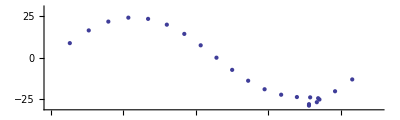

```mathematica
ListPlot[
  Table[{Ascension/Hour*15, Declination/Degree} /.
     EquatorCoordinates[Mars, {1986,1,day,0,0,0},
                        ViewPoint -> Earth],
        {day, -300, 350, 30}],
  PlotRange   -> {{0, 360}, {-30, 30}},
  AspectRatio -> 0.3]
```

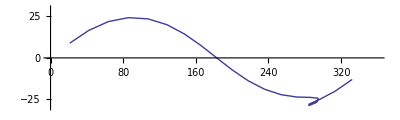

```mathematica
ListPlot[
  Table[{Ascension/Hour*15, Declination/Degree} /.
     EquatorCoordinates[Mars, {1986,1,day,0,0,0},
                        ViewPoint -> Earth],
        {day, -300, 350, 30}],
 Joined  -> True,
  PlotRange   -> {{0, 360}, {-30, 30}},
  AspectRatio -> 0.3]
```

Here's a plot of the x and y co-ordinates of Mercury as viewed from Earth.

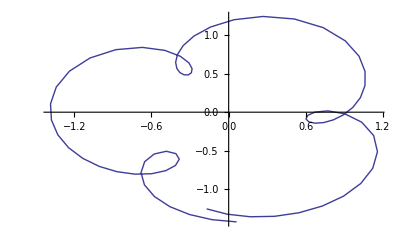

```mathematica
ListPlot[
  Table[Take[Coordinates[Mercury, {1986,1,d,0,0,0},
                         ViewPoint -> Earth], 2],
        {d, 1, 366, 5}],
  Joined -> True]
```

Here's a plot of the x and y co-ordinates of Mercury as viewed from Earth.

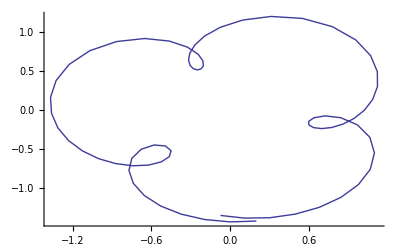

```mathematica
ListPlot[Table[Take[Coordinates[Mercury,{1993,1,d},ViewPoint->Earth],2],{d,1,366,5}],Joined->True]
```

7.1.3. Equator Coordinates command
These coordinates are useful in conjunction with Star charts.

```mathematica
Information["EquatorCoordinates",LongForm->False]
```

EquatorCoordinates[object, date] returns the Ascension, Declination and Distance of the object (a planet or a star) on the given date. An example planet would be Mars, and an example star would be Alpha.Centaurus. EquatorCoordinates[horizoncoords, date] will convert the horizoncoords for the current location into equatorcoords. An example horizoncoords would be {Azimuth->270*Degree, Altitude->30*Degree}. If date is omitted the current Date[] is used.

The EquatorCoordinates command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

Here are some basic examples:

```mathematica
EquatorCoordinates[Mars,{1993,11,17,3,20,0}]
```

{Ascension→16.2238 Hour,Declination→-0.377566,Distance→2.45251 AU}

```mathematica
-0.3775658684539316/Degree
```

-21.6329

```mathematica
(* d.h. Declination = -21.63425809263331 ° *)
```

```mathematica
EquatorCoordinates[Sun,{1993,11,17,3,20,0}]
```

{Ascension→15.464 Hour,Declination→-0.329059,Distance→0.988773 AU}

```mathematica
EquatorCoordinates[Moon,{1993,11,17,3,20,0}]
```

{Ascension→18.1124 Hour,Declination→-0.364836,Distance→0.00253195 AU}

Because the Moon is so close to Earth, you may sometimes want to set your viewpoint to the surface of Earth (i.e TopoCentric) rather than the default centre of the Earth.

```mathematica
EquatorCoordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{Ascension→18.1069 Hour,Declination→-0.350614,Distance→0.00255416 AU}

You can also find the equator coordinates of a star. The syntax for specifying a star name is to use: star.constellation. For example:

```mathematica
EquatorCoordinates[Alpha.Centaurus,{1993,11,17,3,20,0}]
```

{Ascension→14.6522 Hour,Declination→-1.06123,Distance→∞}

Note stars have fixed equator coordinates – that is they don't change with time. (Actually they do change a little with time due to the precession of the Earth's axis, but the effect is very small. Use the Epoch option to see the effect.)

The brightest 25 stars have also been given aliases, so for examples you can use Sirius, Canopus and Polaris etc as star names.

You can also find the equator coordinates of a point relative to the horizon at some local time. For example:

```mathematica
EquatorCoordinates[{Azimuth->60 °,Altitude->30 °},{1993,11,17,3,20,0}]
```

{Ascension→8.95884 Hour,Declination→0.0357012}

7.1.4. Horizon Coordinates command
These are useful when you are out in the field. A negative Altitude would mean the object is currently below the horizon.

```mathematica
Information["HorizonCoordinates",LongForm->False]
```

HorizonCoordinates[object, date] returns the Azimuth, Altitude and Distance of the object (a planet or a star) on the given date. An example planet would be Mars, and an example star would be Alpha.Centaurus. HorizonCoordinates[equatorcoords, date] will convert the equatorcoords into horizoncoords for the current location. An example equatorcoords would be {Ascension->18*Hour, Declination->30*Degree}. If date is omitted the current Date[] is used.

The HorizonCoordinates command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

Here are some basic examples:

```mathematica
HorizonCoordinates[Mars,{1993,11,17,3,20,0}]
```

{Azimuth→2.73305,Altitude→-0.470302,Distance→2.45251 AU}

```mathematica
HorizonCoordinates[Sun,{1993,11,17,3,20,0}]
```

{Azimuth→2.52169,Altitude→-0.43718,Distance→0.988773 AU}

```mathematica
HorizonCoordinates[Moon,{1993,11,17,3,20,0}]
```

{Azimuth→3.25458,Altitude→-0.541601,Distance→0.00253195 AU}

Because the Moon is so close to Earth, you may sometimes want to set your viewpoint to the surface of Earth (i.e TopoCentric) rather than the default centre of the Earth.

```mathematica
HorizonCoordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{Azimuth→3.25458,Altitude→-0.555888,Distance→0.00255416 AU}

You can also find the horizon coordinates of a star. The syntax for specifying a star name is to use: star.constellation. For example:

```mathematica
HorizonCoordinates[Alpha.Centaurus,{1993,11,17,3,20,0}]
```

{Azimuth→2.76911,Altitude→0.270423,Distance→∞}

You can also find the horizon coordinates of a fixed point on the celestial sphere. For example:

```mathematica
HorizonCoordinates[{Ascension->6 Hour,Declination->30 °},{1993,11,17,3,20,0}]
```

{Azimuth→0.0693045,Altitude→0.385432}

A command related to HorizonCoordinates is Refract.

```mathematica
Information["Refract",LongForm->False]
```

Refract[horizoncoords] converts true horizoncoords (i.e the horizon coordinates returned by the HorizonCoordinates command) into apparent horizon coordinates by adding an atmospheric refraction correction. The correction can amount to about 0.5 Degree for objects close to the horizon, but is otherwise quite small.

For example, the SunRise and SunSet commands correctly take into account atmospheric refraction. This means however that the true horizoncoords of the Sun is approximately half a degree below the horizon at sunrise or sunset. I.e

```mathematica
HorizonCoordinates[Sun,SunSet[],ViewPoint->TopoCentric]
```

{Azimuth→4.43166,Altitude→-0.00968923,Distance→0.987939 AU}

```mathematica
(* {Azimuth->244.8640453667117 °,Altitude->-0.5217329165497615 °,Distance->0.984371304509849 AU} *)
```

To correct this to see that the Sun is apparently at 0 degrees above the horizon, just apply Refract

```mathematica
Refract[HorizonCoordinates[Sun,SunSet[],ViewPoint->TopoCentric]]
```

Refract::noavail: This is just the demo version, and Refract is not available.

```mathematica
(* Refract[HorizonCoordinates[Sun,SunSet[],ViewPoint->TopoCentric]] *)
```

```mathematica
{Azimuth->244.8640453667117 °,Altitude->0.01944841877478964 °,Distance->0.984371304509849 AU}
```

The above shows that the atmospherically refracted position of the Sun is almost exactly on the horizon at sunset, which is where it should be at that time.

7.1.5. The Elongation command 
This is useful for indirectly determining the Rising and Setting times of a planet relative to local Sunrise and Sunset.

```mathematica
Information["Elongation",LongForm->False]
```

Elongation[object, date] returns the Elongation of the object (a planet or a star etc). This measures the angle that the object is East of the Sun. A negative angle would mean the object is West of the Sun. Objects with positive Elongation are mostly evening visible, whereas objects with negative Elongation are mostly morning visible. If date is omitted the current Date[] is used.

```mathematica
Elongation[Mars,{1993,11,17,3,20,0}]
```

0.198901

```mathematica
(* 7.713312735306147 ° *)
```

7.1.6. The Separation command 
This is useful for determining Conjunctions, Eclipses and Transits etc.

```mathematica
Information["Separation",LongForm->False]
```

Separation[object1, object2, date] returns the angular separation of the two objects (which may be planets, Sun, Moon, asteroids or stars etc) on the given date. If date is omitted the current Date[] is used. And if only one object is given, then the other object is assumed to be the Sun.

The Separation command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

```mathematica
Separation[Mars,Jupiter,{1993,11,17,12,0,0}]
```

0.599309

```mathematica
Separation[Venus,Neptune,{2991,3,22,13,40,0}]
```

0.021624

```mathematica
Separation[Venus,Antares,{4296,11,22,12,0,0}]
```

0.0675464

```mathematica
Ephemeris[Jupiter,{1993,11,17,12,0,0}]
```

Jupiter
------------------------------------------
Date Time:   17-Nov-1993 12:00:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        4:57 am (Sunrise:  6:09 am)
Setting:       6:10 pm (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       345^57' (North     compass)
Altitude:       62^30' (Above the horizon)
------- For Date Time: -------------------
Elongation:    -23^22' (Morning sky. 100%)
Distance:      6.34 AU (Magnitude:   -1.7)
------- For Date Time: -------------------
Ascension:    13h58.2m (Virgo        210^)
Declination:   -10^56' (Ecliptic +  1^04')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Mars,{1993,11,17,12,0,0}]
```

Mars
------------------------------------------
Date Time:   17-Nov-1993 12:00:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        6:36 am (Sunrise:  6:09 am)
Setting:       9:04 pm (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:        63^36' (NorthEast compass)
Altitude:       61^21' (Above the horizon)
------- For Date Time: -------------------
Elongation:     10^56' (Evening sky. 100%)
Distance:      2.45 AU (Magnitude:   +1.9)
------- For Date Time: -------------------
Ascension:    16h14.5m (Scorpius     244^)
Declination:   -21^41' (Ecliptic -  0^27')
------------------------------------------

-EphemerisData-

```mathematica
separation[body1_, body2_, date_]:=Module[{eph1,eph2,dec1,dec2,RA1,RA2},
eph1=Ephemeris[body1, date];RA1=eph1[[5,1]] Degree;
 dec1=eph1[[4,2]]Degree;
eph2=Ephemeris[body2,date]; RA2=eph2[[5,1]] Degree; dec2=eph2[[4,2]]Degree;
N[ArcCos[Sin[dec1]*Sin[dec2]+Cos[dec1]*Cos[dec2]*Cos[RA1-RA2]]]]
```

```mathematica
separation[Mars,Jupiter,{1993,11,17,12,0,0}]
```

0.602849

```mathematica
Separation[Mars,Jupiter,{1993,11,17,12,0,0}]
```

0.599309

```mathematica
(* 34.23618286227749 ° *)
```

```mathematica
Separation[Moon,Sun,{1993,11,17,3,20,0}]
```

0.651394

```mathematica
(* 37.32212951829216 ° *)
```

```mathematica
Separation[Venus,Sun,{1993,11,17,3,20,0}]
```

0.259445

```mathematica
Separation[Mars,Earth,{1993,11,17,3,20,0},ViewPoint->Sun]
```

2.82172

Here's a plot of the separation of the Moon and the Sun during the month of November in 1994. If the separation is less than about half a degree, then that will be a partial Solar Eclipse.

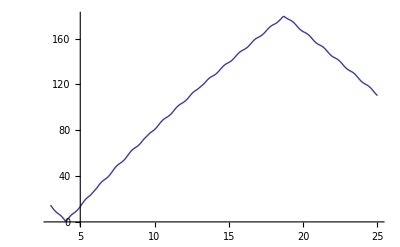

```mathematica
Plot[1/°Separation[Moon,Sun,{1994,11,d},ViewPoint->TopoCentric],{d,3,25}]
```

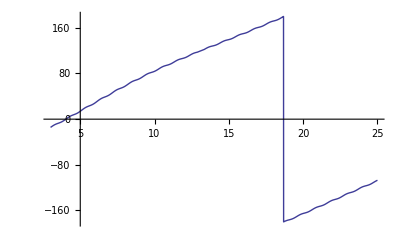

```mathematica
Plot[Elongation[Moon, {1994,11,d},ViewPoint->TopoCentric]/Degree, {d,3,25}]
```

In 1769 Captain Cook sailed to the Pacific to witness a transit of Venus across the solar disk. This happens only four times every 243 years. Here is the event (which happened at about 9AM on 4 June local time in Melbourne, but would have been about midday on 3 June in Tahiti) that he waited for:

WolframAlphaQueryParseResults

Sat 3 Jun 1769 22:49:43GMT+0.891111

```mathematica
Separation[Venus,Sun,{1769,6,4,9,0,0}]
```

0.00299225

```mathematica
Tahiti[]=Location["Tahiti, Polynesia", Deg[-17.67],Deg[-149.5],Mt[2241],-12]
```

Tahiti, Polynesia: lat. "17.670" S, long. "149.500" W, elev. 2241, zone "-12.00"

```mathematica
Trennung[Venus,Sun,{1769,6,4,9,0,0}, Tahiti[]]
```

0.00299225

```mathematica
(* 0.1714435384928253 ° *)
```

```mathematica
Trennung[Venus,Sun,{1769,6,4,9,0,0}, Tahiti[]]/Degree
```

0.171444

WolframAlphaQueryResults

1.557 °

```mathematica
PlanetData["Venus",EntityProperty["Planet","RiseTime",{"Location"-> Entity["Island","TahitiIsland"], "Date" -> {1769, 3, 6, 1, 0}}]]
```

Minute: Mon 6 Mar 1769 09:10GMT-9.97111

```mathematica
Elongation[Venus, {1769,6,4,9,0,0}]/Degree
```

-0.0211889

Ermittlung von Opposition:

```mathematica
Separation[Vesta,Sun,{1993,8,28, 0, 0, 0}]/°
```

170.16

```mathematica
separation[Vesta,Sun,{1993,8,28, 0, 0, 0}]/°
```

171.183

```mathematica
BestView[Sirius, {1993,11,17}]
```

BestView::noavail: This is just the demo version, and BestView is not available.

```mathematica
Separation[Moon,Mars,{1997,1,1, 7, 0, 0}]/°
```

3.96714

Ptolamaios meldete., im 17. Jahr Hadrians (Julianisch 133) hätte am 1./2. Epiphi eine Opposition Sonne-Jupiter und am 18. Epiphi eine Opposition Sonne-Saturn stattgefunden

```mathematica
Module[{datum=ConvertDateTo[Julian[132,12,31],Gregorian]},Do[datum=DaysPlusC[datum, 1];If[oppositionQ[Sun, Jupiter, datum], 
Print[ConvertDateTo[datum,Julian]]], {365}]]
```

9 May 133 C.E.

10 May 133 C.E.

11 May 133 C.E.

12 May 133 C.E.

13 May 133 C.E.

14 May 133 C.E.

15 May 133 C.E.

16 May 133 C.E.

17 May 133 C.E.

18 May 133 C.E.

19 May 133 C.E.

20 May 133 C.E.

21 May 133 C.E.

22 May 133 C.E.

23 May 133 C.E.

24 May 133 C.E.

25 May 133 C.E.

26 May 133 C.E.

Das Kerndatum dieser Opposition ist der 17./18. Mai 133 C.E.

```mathematica
ConvertDateTo[Julian[133,5,18],Egyptian]
```

2 Epiphi 880

```mathematica
Module[{datum=ConvertDateTo[Julian[132,12,31],Gregorian]},Do[datum=DaysPlusC[datum, 1];If[oppositionQ[Sun, Saturn, datum], 
Print[ConvertDateTo[datum,Julian]]], {365}]]
```

27 May 133 C.E.

28 May 133 C.E.

29 May 133 C.E.

30 May 133 C.E.

31 May 133 C.E.

1 June 133 C.E.

2 June 133 C.E.

3 June 133 C.E.

4 June 133 C.E.

5 June 133 C.E.

6 June 133 C.E.

7 June 133 C.E.

8 June 133 C.E.

9 June 133 C.E.

10 June 133 C.E.

11 June 133 C.E.

12 June 133 C.E.

13 June 133 C.E.

14 June 133 C.E.

Kerndatum dieser Opposition ist der 3./4. Juni

```mathematica
ConvertDateTo[Julian[133,6,3],Egyptian]
```

18 Epiphi 880

```mathematica
oppositionQ[Vesta, Sun, Gregorian[1993, 8, 28]]
```

True

(* Ein spezielleres Verfahren für den Merkurtransit *)

```mathematica
durchgangQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 
Module[{erg = False,h, sp1, sp2, eph},h=0;sp1= Separation[obj1, obj2, {y,m,d}]/Degree; 
sp2= Separation[obj1, obj2, {y,m,d, 8,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=8];
sp2= Separation[obj1, obj2, {y,m,d, 16,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=16];
If[sp1 < 2.0, eph = Ephemeris[Mercury, {y,m,d,h,0,0}]; If[(Last[eph][[2]] < 0.002) && (Abs[eph[[3,1]]] < 2), erg = True]]; erg]
```

```mathematica
durchgang2Q[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 
Module[{erg = False,h, sp1, sp2, eph},h=0;sp1= separation[obj1, obj2, {y,m,d}]/Degree; 
sp2= separation[obj1, obj2, {y,m,d, 8,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=8];
sp2= separation[obj1, obj2, {y,m,d, 16,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=16];
If[sp1 < 2.0, eph = Ephemeris[Mercury, {y,m,d,h,0,0}]; If[(Last[eph][[2]] < 0.002) && (Abs[eph[[3,1]]] < 2), erg = True]]; erg]
```

```mathematica
(* Hier der von Kepler vorausgesagte Transit zum 7.11.1631 *)
```

```mathematica
Module[{aktday},aktday= Gregorian[1631,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgangQ[Mercury, Sun, aktday],Print[aktday]; aktday = DaysPlusC[aktday, 7]], {365}]]
```

Friday, 7 November 1631

```mathematica
Module[{aktday},aktday= Gregorian[1631,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgang2Q[Mercury, Sun, aktday],Print[aktday]; aktday = DaysPlusC[aktday, 7]], {365}]]
```

Friday, 7 November 1631

(* Gem. Leipziger Repetitorium der deutschen und ausländischen Literatur, Bd. 26, S. 2 “ist Mercur (Phoenix), der sich alle 652 Jahre in der Sonnenstadt (Sonne) verbrannte... durch die Sonne gegangen; es war den astronomischen Tafeln gemäss am 8. April 1904 BCE geschehen” Gemeint ist julianisch, da die Tafeln vor Claudius 50 n.Chr. angefertigt waren. Wir berechnen den Beginn des bis zu 3-tägigen Merkurtransits: *)

```mathematica
Module[{aktday},aktday= Gregorian[-1903,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgangQ[Mercury, Sun, aktday],Print[ConvertDateTo[aktday,Julian]]], {365}]]
```

7 April 1904 B.C.E.

8 April 1904 B.C.E.

9 April 1904 B.C.E.

```mathematica
Module[{aktday},aktday= Gregorian[-1903,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgang2Q[Mercury, Sun, aktday],Print[ConvertDateTo[aktday,Julian]]], {365}]]
```

7 April 1904 B.C.E.

8 April 1904 B.C.E.

9 April 1904 B.C.E.

(* ebda: “Derselbe Phoenix... hatte sich zum ersten Male unter Sesostris in der Sonnentadt verbrannt; es war am 6. April 2555 geschehen” *)

```mathematica
Module[{aktday},aktday= Gregorian[-2554,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgangQ[Mercury, Sun, aktday],Print[ConvertDateTo[aktday,Julian]]], {365}]]
```

5 April 2555 B.C.E.

6 April 2555 B.C.E.

7 April 2555 B.C.E.

```mathematica
(* Diese "Verbrennung des Phoenix" wiederholt sich von Heliopolis aus gesehen alle 237780.5 Tage (d.h.grob alle 652 Jahre).Weitere Durchgänge nach eigenen Berechnungen: *)
```

```mathematica
Module[{aktday=Julian[-2555,4,6],greg},Do[greg= ConvertDateTo[aktday,Gregorian]; If[durchgangQ[Mercury, Sun, greg], Print["Merkurdurchgang bestätigt: "]];
Print[aktday, " = gregorianisch ",greg ];aktday= DaysPlusC[aktday, 237780]; If[Mod[i,2]==0,aktday= DaysPlusC[aktday, 1]],{i,1,9}]]
```

Merkurdurchgang bestätigt:

6 April 2555 B.C.E. = gregorianisch Monday, 16 March -2554

Merkurdurchgang bestätigt:

8 April 1904 B.C.E. = gregorianisch Friday, 22 March -1903

Merkurdurchgang bestätigt:

11 April 1253 B.C.E. = gregorianisch Wednesday, 31 March -1252

Merkurdurchgang bestätigt:

14 April 602 B.C.E. = gregorianisch Sunday, 7 April -601

Merkurdurchgang bestätigt:

17 April 50 C.E. = gregorianisch Friday, 15 April 50

Merkurdurchgang bestätigt:

19 April 701 C.E. = gregorianisch Tuesday, 23 April 701

Merkurdurchgang bestätigt:

22 April 1352 C.E. = gregorianisch Sunday, 30 April 1352

Merkurdurchgang bestätigt:

25 April 2003 C.E. = gregorianisch Thursday, 8 May 2003

Merkurdurchgang bestätigt:

28 April 2654 C.E. = gregorianisch Tuesday, 16 May 2654

Kepler hat nach Jupiter-Saturn Konjunktionen gesucht, die in etwa alle 20 Jahre stattfinden, und kam auf die Jahre 1583, 1603 etc. Hier ein Nachvollziehen der Berechnungen mit Startwerten jeweils ca 3 Jahre früher:

```mathematica
Module[{},aktday= Gregorian[1579,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[totaleConjQ[Jupiter, Saturn, aktday], Print[aktday]],{1500}]]
```

Wednesday, 4 May 1583

Thursday, 5 May 1583

Friday, 6 May 1583

Saturday, 7 May 1583

Sunday, 8 May 1583

Monday, 9 May 1583

Tuesday, 10 May 1583

Wednesday, 11 May 1583

Thursday, 12 May 1583

Friday, 13 May 1583

```mathematica
Module[{},aktday= Gregorian[1599,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[totaleConjQ[Jupiter, Saturn, aktday], Print[aktday]],{1500}]]
```

Thursday, 18 December 1603

Friday, 19 December 1603

Im Jahre 1682 wäre sogar eine (partielle) Konjunktion Mars-Jupiter-Saturn möglich:

```mathematica
Module[{},aktday= Gregorian[1679,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[partielleConjQ[Jupiter, Saturn, aktday] && totaleConjQ[Jupiter, Mars, aktday], Print[aktday]],{1500}]]
```

Wednesday, 16 September 1682

Thursday, 17 September 1682

Friday, 18 September 1682

```mathematica
(* Symposium : Konjunktion aller Planeten,Abweichung maximal 30 Grad bzw.alle Planeten stehen in einem oder 2 gegenüberliegenden Tierkreiszeichen,aufgereiht wie auf einer Schnur. Folgende Symposien kenne ich:5.5.2000,Mai 531 und 3102 vor Christus.Gab es weitere? 
Da das o.g. definierte Symposium recht häufig vorkommt und über einen vollen Monat dauern kann, definieren wir es strenger, d.h. Abweichungen < 10 Grad oder > 170 Grad *)
```

```mathematica
symposiumQ[Gregorian[y_,m_,d_]]:= Module[{merkurS,venusS,  erdeS, marsS, jupiterS, saturnS },
merkurS = Separation[Sun, Mercury, {y,m,d}]/Degree;
venusS =  Separation[Sun, Venus, {y,m,d}]/Degree;
erdeS = Separation[Sun, Earth, {y,m,d}]/Degree;
marsS =  Separation[Sun, Mars, {y,m,d}]/Degree;
jupiterS = Separation[Sun, Jupiter, {y,m,d}]/Degree;
saturnS = Separation[Sun, Saturn, {y,m,d}]/Degree;
((merkurS < 10) || (merkurS > 170)) &&  ((venusS < 10) || (venusS > 170)) && ((erdeS < 10) || (erdeS > 170)) && ((marsS < 10) || (marsS > 170)) && ((jupiterS < 10) || (jupiterS > 170)) && ((saturnS < 10) || (saturnS > 170)) ];
symposiumQ[jahr_Integer]:=Module[{aktday, erg=False},
aktday=Gregorian[jahr,1,1]; 
Do[aktday=DaysPlusC[aktday, 1]; If[symposiumQ[aktday],erg=True; Break[]],{365}];
erg]
```

```mathematica
symposiumQ[Gregorian[2025,1,22]]
```

False

```mathematica
symposiumQ[Gregorian[2000,5,5]]
```

False

```mathematica
symposiumQ[531]
```

False

```mathematica
Do[If[Mod[j,100]==0,Print["Jahr: ",j]];
If[symposiumQ[j], Print["Symposium im Jahr ",j]],{j,2000,3000}]
```

Jahr: 2000

Symposium im Jahr 2070

Jahr: 2100

Symposium im Jahr 2149

Jahr: 2200

$Aborted

```mathematica
symposium[2070]
```

Saturday, 11 October 2070

Sunday, 12 October 2070

Monday, 13 October 2070

Tuesday, 14 October 2070

Wednesday, 15 October 2070

Thursday, 16 October 2070

Friday, 17 October 2070

```mathematica
AstronomicalData["Mercury", {"Constellation",{1962,2,5}}]
```

Aquarius

```mathematica
horoskop[{1962,2,5}]
```

{{Moon,Aquarius},{Sun,Aquarius},{Mercury,Aquarius},{Venus,Aquarius},{Mars,Aquarius},{Jupiter,Aquarius},{Saturn,Aquarius}}

```mathematica
(* Astronom.Daten zur Überprüfung:Jupiter sei im Schützen,Saturn im Skorpion,Mars im Widder und Merkur in der Waage.Lt.Morosow ist dies, verbunden mit einer Sonnenfinsternis,am 30.09.395 C.E. vorgekommen, d.h proleptisch gregorianisch am 01.10.395 AD: *)
```

```mathematica
ConvertDateTo[Julian[395,9,30],Gregorian]
```

Sunday, 1 October 395

```mathematica
rückwärtshoroskop[{395,1,1},365,{Jupiter,Sagittarius},{Saturn, Scorpius},{Mars, Aries},{Mercury,Libra}]
```

{395,9,6}

{395,9,7}

{395,9,8}

{395,9,9}

{395,9,10}

{395,9,11}

{395,9,12}

{395,9,13}

{395,9,14}

{395,9,15}

{395,9,16}

{395,9,17}

{395,9,18}

{395,9,19}

{395,9,20}

{395,9,21}

{395,9,22}

{395,9,23}

{395,9,24}

{395,9,25}

{395,9,26}

{395,9,27}

{395,9,28}

{395,9,29}

{395,9,30}

{395,10,1}

{395,10,2}

{{395,9,6},{395,9,7},{395,9,8},{395,9,9},{395,9,10},{395,9,11},{395,9,12},{395,9,13},{395,9,14},{395,9,15},{395,9,16},{395,9,17},{395,9,18},{395,9,19},{395,9,20},{395,9,21},{395,9,22},{395,9,23},{395,9,24},{395,9,25},{395,9,26},{395,9,27},{395,9,28},{395,9,29},{395,9,30},{395,10,1},{395,10,2}}

Steine der Macht, Bd. 4: „Das hier bedeutet Sonne Opposition Mond und sagt aus, daß es eine Zeit des Vollmondes sein muss. Den gibt es aber jeden Monat einmal. Dann steht direkt an der Sonne der Jupiter, was jedes Jahr einmal vorkommt und daher noch nicht als genaue Datumsangabe dienen kann. Der Saturn steht im Trigon zur Sonne, und das ist in Verbindung mit dem Jupiter schon eine sehr präzise Angabe. Die beiden Planeten Jupiter und Saturn hat im ürigen der italienische Gelehrte Galileo im Jahr 1610 entdeckt. Seitdem hat man früher gerne versteckte Zeitangaben mit diesen beiden Planeten gemacht.”
Wir beginnen mit dem 1.1.2005 und suchen etwa 15 Folgejahre ab, sagen wir: 5500 Tage. Da die Konjunktionen leichter zu errechnen sind als Vollmonde, werden sie in der If-Abfrage vorangestellt:

```mathematica
Module[{},aktday= Gregorian[2004,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[partielleConjQ[Jupiter, Sun, aktday] && trineQ[Saturn, Sun, aktday] && FullmoonQ[aktday], Print[aktday]], {5500}]]
```

Sunday, 23 June 2013

Saturday, 12 July 2014

Auf die Funktion FullMoonQ können wir nicht verzichten. Approximieren wir dies durch oppositionQ, wird die Ausgabe unpräzise:

```mathematica
Module[{},aktday= Gregorian[2004,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[partielleConjQ[Jupiter, Sun, aktday] && trineQ[Saturn, Sun, aktday] && oppositionQ[Moon, Sun, aktday], Print[aktday]], {5500}]]
```

Monday, 12 January 2009

Monday, 24 June 2013

Sunday, 13 July 2014

```mathematica
(* Wenn nur der Geburtstag, aber nicht die Geburtsstunde bekannt ist, dann spielt der Mond keine Rolle *)
```

```mathematica
horoskop[{2013,6,23}]
```

{{Moon,Sagittarius},{Sun,Cancer},{Mercury,Cancer},{Venus,Cancer},{Mars,Gemini},{Jupiter,Gemini},{Saturn,Libra}}

```mathematica
(* Will man Exaktheit, dann muss man die Uhrzeit kennen *)
```

```mathematica
horoskop[{2013,6,23, 20, 0,0}]
```

{{Moon,Capricornus},{Sun,Cancer},{Mercury,Cancer},{Venus,Cancer},{Mars,Gemini},{Jupiter,Gemini},{Saturn,Libra}}

```mathematica
horoskop[{1960,10,9, 10, 0,0}]
```

{{Moon,Gemini},{Sun,Libra},{Mercury,Scorpius},{Venus,Scorpius},{Mars,Cancer},{Jupiter,Sagittarius},{Saturn,Capricornus}}

```mathematica
Map[Separation[Moon, #, {1960,10,9, 10, 0,0}]/Degree&, {Sun, Mercury, Venus, Mars, Jupiter, Saturn}]
```

{131.442,154.377,159.685,34.7672,156.182,139.913}

```mathematica
Map[Separation[Sun, #, {1960,10,9, 10, 0,0}]/Degree&, { Mercury, Venus, Mars, Jupiter, Saturn}]
```

{23.912,28.7454,97.2655,71.6626,88.197}

```mathematica
Map[Separation[Mercury, #, {1960,10,9, 10, 0,0}]/Degree&, {Venus, Mars, Jupiter, Saturn}]
```

{5.33804,121.06,47.9015,64.4217}

```mathematica
Map[Separation[Venus, #, {1960,10,9, 10, 0,0}]/Degree&, { Mars, Jupiter, Saturn}]
```

{126.011,42.9196,59.4546}

```mathematica
Map[Separation[Mars, #, {1960,10,9, 10, 0,0}]/Degree&, { Jupiter, Saturn}]
```

{168.921,174.51}

```mathematica
Separation[Jupiter, Saturn, {1960,10,9, 10, 0,0}]/Degree
```

16.5341

```mathematica
Separation2[Jupiter, Saturn, {1960,10,9, 10, 0,0}]/Degree
```

16.5341

```mathematica
(* Rückwärtshoroskop ohne Berücksichtigung von Mond, damit es an einem bestimmten Datum stabil bleibt 
Eingegeben werden ein mögliches Anfangsdatum, die Anzahl zu untersuchender Tage und vorgegebene Planetenkonstellationen auf Lateinisch, z.B. {Jupiter, Gemini} *)
```

```mathematica
rückwärtshoroskop[{2000,1,1},5500,{Venus, Cancer},{Jupiter, Gemini}, {Mercury, Cancer},{Mars, Gemini}, {Saturn, Libra}, {Sun, Cancer}]
```

{2013,6,23}

{{2013,6,23}}

```mathematica
rückwärtshoroskop[{2013,1,1},5500,{Venus, Cancer},{Jupiter, Gemini}, {Mercury, Cancer},{Mars, Gemini}, {Saturn, Libra}, {Sun, Cancer}]
```

{2013,6,22}

{2013,6,23}

{{2013,6,22},{2013,6,23}}

```mathematica
partielleConjQ[Sun, Jupiter, Gregorian[2013, 6, 23]]
```

True

```mathematica
trineQ[Sun, Saturn, Gregorian[2013, 6, 23]]
```

True

Messung der Präzession: Im Jahre 1950 wäre der Polarstern praktisch genau am nördlichen Sternhimmel, d.h. seine Deklination wäre nahezu 90°

```mathematica
EquatorCoordinates[Polaris, Epoch -> 1950.0]
```

{Ascension→1.60852 Hour,Declination→1.55387,Distance→∞}

```mathematica
1.55387/Degree
```

89.0302

Dagegen wird er in 2000 Jahren weit davon entfernt sein:

```mathematica
EquatorCoordinates[Polaris, Epoch -> 3950.0]
```

{Ascension→1.93408 Hour,Declination→1.43482,Distance→∞}

```mathematica
1.143482/Degree
```

65.5167

### 7.2. Grundsätzliches zu AstronomicalData

Im folgenden wollen wir einfache elementare Funktionen für Astronomen einsetzen, wie sie bereits unter Newton üblich waren. Leider wird die Einfachheit mit Ungenauigkeit erkauft, so erreichen errechnete Planetenpositionen nur für das 20ste und 21ste Jh eine Genauigkeit von < 2 Gradminuten.

Ein Himmelkörper umkreist die Sonne idR auf einer Ellipsenbahn, mit leichten Abweichungen durch Störungen (Perturbationen) durch andere Planeten.
Perihelion und Aphelion sind die Punkte der Planetenbahn mit der geringsten bzw. größten Distanz zur Sonne. Analog sind Perigäum und Apogäum die Punkte der Mondbahn mit der gerinsten bzw. größten Distanz zur Erde.
Der Himmelskugel ist eine unendlich groß gedachte Kugel um die Sonne, der Himmelsäquator die Projektion des Erdäquators auf die Himmelskugel, und die Ekliptik die Projektion der Erdbahn auf die Himmelskugel, mit einer Neigung von 23°27' (=Schiefe der Ekliptik).
Die Ekliptik schneidet den Himmelsäuator an 2 Punkten, welche Frühlings- und Herbstpunkt heißen. Man unterteilt die Ekliptik in die 12 Tierkreiszeichen a 30°, beginnend mit dem Widder am Frühlingsequinox, den im Gegenuhrzeigersinn Stier,  Zwillinge, Krebs, Löwe, Jungfrau, Waage, Skorpion, Schütze, Steinbock, Wassermann und Fische folgen.
Die Deklination ist der Winkelabstand eines Punktes zum Himmelsäquator (von +90° Nord bis -90° Süd), die "Right Ascension" ist die Unterteilung des Himmelsäquators in 24 Stunden a 15°, 0 Uhr beginnt beim Frühlingsequinox, gezählt wird im Gegenuhrzeigersinn.
Longitude und Latitude sind Längen- und Breitengrad des irdischen Globus, am Himmelsglobus projiziert.
Die heliozentrische Position betrachtet alle Daten aus dem Mittelpunkt der Sonne, die geozentrische aus dem Mittelpunkt der Erde und die topozentrische aus einem Punkt auf dem Erdglobus. Für Himmelskörper außer dem Mond beträgt die Differenz zwischen geozentrischer und topozentrischer Position vernachlässigbare 1 bis 2 Gradminuten.
Planetenbahnelemente bestehen aus 6 Parametern, wobei 3 die Form und Größe der elliptischen Bahn sowie die Planetenposition darin bezeichnen, und 3 die Lage der Bahn im Raum:
a = Distanz (idR in Astronom. Einheiten)
e = Exzentrität
tg = Zeit beim Perihel
i = Inklination relativ zur Ekliptik, 0 bis 180°. Bei einer
 Inklination über 90° bewegt sich der Planet rückwärts.
ng= Winkel zwischen Frühlingsequinox und Ascending Node.
w = Winkel zwischen Ascending Node und Perihelion.

Hieraus lassen sich weitere Werte ableiten:
Perihelion-Distanz q = a*(1-e)
Apohelion-Distanz qg = a*(1+e)
Orbitalperiode Pg = 365.256898326*a^1.5/Sqrt[1+m] dygn, mit  Planetenmasse m.
Tagesbewegung n = 360 Degree/pg Degree/Day.
Tageszählung t, meist als JD. tg ist in der gleichen Einheit  anzugeben.
Zeit seit Perihelion = t - tg.
Anomalie mg = n*(t-tg), beim Perihel 0° u beim Apohel 180°.
Longitude lg = mg+w+ng
Exzentritätsanomalie eg, wobei eg == mg+e*Sin[eg]
Echte Anomalie v = Winkel zwischen Perihel und Planet, von Sonne  aus  betrachtet.
Heliozentr. Distanz r des Planeten von der Sonne.
Die beiden letzen Variablen erfüllen die Gleichungen 
 {r*Cos[v]==a*(Cos[eg]-e), r*Sin[v]==a*Sqrt[1-e*e]*Sin[eg]}

### 7.3 Extraterrestische Kalender

### 7.3.1 Auf dem Mars

```mathematica
JulianDay[date_]:= JDFromFixed[ToFixed[date]]
```

```mathematica
JulianDay[Gregorian[2013,1,1]]
```

2.45629×10^6

```mathematica
ConvertDateTo[date_,MarsSolDate]:= MarsSolDate[(JulianDay[date]-2451549.5+0.00014)/1.02749125 + 44795.9998]
```

```mathematica
ConvertDateTo[MarsSolDate[msd_], Gregorian]:= Module[{jd, fd},jd=(msd-44795.9998)*1.02749125-0.00014+2451549.5; fd=FixedFromJD[jd]; ConvertDateTo[fd,Gregorian]]
```

```mathematica
ConvertDateTo[Gregorian[2013,1,1],MarsSolDate]
```

MarsSolDate[49413.1]

```mathematica
ConvertDateTo[MarsSolDate[49413.3],Gregorian]
```

Tuesday, 1 January 2013

```mathematica
ConvertDateTo[date_,MarsTimeCoordinated]:= MarsTimeCoordinated[Mod[First[ConvertDateTo[date,MarsSolDate]],86400]*24]
```

```mathematica
ConvertDateTo[Gregorian[2013,1,1],MarsTimeCoordinated]
```

MarsTimeCoordinated[1.18591×10^6]

```mathematica
EquiSol[1955]
```

{{Monday, 21 March 1955,{9,39,57.1282}},{Wednesday, 22 June 1955,{4,39,34.0773}},{Friday, 23 September 1955,{19,49,5.67654}},{Thursday, 22 December 1955,{15,15,25.5754}}}

```mathematica
EquiSolMars[y_]:=
Module[{eq0=ToFixed[Gregorian[1955,4,11]]+(y-1955)*365.244},
If[y>1582,
Map[Gregorian[Round[#]]&,{eq0,eq0+92.764,eq0+186.411,eq0+276.247}],
Map[Julian[Round[#]]&,{eq0,eq0+92.764,eq0+186.411,eq0+276.247}]]]
```

```mathematica
EquiSolMars[1955]
```

{Monday, 11 April 1955,Wednesday, 13 July 1955,Friday, 14 October 1955,Thursday, 12 January 1956}

```mathematica
EquiSolMars[1776]
```

{Tuesday, 9 April 1776,Thursday, 11 July 1776,Sunday, 13 October 1776,Saturday, 11 January 1777}

```mathematica
EquiSolMars[33]
```

{9 April 33 C.E.,11 July 33 C.E.,12 October 33 C.E.,10 January 34 C.E.}

```mathematica
EquiSolMars[-1515]
```

{18 April 1516 B.C.E.,20 July 1516 B.C.E.,22 October 1516 B.C.E.,20 January 1515 B.C.E.}

### 7.3.2. Auf dem Jupiter

```mathematica
ConvertDateTo[date_,DavidianJovian]:=Module[{ed}, ed = DayNumber[date]; ed = (ed-1)/(ed+DaysRemaining[date])+date[[1]];
DavidianJovinian[((ed+10000)*365.26)/4331.572]]
```

```mathematica
ConvertDateTo[DavidianJovian[jd_],Gregorian]:=Module[{ed, j}, ed = N[((jd*4331.572)/365.26)-10000, 20]; j = Floor[ed];  ed = ed - j; 
ed = Floor[ed* (DaysRemaining[Gregorian[j,1,1]]+1)]; 
DaysPlusC[Gregorian[j,1,1], ed]]
```

```mathematica
ConvertDateTo[Gregorian[1969,7,20],DavidianJovian]
```

DavidianJovinian[1009.33]

```mathematica
ConvertDateTo[DavidianJovian[1009.33], Gregorian]
```

Tuesday, 8 July 1969

Etwas unpräzise, der Monat wird noch getroffen

### 7.3.3. Im Sonnensystem

Folgende Planeten untersuchen wir:

```mathematica
AstronomicalData["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

Ihre Umlaufszeiten um die Sonne:

```mathematica
AstronomicalData[#,"OrbitPeriodYears"]&/@AstronomicalData["Planet"]
```

{0.2408467,0.61519726,1.0000174,1.8808476,11.862615,29.447498,84.016846,164.79132}

Satelliten des Pluto:

```mathematica
AstronomicalData["Pluto","Satellites"]
```

{Charon,S2012P1,Nix,S2011P1,Hydra}

```mathematica
?AstronomicalData
```

WolframAlphaQueryParseResults

Cydonia

```mathematica
PlanetData["Venus",EntityProperty["Planet","RiseTime",{"Location"-> WolframAlphaQueryParseResults}]]
```

Missing[RetrievalFailure]

Wieviel bekannte Satelliten hat welcher Planet:

```mathematica
Length[AstronomicalData[#,"Satellites"]]&/@AstronomicalData["Planet"]
```

{0,0,1,2,63,61,27,13}

Die kürzeste Distanz zwischen Erde und den Planeten des Sonnensystems wöhrend eines Jahres ermitteln:

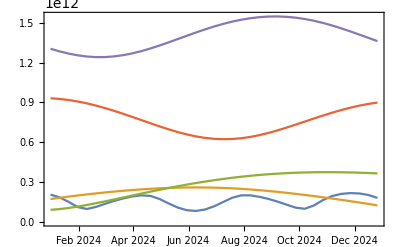

```mathematica
DateListPlot[Tooltip[Table[{DateList[{2024,1,i}],AstronomicalData[#,{"Distance",DateList[{2008,1,i}]}]},{i,1,365.25,10}],#]&/@{"Mercury","Venus","Mars","Jupiter","Saturn"},Joined->True]
```

```mathematica
AstronomicalData["Moon","Density"]
```

3344. kg/m^3

### 7.4. Relativistische Zeiteffekte

Durch Einsteins Spezielle Relativitätstheorie konnte gezeigt werden, daß die Zeit keine absolute Größe ist: je höher die Geschwindigkeit des beobachteten Inertialsystems, desto langsamer altert es relativ zum Beobachter. Diese Zeitdilatation kann durch die Formel von Lorentz exakt berechnet werden:

```mathematica
c0= 299792.4562*1000 Meter/Second; (* die Lichtgeschwindigkeit *)
t0= 1 Hour; (* dies sei die Meßdauer des Beobachters *)
trel[v_] := t0*Sqrt[1-(v/c)^2] /. c :> c0  
(* die Zeit, die während der Meßdauer für das beobachtete Objekt vergeht *)
v1 = 0.25*1000 Meter/Second; (* Reise im Jet *)
trel[v1]
```

1. Hour

```mathematica
(* Dies ist gerundet, doch wir wollen exakter rechnen: *)
N[%, 20]
```

```mathematica
0.999999999999652 Hour
```

Das Objekt bleibt um Sekundenbruchteile jünger.

```mathematica
v2 = 260000*1000 Meter/Second; (* Beschleunigung eines Elektrons *)
trel[v2]
```

```mathematica
0.497844 Hour
```

Das Elektron altert nur um ca. die Hälfte seines Beobachters. Analog zur Zeitdilatation erfolgt auch eine Längenkontraktion sowie eine Massenzunahme, d.h. das Elektron hat bei dieser Geschwindigkeit ca. doppelte Masse als im (imaginären) Ruhzustand. Bei allen Teilchen, die eine Masse > 0 besitzen, führt dies zur Unmöglichkeit, die Lichtgeschwindigkeit zu erreichen.

```mathematica
v3=c; (* Photon *)
trel[v3]
```

```mathematica
0
```

Teilchen, die sich mit c bewegen (Photonen, Neutrinos), gehören zur Klasse der Luxonen; Teilchen, die stets langsamer als c sind (alle massebehafteten Körper) gehören zur Klasse der Tardyonen.
Luxonen altern überhaupt nicht. Für sie ist seit Anbeginn der Welt noch keine Nanosekunde vergangen. Im Inertialsystem der Tardyonen läßt sich ein "Vorher" und ein "Nachher" unterscheiden, z.B. der aus der Taschenlampe kommende Lichtstrahl, der später von einem Spiegel reflektiert wird, noch später durch unsere Brille eintritt und zuletzt auf der Netzhaut unseres Auges den Wahrnehmungseffekt auslöst : das Ursache-Wirkungs-Prinzip. Für Luxonen verläuft alles gleichzeitig, in ihrem Inertialsystem gibt es kein "Vorher" und "Nachher", keine Ursache und Wirkung.
1967 gesellte man hierzu eine Klasse von Teilchen namens Tachyonen, die schneller sind als c und für welche die Zeit in komplexzahligen Sekunden verlaufen muss.
1965 war der Nobelpreis an Richard Feynmann, Prof. für Theoretische Physik am California Institute of Technology (CalTech) gegangen. Er hatte mathematisch exakt nachgewiesen, daß für Positronen (positiv geladene Elektronen) unter bestimmten Bedingungen die Zeit rückwärts abläuft. Dr. K. Scharnhorst, Physiker an der Berliner Humboldt-Universität, konnte nachweisen, daß die Geschwindigkeit von Photonen, die sich senkrecht zwischen 2 im Abstand von 10^-3 mm aufgestellten Platten bewegen, wegen eines quantenphysikalischen Phänomens namens Casimir-Effekt um 10^-36 km/Sekunde höher als c liegt. Lt. Paul Davies von der University of Newcastle/England hat diese infinitesimale Überschreitung von c "unübersehbare Folgen", da sie Phänomene ermöglicht, welche das Axiom der Kausalität verletzen.
Geschwindigkeiten weit über c setzt auch die Informationsübertragung zwischen Photonen voraus, die als Einstein-Rosen-Paradoxon bekannt geworden ist. Auf Grundlage der durch Photonen möglichen Speichereffekte und einer sich in unendlich viele Parallelprozesse aufteilenden Informationsübertragung durch Photonen soll ein Quantencomputer möglich sein, der jedes endliche mathematische Suchproblem in 0 Sekunden lösen kann.

[Anhang: Zu untersuchen]

Newtons Zeittabelle:
Er benutzte hauptsächl. Zeitrechnung JP, wobei AD = JP - 4713

```mathematica
ConvertDateTo[JP[year_,month_,day_],Gregorian]:=Gregorian[year -
```

```mathematica
4193-4713
```

-520

beginn d 8 jähr. regierung cambyses JP 4185 AD -528
beginn d 6 jähr regierung darius hytaspis JP 4193 AD -520
beginn der Regierung Artaxerxes Longimanus: JP 4250 AD -463
esra nach jerusalem: JP 4257 AD -456 = 80. Olympiade
nehemia nach jerusalem: JP September 4278 (=25 Elul) AD -435
7. Jahr des Peloponnes Krieges u Tod des Artaxerxes Longimanus JP 4289 AD -424
geburt christi: JP 4712 AD -1
kreuzigung christi: JP 4747 AD 34 (dann enden alle 7 Jahre mit jüd. Sabbatjahr)
ruf des cornelius u heiden: JP 4754 AD 41
erster angriff vespasians AD 67 (letzte Woche)
zerstörung jerusalems AD 70

ConvertDate

The same thing I gather also thus. Cambyses began his Reign in spring An. J.P. 4185, and reigned eight years, including the five
months of Smerdes; and then Darius Hytaspis began in spring An. J.P. 4193, and reigned thirty six years, by the unanimous
consent of all Chronologers. The reigns of these two Kings are determined by three eclipses of the moon observed at Babylon,
and recorded by Ptolemy; so that it cannot be disputed.

One was in the seventh year of Cambyses, An. J.P. 4191, Jul. 16, at
11 at night; another in the 20th year of Darius, An. J.P. 4212, Nov. 19, at 11 h. 45 at night; a third in the 31st year of Darius,
An. J.P. 4223, Apr. 25, at 11 h. 30 at night.

```mathematica
Map[#-4713&, {4191, 4212, 4223}]
```

{-522,-501,-490}

```mathematica
Map[Take[#,{ 2, 7}]&,Flatten[Table[AllLunE[i],{i,-522,-522}],1]]
```

{{-522.,1,20.,15.,23.,38.},{-522.,7,17.,1.,23.,12.}}

```mathematica
Take[VollmondAlternate[-523],{7,7}]
```

{{16 July 523 B.C.E.,{20.,0.,16.5688}}}

```mathematica
LunarEclipse[{DateObject[{-522,1,1,0,0}],DateObject[{-522,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Mon 20 Jan -522 12:38:00GMT+2.,Wed 16 Jul -522 22:38:00GMT+2.}

```mathematica
Map[Take[#,{ 2, 7}]&,Flatten[Table[AllLunE[i],{i,-501,-501}],1]]
```

{{-501.,5,26.,16.,54.,48.},{-501.,6,25.,0.,14.,49.},{-501.,11,20.,1.,41.,38.}}

```mathematica
Take[VollmondAlternate[-502],{11,11}]
```

{{19 November 502 B.C.E.,{20.,21.,53.5152}}}

```mathematica
LunarEclipse[{DateObject[{-501,1,1,0,0}],DateObject[{-501,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Sat 26 May -501 14:14:00GMT+2.,Sun 24 Jun -501 21:34:00GMT+2.,Mon 19 Nov -501 23:03:00GMT+2.}

```mathematica
Map[Take[#,{ 2, 7}]&,Flatten[Table[AllLunE[i],{i,-490,-490}],1]]
```

{{-490.,4,26.,0.,21.,38.},{-490.,10,19.,5.,7.,52.}}

```mathematica
Take[VollmondAlternate[-491],{4,4}]
```

{{25 April 491 B.C.E.,{19.,5.,31.5446}}}

```mathematica
LunarEclipse[{DateObject[{-490,1,1,0,0}],DateObject[{-490,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Tue 25 Apr -490 21:44:00GMT+2.,Thu 19 Oct -490 02:31:00GMT+2.}

The passage of Xerxes's army
over the Hellespont began in the end of the fourth year of the 74th Olympiad, that is, in June An. J.P. 4234

```mathematica
OlympiadExact[74,5]
```

21 July 480 B.C.E.

```mathematica
4234-4713
```

-479

Anscheinend hat sich Newton um 1 Jahr verkalkuliert, die -479 soll ein jahr im Julianische Kalender sein

, and took up one
month: and in autumn, three months after, on the full moon, the 16th day of the month Munychion, was the battle at Salamis

```mathematica
VollmondAlternate[-480][[9]]
```

{18 September 480 B.C.E.,{5.,13.,18.6728}}

```mathematica
VollmondAlternate[-479][[9]]
```

{7 September 479 B.C.E.,{16.,52.,33.7467}}

Laut heutigen Historikern eher 26. September 480 BCE, ohne Vollmond

and a little after than an eclipse of the sun, which by the calculation fell on Octob. 2

Hier geht Newton wieder ein Jahr vor, Folgefehler von oben:

```mathematica
Map[Take[#,{ 3, 8}]&,Flatten[Table[AllSolE[i],{i,-479,-479}],1]]
```

{{-479.,4,9.,1.,53.,28.},{-479.,10,2.,16.,30.,1.}}

```mathematica
{{-4.,4,19.,9.,7.,31.},{-479.,10,13.,17.,7.,20.}}
```

It is possible, therefore, to calculate when the
position of Regulus corresponded to 0° b, i.e., the moment when the sidereal and tropical zodiacs were perfectly aligned. Since
the apparent stellar motion is forward, we simply deduct the time equivalent of 28° 43' from January 1, 1920 at the rate of 50."
of arc per year.The result is 2,056.4949. . .years.

```mathematica
1920 - 2056.4949
```

-136.495

```mathematica
(* Der Monat wäre Ende Mai *)
```

```mathematica
0.495*12
```

5.94

```mathematica
Ephemeride[Regulus, {-136,5,31}, Hamburg[]]
```

Alpha . Leo
------------------------------------------
Date Time:   01-Jun--137 00:00:00. (GMT+ 1)
Geo-place:      10^00'E,  53^33'N (Earth.)
------- For Date, Geo-place: -------------
Rising:       11:13 am (SunriseP:  7:30 am)
Setting:       8:47 pm (SunsetP:   5:09 pm)
------- For Date Time, Geo-place: --------
Azimuth:        30^09' (NorthEast compass)
Altitude:       23^27' (Above the horizon)
------- For Date Time: -------------------
Elongation:     52^10' (Evening sky. 100%)
Distance:    ****** AU (Magnitude:   +1.4)
------- For Date Time: -------------------
Ascension:     8h14.9m (Cancer       124^)
Declination:    22^31' (Ecliptic +  2^24')
------------------------------------------

-EphemerisData-